One atom basis lattice vibrations (phonon modes)

```mathematica
(* named global variables *)
Clear[windowHalfWidth, kMax, mMax, primaryDisplaySize]
windowHalfWidth = 3 ;
kMax = 0.9 ;
primaryDisplaySize = 200 ;

(* for only one mass, no point having both mass and the spring constants as free parameters.  mMax is used, but really only to size the mass Point graphic. *)
mass = 10 ;
mMax = 30 ;

Clear[ springLatticeData ]
springLatticeData= {
{Darker@Orange,1,0,0,0,0,1},
{Darker@Green,0,1,0,0,1,0},
{Darker@Purple,1,1,0,0,0,0},
{Darker@Cyan,-1,1,1,0,1,0}
} ;

Clear[ dynTab, freqTab, parametersTab ]
{  dynTab, freqTab, parametersTab } =  Range[3] ;

(* functions *)

(* Based on a ListLinePlot version posted in: http://mathematica.stackexchange.com/a/37228/10 *)
ClearAll[springPoints]
springPoints::usage = "springPoints[ point1, point2, numberOfTurns, height, fractionToDrawAsLinesAtEnds ].  Example:

ListLinePlot[springPoints[{1,2},{3,5}], AspectRatio→Automatic, PlotStyle -> Darker[ Purple ] ]" ;
springPoints[ a1_List, a2_List, n_Integer:8,h_:.05, f_: 0.1 ] :=Module[{n1, d, nd, r, r1 },

n1 = Norm[a1] ;
d = a2 - a1 ;
nd = Norm[d] ;
r = RotationMatrix[ArcTan @@  d ] ;
r1 = r . {n1, 0} ;

{
Table[ a1 -r1 + r . { n1 + nd f + t (1 - 2f) nd, h Sin[ 2 Pi n t]}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 + nd f + (1 - 2f) nd + t f nd, 0}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 +t f nd, 0}, {t, 0, 1, 0.01 } ]
}
]

ClearAll[indexLable] ;
indexLable::usage = "k_i(or other character) in italic. indexLable['k', 1]" ;
indexLable = Subscript[Style[#1,Italic], #2] & ;

ClearAll[kLable] ;
kLable::usage = "k_i(or other character) in italic and colored by spring index. kLable[k]" ;
kLable = Style[ indexLable["k", #], FontColor->First[springLatticeData[[#]]] ] & ;

ClearAll[lineTable]
lineTable[ n_List, b_List, i_List ] :=Module[{first, second},
{first, second} = i ;
Table[
Line[
{-n[[first]]b[[first]] + j b[[second]],n[[first]]b[[first]] + j b[[second]]} 
] 
, {j, -n[[second]], n[[second]]}
]
] ;

ClearAll[ calcReciprocalBasis ]
calcReciprocalBasis::usage = "Return a reciprocal frame basis for a set of vectors.  This doesn't include the 2 π scaling that is common in solid state physics.  Example, displaying the desired Kronicker delta behaviour:

b = {{2,1},{-1/4, 2}} ;
g = calcReciprocalBasis[ b ] ;

{g[[1]].loc[[1]],
g[[1]].loc[[2]],
g[[2]].loc[[1]],
g[[2]].loc[[2]]}
" ;
calcReciprocalBasis[loc_List] := Inverse[ Transpose[ loc ] ] ;

ClearAll[ pointsTable ] ;
pointsTable[ mPosFirstCell_List, latticeBasis_List, numberLatticeLinesToDisplay_List ] := Table[ 
mPosFirstCell + {i,j}. latticeBasis
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] ;

(* This could use some heavy optimization.  It doesn't make much sense to do all the springs separately, when one set of plot points could be calculated once for a given direction, and then just translated for the rest of the springs with that orientation.
*)
ClearAll[ springLatticePlot ] ;
springLatticePlot[ calcResults_List, {color_, iOff_Integer, jOff_Integer, iStartAdj_, jStartAdj_, iRangeAdj_Integer, jRangeAdj_Integer},springStrengthFraction_] := Module[{pointsDataTable, numberLatticeLinesToDisplay},

{pointsDataTable,numberLatticeLinesToDisplay}={"pointsDataTable","numberLatticeLinesToDisplay"} /. calcResults ;

ListLinePlot[
Flatten[Table[
springPoints[ pointsDataTable[[i,j]], pointsDataTable[[i+iOff,j + jOff]], Ceiling[8 springStrengthFraction] ],
{i, 1 + iStartAdj, numberLatticeLinesToDisplay[[1]] * 2 + iRangeAdj},
{j, 1 + jStartAdj, numberLatticeLinesToDisplay[[2]] * 2 + jRangeAdj}
], 2] ,
PlotStyle ->  color ]
];


locDependent[aLoc_, bLoc_, mLoc_] := Module[{latticeBasis, numberLatticeLinesToDisplay,reciprocalBasis,mObliqueComponents, mPosFirstCell},
latticeBasis = {aLoc, bLoc} ;
numberLatticeLinesToDisplay = (Ceiling[  Abs[windowHalfWidth/ latticeBasis[[#]][[#]]]] & /@ Range[2]) ;
reciprocalBasis = calcReciprocalBasis[ latticeBasis ] ;
mObliqueComponents = ((mLoc . reciprocalBasis[[#]]) &) /@ Range[2]  ;
mPosFirstCell = mLoc - Floor[mObliqueComponents] . latticeBasis  ;

{
"aLoc"->aLoc,"bLoc"->bLoc,"mLoc"->mLoc,
"latticeBasis"->latticeBasis,
"latticeNorms"->(Norm[latticeBasis[[#]]] & /@ Range[2]),
"latticeUnitVectors"->(Normalize[latticeBasis[[#]]] & /@ Range[2]),
"numberLatticeLinesToDisplay"-> numberLatticeLinesToDisplay,
"reciprocalBasis"-> reciprocalBasis,
"reciprocalNorms"-> (Norm[reciprocalBasis[[#]]] & /@ Range[2]),
"mObliqueComponents"-> mObliqueComponents,
"mPosFirstCell"-> mPosFirstCell,
"pointsDataTable"-> pointsTable[mPosFirstCell,latticeBasis,numberLatticeLinesToDisplay],
"lineTable" -> (lineTable[ numberLatticeLinesToDisplay, latticeBasis, # ] & /@ Permutations[{1,2}])
}
]

plotSprings[k1_, k2_, k3_, k4_, calcResults_] := Module[{latticeBasis,reciprocalBasis,pointsDataTable, numberLatticeLinesToDisplay, lines},

{latticeBasis,reciprocalBasis,pointsDataTable,numberLatticeLinesToDisplay, lines}={"latticeBasis","reciprocalBasis","pointsDataTable","numberLatticeLinesToDisplay", "lineTable"} /. calcResults ;

Show[{
Graphics[{
lines
,Blue,Arrow[{{0,0}, reciprocalBasis[[#]]}] & /@ Range[2]
,Thick,Arrowheads[0.05]
,Red,Arrow[{{0,0}, latticeBasis[[#]]}] & /@ Range[2]
,Blue
,PointSize[Sqrt[mass/mMax/500]]
,Point[ # ] & /@ pointsDataTable 
, Green, Point[ {0,0}]
}
,PlotRange -> {{-windowHalfWidth/2, windowHalfWidth}, {-windowHalfWidth/2, windowHalfWidth}}
,ImageSize->primaryDisplaySize
],
k1,
k2,
k3,
k4
}]
]

ClearAll[ projOp ] ;
projOp::usage = "given an input vector v⃗ = {v_x, v_y}, compute the projection matrix operator along the unit vector in that direction.

   projOp[{1, 0}] // MatrixForm = (1 | 0
0 | 0)
projOp[{0, 1}] // MatrixForm = (0 | 0
0 | 1)
projOp[{a,b}] // MatrixForm = (a^2/(a^2+b^2) | (a b)/(a^2+b^2)
(a b)/(a^2+b^2) | b^2/(a^2+b^2))
" ;
projOp[v_List] := {{v[[1]]^2, v[[1]]v[[2]]},{v[[1]]v[[2]], v[[2]]^2}}/(v. v) ;

ClearAll[ aM ] ;
aM::usage = "
The dynamics of the system are all contained in the matrix equation:

(ω^2 | 0
0 | ω^2) - - aM) ϵ⃗ = 0 
 
where,

OverVector[u_n] = ϵ⃗ E^(I (OverVector[r_n] . q⃗ - ω t))
OverVector[r_n] = n_1 a⃗ + n_2b⃗ 

Examples:
aM[{q_x,q_y}, {a_x,a_y}, {b_x,b_y}, k_1,k_2,k_3,k_4, m] // MatrixForm // TraditionalForm = ... (messy) 

aM[{q_x,q_y}, a{1, 0}, a{0, 1}, k_1,k_2,k_3,k_4, m] // Factor  // MatrixForm // TraditionalForm = (*Cell[TextData[Cell[BoxData[
FormBox[
TagBox[
RowBox[{"(", "", GridBox[{
{
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{"2", " ", 
SubscriptBox["k", "1"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
FractionBox[
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "2"], ")"}]}]}], ")"}]}], "m"], 
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "-", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}]}], ")"}]}], "m"]},
{
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "-", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}]}], ")"}]}], "m"], 
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{"2", " ", 
SubscriptBox["k", "2"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
FractionBox[
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "2"], ")"}]}]}], ")"}]}], "m"]}
},
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {
Offset[0.27999999999999997`], {
Offset[0.7]}, 
Offset[0.27999999999999997`]}, "ColumnsIndexed" -> {}, "Rows" -> {
Offset[0.2], {
Offset[0.4]}, 
Offset[0.2]}, "RowsIndexed" -> {}}], "", ")"}],
Function[BoxForm`e$, 
MatrixForm[BoxForm`e$]]], TraditionalForm]],
CellChangeTimes->{3.5990563268386803`*^9, {3.5990565758059196`*^9, 3.5990566126100254`*^9}, 3.599056660298753*^9, {3.599056905058752*^9, 3.599056911414116*^9}, 3.5990570494260097`*^9, 3.5990570802537727`*^9, {3.5990923676281567`*^9, 3.599092423296341*^9}}]]])

" ;
aM[ qq_List, a_List, b_List, k1_, k2_, k3_, k4_, m_ ] := (4/m)(
projOp[a]k1 Sin[ a . qq /2 ]^2 + projOp[b]k2 Sin[ b . qq /2 ]^2+ projOp[a + b]k3 Sin[ (b + a) . qq /2 ]^2+ projOp[b - a] k4 Sin[ (b  -a) . qq /2 ]^2) ;

ClearAll[ frequencyPlot ] ;
frequencyPlot::usage = "frequencyPlot[ aM[#, {1,0}, {0,1}, 8, { 2 Pi, 2 Pi }, 0.5, 0.5, 0.25, 0.25, 1] &, ld ]" ;
frequencyPlot[mat_, ld_, meshSize_] := Module[{eigTable, qMax, omegaPointList, range},

qMax = 2 Pi("reciprocalNorms" /. ld) ;

eigTable = Flatten[Re[Table[  {{qx, qy} ,Eigenvalues[ mat[ {qx, qy}  ] // N ]}, {qx, -qMax[[1]]/2, qMax[[1]]/2, qMax[[1]]/ meshSize}, {qy, -qMax[[2]]/2, qMax[[2]]/2, qMax[[2]]/ meshSize} ] ],1] ;

omegaPointList[nn_] := Flatten[{#[[1]],Sqrt[#[[2]]][[nn]]}]&/@ eigTable  ;

range = (Dimensions[mat[ {0,0}  ]] // First // Range) ;

ListPlot3D[ omegaPointList[#] &/@ range (*Table[{#[[1]][[1]], #[[1]][[2]], Sqrt[#[[2]][[j]]]} &/@ eigTable, {j, Range[2]}]*), PlotRange -> Full , ImageSize->primaryDisplaySize,ImagePadding->30, AxesLabel->{"q_x", "q_y"}]
]

ClearAll[ calcDynamics ] ;
calcDynamics[calcResults_List, matrix_,qLoc_List] := Module[{reciprocalNorms, q, eigensystem},

{reciprocalNorms}={"reciprocalNorms"} /. calcResults ;

q=(2 Pi qLoc[[#]]reciprocalNorms[[#]] &/@ Range[2]) ;

eigensystem = ({Sqrt[#[[1]]], #[[2]]}&/@(Eigensystem[ matrix[q] ] // Transpose)) ;

{q, eigensystem}
]

ClearAll[ plotDynamics ] ;
plotDynamics[calcResults_List, {q_, eigensystem_}, omegaIndex_Integer, tau_,scale_, aLoc_, bLoc_ ] :=Module[{pointsDataTable,numberLatticeLinesToDisplay, e, omega, points, lines, nu},

{pointsDataTable,numberLatticeLinesToDisplay, lines}={"pointsDataTable","numberLatticeLinesToDisplay", "lineTable"} /. calcResults ;

{omega, e} = eigensystem[[omegaIndex]] ;

points = pointsDataTable + Table[ 
 scale Re[e E^(I( q . (aLoc i + bLoc j) - omega #)) ]
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] & ;

nu = 2 Pi If[ omega == 0, 1, 1/omega] ; 

Show[{
ListPlot[ points[nu tau]
,PlotRange -> {{-windowHalfWidth/2, windowHalfWidth}, {-windowHalfWidth/2, windowHalfWidth}}
,ImageSize->primaryDisplaySize
, PlotStyle->Directive[PointSize[Large]]
], 
Graphics[{
lines
}]
}]
]
```

```mathematica
Manipulate[tick;
Dynamic@If[ tabNumber == dynTab,
dynPlot[tau],
If[tabNumber == freqTab,
frequencyPlot[ matrix, locDependentCalc, meshSize ],
plotSprings[springPlotH,springPlotNE,springPlotNW,springPlotV, locDependentCalc]  ] ]
,
Grid[{{
(*Row[{ "tab = ", Dynamic[tabNumber]}],*)
TabView[{
"dynamics" ->  Column[
tabNumber = dynTab ;
{ 
Row[ {
OverVector["q"], " = ",
(* q here in normalized coordinates, because of an order of operations issue.  This Grid appears to be evaluated before the Init section?  Not sure how to fix.  Would have to deal with that to allow one vs. two atom basis too (for the omegaIndex SetterBar). *)
Slider2D[Dynamic[qLoc,(
qLoc=#;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = plotDynamics[locDependentCalc, dynamics, omegaIndex, #,scale, aLoc, bLoc ] & ;
tick=Not[tick])&], {{-1/2,-1/2}, {1/2,1/2}},
ContinuousAction->False], " ",  Dynamic[(NumberForm[qLoc, 5] // MatrixForm)]
}],
Row[{
"t/T = ",
Manipulator[Dynamic[tau,(tau=#;tick=Not[tick])&],{0,1},ImageSize->Tiny,ContinuousAction->True](*,
 " ",
Dynamic[NumberForm[tau,5]]*)
}
, ImageSize->{200,60}
],
Row[{
"ω = ",SetterBar[Dynamic[omegaIndex,(
omegaIndex=#;
dynPlot = plotDynamics[locDependentCalc, dynamics, omegaIndex, #,scale, aLoc, bLoc ] & ;
tick=Not[tick])&], Range[2] ],
(*" ",Dynamic[omegaIndex]*) (*< debug*) 
}]
}]
, "ω(q⃗)" ->  Row[ tabNumber = freqTab ;{ "Mesh size ",
(* FIXME: Want to be able to select a plane here, 
   displaying both a plane plot and the 3D plot (or a checkbox for one or the other).*)
Manipulator[Dynamic[meshSize,(meshSize=#;tick=Not[tick])&],{2,20,2},ImageSize->Tiny,ContinuousAction->False]," ", Dynamic[meshSize] 
}]
, "parameters"->Column[ tabNumber = parametersTab ;{
Row[{
kLable[1]
, " "
, Manipulator[
Dynamic[k1,(
k1=#;
springPlotH=springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; 
matrix = N[aM[#, aLoc, bLoc, k1, k2, k3, k4, mass]  &] ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = plotDynamics[locDependentCalc, dynamics, omegaIndex, #,scale, aLoc, bLoc ] & ;
tick=Not[tick])&]
,{0.25,kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k1,3]]
}]
, Row[{
kLable[2]
, " "
,Manipulator[
Dynamic[k2,(
k2=#;
springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];
matrix = N[aM[#, aLoc, bLoc, k1, k2, k3, k4, mass]  &] ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = plotDynamics[locDependentCalc, dynamics, omegaIndex, #,scale, aLoc, bLoc ] & ;
tick=Not[tick])&]
,{0.25,kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k2,3]]
}]
, Row[{
kLable[3]
, " "
,Manipulator[
Dynamic[k3,(
k3=#;
springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];
matrix = N[aM[#, aLoc, bLoc, k1, k2, k3, k4, mass]  &] ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = plotDynamics[locDependentCalc, dynamics, omegaIndex, #,scale, aLoc, bLoc ] & ;
tick=Not[tick])&]
,{0.25,kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k3,3]]
}]
, Row[{
kLable[4]
, " "
,Manipulator[
Dynamic[k4,(
k4=#;
springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[aM[#, aLoc, bLoc, k1, k2, k3, k4, mass]  &] ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = plotDynamics[locDependentCalc, dynamics, omegaIndex, #,scale, aLoc, bLoc ] & ;
tick=Not[tick])&]
,{0.25,kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k4,3]]
}]
, LocatorPane[
Dynamic[{aLoc, bLoc, mLoc},
({aLoc, bLoc, mLoc}=#; 
(* Lance, testing for me, managed to break the physical constants tab, by moving the points too close to the origin *)
aLoc = If[ aLoc. aLoc < lanceTestForceField, aLocDefault, aLoc ] ;
bLoc = If[ bLoc. bLoc < lanceTestForceField, bLocDefault, bLoc ] ;
locDependentCalc = locDependent[ aLoc, bLoc, mLoc ] ;
springPlotH=springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[aM[#, aLoc, bLoc, k1, k2, k3, k4, mass]  &] ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = plotDynamics[locDependentCalc, dynamics, omegaIndex, #,scale, aLoc, bLoc ] & ;
tick=Not[tick])&]
,Dynamic@Graphics[ {
Arrow[{{0,0}, aLoc}]
,Arrow[{{0,0}, bLoc}]
,Text["m",mLoc + {0.5, 0.5}]
},PlotRange->{{-windowHalfWidth,windowHalfWidth},{-windowHalfWidth,windowHalfWidth}}]
,LocatorAutoCreate->True
,ContinuousAction->False
]
}]
}, Dynamic @tabNumber ] 
}}]
,{{tick,False},None}
,{{k1,0.5},None}
,{{k2,0.5},None}
,{{k3,0.25},None}
,{{k4,0.25},None}
,{{aLoc,{2,1}}, None}
,{{bLoc,{-1/4,2}}, None}
,{{aLocDefault,{2,1}}, None}
,{{bLocDefault,{-1/4,2}}, None}
,{{mLoc,{1,2}}, None}
, {{lanceTestForceField, 0.1}, None}

,{{qLoc,{0.1,-0.1}},None}
,{{tau,0},None}
,{{omegaIndex, 1}, None}
,{{dynamics, {}}, None}
,{{scale, 0.1}, None}
,{{dynPlot, {}}, None}

,{{meshSize,8},None}

,{{r,1},None}
,{{tabNumber,1},None}

,{{locDependentCalc, {} }, None}
,{{springPlotH,{}},None}
,{{springPlotNE,{}},None}
,{{springPlotNW,{}},None}
,{{springPlotV,{}},None}
,{{matrix, {}}, None}

,TrackedSymbols:>{tick}
,ControlPlacement->Left
,SaveDefinitions->True
,SynchronousInitialization->False
, Initialization:> { 
locDependentCalc = locDependent[ aLoc, bLoc, mLoc ] ; 
springPlotH=springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[aM[#, aLoc, bLoc, k1, k2, k3, k4, mass]  &] ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = plotDynamics[locDependentCalc, dynamics, omegaIndex, #,scale, aLoc, bLoc ] & ;
}
]
```

A lattice of atoms can be modelled as harmonic oscillators, with forces proportional to the displacements of the atoms from equilibrium positions.  The simplest such model introduces coupling for only the nearest neighbor atoms.  In this demonstration, a lattice cell containing a single atom is modelled, with nearest neighbor harmonic coupling to the mass in each nearby cell.  Normal mode solutions to these equations of motion are plotted.  Controls are provided to alter the coupling "spring constants" and other free parameters, as well as controls to select from the reciprocal space vectors, and angular frequencies associated with the normal mode solutions.  A time control is also provided to display changes of the lattice through one period of the lattice vibration.

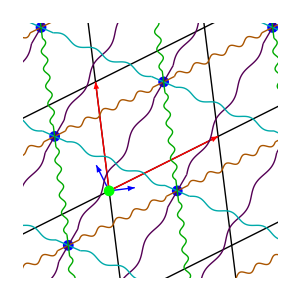

```mathematica
DynamicModule[{aLocDefault={2,1},aLoc={2.75,1.12},bLocDefault={-1/4,2},bLoc={0.27,1.2000000000000002},dynamics={{1.1498631557954957,2.3339707742856635},{{0.6847666025133172,{0.7007576661525571,0.7133993925764314}},{0.3375487318778744,{-0.7133993925764314,0.7007576661525571}}}},dynPlot=plotDynamics[locDependentCalc,dynamics,omegaIndex,#1,scale,aLoc,bLoc]&,k1=0.5,k2=0.5,k3=0.742,k4=0.25,lanceTestForceField=0.1,locDependentCalc={"aLoc"->{2.75,1.12},"bLoc"->{0.27,1.2000000000000002},"mLoc"->{0.7000000000000002,0.8200000000000003},"latticeBasis"->{{2.75,1.12},{0.27,1.2000000000000002}},"latticeNorms"->{2.9693265229677923,1.23},"latticeUnitVectors"->{{0.9261359364585545,0.3771899086667568},{0.21951219512195122,0.9756097560975611}},"numberLatticeLinesToDisplay"->{2,3},"reciprocalBasis"->{{0.400320256204964,-0.0900720576461169},{-0.3736322391246331,0.9174005871363757}},"reciprocalNorms"->{0.41032826261008803,0.9905679620255512},"mObliqueComponents"->{0.206365092073659,0.4907259140645851},"mPosFirstCell"->{0.7000000000000002,0.8200000000000003},"pointsDataTable"->{{{-5.61,-5.0200000000000005},{-5.34,-3.8200000000000003},{-5.069999999999999,-2.62},{-4.8,-1.42},{-4.53,-0.21999999999999975},{-4.26,0.9800000000000004},{-3.9899999999999993,2.1800000000000006}},{{-2.86,-3.9000000000000004},{-2.59,-2.7},{-2.32,-1.5},{-2.05,-0.2999999999999998},{-1.7799999999999998,0.9000000000000004},{-1.5099999999999998,2.1000000000000005},{-1.2399999999999998,3.3000000000000007}},{{-0.10999999999999988,-2.7800000000000002},{0.16000000000000014,-1.58},{0.43000000000000016,-0.3799999999999999},{0.7000000000000002,0.8200000000000003},{0.9700000000000002,2.0200000000000005},{1.2400000000000002,3.2200000000000006},{1.5100000000000002,4.420000000000001}},{{2.64,-1.6600000000000001},{2.91,-0.45999999999999996},{3.18,0.7400000000000002},{3.45,1.9400000000000004},{3.72,3.1400000000000006},{3.99,4.340000000000001},{4.26,5.540000000000001}},{{5.39,-0.54},{5.66,0.6600000000000001},{5.930000000000001,1.8600000000000003},{6.2,3.0600000000000005},{6.47,4.260000000000001},{6.74,5.460000000000001},{7.010000000000001,6.660000000000001}}},"lineTable"->{{Line[{{-6.3100000000000005,-5.840000000000001},{4.6899999999999995,-1.3600000000000003}}],Line[{{-6.04,-4.640000000000001},{4.96,-0.16000000000000014}}],Line[{{-5.77,-3.4400000000000004},{5.23,1.04}}],Line[{{-5.5,-2.24},{5.5,2.24}}],Line[{{-5.23,-1.04},{5.77,3.4400000000000004}}],Line[{{-4.96,0.16000000000000014},{6.04,4.640000000000001}}],Line[{{-4.6899999999999995,1.3600000000000003},{6.3100000000000005,5.840000000000001}}]},{Line[{{-6.3100000000000005,-5.840000000000001},{-4.6899999999999995,1.3600000000000003}}],Line[{{-3.56,-4.720000000000001},{-1.94,2.4800000000000004}}],Line[{{-0.81,-3.6000000000000005},{0.81,3.6000000000000005}}],Line[{{1.94,-2.4800000000000004},{3.56,4.720000000000001}}],Line[{{4.6899999999999995,-1.3600000000000003},{6.3100000000000005,5.840000000000001}}]}}},matrix=aM[#1,aLoc,bLoc,k1,k2,k3,k4,mass]&,meshSize=20,mLoc={0.7000000000000002,0.8200000000000003},omegaIndex=2,qLoc={0.44600000000000006,0.375},r=1,scale=0.1,springPlotH=Graphics[{{},{{{},{},{Hue[0.67,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.335000000000001,-4.908000000000001},{-5.318827904594239,-4.884730412826649},{-5.302085333281394,-4.862861547746579},{-5.284257652310908,-4.843657014415184},{-5.264936446025915,-4.828119619132799},{-5.243859495433338,-4.816893203177073},{-5.220936446025916,-4.810199619132799},{-5.196257652310908,-4.807817014415184},{-5.170085333281394,-4.809101547746579},{-5.142827904594238,-4.813050412826648},{-5.115000000000001,-4.8184000000000005},{-5.087172095405763,-4.823749587173353},{-5.0599146667186075,-4.827698452253422},{-5.033742347689095,-4.828982985584817},{-5.009063553974086,-4.826600380867202},{-4.986140504566664,-4.819906796822929},{-4.965063553974087,-4.808680380867202},{-4.9457423476890945,-4.793142985584817},{-4.927914666718609,-4.773938452253422},{-4.911172095405762,-4.752069587173352},{-4.8950000000000005,-4.7288},{-4.878827904594238,-4.705530412826648},{-4.862085333281394,-4.6836615477465795},{-4.844257652310907,-4.664457014415184},{-4.824936446025916,-4.6489196191327995},{-4.803859495433339,-4.637693203177073},{-4.780936446025915,-4.630999619132799},{-4.756257652310908,-4.628617014415184},{-4.730085333281394,-4.62990154774658},{-4.70282790459424,-4.633850412826648},{-4.675000000000002,-4.639200000000001},{-4.647172095405763,-4.644549587173353},{-4.619914666718607,-4.648498452253421},{-4.593742347689093,-4.649782985584817},{-4.569063553974086,-4.647400380867202},{-4.546140504566663,-4.640706796822927},{-4.5250635539740856,-4.629480380867202},{-4.505742347689093,-4.613942985584817},{-4.487914666718607,-4.594738452253422},{-4.471172095405764,-4.572869587173353},{-4.455000000000002,-4.549600000000001},{-4.438827904594238,-4.526330412826647},{-4.4220853332813945,-4.50446154774658},{-4.404257652310907,-4.4852570144151835},{-4.384936446025916,-4.4697196191328},{-4.3638594954333385,-4.458493203177072},{-4.340936446025916,-4.4517996191327995},{-4.316257652310908,-4.449417014415184},{-4.290085333281393,-4.450701547746579},{-4.262827904594239,-4.454650412826648},{-4.235000000000001,-4.460000000000001},{-4.207172095405763,-4.465349587173353},{-4.179914666718608,-4.469298452253422},{-4.153742347689095,-4.470582985584818},{-4.129063553974085,-4.468200380867201},{-4.106140504566662,-4.461506796822928},{-4.085063553974084,-4.450280380867202},{-4.065742347689092,-4.434742985584817},{-4.047914666718608,-4.415538452253421},{-4.031172095405763,-4.393669587173353},{-4.015000000000001,-4.3704},{-3.998827904594238,-4.3471304128266475},{-3.9820853332813932,-4.32526154774658},{-3.964257652310909,-4.306057014415185},{-3.944936446025917,-4.2905196191328},{-3.923859495433339,-4.2792932031770725},{-3.9009364460259164,-4.2725996191328},{-3.8762576523109082,-4.270217014415184},{-3.8500853332813936,-4.271501547746579},{-3.822827904594238,-4.275450412826648},{-3.795,-4.2808},{-3.767172095405762,-4.2861495871733535},{-3.739914666718608,-4.290098452253421},{-3.7137423476890934,-4.291382985584816},{-3.6890635539740853,-4.289000380867202},{-3.6661405045666626,-4.282306796822928},{-3.6450635539740865,-4.271080380867202},{-3.625742347689094,-4.2555429855848175},{-3.6079146667186066,-4.23633845225342},{-3.5911720954057618,-4.214469587173353},{-3.5749999999999993,-4.1912},{-3.5588279045942386,-4.167930412826648},{-3.5420853332813937,-4.14606154774658},{-3.524257652310908,-4.126857014415184},{-3.5049364460259156,-4.111319619132799},{-3.4838594954333377,-4.100093203177073},{-3.460936446025917,-4.0933996191328},{-3.4362576523109087,-4.0910170144151845},{-3.410085333281394,-4.09230154774658},{-3.3828279045942367,-4.096250412826647},{-3.355000000000002,-4.101600000000001},{-3.3271720954057624,-4.106949587173353},{-3.299914666718607,-4.110898452253421},{-3.273742347689092,-4.112182985584816},{-3.249063553974084,-4.109800380867202},{-3.226140504566663,-4.103106796822928},{-3.2050635539740853,-4.0918803808672015},{-3.185742347689093,-4.076342985584818},{-3.167914666718607,-4.0571384522534215},{-3.151172095405764,-4.035269587173353},{-3.1350000000000016,-4.0120000000000005}}]},{Hue[0.9060679774997897,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.1350000000000016,-4.0120000000000005},{-3.132250000000001,-4.01088},{-3.1295,-4.00976},{-3.1267499999999995,-4.00864},{-3.1240000000000006,-4.00752},{-3.1212500000000016,-4.006400000000001},{-3.118499999999999,-4.005280000000001},{-3.1157500000000002,-4.004160000000001},{-3.1130000000000013,-4.00304},{-3.1102500000000006,-4.00192},{-3.1075,-4.0008},{-3.104750000000001,-3.999680000000001},{-3.1020000000000003,-3.9985600000000003},{-3.0992500000000014,-3.9974400000000005},{-3.0965000000000007,-3.9963200000000003},{-3.09375,-3.9952000000000005},{-3.0909999999999993,-3.9940800000000003},{-3.0882500000000004,-3.9929600000000005},{-3.0855000000000015,-3.9918400000000007},{-3.0827500000000008,-3.99072},{-3.08,-3.9896000000000003},{-3.077250000000001,-3.988480000000001},{-3.0745000000000005,-3.9873600000000002},{-3.0717500000000015,-3.9862400000000004},{-3.069000000000001,-3.9851200000000007},{-3.06625,-3.9840000000000004},{-3.0635000000000012,-3.9828800000000006},{-3.0607500000000005,-3.9817600000000004},{-3.058,-3.9806400000000006},{-3.055249999999999,-3.97952},{-3.0525,-3.9784},{-3.0497500000000013,-3.977280000000001},{-3.0470000000000006,-3.97616},{-3.04425,-3.9750400000000004},{-3.041500000000001,-3.9739200000000006},{-3.0387500000000003,-3.9728000000000003},{-3.0360000000000014,-3.9716800000000005},{-3.0332500000000007,-3.9705600000000008},{-3.0305,-3.9694400000000005},{-3.027750000000001,-3.9683200000000007},{-3.0250000000000004,-3.9672},{-3.0222500000000014,-3.9660800000000007},{-3.019499999999999,-3.96496},{-3.01675,-3.9638400000000003},{-3.014000000000001,-3.9627200000000005},{-3.0112500000000004,-3.9616000000000002},{-3.0084999999999997,-3.9604800000000004},{-3.005750000000001,-3.9593600000000007},{-3.003,-3.9582400000000004},{-3.000250000000001,-3.9571200000000006},{-2.9975000000000023,-3.956000000000001},{-2.99475,-3.9548800000000006},{-2.992000000000001,-3.953760000000001},{-2.98925,-3.95264},{-2.9865000000000013,-3.9515200000000004},{-2.9837500000000006,-3.9504},{-2.981,-3.9492800000000003},{-2.978250000000001,-3.9481600000000006},{-2.9755000000000003,-3.9470400000000003},{-2.9727500000000013,-3.9459200000000005},{-2.9700000000000006,-3.9448000000000008},{-2.96725,-3.9436800000000005},{-2.964500000000001,-3.9425600000000007},{-2.961750000000002,-3.941440000000001},{-2.9589999999999996,-3.9403200000000003},{-2.9562500000000007,-3.9392000000000005},{-2.9535,-3.9380800000000002},{-2.950750000000001,-3.9369600000000005},{-2.9480000000000004,-3.9358400000000002},{-2.9452499999999997,-3.9347200000000004},{-2.942500000000001,-3.9336000000000007},{-2.93975,-3.9324800000000004},{-2.937000000000001,-3.9313600000000006},{-2.9342500000000005,-3.930240000000001},{-2.9314999999999998,-3.92912},{-2.928750000000001,-3.9280000000000004},{-2.926000000000002,-3.926880000000001},{-2.9232500000000012,-3.9257600000000004},{-2.9205000000000005,-3.9246400000000006},{-2.91775,-3.9235200000000003},{-2.915000000000001,-3.9224000000000006},{-2.9122500000000002,-3.9212800000000003},{-2.9094999999999995,-3.9201600000000005},{-2.9067500000000006,-3.9190400000000007},{-2.904,-3.91792},{-2.901250000000001,-3.9168000000000003},{-2.898500000000002,-3.915680000000001},{-2.8957499999999996,-3.9145600000000003},{-2.8930000000000007,-3.9134400000000005},{-2.8902500000000018,-3.9123200000000007},{-2.887500000000001,-3.9112000000000005},{-2.8847500000000004,-3.9100800000000007},{-2.8819999999999997,-3.9089600000000004},{-2.8792500000000008,-3.9078400000000006},{-2.8765,-3.90672},{-2.873750000000001,-3.9056},{-2.8710000000000004,-3.904480000000001},{-2.8682499999999997,-3.90336},{-2.865500000000001,-3.9022400000000004},{-2.862750000000002,-3.9011200000000006},{-2.8599999999999994,-3.9000000000000004}}]},{Hue[0.1421359549995791,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.610000000000001,-5.0200000000000005},{-5.6072500000000005,-5.018880000000001},{-5.604500000000001,-5.017760000000001},{-5.601750000000001,-5.016640000000001},{-5.599000000000001,-5.01552},{-5.596250000000001,-5.0144},{-5.593500000000001,-5.01328},{-5.590750000000002,-5.012160000000001},{-5.588000000000001,-5.011040000000001},{-5.585250000000001,-5.009920000000001},{-5.5825000000000005,-5.008800000000001},{-5.5797500000000015,-5.007680000000001},{-5.577000000000001,-5.00656},{-5.574250000000001,-5.00544},{-5.571500000000001,-5.00432},{-5.5687500000000005,-5.0032000000000005},{-5.566000000000002,-5.002080000000001},{-5.563250000000001,-5.000960000000001},{-5.560500000000001,-4.999840000000001},{-5.55775,-4.9987200000000005},{-5.5550000000000015,-4.9976},{-5.552250000000001,-4.99648},{-5.549500000000001,-4.995360000000001},{-5.546750000000001,-4.9942400000000005},{-5.5440000000000005,-4.99312},{-5.541250000000002,-4.992000000000001},{-5.538500000000001,-4.990880000000001},{-5.535750000000001,-4.98976},{-5.533,-4.98864},{-5.530250000000001,-4.987520000000001},{-5.527500000000001,-4.986400000000001},{-5.524750000000001,-4.98528},{-5.522000000000001,-4.984160000000001},{-5.519250000000001,-4.983040000000001},{-5.5165000000000015,-4.981920000000001},{-5.513750000000001,-4.9808},{-5.511000000000001,-4.97968},{-5.50825,-4.97856},{-5.505500000000001,-4.9774400000000005},{-5.502750000000001,-4.976320000000001},{-5.500000000000001,-4.975200000000001},{-5.497250000000001,-4.974080000000001},{-5.494500000000001,-4.9729600000000005},{-5.4917500000000015,-4.97184},{-5.489000000000001,-4.97072},{-5.486250000000001,-4.969600000000001},{-5.483500000000001,-4.968480000000001},{-5.480750000000001,-4.967360000000001},{-5.478000000000001,-4.966240000000001},{-5.475250000000001,-4.965120000000001},{-5.4725,-4.964},{-5.469750000000001,-4.96288},{-5.467000000000001,-4.96176},{-5.464250000000001,-4.960640000000001},{-5.461500000000001,-4.95952},{-5.458750000000001,-4.958400000000001},{-5.456000000000001,-4.957280000000001},{-5.453250000000001,-4.956160000000001},{-5.450500000000001,-4.95504},{-5.447750000000001,-4.95392},{-5.445000000000001,-4.952800000000001},{-5.442250000000001,-4.9516800000000005},{-5.439500000000001,-4.95056},{-5.436750000000001,-4.949440000000001},{-5.434000000000001,-4.948320000000001},{-5.431250000000001,-4.9472000000000005},{-5.4285000000000005,-4.94608},{-5.425750000000001,-4.94496},{-5.423000000000001,-4.943840000000001},{-5.420250000000001,-4.9427200000000004},{-5.417500000000001,-4.941600000000001},{-5.414750000000001,-4.940480000000001},{-5.412000000000002,-4.939360000000001},{-5.409250000000001,-4.93824},{-5.406500000000001,-4.93712},{-5.4037500000000005,-4.936},{-5.401000000000001,-4.934880000000001},{-5.398250000000001,-4.933760000000001},{-5.395500000000001,-4.932640000000001},{-5.392750000000001,-4.931520000000001},{-5.390000000000001,-4.930400000000001},{-5.387250000000002,-4.92928},{-5.384500000000001,-4.92816},{-5.381750000000001,-4.927040000000001},{-5.3790000000000004,-4.9259200000000005},{-5.3762500000000015,-4.924800000000001},{-5.373500000000001,-4.923680000000001},{-5.370750000000001,-4.922560000000001},{-5.368000000000001,-4.9214400000000005},{-5.3652500000000005,-4.92032},{-5.362500000000002,-4.919200000000001},{-5.359750000000001,-4.918080000000001},{-5.357000000000001,-4.91696},{-5.35425,-4.915840000000001},{-5.351500000000001,-4.914720000000001},{-5.348750000000001,-4.913600000000001},{-5.346000000000001,-4.91248},{-5.343250000000001,-4.91136},{-5.340500000000001,-4.910240000000001},{-5.3377500000000015,-4.909120000000001},{-5.335000000000001,-4.908000000000001}}]},{Hue[0.37820393249936934,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.0649999999999995,-3.7080000000000006},{-5.048827904594238,-3.684730412826648},{-5.032085333281393,-3.66286154774658},{-5.014257652310907,-3.6436570144151843},{-4.994936446025914,-3.628119619132799},{-4.973859495433338,-3.616893203177073},{-4.950936446025914,-3.6101996191327994},{-4.926257652310906,-3.607817014415184},{-4.900085333281393,-3.60910154774658},{-4.872827904594238,-3.6130504128266483},{-4.845,-3.6184000000000003},{-4.817172095405762,-3.623749587173353},{-4.789914666718607,-3.6276984522534215},{-4.763742347689093,-3.628982985584817},{-4.739063553974085,-3.626600380867202},{-4.7161405045666625,-3.6199067968229284},{-4.695063553974085,-3.6086803808672014},{-4.675742347689093,-3.593142985584817},{-4.657914666718606,-3.5739384522534214},{-4.6411720954057625,-3.552069587173353},{-4.625,-3.528800000000001},{-4.6088279045942375,-3.5055304128266482},{-4.592085333281393,-3.4836615477465798},{-4.574257652310906,-3.464457014415184},{-4.5549364460259145,-3.4489196191327993},{-4.5338594954333375,-3.437693203177073},{-4.510936446025915,-3.4309996191327996},{-4.486257652310907,-3.428617014415184},{-4.460085333281393,-3.4299015477465797},{-4.432827904594237,-3.433850412826648},{-4.404999999999999,-3.4392000000000005},{-4.377172095405762,-3.444549587173353},{-4.349914666718607,-3.4484984522534217},{-4.323742347689094,-3.449782985584817},{-4.299063553974086,-3.447400380867202},{-4.276140504566662,-3.440706796822928},{-4.255063553974085,-3.4294803808672016},{-4.235742347689093,-3.4139429855848173},{-4.217914666718607,-3.3947384522534216},{-4.201172095405762,-3.372869587173353},{-4.185,-3.3496000000000006},{-4.168827904594237,-3.326330412826648},{-4.152085333281393,-3.3044615477465795},{-4.1342576523109065,-3.2852570144151843},{-4.114936446025914,-3.2697196191327995},{-4.093859495433338,-3.258493203177073},{-4.0709364460259145,-3.2517996191327994},{-4.046257652310906,-3.249417014415184},{-4.0200853332813935,-3.25070154774658},{-3.9928279045942388,-3.2546504128266482},{-3.964999999999999,-3.2600000000000002},{-3.937172095405762,-3.2653495871733527},{-3.909914666718606,-3.2692984522534214},{-3.8837423476890924,-3.270582985584817},{-3.859063553974085,-3.2682003808672015},{-3.8361405045666617,-3.2615067968229283},{-3.8150635539740856,-3.250280380867202},{-3.7957423476890932,-3.234742985584817},{-3.7779146667186065,-3.215538452253422},{-3.7611720954057626,-3.1936695871733534},{-3.745,-3.1704000000000008},{-3.7288279045942385,-3.147130412826648},{-3.7120853332813937,-3.12526154774658},{-3.694257652310906,-3.1060570144151844},{-3.6749364460259137,-3.0905196191327993},{-3.6538594954333377,-3.079293203177073},{-3.630936446025914,-3.072599619132799},{-3.606257652310906,-3.070217014415184},{-3.580085333281393,-3.0715015477465797},{-3.5528279045942375,-3.075450412826648},{-3.5250000000000004,-3.080800000000001},{-3.4971720954057623,-3.0861495871733533},{-3.4699146667186076,-3.0900984522534216},{-3.443742347689094,-3.091382985584817},{-3.4190635539740857,-3.089000380867202},{-3.3961405045666613,-3.082306796822928},{-3.3750635539740834,-3.0710803808672016},{-3.355742347689091,-3.055542985584817},{-3.337914666718607,-3.0363384522534216},{-3.321172095405762,-3.014469587173353},{-3.3049999999999997,-2.9912000000000005},{-3.2888279045942372,-2.967930412826648},{-3.2720853332813924,-2.94606154774658},{-3.2542576523109084,-2.926857014415184},{-3.234936446025916,-2.9113196191327995},{-3.2138594954333364,-2.9000932031770725},{-3.1909364460259155,-2.8933996191327997},{-3.1662576523109074,-2.891017014415184},{-3.1400853332813927,-2.8923015477465794},{-3.112827904594237,-2.8962504128266477},{-3.084999999999999,-2.9016000000000006},{-3.057172095405761,-2.906949587173353},{-3.029914666718607,-2.9108984522534214},{-3.0037423476890925,-2.9121829855848174},{-2.9790635539740844,-2.909800380867202},{-2.9561405045666618,-2.9031067968229283},{-2.935063553974084,-2.891880380867202},{-2.9157423476890934,-2.8763429855848175},{-2.8979146667186058,-2.8571384522534213},{-2.8811720954057627,-2.8352695871733533},{-2.8649999999999984,-2.8120000000000003}}]},{Hue[0.6142719099991583,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.8649999999999984,-2.8120000000000003},{-2.8622499999999995,-2.8108800000000005},{-2.8595000000000006,-2.8097600000000007},{-2.85675,-2.8086400000000005},{-2.853999999999999,-2.8075200000000007},{-2.8512500000000003,-2.806400000000001},{-2.8484999999999996,-2.8052800000000007},{-2.8457500000000007,-2.804160000000001},{-2.8430000000000017,-2.803040000000001},{-2.8402499999999993,-2.801920000000001},{-2.8375000000000004,-2.800800000000001},{-2.8347499999999997,-2.7996800000000004},{-2.8320000000000007,-2.7985600000000006},{-2.8292499999999983,-2.7974400000000004},{-2.8264999999999993,-2.7963200000000006},{-2.8237500000000004,-2.795200000000001},{-2.8209999999999997,-2.7940800000000006},{-2.818250000000001,-2.7929600000000008},{-2.8155,-2.791840000000001},{-2.8127499999999994,-2.7907200000000008},{-2.8100000000000005,-2.789600000000001},{-2.8072500000000016,-2.788480000000001},{-2.804499999999999,-2.7873600000000005},{-2.80175,-2.7862400000000007},{-2.7989999999999995,-2.7851200000000005},{-2.7962500000000006,-2.7840000000000007},{-2.7935,-2.7828800000000005},{-2.790749999999999,-2.7817600000000007},{-2.7880000000000003,-2.780640000000001},{-2.7852499999999996,-2.7795200000000007},{-2.7825000000000006,-2.778400000000001},{-2.77975,-2.777280000000001},{-2.7769999999999992,-2.7761600000000004},{-2.7742500000000003,-2.7750400000000006},{-2.7715000000000014,-2.7739200000000013},{-2.7687500000000007,-2.7728000000000006},{-2.766,-2.771680000000001},{-2.7632499999999993,-2.7705600000000006},{-2.7605000000000004,-2.769440000000001},{-2.7577499999999997,-2.7683200000000006},{-2.754999999999999,-2.7672000000000008},{-2.75225,-2.766080000000001},{-2.7494999999999994,-2.7649600000000003},{-2.7467500000000005,-2.7638400000000005},{-2.7439999999999998,-2.762720000000001},{-2.741249999999999,-2.7616000000000005},{-2.7385,-2.7604800000000007},{-2.7357500000000012,-2.759360000000001},{-2.7330000000000005,-2.7582400000000007},{-2.730249999999998,-2.7571200000000005},{-2.727499999999999,-2.7560000000000007},{-2.7247500000000002,-2.754880000000001},{-2.7219999999999995,-2.75376},{-2.7192500000000006,-2.7526400000000004},{-2.7165,-2.751520000000001},{-2.713749999999999,-2.7504000000000004},{-2.7110000000000003,-2.7492800000000006},{-2.7082500000000014,-2.748160000000001},{-2.705499999999999,-2.7470400000000006},{-2.70275,-2.745920000000001},{-2.700000000000001,-2.744800000000001},{-2.6972500000000004,-2.743680000000001},{-2.6944999999999997,-2.74256},{-2.691749999999999,-2.7414400000000003},{-2.689,-2.740320000000001},{-2.6862499999999994,-2.7392000000000003},{-2.6835000000000004,-2.7380800000000005},{-2.6807499999999997,-2.7369600000000007},{-2.677999999999999,-2.7358400000000005},{-2.67525,-2.7347200000000007},{-2.672500000000001,-2.733600000000001},{-2.6697500000000005,-2.7324800000000007},{-2.667,-2.731360000000001},{-2.664250000000001,-2.730240000000001},{-2.6615,-2.729120000000001},{-2.6587499999999995,-2.728},{-2.655999999999999,-2.7268800000000004},{-2.65325,-2.7257600000000006},{-2.650499999999999,-2.7246400000000004},{-2.6477500000000003,-2.7235200000000006},{-2.6449999999999996,-2.722400000000001},{-2.642249999999999,-2.7212800000000006},{-2.6395,-2.720160000000001},{-2.636750000000001,-2.719040000000001},{-2.6340000000000003,-2.717920000000001},{-2.6312499999999996,-2.716800000000001},{-2.6285000000000007,-2.715680000000001},{-2.62575,-2.7145600000000005},{-2.6229999999999993,-2.7134400000000003},{-2.6202500000000004,-2.7123200000000005},{-2.6174999999999997,-2.7112000000000007},{-2.614749999999999,-2.7100800000000005},{-2.612,-2.7089600000000007},{-2.609250000000001,-2.707840000000001},{-2.6064999999999987,-2.7067200000000007},{-2.60375,-2.705600000000001},{-2.601000000000001,-2.704480000000001},{-2.59825,-2.7033600000000004},{-2.5954999999999995,-2.7022400000000006},{-2.5927500000000006,-2.7011200000000013},{-2.59,-2.7000000000000006}}]},{Hue[0.8503398874989481,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.34,-3.8200000000000007},{-5.33725,-3.8188800000000005},{-5.334499999999999,-3.8177600000000003},{-5.33175,-3.8166400000000005},{-5.329,-3.8155200000000007},{-5.32625,-3.8144000000000005},{-5.323499999999999,-3.8132800000000007},{-5.32075,-3.812160000000001},{-5.318,-3.8110400000000006},{-5.31525,-3.8099200000000004},{-5.3125,-3.8088000000000006},{-5.30975,-3.807680000000001},{-5.307,-3.8065600000000006},{-5.30425,-3.8054400000000004},{-5.3015,-3.8043200000000006},{-5.298749999999999,-3.8032000000000004},{-5.296,-3.8020800000000006},{-5.29325,-3.800960000000001},{-5.2905,-3.7998400000000006},{-5.28775,-3.7987200000000003},{-5.285,-3.7976000000000005},{-5.28225,-3.7964800000000007},{-5.2795,-3.7953600000000005},{-5.27675,-3.7942400000000003},{-5.274,-3.793120000000001},{-5.27125,-3.7920000000000007},{-5.2684999999999995,-3.7908800000000005},{-5.26575,-3.7897600000000007},{-5.263,-3.7886400000000005},{-5.26025,-3.7875200000000007},{-5.2575,-3.7864000000000004},{-5.25475,-3.7852800000000006},{-5.252,-3.7841600000000004},{-5.24925,-3.7830400000000006},{-5.2465,-3.781920000000001},{-5.2437499999999995,-3.7808000000000006},{-5.241,-3.7796800000000004},{-5.23825,-3.7785600000000006},{-5.2355,-3.777440000000001},{-5.23275,-3.7763200000000006},{-5.2299999999999995,-3.7752000000000003},{-5.22725,-3.7740800000000005},{-5.2245,-3.7729600000000008},{-5.22175,-3.7718400000000005},{-5.218999999999999,-3.7707200000000007},{-5.21625,-3.7696000000000005},{-5.2135,-3.7684800000000007},{-5.21075,-3.7673600000000005},{-5.208,-3.7662400000000007},{-5.2052499999999995,-3.7651200000000005},{-5.202500000000001,-3.7640000000000007},{-5.19975,-3.762880000000001},{-5.197,-3.7617600000000007},{-5.194249999999999,-3.7606400000000004},{-5.1915,-3.7595200000000006},{-5.18875,-3.758400000000001},{-5.186,-3.7572800000000006},{-5.18325,-3.7561600000000004},{-5.180499999999999,-3.7550400000000006},{-5.1777500000000005,-3.753920000000001},{-5.175,-3.7528000000000006},{-5.17225,-3.751680000000001},{-5.169499999999999,-3.7505600000000006},{-5.16675,-3.7494400000000008},{-5.164,-3.7483200000000005},{-5.16125,-3.7472000000000008},{-5.1585,-3.7460800000000005},{-5.155749999999999,-3.7449600000000003},{-5.1530000000000005,-3.7438400000000005},{-5.15025,-3.7427200000000007},{-5.1475,-3.7416000000000005},{-5.144749999999999,-3.7404800000000007},{-5.142,-3.739360000000001},{-5.13925,-3.7382400000000007},{-5.1365,-3.7371200000000004},{-5.13375,-3.7360000000000007},{-5.130999999999999,-3.7348800000000004},{-5.12825,-3.7337600000000006},{-5.1255,-3.7326400000000004},{-5.12275,-3.7315200000000006},{-5.119999999999999,-3.7304000000000004},{-5.11725,-3.7292800000000006},{-5.1145,-3.728160000000001},{-5.11175,-3.7270400000000006},{-5.109,-3.7259200000000003},{-5.106249999999999,-3.7248000000000006},{-5.1035,-3.7236800000000008},{-5.10075,-3.7225600000000005},{-5.098,-3.7214400000000003},{-5.095249999999999,-3.7203200000000005},{-5.0925,-3.7192000000000007},{-5.0897499999999996,-3.7180800000000005},{-5.087,-3.7169600000000007},{-5.08425,-3.7158400000000005},{-5.0815,-3.7147200000000007},{-5.07875,-3.7136000000000005},{-5.076,-3.7124800000000007},{-5.07325,-3.7113600000000004},{-5.070499999999999,-3.71024},{-5.06775,-3.709120000000001},{-5.0649999999999995,-3.7080000000000006}}]},{Hue[0.08640786499873876,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.794999999999999,-2.5079999999999996},{-4.7788279045942375,-2.484730412826647},{-4.762085333281393,-2.4628615477465785},{-4.744257652310907,-2.4436570144151832},{-4.724936446025914,-2.428119619132798},{-4.7038594954333375,-2.4168932031770716},{-4.680936446025914,-2.4101996191327983},{-4.656257652310906,-2.407817014415183},{-4.630085333281393,-2.4091015477465785},{-4.602827904594237,-2.4130504128266472},{-4.574999999999999,-2.418399999999999},{-4.547172095405761,-2.4237495871733516},{-4.5199146667186065,-2.4276984522534204},{-4.493742347689093,-2.428982985584816},{-4.469063553974085,-2.4266003808672005},{-4.446140504566662,-2.4199067968229273},{-4.425063553974084,-2.4086803808672004},{-4.405742347689093,-2.393142985584816},{-4.387914666718606,-2.3739384522534204},{-4.371172095405762,-2.352069587173352},{-4.3549999999999995,-2.3287999999999993},{-4.338827904594237,-2.305530412826647},{-4.322085333281393,-2.2836615477465787},{-4.3042576523109055,-2.264457014415183},{-4.284936446025914,-2.2489196191327983},{-4.263859495433337,-2.2376932031770718},{-4.2409364460259145,-2.230999619132798},{-4.216257652310906,-2.228617014415183},{-4.1900853332813925,-2.2299015477465782},{-4.162827904594237,-2.233850412826647},{-4.134999999999999,-2.2391999999999994},{-4.107172095405762,-2.244549587173352},{-4.079914666718606,-2.24849845225342},{-4.053742347689093,-2.249782985584816},{-4.029063553974085,-2.2474003808672007},{-4.0061405045666625,-2.240706796822927},{-3.9850635539740855,-2.229480380867201},{-3.9657423476890923,-2.213942985584816},{-3.9479146667186065,-2.19473845225342},{-3.9311720954057616,-2.172869587173352},{-3.914999999999999,-2.149599999999999},{-3.8988279045942367,-2.126330412826647},{-3.8820853332813927,-2.1044615477465785},{-3.864257652310906,-2.0852570144151827},{-3.8449364460259137,-2.069719619132798},{-3.8238594954333376,-2.058493203177072},{-3.800936446025914,-2.0517996191327983},{-3.776257652310907,-2.049417014415183},{-3.750085333281393,-2.050701547746579},{-3.7228279045942374,-2.0546504128266467},{-3.6949999999999994,-2.059999999999999},{-3.6671720954057623,-2.065349587173352},{-3.6399146667186066,-2.0692984522534204},{-3.613742347689092,-2.070582985584816},{-3.5890635539740847,-2.0682003808672005},{-3.566140504566661,-2.061506796822927},{-3.545063553974085,-2.0502803808672003},{-3.525742347689093,-2.034742985584816},{-3.507914666718607,-2.0155384522534203},{-3.491172095405762,-1.9936695871733519},{-3.4749999999999996,-1.9703999999999997},{-3.458827904594238,-1.9471304128266471},{-3.4420853332813923,-1.9252615477465782},{-3.4242576523109065,-1.9060570144151834},{-3.404936446025914,-1.8905196191327982},{-3.383859495433338,-1.8792932031770717},{-3.3609364460259137,-1.872599619132798},{-3.3362576523109064,-1.8702170144151826},{-3.3100853332813926,-1.8715015477465782},{-3.282827904594237,-1.875450412826647},{-3.255,-1.8807999999999994},{-3.227172095405762,-1.8861495871733518},{-3.199914666718607,-1.8900984522534205},{-3.1737423476890934,-1.8913829855848157},{-3.149063553974085,-1.8890003808672007},{-3.1261405045666617,-1.882306796822927},{-3.1050635539740847,-1.8710803808672005},{-3.0857423476890933,-1.8555429855848158},{-3.0679146667186057,-1.83633845225342},{-3.0511720954057617,-1.8144695871733516},{-3.0349999999999993,-1.7911999999999995},{-3.0188279045942377,-1.7679304128266469},{-3.002085333281393,-1.7460615477465784},{-2.984257652310906,-1.7268570144151827},{-2.9649364460259147,-1.7113196191327984},{-2.9438594954333377,-1.700093203177072},{-2.920936446025915,-1.6933996191327982},{-2.896257652310907,-1.6910170144151833},{-2.8700853332813923,-1.692301547746578},{-2.8428279045942384,-1.6962504128266471},{-2.8149999999999995,-1.7015999999999991},{-2.7871720954057615,-1.7069495871733515},{-2.759914666718606,-1.7108984522534203},{-2.733742347689093,-1.7121829855848159},{-2.709063553974085,-1.7098003808672004},{-2.686140504566662,-1.7031067968229268},{-2.6650635539740852,-1.6918803808672007},{-2.6457423476890938,-1.676342985584816},{-2.627914666718607,-1.6571384522534203},{-2.6111720954057622,-1.6352695871733522},{-2.5950000000000006,-1.6119999999999997}}]},{Hue[0.3224758424985268,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.5950000000000006,-1.6119999999999997},{-2.592249999999999,-1.610879999999999},{-2.5895,-1.6097599999999996},{-2.5867500000000003,-1.6086399999999998},{-2.5839999999999996,-1.6075199999999992},{-2.5812500000000007,-1.6063999999999994},{-2.578500000000001,-1.6052799999999996},{-2.57575,-1.6041599999999994},{-2.5730000000000004,-1.6030399999999996},{-2.5702499999999997,-1.6019199999999993},{-2.5675,-1.6007999999999996},{-2.564749999999999,-1.5996799999999989},{-2.5620000000000003,-1.5985599999999995},{-2.5592500000000005,-1.5974399999999997},{-2.5564999999999998,-1.596319999999999},{-2.55375,-1.5951999999999993},{-2.551000000000001,-1.5940799999999995},{-2.5482499999999995,-1.5929599999999993},{-2.5455000000000005,-1.5918399999999995},{-2.5427500000000007,-1.5907199999999997},{-2.54,-1.5895999999999995},{-2.5372500000000002,-1.5884799999999997},{-2.5344999999999995,-1.5873599999999994},{-2.5317500000000006,-1.5862399999999997},{-2.528999999999999,-1.585119999999999},{-2.52625,-1.5839999999999992},{-2.5235000000000003,-1.5828799999999994},{-2.5207499999999996,-1.5817599999999992},{-2.518,-1.5806399999999994},{-2.515250000000001,-1.5795199999999996},{-2.5124999999999993,-1.5783999999999994},{-2.5097500000000004,-1.5772799999999996},{-2.5070000000000006,-1.5761599999999998},{-2.50425,-1.5750399999999996},{-2.501500000000001,-1.5739199999999998},{-2.4987499999999994,-1.572799999999999},{-2.4960000000000004,-1.5716799999999993},{-2.493249999999999,-1.570559999999999},{-2.4905,-1.5694399999999993},{-2.48775,-1.5683199999999995},{-2.4849999999999994,-1.5671999999999993},{-2.4822500000000005,-1.5660799999999995},{-2.4795000000000007,-1.5649599999999997},{-2.47675,-1.5638399999999995},{-2.474,-1.5627199999999997},{-2.4712500000000013,-1.5615999999999999},{-2.4684999999999997,-1.5604799999999992},{-2.4657500000000008,-1.5593599999999999},{-2.462999999999999,-1.5582399999999992},{-2.4602500000000003,-1.5571199999999994},{-2.4574999999999996,-1.5559999999999992},{-2.4547499999999998,-1.5548799999999994},{-2.452000000000001,-1.5537599999999996},{-2.4492499999999993,-1.5526399999999994},{-2.4465000000000003,-1.5515199999999996},{-2.4437500000000005,-1.5503999999999998},{-2.441,-1.549279999999999},{-2.43825,-1.5481599999999998},{-2.435500000000001,-1.54704},{-2.4327500000000004,-1.5459199999999993},{-2.4300000000000006,-1.5447999999999995},{-2.42725,-1.5436799999999993},{-2.4245,-1.5425599999999995},{-2.4217499999999994,-1.5414399999999993},{-2.4189999999999996,-1.5403199999999995},{-2.4162500000000007,-1.5391999999999997},{-2.413499999999999,-1.538079999999999},{-2.41075,-1.5369599999999997},{-2.4080000000000004,-1.5358399999999999},{-2.4052499999999997,-1.5347199999999992},{-2.4025000000000007,-1.5335999999999994},{-2.399750000000001,-1.5324799999999996},{-2.3970000000000002,-1.5313599999999994},{-2.3942500000000004,-1.5302399999999996},{-2.3914999999999997,-1.5291199999999994},{-2.38875,-1.5279999999999996},{-2.3859999999999992,-1.526879999999999},{-2.3832500000000003,-1.5257599999999996},{-2.3805000000000005,-1.5246399999999998},{-2.37775,-1.523519999999999},{-2.375,-1.5223999999999993},{-2.372250000000001,-1.5212799999999995},{-2.3694999999999995,-1.5201599999999993},{-2.3667500000000006,-1.5190399999999995},{-2.3640000000000008,-1.5179199999999997},{-2.36125,-1.5167999999999995},{-2.3585000000000003,-1.5156799999999997},{-2.3557499999999996,-1.5145599999999995},{-2.3529999999999998,-1.5134399999999997},{-2.350249999999999,-1.512319999999999},{-2.3475,-1.5111999999999992},{-2.3447500000000012,-1.5100799999999994},{-2.3419999999999987,-1.5089599999999992},{-2.33925,-1.5078399999999994},{-2.336500000000001,-1.5067199999999996},{-2.33375,-1.5055999999999994},{-2.3310000000000013,-1.5044799999999996},{-2.3282500000000006,-1.5033599999999998},{-2.3255,-1.5022399999999996},{-2.322750000000001,-1.5011199999999998},{-2.3200000000000003,-1.4999999999999991}}]},{Hue[0.5585438199983166,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.069999999999999,-2.6199999999999997},{-5.067249999999999,-2.6188799999999994},{-5.064499999999999,-2.617759999999999},{-5.06175,-2.6166399999999994},{-5.058999999999999,-2.6155199999999996},{-5.0562499999999995,-2.6143999999999994},{-5.053499999999999,-2.613279999999999},{-5.05075,-2.61216},{-5.047999999999999,-2.6110399999999996},{-5.045249999999999,-2.6099199999999994},{-5.042499999999999,-2.6087999999999996},{-5.03975,-2.6076799999999998},{-5.037,-2.6065599999999995},{-5.034249999999999,-2.6054399999999993},{-5.031499999999999,-2.6043199999999995},{-5.028749999999999,-2.6031999999999993},{-5.026,-2.6020799999999995},{-5.023249999999999,-2.6009599999999997},{-5.020499999999999,-2.5998399999999995},{-5.017749999999999,-2.5987199999999993},{-5.015,-2.5975999999999995},{-5.012249999999999,-2.5964799999999997},{-5.009499999999999,-2.5953599999999994},{-5.006749999999999,-2.594239999999999},{-5.004,-2.5931199999999994},{-5.00125,-2.5919999999999996},{-4.998499999999999,-2.5908799999999994},{-4.995749999999999,-2.5897599999999996},{-4.9929999999999986,-2.5886399999999994},{-4.99025,-2.5875199999999996},{-4.987499999999999,-2.5863999999999994},{-4.984749999999999,-2.5852799999999996},{-4.981999999999999,-2.5841599999999993},{-4.9792499999999995,-2.5830399999999996},{-4.9765,-2.5819199999999993},{-4.973749999999999,-2.5807999999999995},{-4.970999999999999,-2.5796799999999993},{-4.968249999999999,-2.5785599999999995},{-4.9655,-2.5774399999999997},{-4.962749999999999,-2.5763199999999995},{-4.959999999999999,-2.5751999999999993},{-4.957249999999999,-2.5740799999999995},{-4.9544999999999995,-2.5729599999999997},{-4.95175,-2.5718399999999995},{-4.948999999999999,-2.5707199999999992},{-4.946249999999999,-2.5695999999999994},{-4.943499999999999,-2.5684799999999997},{-4.9407499999999995,-2.5673599999999994},{-4.937999999999999,-2.5662399999999996},{-4.935249999999999,-2.5651199999999994},{-4.9325,-2.5639999999999996},{-4.929749999999999,-2.5628799999999994},{-4.927,-2.5617599999999996},{-4.924249999999999,-2.5606399999999994},{-4.921499999999999,-2.559519999999999},{-4.918749999999999,-2.5584},{-4.9159999999999995,-2.5572799999999996},{-4.913249999999999,-2.5561599999999993},{-4.910499999999999,-2.5550399999999995},{-4.90775,-2.5539199999999997},{-4.904999999999999,-2.5527999999999995},{-4.9022499999999996,-2.5516799999999993},{-4.899499999999999,-2.5505599999999995},{-4.89675,-2.5494399999999997},{-4.893999999999999,-2.5483199999999995},{-4.891249999999999,-2.5471999999999997},{-4.888499999999999,-2.5460799999999995},{-4.885749999999999,-2.5449599999999992},{-4.883,-2.5438399999999994},{-4.880249999999999,-2.5427199999999996},{-4.8774999999999995,-2.5415999999999994},{-4.874749999999999,-2.540479999999999},{-4.872,-2.5393599999999994},{-4.869249999999999,-2.5382399999999996},{-4.866499999999999,-2.5371199999999994},{-4.863749999999999,-2.5359999999999996},{-4.860999999999999,-2.5348799999999994},{-4.85825,-2.5337599999999996},{-4.855499999999999,-2.5326399999999993},{-4.8527499999999995,-2.5315199999999995},{-4.849999999999999,-2.5303999999999993},{-4.84725,-2.5292799999999995},{-4.844499999999999,-2.5281599999999993},{-4.841749999999999,-2.5270399999999995},{-4.838999999999999,-2.5259199999999993},{-4.83625,-2.5247999999999995},{-4.8335,-2.5236799999999997},{-4.830749999999999,-2.5225599999999995},{-4.827999999999999,-2.5214399999999992},{-4.82525,-2.5203199999999994},{-4.8225,-2.5191999999999997},{-4.819749999999999,-2.5180799999999994},{-4.816999999999999,-2.516959999999999},{-4.814249999999999,-2.5158399999999994},{-4.8115,-2.5147199999999996},{-4.80875,-2.5135999999999994},{-4.805999999999999,-2.5124799999999996},{-4.803249999999999,-2.5113599999999994},{-4.8004999999999995,-2.5102399999999996},{-4.79775,-2.5091199999999994},{-4.794999999999999,-2.5079999999999996}}]},{Hue[0.7946117974981064,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.5249999999999995,-1.3080000000000003},{-4.508827904594237,-1.2847304128266477},{-4.492085333281393,-1.2628615477465792},{-4.474257652310906,-1.2436570144151835},{-4.454936446025914,-1.2281196191327988},{-4.433859495433337,-1.2168932031770723},{-4.4109364460259135,-1.210199619132799},{-4.386257652310906,-1.2078170144151836},{-4.3600853332813925,-1.2091015477465792},{-4.332827904594238,-1.2130504128266475},{-4.304999999999999,-1.2184},{-4.277172095405762,-1.2237495871733524},{-4.249914666718606,-1.2276984522534211},{-4.223742347689092,-1.2289829855848167},{-4.199063553974085,-1.2266003808672012},{-4.1761405045666615,-1.219906796822928},{-4.1550635539740846,-1.208680380867201},{-4.135742347689092,-1.1931429855848164},{-4.117914666718606,-1.173938452253421},{-4.1011720954057616,-1.1520695871733526},{-4.084999999999999,-1.1288},{-4.0688279045942375,-1.1055304128266479},{-4.052085333281392,-1.083661547746579},{-4.034257652310906,-1.0644570144151833},{-4.014936446025914,-1.048919619132799},{-3.9938594954333375,-1.0376932031770725},{-3.970936446025914,-1.0309996191327988},{-3.9462576523109067,-1.0286170144151838},{-3.920085333281392,-1.029901547746579},{-3.8928279045942364,-1.0338504128266472},{-3.8649999999999993,-1.0392000000000001},{-3.8371720954057613,-1.0445495871733526},{-3.8099146667186066,-1.0484984522534209},{-3.783742347689093,-1.0497829855848169},{-3.7590635539740846,-1.047400380867201},{-3.736140504566661,-1.0407067968229278},{-3.715063553974084,-1.0294803808672013},{-3.6957423476890927,-1.0139429855848165},{-3.677914666718606,-0.9947384522534208},{-3.661172095405762,-0.9728695871733528},{-3.6449999999999987,-0.9495999999999998},{-3.628827904594237,-0.9263304128266476},{-3.6120853332813923,-0.9044615477465792},{-3.5942576523109055,-0.8852570144151835},{-3.574936446025914,-0.8697196191327987},{-3.553859495433337,-0.8584932031770727},{-3.5309364460259136,-0.8517996191327986},{-3.5062576523109055,-0.8494170144151836},{-3.4800853332813926,-0.8507015477465791},{-3.452827904594237,-0.8546504128266474},{-3.424999999999999,-0.8600000000000003},{-3.397172095405762,-0.8653495871733528},{-3.369914666718606,-0.8692984522534211},{-3.3437423476890924,-0.8705829855848166},{-3.3190635539740843,-0.8682003808672012},{-3.2961405045666616,-0.8615067968229275},{-3.2750635539740847,-0.8502803808672015},{-3.255742347689093,-0.8347429855848167},{-3.2379146667186065,-0.815538452253421},{-3.2211720954057617,-0.7936695871733526},{-3.204999999999999,-0.7704},{-3.1888279045942367,-0.7471304128266474},{-3.1720853332813927,-0.7252615477465794},{-3.154257652310906,-0.7060570144151841},{-3.1349364460259146,-0.6905196191327989},{-3.1138594954333376,-0.6792932031770729},{-3.090936446025913,-0.6725996191327988},{-3.066257652310906,-0.6702170144151833},{-3.040085333281392,-0.6715015477465793},{-3.0128279045942374,-0.6754504128266476},{-2.9849999999999985,-0.6808000000000001},{-2.9571720954057623,-0.686149587173353},{-2.9299146667186067,-0.6900984522534213},{-2.903742347689092,-0.6913829855848159},{-2.8790635539740848,-0.6890003808672014},{-2.8561405045666612,-0.6823067968229277},{-2.835063553974085,-0.6710803808672012},{-2.815742347689092,-0.6555429855848165},{-2.797914666718606,-0.6363384522534208},{-2.7811720954057613,-0.6144695871733523},{-2.764999999999999,-0.5912000000000002},{-2.7488279045942363,-0.5679304128266471},{-2.7320853332813915,-0.5460615477465791},{-2.7142576523109057,-0.5268570144151834},{-2.6949364460259133,-0.5113196191327987},{-2.6738594954333372,-0.5000932031770726},{-2.6509364460259137,-0.49339961913279895},{-2.6262576523109065,-0.49101701441518353},{-2.6000853332813927,-0.4923015477465791},{-2.572827904594237,-0.49625041282664784},{-2.545,-0.5016000000000003},{-2.517172095405761,-0.5069495871733527},{-2.4899146667186063,-0.510898452253421},{-2.4637423476890925,-0.5121829855848166},{-2.4390635539740844,-0.5098003808672011},{-2.416140504566661,-0.5031067968229275},{-2.395063553974084,-0.491880380867201},{-2.3757423476890924,-0.4763429855848167},{-2.3579146667186057,-0.457138452253421},{-2.3411720954057618,-0.4352695871733525},{-2.3249999999999993,-0.41200000000000037}}]},{Hue[0.030679774997896203,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.3249999999999993,-0.41200000000000037},{-2.3222499999999995,-0.41088000000000013},{-2.319499999999999,-0.4097599999999999},{-2.31675,-0.4086400000000001},{-2.313999999999999,-0.4075200000000003},{-2.3112499999999994,-0.4064000000000001},{-2.3084999999999996,-0.4052800000000003},{-2.305749999999999,-0.4041600000000001},{-2.303,-0.4030400000000003},{-2.3002499999999992,-0.40192000000000005},{-2.2974999999999994,-0.40080000000000027},{-2.2947499999999996,-0.3996800000000005},{-2.292,-0.39856000000000025},{-2.289249999999999,-0.39744},{-2.2864999999999993,-0.3963200000000002},{-2.2837499999999986,-0.3952},{-2.2809999999999997,-0.3940800000000002},{-2.27825,-0.39296},{-2.275499999999999,-0.3918400000000002},{-2.2727500000000003,-0.3907200000000004},{-2.2699999999999987,-0.38960000000000017},{-2.2672499999999998,-0.3884800000000004},{-2.264499999999999,-0.38736000000000015},{-2.2617499999999993,-0.3862399999999999},{-2.2589999999999995,-0.38512000000000013},{-2.2562499999999996,-0.38400000000000034},{-2.2535,-0.3828800000000001},{-2.250749999999999,-0.3817599999999999},{-2.2479999999999993,-0.3806400000000001},{-2.2452499999999995,-0.3795200000000003},{-2.2424999999999997,-0.37840000000000007},{-2.239749999999999,-0.3772800000000003},{-2.237,-0.3761600000000005},{-2.2342499999999985,-0.3750399999999998},{-2.2314999999999996,-0.37392000000000003},{-2.22875,-0.37280000000000024},{-2.225999999999999,-0.37168},{-2.22325,-0.3705600000000002},{-2.2204999999999986,-0.36944},{-2.2177499999999997,-0.3683200000000002},{-2.214999999999999,-0.36719999999999997},{-2.212249999999999,-0.3660800000000002},{-2.2094999999999994,-0.3649600000000004},{-2.2067499999999995,-0.36384000000000016},{-2.2039999999999997,-0.36271999999999993},{-2.20125,-0.3616000000000006},{-2.1984999999999992,-0.3604799999999999},{-2.1957499999999994,-0.3593600000000001},{-2.1929999999999996,-0.35824000000000034},{-2.190249999999999,-0.3571200000000001},{-2.1875,-0.3560000000000003},{-2.1847499999999984,-0.3548800000000001},{-2.1819999999999995,-0.3537600000000003},{-2.179249999999999,-0.35264000000000006},{-2.176499999999999,-0.35151999999999983},{-2.17375,-0.3504000000000005},{-2.1709999999999994,-0.34928000000000026},{-2.1682499999999996,-0.34816},{-2.1654999999999998,-0.34704000000000024},{-2.162749999999999,-0.34592},{-2.1599999999999993,-0.3448000000000002},{-2.1572499999999994,-0.34368},{-2.1544999999999987,-0.3425600000000002},{-2.15175,-0.3414400000000004},{-2.148999999999999,-0.34031999999999973},{-2.1462499999999993,-0.3392000000000004},{-2.1434999999999995,-0.33808000000000016},{-2.140749999999999,-0.3369599999999999},{-2.138,-0.33584000000000014},{-2.135249999999999,-0.33472000000000035},{-2.1324999999999994,-0.3336000000000001},{-2.1297499999999996,-0.33248000000000033},{-2.126999999999999,-0.3313600000000001},{-2.12425,-0.3302400000000003},{-2.1214999999999993,-0.3291200000000001},{-2.1187499999999995,-0.3280000000000003},{-2.1159999999999997,-0.3268800000000005},{-2.113249999999999,-0.3257599999999998},{-2.110499999999999,-0.32464000000000004},{-2.1077499999999993,-0.32352000000000025},{-2.1049999999999986,-0.3224},{-2.1022499999999997,-0.32128000000000023},{-2.0995,-0.32016},{-2.0967499999999992,-0.3190400000000002},{-2.0940000000000003,-0.3179200000000004},{-2.0912499999999987,-0.3168000000000002},{-2.0885,-0.3156800000000004},{-2.085749999999999,-0.3145600000000002},{-2.0829999999999993,-0.31343999999999994},{-2.0802499999999995,-0.31232000000000015},{-2.077499999999999,-0.3111999999999999},{-2.07475,-0.31008000000000013},{-2.071999999999999,-0.3089599999999999},{-2.0692499999999994,-0.3078400000000001},{-2.0664999999999996,-0.3067200000000003},{-2.0637499999999998,-0.3056000000000001},{-2.060999999999999,-0.3044800000000003},{-2.05825,-0.3033600000000005},{-2.0554999999999986,-0.30223999999999984},{-2.0527499999999996,-0.30112000000000005},{-2.05,-0.30000000000000027}}]},{Hue[0.266747752497686,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.799999999999999,-1.4200000000000002},{-4.797249999999999,-1.41888},{-4.794499999999999,-1.41776},{-4.7917499999999995,-1.4166400000000001},{-4.789,-1.4155200000000001},{-4.786249999999999,-1.4144},{-4.783499999999999,-1.4132799999999999},{-4.780749999999999,-1.41216},{-4.778,-1.41104},{-4.775249999999999,-1.40992},{-4.772499999999999,-1.4088},{-4.76975,-1.4076800000000003},{-4.7669999999999995,-1.40656},{-4.76425,-1.40544},{-4.761499999999999,-1.40432},{-4.758749999999999,-1.4032},{-4.755999999999999,-1.4020800000000002},{-4.7532499999999995,-1.40096},{-4.750499999999999,-1.39984},{-4.747749999999999,-1.39872},{-4.745,-1.3976000000000002},{-4.742249999999999,-1.3964800000000002},{-4.7395,-1.39536},{-4.736749999999999,-1.39424},{-4.734,-1.3931200000000001},{-4.731249999999999,-1.3920000000000001},{-4.7284999999999995,-1.3908800000000001},{-4.725749999999999,-1.3897599999999999},{-4.722999999999999,-1.3886399999999999},{-4.720249999999999,-1.38752},{-4.717499999999999,-1.3864},{-4.7147499999999996,-1.38528},{-4.711999999999999,-1.3841599999999998},{-4.70925,-1.3830400000000003},{-4.706499999999999,-1.38192},{-4.703749999999999,-1.3808},{-4.700999999999999,-1.37968},{-4.69825,-1.3785600000000002},{-4.695499999999999,-1.3774400000000002},{-4.692749999999999,-1.37632},{-4.6899999999999995,-1.3752},{-4.687249999999999,-1.37408},{-4.6845,-1.3729600000000002},{-4.681749999999999,-1.3718400000000002},{-4.678999999999999,-1.37072},{-4.676249999999999,-1.3696},{-4.6735,-1.3684800000000001},{-4.670749999999999,-1.3673600000000001},{-4.667999999999999,-1.3662400000000001},{-4.6652499999999995,-1.36512},{-4.662499999999999,-1.3639999999999999},{-4.65975,-1.36288},{-4.656999999999999,-1.36176},{-4.654249999999999,-1.36064},{-4.651499999999999,-1.3595199999999998},{-4.64875,-1.3584000000000003},{-4.645999999999999,-1.35728},{-4.643249999999999,-1.35616},{-4.640499999999999,-1.35504},{-4.63775,-1.3539200000000002},{-4.635,-1.3528000000000002},{-4.632249999999999,-1.35168},{-4.629499999999999,-1.35056},{-4.626749999999999,-1.34944},{-4.624,-1.3483200000000002},{-4.621249999999999,-1.3472000000000002},{-4.618499999999999,-1.34608},{-4.615749999999999,-1.34496},{-4.6129999999999995,-1.3438400000000001},{-4.61025,-1.3427200000000001},{-4.607499999999999,-1.3416000000000001},{-4.604749999999999,-1.34048},{-4.601999999999999,-1.33936},{-4.59925,-1.33824},{-4.596499999999999,-1.33712},{-4.593749999999999,-1.336},{-4.590999999999999,-1.3348799999999998},{-4.5882499999999995,-1.33376},{-4.5855,-1.33264},{-4.582749999999999,-1.33152},{-4.579999999999999,-1.3304},{-4.577249999999999,-1.3292800000000002},{-4.5745,-1.32816},{-4.571749999999999,-1.32704},{-4.568999999999999,-1.32592},{-4.56625,-1.3248000000000002},{-4.5634999999999994,-1.3236800000000002},{-4.56075,-1.32256},{-4.557999999999999,-1.32144},{-4.555249999999999,-1.32032},{-4.552499999999999,-1.3192000000000002},{-4.5497499999999995,-1.3180800000000001},{-4.546999999999999,-1.31696},{-4.544249999999999,-1.31584},{-4.5415,-1.31472},{-4.538749999999999,-1.3136},{-4.536,-1.31248},{-4.533249999999999,-1.3113599999999999},{-4.5305,-1.3102400000000003},{-4.527749999999999,-1.30912},{-4.5249999999999995,-1.3080000000000003}}]},{Hue[0.5028157299974758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.255,-0.10799999999999965},{-4.238827904594237,-0.08473041282664728},{-4.222085333281393,-0.06286154774657882},{-4.204257652310907,-0.04365701441518355},{-4.1849364460259135,-0.028119619132798368},{-4.163859495433337,-0.01689320317707188},{-4.140936446025914,-0.010199619132798432},{-4.116257652310907,-0.007817014415183454},{-4.090085333281393,-0.009101547746578786},{-4.062827904594237,-0.013050412826647317},{-4.034999999999999,-0.018399999999999528},{-4.007172095405761,-0.023749587173352182},{-3.9799146667186065,-0.02769845225342049},{-3.9537423476890927,-0.028982985584816046},{-3.9290635539740855,-0.026600380867200846},{-3.906140504566662,-0.01990679682292762},{-3.885063553974085,-0.008680380867200688},{-3.8657423476890926,0.006857014415184048},{-3.847914666718606,0.02606154774657954},{-3.831172095405762,0.047930412826647784},{-3.8149999999999995,0.07120000000000037},{-3.798827904594237,0.09446958717335296},{-3.782085333281392,0.11633845225342143},{-3.7642576523109064,0.13554298558481714},{-3.744936446025914,0.15108038086720144},{-3.723859495433337,0.16230679682292792},{-3.7009364460259144,0.1690003808672016},{-3.6762576523109063,0.17138298558481657},{-3.6500853332813925,0.17009845225342146},{-3.622827904594237,0.16614958717335315},{-3.5949999999999998,0.16080000000000028},{-3.5671720954057617,0.15545041282664784},{-3.539914666718606,0.15150154774657953},{-3.5137423476890923,0.15021701441518398},{-3.489063553974084,0.1525996191327994},{-3.4661405045666616,0.15929320317707263},{-3.4450635539740846,0.17051961913279912},{-3.425742347689093,0.18605701441518385},{-3.4079146667186064,0.20526154774657956},{-3.3911720954057616,0.22713041282664803},{-3.374999999999999,0.2504000000000006},{-3.3588279045942366,0.27366958717335277},{-3.3420853332813927,0.29553845225342124},{-3.324257652310906,0.31474298558481695},{-3.3049364460259145,0.3302803808672017},{-3.2838594954333367,0.34150679682292817},{-3.260936446025914,0.34820038086720184},{-3.236257652310906,0.3505829855848168},{-3.210085333281392,0.34929845225342127},{-3.1828279045942374,0.34534958717335296},{-3.1549999999999994,0.3400000000000001},{-3.1271720954057622,0.33465041282664765},{-3.0999146667186057,0.3307015477465798},{-3.073742347689093,0.3294170144151838},{-3.0490635539740847,0.3317996191327992},{-3.026140504566661,0.3384932031770729},{-3.005063553974084,0.34971961913279936},{-2.985742347689092,0.3652570144151841},{-2.967914666718606,0.3844615477465798},{-2.951172095405761,0.40633041282664784},{-2.9349999999999996,0.4296000000000004},{-2.918827904594237,0.452869587173353},{-2.9020853332813923,0.47473845225342104},{-2.8842576523109065,0.4939429855848163},{-2.864936446025914,0.5094803808672015},{-2.843859495433337,0.520706796822928},{-2.8209364460259136,0.5274003808672016},{-2.7962576523109064,0.5297829855848171},{-2.7700853332813926,0.5284984522534211},{-2.742827904594237,0.5245495871733532},{-2.714999999999999,0.5192000000000008},{-2.687172095405761,0.5138504128266479},{-2.659914666718606,0.5099015477465796},{-2.6337423476890924,0.5086170144151845},{-2.609063553974085,0.510999619132799},{-2.5861405045666617,0.5176932031770727},{-2.5650635539740847,0.5289196191327992},{-2.5457423476890924,0.5444570144151839},{-2.5279146667186057,0.5636615477465796},{-2.5111720954057617,0.5855304128266481},{-2.4949999999999983,0.6088000000000007},{-2.4788279045942367,0.6320695871733533},{-2.462085333281392,0.6539384522534213},{-2.444257652310906,0.673142985584817},{-2.4249364460259137,0.6886803808672017},{-2.4038594954333368,0.6999067968229282},{-2.380936446025914,0.7066003808672014},{-2.356257652310906,0.7089829855848169},{-2.330085333281393,0.7076984522534213},{-2.3028279045942366,0.703749587173353},{-2.2749999999999995,0.6984000000000006},{-2.2471720954057615,0.6930504128266477},{-2.219914666718605,0.6891015477465798},{-2.193742347689092,0.6878170144151843},{-2.169063553974084,0.6901996191327993},{-2.1461405045666613,0.6968932031770729},{-2.1250635539740843,0.7081196191327994},{-2.105742347689093,0.7236570144151837},{-2.087914666718606,0.7428615477465794},{-2.0711720954057613,0.7647304128266479},{-2.0549999999999997,0.7880000000000005}}]},{Hue[0.7388837074972656,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.0549999999999997,0.7880000000000005},{-2.052249999999998,0.7891200000000007},{-2.049499999999999,0.7902400000000005},{-2.0467499999999994,0.7913600000000003},{-2.0439999999999987,0.7924800000000005},{-2.04125,0.7936000000000003},{-2.038499999999999,0.7947200000000005},{-2.0357499999999993,0.7958400000000003},{-2.0329999999999995,0.7969600000000001},{-2.0302499999999988,0.7980800000000008},{-2.027499999999999,0.7992000000000006},{-2.024749999999999,0.8003200000000004},{-2.0219999999999994,0.8014400000000006},{-2.0192499999999995,0.8025600000000004},{-2.016499999999999,0.8036800000000006},{-2.013749999999999,0.8048000000000004},{-2.0109999999999992,0.8059200000000006},{-2.0082499999999985,0.8070400000000004},{-2.0054999999999996,0.8081600000000002},{-2.002749999999999,0.8092800000000004},{-1.9999999999999991,0.8104000000000007},{-1.9972499999999993,0.81152},{-1.9944999999999986,0.8126400000000007},{-1.9917499999999997,0.8137600000000005},{-1.988999999999999,0.8148800000000003},{-1.9862499999999992,0.8160000000000005},{-1.9834999999999994,0.8171200000000003},{-1.9807499999999987,0.8182400000000005},{-1.9779999999999989,0.8193600000000003},{-1.975249999999999,0.8204800000000005},{-1.9724999999999993,0.8216000000000008},{-1.9697499999999994,0.8227200000000001},{-1.9669999999999996,0.8238400000000003},{-1.964249999999999,0.8249600000000006},{-1.9615,0.8260800000000004},{-1.9587499999999984,0.8272000000000006},{-1.9559999999999995,0.8283200000000004},{-1.9532499999999988,0.8294400000000006},{-1.950499999999999,0.8305600000000004},{-1.9477499999999992,0.8316800000000002},{-1.9449999999999985,0.8328000000000009},{-1.9422499999999996,0.8339200000000002},{-1.939499999999999,0.8350400000000004},{-1.936749999999999,0.8361600000000007},{-1.9339999999999993,0.8372800000000005},{-1.9312499999999995,0.8384000000000003},{-1.9284999999999988,0.8395200000000005},{-1.925749999999999,0.8406400000000007},{-1.9229999999999992,0.8417600000000005},{-1.9202499999999993,0.8428800000000003},{-1.9174999999999995,0.8440000000000005},{-1.9147499999999988,0.8451200000000003},{-1.912,0.8462400000000001},{-1.9092499999999983,0.8473600000000008},{-1.9064999999999994,0.8484800000000006},{-1.9037499999999987,0.8496000000000004},{-1.900999999999999,0.8507200000000006},{-1.898249999999999,0.8518400000000004},{-1.8954999999999993,0.8529600000000002},{-1.8927499999999995,0.8540800000000004},{-1.8899999999999997,0.8552000000000002},{-1.887249999999999,0.8563200000000004},{-1.8844999999999992,0.8574400000000002},{-1.8817499999999994,0.8585600000000004},{-1.8789999999999987,0.8596800000000007},{-1.8762499999999998,0.8608000000000005},{-1.873499999999999,0.8619200000000007},{-1.8707499999999992,0.8630400000000005},{-1.8679999999999994,0.8641600000000003},{-1.8652499999999987,0.8652800000000005},{-1.8624999999999998,0.8664000000000003},{-1.8597499999999991,0.8675200000000005},{-1.8569999999999993,0.8686400000000003},{-1.8542499999999995,0.8697600000000001},{-1.8514999999999988,0.8708800000000008},{-1.848749999999999,0.8720000000000006},{-1.8459999999999992,0.8731200000000003},{-1.8432499999999994,0.8742400000000006},{-1.8404999999999996,0.8753600000000004},{-1.8377499999999989,0.8764800000000006},{-1.834999999999999,0.8776000000000004},{-1.8322499999999993,0.8787200000000006},{-1.8294999999999986,0.8798400000000004},{-1.8267499999999997,0.8809600000000002},{-1.823999999999999,0.8820800000000004},{-1.8212499999999991,0.8832000000000007},{-1.8184999999999993,0.8843200000000004},{-1.8157499999999986,0.8854400000000007},{-1.8129999999999997,0.8865600000000005},{-1.810249999999999,0.8876800000000002},{-1.8074999999999992,0.8888000000000005},{-1.8047499999999994,0.8899200000000003},{-1.8019999999999987,0.8910400000000005},{-1.799249999999999,0.8921600000000003},{-1.796499999999999,0.8932800000000005},{-1.7937499999999993,0.8944000000000007},{-1.7909999999999995,0.8955200000000001},{-1.7882499999999997,0.8966400000000003},{-1.785499999999999,0.8977600000000006},{-1.7827499999999992,0.8988800000000003},{-1.7799999999999985,0.9000000000000006}}]},{Hue[0.9749516849970554,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.529999999999999,-0.21999999999999975},{-4.5272499999999996,-0.21887999999999952},{-4.524499999999999,-0.2177599999999995},{-4.52175,-0.21663999999999972},{-4.518999999999999,-0.2155199999999997},{-4.516249999999999,-0.2143999999999997},{-4.5135,-0.21327999999999947},{-4.51075,-0.21215999999999968},{-4.508,-0.21103999999999967},{-4.505249999999999,-0.20991999999999966},{-4.5024999999999995,-0.20879999999999965},{-4.49975,-0.20767999999999986},{-4.497,-0.20655999999999963},{-4.494249999999999,-0.20543999999999962},{-4.491499999999999,-0.2043199999999996},{-4.48875,-0.2031999999999996},{-4.486,-0.20207999999999982},{-4.48325,-0.20095999999999958},{-4.480499999999999,-0.19983999999999957},{-4.4777499999999995,-0.19871999999999956},{-4.475,-0.19759999999999978},{-4.47225,-0.19647999999999977},{-4.469499999999999,-0.19535999999999953},{-4.466749999999999,-0.19423999999999952},{-4.4639999999999995,-0.19311999999999951},{-4.46125,-0.19199999999999973},{-4.4585,-0.19087999999999972},{-4.455749999999999,-0.18975999999999948},{-4.452999999999999,-0.18863999999999947},{-4.45025,-0.1875199999999997},{-4.4475,-0.18639999999999968},{-4.444749999999999,-0.18527999999999967},{-4.441999999999999,-0.18415999999999944},{-4.4392499999999995,-0.18303999999999987},{-4.4365,-0.18191999999999964},{-4.43375,-0.18079999999999963},{-4.430999999999999,-0.17967999999999962},{-4.428249999999999,-0.17855999999999939},{-4.4254999999999995,-0.17743999999999982},{-4.42275,-0.1763199999999996},{-4.419999999999999,-0.17519999999999958},{-4.417249999999999,-0.17407999999999957},{-4.414499999999999,-0.17295999999999978},{-4.41175,-0.17183999999999977},{-4.409,-0.17071999999999954},{-4.406249999999999,-0.16959999999999953},{-4.4035,-0.16847999999999974},{-4.4007499999999995,-0.16735999999999973},{-4.398,-0.16623999999999972},{-4.395249999999999,-0.1651199999999995},{-4.392499999999999,-0.16399999999999948},{-4.389749999999999,-0.1628799999999997},{-4.387,-0.16175999999999968},{-4.38425,-0.16063999999999967},{-4.381499999999999,-0.15951999999999944},{-4.37875,-0.15839999999999987},{-4.3759999999999994,-0.15727999999999964},{-4.37325,-0.15615999999999963},{-4.370499999999999,-0.15503999999999962},{-4.36775,-0.15391999999999983},{-4.364999999999999,-0.15279999999999982},{-4.3622499999999995,-0.1516799999999996},{-4.3595,-0.15055999999999958},{-4.356749999999999,-0.14943999999999957},{-4.354,-0.14831999999999979},{-4.351249999999999,-0.14719999999999978},{-4.3485,-0.14607999999999954},{-4.345749999999999,-0.14495999999999953},{-4.343,-0.14383999999999975},{-4.340249999999999,-0.14271999999999974},{-4.3374999999999995,-0.14159999999999973},{-4.33475,-0.1404799999999995},{-4.332,-0.1393599999999997},{-4.32925,-0.1382399999999997},{-4.326499999999999,-0.1371199999999997},{-4.3237499999999995,-0.13599999999999968},{-4.320999999999999,-0.13487999999999944},{-4.31825,-0.13375999999999966},{-4.315499999999999,-0.13263999999999965},{-4.312749999999999,-0.13151999999999964},{-4.31,-0.13039999999999963},{-4.30725,-0.12927999999999984},{-4.3045,-0.1281599999999996},{-4.301749999999999,-0.1270399999999996},{-4.2989999999999995,-0.1259199999999996},{-4.29625,-0.1247999999999998},{-4.2935,-0.12367999999999979},{-4.290749999999999,-0.12255999999999956},{-4.287999999999999,-0.12143999999999955},{-4.28525,-0.12031999999999954},{-4.2825,-0.11919999999999975},{-4.27975,-0.11807999999999974},{-4.276999999999999,-0.11695999999999951},{-4.274249999999999,-0.1158399999999995},{-4.271499999999999,-0.11471999999999949},{-4.26875,-0.1135999999999997},{-4.265999999999999,-0.11247999999999969},{-4.263249999999999,-0.11135999999999946},{-4.2604999999999995,-0.1102399999999999},{-4.25775,-0.10911999999999966},{-4.255,-0.10799999999999965}}]},{Hue[0.21101966249684523,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.985000000000001,1.0920000000000005},{-3.9688279045942387,1.115269587173353},{-3.952085333281394,1.1371384522534211},{-3.934257652310908,1.1563429855848166},{-3.914936446025915,1.1718803808672018},{-3.8938594954333388,1.1831067968229283},{-3.8709364460259152,1.1898003808672015},{-3.846257652310908,1.1921829855848167},{-3.820085333281394,1.1908984522534212},{-3.7928279045942386,1.1869495871733529},{-3.7650000000000006,1.1816000000000006},{-3.7371720954057626,1.176250412826648},{-3.709914666718608,1.1723015477465795},{-3.683742347689094,1.1710170144151841},{-3.659063553974087,1.173399619132799},{-3.6361405045666633,1.1800932031770726},{-3.6150635539740854,1.1913196191327993},{-3.595742347689094,1.2068570144151842},{-3.5779146667186073,1.2260615477465795},{-3.5611720954057633,1.247930412826648},{-3.545000000000001,1.2712000000000003},{-3.5288279045942392,1.2944695871733527},{-3.5120853332813935,1.3163384522534214},{-3.494257652310907,1.335542985584817},{-3.4749364460259153,1.3510803808672014},{-3.4538594954333384,1.3623067968229283},{-3.4309364460259157,1.3690003808672015},{-3.4062576523109076,1.371382985584817},{-3.380085333281394,1.3700984522534214},{-3.352827904594238,1.366149587173353},{-3.325,1.3608000000000007},{-3.297172095405763,1.3554504128266478},{-3.2699146667186074,1.3515015477465795},{-3.2437423476890945,1.350217014415184},{-3.2190635539740864,1.352599619132799},{-3.196140504566663,1.359293203177073},{-3.175063553974086,1.370519619132799},{-3.1557423476890945,1.3860570144151838},{-3.1379146667186077,1.4052615477465795},{-3.121172095405763,1.427130412826648},{-3.1050000000000004,1.4504000000000006},{-3.088827904594238,1.4736695871733532},{-3.072085333281394,1.4955384522534212},{-3.0542576523109073,1.514742985584817},{-3.034936446025916,1.5302803808672016},{-3.013859495433339,1.5415067968229281},{-2.9909364460259154,1.5482003808672014},{-2.966257652310907,1.5505829855848172},{-2.9400853332813934,1.5492984522534212},{-2.9128279045942387,1.545349587173353},{-2.8850000000000007,1.5400000000000005},{-2.8571720954057636,1.5346504128266476},{-2.829914666718607,1.5307015477465797},{-2.8037423476890933,1.5294170144151842},{-2.779063553974086,1.5317996191327992},{-2.7561405045666625,1.5384932031770728},{-2.7350635539740864,1.5497196191327993},{-2.715742347689094,1.5652570144151836},{-2.6979146667186082,1.5844615477465793},{-2.6811720954057634,1.6063304128266478},{-2.665000000000001,1.6296000000000004},{-2.6488279045942384,1.652869587173353},{-2.6320853332813936,1.6747384522534214},{-2.614257652310908,1.6939429855848163},{-2.5949364460259154,1.7094803808672014},{-2.5738594954333385,1.7207067968229284},{-2.550936446025915,1.7274003808672016},{-2.5262576523109077,1.729782985584817},{-2.500085333281394,1.7284984522534215},{-2.4728279045942383,1.7245495871733527},{-2.445000000000001,1.7192000000000003},{-2.417172095405763,1.7138504128266479},{-2.3899146667186084,1.709901547746579},{-2.3637423476890946,1.708617014415184},{-2.3390635539740865,1.7109996191327994},{-2.316140504566663,1.7176932031770726},{-2.295063553974085,1.7289196191327996},{-2.2757423476890937,1.7444570144151839},{-2.257914666718607,1.7636615477465796},{-2.241172095405763,1.785530412826648},{-2.2250000000000005,1.8088000000000006},{-2.208827904594239,1.8320695871733528},{-2.192085333281394,1.8539384522534212},{-2.1742576523109065,1.873142985584817},{-2.154936446025916,1.8886803808672012},{-2.133859495433338,1.8999067968229282},{-2.1109364460259155,1.9066003808672014},{-2.0862576523109073,1.9089829855848168},{-2.0600853332813935,1.9076984522534217},{-2.032827904594238,1.903749587173353},{-2.005,1.8984000000000005},{-1.9771720954057628,1.893050412826648},{-1.9499146667186071,1.8891015477465793},{-1.9237423476890942,1.8878170144151838},{-1.899063553974086,1.8901996191327992},{-1.8761405045666635,1.8968932031770729},{-1.8550635539740865,1.908119619132799},{-1.8357423476890942,1.9236570144151837},{-1.8179146667186075,1.9428615477465794},{-1.8011720954057626,1.9647304128266478},{-1.785000000000001,1.9880000000000004}}]},{Hue[0.44708763999663503,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.785000000000001,1.9880000000000004},{-1.7822500000000003,1.9891200000000002},{-1.7795000000000014,1.99024},{-1.7767499999999998,1.9913600000000007},{-1.774000000000001,1.9924800000000005},{-1.771250000000001,1.9936000000000003},{-1.7685000000000004,1.9947200000000005},{-1.7657500000000015,1.9958400000000003},{-1.7630000000000008,1.99696},{-1.760250000000001,1.9980800000000003},{-1.7575000000000012,1.9992},{-1.7547500000000005,2.0003200000000003},{-1.7520000000000007,2.00144},{-1.7492500000000009,2.0025600000000003},{-1.746500000000001,2.0036800000000006},{-1.7437500000000012,2.0048000000000004},{-1.7410000000000005,2.0059200000000006},{-1.7382500000000007,2.0070400000000004},{-1.735500000000001,2.00816},{-1.7327500000000002,2.0092800000000004},{-1.7300000000000013,2.0104},{-1.7272500000000006,2.0115200000000004},{-1.7245000000000008,2.01264},{-1.721750000000001,2.01376},{-1.7190000000000003,2.0148800000000007},{-1.7162500000000014,2.0160000000000005},{-1.7135000000000007,2.0171200000000002},{-1.7107500000000009,2.0182400000000005},{-1.708000000000001,2.0193600000000003},{-1.7052500000000004,2.0204800000000005},{-1.7025000000000006,2.0216000000000003},{-1.6997500000000008,2.0227200000000005},{-1.697000000000001,2.0238400000000003},{-1.6942500000000011,2.02496},{-1.6915000000000013,2.0260800000000003},{-1.6887500000000006,2.0272000000000006},{-1.6860000000000017,2.02832},{-1.6832500000000001,2.0294400000000006},{-1.6805000000000012,2.0305600000000004},{-1.6777500000000005,2.03168},{-1.6750000000000007,2.0328000000000004},{-1.672250000000001,2.03392},{-1.6695000000000002,2.0350400000000004},{-1.6667500000000013,2.03616},{-1.6640000000000006,2.0372800000000004},{-1.6612500000000008,2.0384000000000007},{-1.658500000000001,2.03952},{-1.6557500000000012,2.0406400000000002},{-1.6530000000000005,2.0417600000000005},{-1.6502500000000007,2.0428800000000003},{-1.6475000000000009,2.0440000000000005},{-1.644750000000001,2.0451200000000003},{-1.6420000000000012,2.0462400000000005},{-1.6392500000000005,2.0473600000000003},{-1.6365000000000016,2.04848},{-1.63375,2.0496000000000008},{-1.6310000000000011,2.05072},{-1.6282500000000004,2.0518400000000003},{-1.6255000000000006,2.0529600000000006},{-1.6227500000000008,2.0540800000000004},{-1.620000000000001,2.0552},{-1.6172500000000012,2.0563200000000004},{-1.6145000000000005,2.0574400000000006},{-1.6117500000000007,2.0585600000000004},{-1.6090000000000009,2.05968},{-1.606250000000001,2.0608000000000004},{-1.6035000000000004,2.06192},{-1.6007500000000014,2.06304},{-1.5979999999999999,2.0641600000000007},{-1.595250000000001,2.0652800000000004},{-1.5925000000000011,2.0664000000000002},{-1.5897500000000004,2.0675200000000005},{-1.5870000000000015,2.0686400000000003},{-1.5842500000000008,2.06976},{-1.581500000000001,2.0708800000000003},{-1.5787500000000003,2.0720000000000005},{-1.5760000000000005,2.0731200000000003},{-1.5732500000000007,2.07424},{-1.570500000000001,2.0753600000000003},{-1.567750000000001,2.0764800000000005},{-1.5650000000000013,2.0776000000000003},{-1.5622500000000006,2.0787200000000006},{-1.5595000000000008,2.0798400000000004},{-1.556750000000001,2.08096},{-1.5540000000000003,2.0820800000000004},{-1.5512500000000014,2.0832},{-1.5485000000000007,2.0843200000000004},{-1.5457500000000008,2.08544},{-1.543000000000001,2.0865600000000004},{-1.5402500000000003,2.0876800000000006},{-1.5375000000000014,2.0888000000000004},{-1.5347500000000007,2.08992},{-1.532000000000001,2.0910400000000005},{-1.529250000000001,2.0921600000000002},{-1.5265000000000004,2.0932800000000005},{-1.5237500000000006,2.0944000000000003},{-1.5210000000000008,2.0955200000000005},{-1.518250000000001,2.0966400000000003},{-1.5155000000000012,2.09776},{-1.5127500000000014,2.0988800000000003},{-1.5100000000000007,2.1000000000000005}}]},{Hue[0.6831556174964248,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.260000000000001,0.9800000000000004},{-4.257250000000001,0.9811200000000004},{-4.2545,0.9822400000000007},{-4.251750000000001,0.9833600000000002},{-4.2490000000000006,0.9844800000000005},{-4.246250000000001,0.9856000000000005},{-4.2435,0.9867200000000005},{-4.240750000000001,0.9878400000000003},{-4.238000000000001,0.9889600000000003},{-4.235250000000001,0.9900800000000005},{-4.232500000000001,0.9912000000000005},{-4.229750000000001,0.9923200000000003},{-4.227000000000001,0.9934400000000003},{-4.2242500000000005,0.9945600000000003},{-4.221500000000001,0.9956800000000006},{-4.21875,0.9968000000000006},{-4.216000000000001,0.9979200000000004},{-4.213250000000001,0.9990400000000004},{-4.210500000000001,1.0001600000000004},{-4.207750000000001,1.0012800000000006},{-4.205000000000001,1.0024000000000004},{-4.202250000000001,1.0035200000000004},{-4.1995000000000005,1.0046400000000004},{-4.196750000000001,1.0057600000000004},{-4.194000000000001,1.0068800000000002},{-4.191250000000001,1.0080000000000005},{-4.1885,1.0091200000000005},{-4.1857500000000005,1.0102400000000005},{-4.183000000000001,1.0113600000000005},{-4.180250000000001,1.0124800000000003},{-4.177500000000001,1.0136000000000005},{-4.17475,1.0147200000000005},{-4.172000000000001,1.0158400000000005},{-4.169250000000001,1.0169600000000003},{-4.166500000000001,1.0180800000000003},{-4.16375,1.0192000000000005},{-4.1610000000000005,1.0203200000000006},{-4.158250000000002,1.0214400000000003},{-4.155500000000001,1.0225600000000004},{-4.152750000000001,1.0236800000000004},{-4.15,1.0248000000000006},{-4.1472500000000005,1.0259200000000006},{-4.144500000000001,1.0270400000000004},{-4.141750000000001,1.0281600000000004},{-4.139,1.0292800000000004},{-4.13625,1.0304000000000006},{-4.1335000000000015,1.0315200000000002},{-4.130750000000001,1.0326400000000004},{-4.128000000000001,1.0337600000000005},{-4.12525,1.0348800000000005},{-4.122500000000001,1.0360000000000003},{-4.119750000000001,1.0371200000000003},{-4.117000000000001,1.0382400000000005},{-4.11425,1.0393600000000005},{-4.1115,1.0404800000000005},{-4.1087500000000015,1.0416000000000003},{-4.106000000000001,1.0427200000000003},{-4.103250000000001,1.0438400000000005},{-4.1005,1.0449600000000006},{-4.097750000000001,1.0460800000000003},{-4.095000000000001,1.0472000000000004},{-4.092250000000001,1.0483200000000004},{-4.0895,1.0494400000000006},{-4.086750000000001,1.0505600000000002},{-4.084000000000001,1.0516800000000004},{-4.081250000000001,1.0528000000000004},{-4.078500000000001,1.0539200000000004},{-4.07575,1.0550400000000006},{-4.073000000000001,1.0561600000000002},{-4.070250000000001,1.0572800000000004},{-4.067500000000001,1.0584000000000005},{-4.06475,1.0595200000000005},{-4.062000000000001,1.0606400000000002},{-4.059250000000001,1.0617600000000003},{-4.056500000000001,1.0628800000000005},{-4.053750000000001,1.0640000000000005},{-4.051,1.0651200000000005},{-4.048250000000001,1.0662400000000003},{-4.0455000000000005,1.0673600000000003},{-4.042750000000001,1.0684800000000005},{-4.04,1.0696000000000006},{-4.037250000000001,1.0707200000000003},{-4.034500000000001,1.0718400000000003},{-4.031750000000001,1.0729600000000004},{-4.029000000000001,1.0740800000000006},{-4.02625,1.0752000000000006},{-4.023500000000001,1.0763200000000004},{-4.0207500000000005,1.0774400000000004},{-4.018000000000001,1.0785600000000004},{-4.01525,1.0796800000000006},{-4.012500000000001,1.0808000000000004},{-4.009750000000001,1.0819200000000004},{-4.007000000000001,1.0830400000000004},{-4.004250000000001,1.0841600000000005},{-4.001500000000001,1.0852800000000002},{-3.998750000000001,1.0864000000000005},{-3.9960000000000004,1.0875200000000005},{-3.9932500000000006,1.0886400000000005},{-3.9905,1.0897600000000005},{-3.987750000000001,1.0908800000000003},{-3.985000000000001,1.0920000000000005}}]},{Hue[0.9192235949962146,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.714999999999999,2.2920000000000007},{-3.6988279045942374,2.3152695871733533},{-3.6820853332813925,2.3371384522534213},{-3.6642576523109067,2.356342985584817},{-3.6449364460259135,2.3718803808672018},{-3.6238594954333365,2.3831067968229283},{-3.600936446025914,2.389800380867202},{-3.5762576523109058,2.392182985584817},{-3.550085333281393,2.3908984522534213},{-3.5228279045942372,2.386949587173353},{-3.494999999999999,2.3816000000000006},{-3.467172095405761,2.376250412826648},{-3.4399146667186056,2.37230154774658},{-3.4137423476890927,2.3710170144151843},{-3.3890635539740845,2.3733996191327993},{-3.366140504566662,2.380093203177073},{-3.345063553974084,2.3913196191327994},{-3.3257423476890926,2.406857014415184},{-3.307914666718606,2.4260615477465794},{-3.291172095405762,2.447930412826648},{-3.2749999999999995,2.4712000000000005},{-3.258827904594237,2.494469587173353},{-3.242085333281393,2.5163384522534216},{-3.2242576523109054,2.535542985584817},{-3.204936446025914,2.5510803808672016},{-3.183859495433337,2.562306796822928},{-3.1609364460259144,2.5690003808672017},{-3.1362576523109063,2.571382985584817},{-3.1100853332813916,2.570098452253422},{-3.082827904594237,2.566149587173353},{-3.054999999999999,2.5608000000000004},{-3.0271720954057617,2.555450412826648},{-2.999914666718606,2.5515015477465797},{-2.973742347689093,2.5502170144151837},{-2.949063553974085,2.552599619132799},{-2.9261405045666615,2.5592932031770728},{-2.9050635539740854,2.5705196191327992},{-2.885742347689092,2.586057014415184},{-2.8679146667186064,2.60526154774658},{-2.8511720954057616,2.6271304128266477},{-2.834999999999999,2.650400000000001},{-2.8188279045942366,2.673669587173353},{-2.8020853332813926,2.6955384522534214},{-2.784257652310906,2.7147429855848175},{-2.7649364460259136,2.7302803808672023},{-2.7438594954333375,2.741506796822928},{-2.720936446025914,2.7482003808672015},{-2.6962576523109067,2.750582985584817},{-2.670085333281393,2.749298452253421},{-2.6428279045942373,2.7453495871733535},{-2.6149999999999993,2.74},{-2.5871720954057613,2.734650412826648},{-2.5599146667186066,2.7307015477465795},{-2.533742347689092,2.7294170144151844},{-2.5090635539740846,2.7317996191328},{-2.486140504566661,2.7384932031770735},{-2.465063553974085,2.749719619132799},{-2.4457423476890927,2.765257014415184},{-2.427914666718606,2.78446154774658},{-2.411172095405762,2.8063304128266484},{-2.3949999999999996,2.8296},{-2.378827904594238,2.8528695871733527},{-2.3620853332813923,2.874738452253421},{-2.3442576523109064,2.8939429855848164},{-2.324936446025914,2.909480380867202},{-2.303859495433338,2.9207067968229286},{-2.2809364460259136,2.9274003808672022},{-2.2562576523109055,2.9297829855848176},{-2.2300853332813926,2.9284984522534216},{-2.202827904594237,2.9245495871733533},{-2.175,2.919200000000001},{-2.147172095405762,2.9138504128266485},{-2.119914666718607,2.9099015477465793},{-2.0937423476890933,2.908617014415184},{-2.069063553974085,2.9109996191327996},{-2.0461405045666616,2.9176932031770733},{-2.0250635539740847,2.9289196191327997},{-2.005742347689093,2.9444570144151845},{-1.9879146667186056,2.9636615477465797},{-1.9711720954057617,2.985530412826648},{-1.9549999999999992,3.008800000000001},{-1.9388279045942376,3.0320695871733534},{-1.9220853332813927,3.053938452253422},{-1.904257652310906,3.073142985584817},{-1.8849364460259146,3.088680380867202},{-1.8638594954333376,3.0999067968229284},{-1.840936446025915,3.106600380867202},{-1.816257652310906,3.1089829855848174},{-1.790085333281393,3.1076984522534215},{-1.7628279045942374,3.103749587173353},{-1.7349999999999985,3.0984000000000007},{-1.7071720954057614,3.0930504128266483},{-1.6799146667186058,3.08910154774658},{-1.653742347689093,3.087817014415184},{-1.6290635539740848,3.0901996191327994},{-1.6061405045666621,3.096893203177073},{-1.5850635539740852,3.1081196191327995},{-1.5657423476890928,3.1236570144151843},{-1.547914666718607,3.1428615477465796},{-1.5311720954057622,3.164730412826648},{-1.5150000000000006,3.1880000000000006}}]},{Hue[0.15529157249600445,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.5150000000000006,3.1880000000000006},{-1.512249999999999,3.189120000000001},{-1.5095,3.19024},{-1.5067499999999994,3.1913600000000004},{-1.5039999999999996,3.1924800000000007},{-1.5012500000000006,3.193600000000001},{-1.4985,3.1947200000000002},{-1.4957500000000001,3.1958400000000005},{-1.4930000000000003,3.1969600000000007},{-1.4902499999999996,3.198080000000001},{-1.4874999999999998,3.1992000000000003},{-1.48475,3.2003200000000005},{-1.4819999999999993,3.2014400000000007},{-1.4792500000000004,3.20256},{-1.4764999999999997,3.203680000000001},{-1.47375,3.2048000000000005},{-1.471,3.2059200000000008},{-1.4682499999999994,3.207040000000001},{-1.4655000000000005,3.2081600000000003},{-1.4627499999999998,3.2092800000000006},{-1.46,3.210400000000001},{-1.4572500000000002,3.21152},{-1.4544999999999995,3.2126400000000004},{-1.4517499999999997,3.2137600000000006},{-1.4489999999999998,3.214880000000001},{-1.44625,3.216000000000001},{-1.4435000000000002,3.2171200000000004},{-1.4407499999999995,3.2182400000000007},{-1.4379999999999997,3.219360000000001},{-1.43525,3.2204800000000002},{-1.4324999999999992,3.2216000000000005},{-1.4297500000000003,3.2227200000000007},{-1.4269999999999996,3.223840000000001},{-1.4242499999999998,3.2249600000000003},{-1.4215000000000009,3.2260800000000005},{-1.4187499999999993,3.2272000000000007},{-1.4160000000000004,3.22832},{-1.4132499999999997,3.2294400000000003},{-1.4104999999999999,3.2305600000000005},{-1.40775,3.2316800000000008},{-1.4049999999999994,3.232800000000001},{-1.4022499999999996,3.2339200000000003},{-1.3994999999999997,3.2350400000000006},{-1.39675,3.236160000000001},{-1.3940000000000001,3.23728},{-1.3912500000000003,3.2384000000000004},{-1.3884999999999996,3.2395200000000006},{-1.3857500000000007,3.24064},{-1.3829999999999991,3.241760000000001},{-1.3802500000000002,3.2428800000000004},{-1.3774999999999995,3.2440000000000007},{-1.3747499999999997,3.245120000000001},{-1.3720000000000008,3.2462400000000002},{-1.3692499999999992,3.2473600000000005},{-1.3665000000000003,3.2484800000000007},{-1.3637499999999996,3.249600000000001},{-1.3609999999999998,3.2507200000000003},{-1.35825,3.2518400000000005},{-1.3555000000000001,3.2529600000000007},{-1.3527499999999995,3.254080000000001},{-1.3500000000000005,3.2552000000000003},{-1.3472499999999998,3.2563200000000005},{-1.3445,3.257440000000001},{-1.3417500000000002,3.258560000000001},{-1.3389999999999995,3.2596800000000004},{-1.3362500000000006,3.2608000000000006},{-1.333499999999999,3.261920000000001},{-1.33075,3.26304},{-1.3279999999999994,3.2641600000000004},{-1.3252499999999996,3.2652800000000006},{-1.3225000000000007,3.266400000000001},{-1.31975,3.26752},{-1.3170000000000002,3.2686400000000004},{-1.3142500000000004,3.2697600000000007},{-1.3114999999999997,3.270880000000001},{-1.3087499999999999,3.2720000000000002},{-1.306,3.2731200000000005},{-1.3032499999999994,3.2742400000000007},{-1.3005000000000004,3.27536},{-1.2977499999999997,3.276480000000001},{-1.295,3.2776000000000005},{-1.2922500000000001,3.2787200000000007},{-1.2894999999999994,3.279840000000001},{-1.2867500000000005,3.2809600000000003},{-1.2839999999999998,3.2820800000000006},{-1.28125,3.283200000000001},{-1.2785000000000002,3.28432},{-1.2757499999999995,3.2854400000000004},{-1.2730000000000006,3.2865600000000006},{-1.2702499999999999,3.287680000000001},{-1.2675,3.288800000000001},{-1.2647500000000003,3.2899200000000004},{-1.2619999999999996,3.2910400000000006},{-1.2592499999999998,3.292160000000001},{-1.2565,3.29328},{-1.2537499999999993,3.2944000000000004},{-1.2510000000000003,3.2955200000000007},{-1.2482500000000005,3.296640000000001},{-1.2454999999999998,3.2977600000000002},{-1.242750000000001,3.2988800000000005},{-1.2399999999999993,3.3000000000000007}}]},{Hue[0.39135954999579425,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.9899999999999993,2.1800000000000006},{-3.9872499999999986,2.181120000000001},{-3.984499999999999,2.1822400000000006},{-3.981749999999999,2.1833600000000004},{-3.978999999999999,2.1844800000000006},{-3.9762499999999994,2.185600000000001},{-3.9734999999999987,2.1867200000000007},{-3.97075,2.1878400000000005},{-3.967999999999999,2.1889600000000007},{-3.9652499999999993,2.1900800000000005},{-3.9624999999999986,2.1912000000000007},{-3.9597499999999997,2.1923200000000005},{-3.956999999999999,2.1934400000000007},{-3.954249999999999,2.1945600000000005},{-3.9514999999999993,2.1956800000000003},{-3.9487499999999986,2.1968000000000005},{-3.9459999999999997,2.1979200000000008},{-3.943249999999999,2.1990400000000005},{-3.9404999999999992,2.2001600000000003},{-3.9377499999999985,2.2012800000000006},{-3.9349999999999996,2.2024000000000004},{-3.932249999999999,2.2035200000000006},{-3.929499999999999,2.2046400000000004},{-3.9267499999999993,2.2057600000000006},{-3.9239999999999995,2.2068800000000004},{-3.9212499999999997,2.208},{-3.918499999999999,2.2091200000000004},{-3.915749999999999,2.2102400000000006},{-3.9129999999999985,2.211360000000001},{-3.9102499999999996,2.2124800000000002},{-3.907499999999999,2.2136000000000005},{-3.904749999999999,2.2147200000000007},{-3.9019999999999992,2.215840000000001},{-3.8992499999999994,2.2169600000000003},{-3.8964999999999996,2.2180800000000005},{-3.893749999999999,2.2192000000000007},{-3.890999999999999,2.220320000000001},{-3.8882499999999993,2.2214400000000003},{-3.8854999999999995,2.2225600000000005},{-3.882749999999999,2.2236800000000008},{-3.879999999999999,2.2248000000000006},{-3.877249999999999,2.225920000000001},{-3.8744999999999994,2.2270400000000006},{-3.8717499999999996,2.228160000000001},{-3.868999999999999,2.2292800000000006},{-3.866249999999999,2.2304000000000004},{-3.8634999999999993,2.2315200000000006},{-3.8607499999999995,2.2326400000000004},{-3.8579999999999988,2.2337600000000006},{-3.855249999999999,2.2348800000000004},{-3.852499999999999,2.2360000000000007},{-3.8497499999999993,2.2371200000000004},{-3.8469999999999995,2.2382400000000002},{-3.844249999999999,2.2393600000000005},{-3.841499999999999,2.2404800000000007},{-3.838749999999999,2.2416000000000005},{-3.8359999999999994,2.2427200000000003},{-3.8332499999999987,2.2438400000000005},{-3.830499999999999,2.2449600000000007},{-3.827749999999999,2.24608},{-3.8249999999999993,2.2472000000000003},{-3.8222499999999995,2.2483200000000005},{-3.819499999999999,2.2494400000000008},{-3.81675,2.25056},{-3.813999999999999,2.2516800000000003},{-3.8112499999999994,2.2528000000000006},{-3.8084999999999987,2.253920000000001},{-3.805749999999999,2.2550400000000006},{-3.802999999999999,2.2561600000000004},{-3.8002499999999992,2.2572800000000006},{-3.7974999999999994,2.258400000000001},{-3.7947499999999987,2.2595200000000006},{-3.792,2.2606400000000004},{-3.789249999999999,2.2617600000000007},{-3.7864999999999993,2.262880000000001},{-3.7837499999999986,2.2640000000000007},{-3.780999999999999,2.2651200000000005},{-3.778249999999999,2.2662400000000007},{-3.775499999999999,2.2673600000000005},{-3.7727499999999994,2.2684800000000007},{-3.7699999999999987,2.2696000000000005},{-3.7672499999999998,2.2707200000000007},{-3.764499999999999,2.2718400000000005},{-3.7617499999999993,2.2729600000000003},{-3.7589999999999986,2.2740800000000005},{-3.7562499999999996,2.2752000000000003},{-3.753499999999999,2.2763200000000006},{-3.750749999999999,2.2774400000000004},{-3.7479999999999993,2.2785600000000006},{-3.7452499999999995,2.2796800000000004},{-3.7424999999999997,2.2808},{-3.739749999999999,2.2819200000000004},{-3.736999999999999,2.2830400000000006},{-3.7342499999999985,2.284160000000001},{-3.7314999999999996,2.28528},{-3.728749999999999,2.2864000000000004},{-3.725999999999999,2.2875200000000007},{-3.7232499999999993,2.288640000000001},{-3.7204999999999995,2.2897600000000002},{-3.7177499999999997,2.2908800000000005},{-3.714999999999999,2.2920000000000007}}]},{Hue[0.6274275274955841,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.584999999999999,-3.7880000000000007},{-2.5688279045942375,-3.764730412826648},{-2.5520853332813926,-3.74286154774658},{-2.534257652310907,-3.7236570144151844},{-2.5149364460259136,-3.708119619132799},{-2.4938594954333366,-3.6968932031770727},{-2.470936446025914,-3.6901996191327995},{-2.446257652310906,-3.687817014415184},{-2.420085333281393,-3.6891015477465796},{-2.3928279045942373,-3.6930504128266484},{-2.3649999999999993,-3.6984000000000004},{-2.3371720954057613,-3.7037495871733532},{-2.3099146667186057,-3.7076984522534215},{-2.283742347689093,-3.708982985584817},{-2.2590635539740846,-3.7066003808672017},{-2.236140504566662,-3.6999067968229284},{-2.215063553974084,-3.6886803808672015},{-2.1957423476890927,-3.673142985584817},{-2.177914666718606,-3.6539384522534215},{-2.161172095405762,-3.632069587173353},{-2.1449999999999996,-3.608800000000001},{-2.128827904594237,-3.5855304128266483},{-2.1120853332813923,-3.5636615477465794},{-2.0942576523109055,-3.544457014415184},{-2.074936446025914,-3.5289196191327994},{-2.053859495433337,-3.517693203177073},{-2.0309364460259145,-3.5109996191327997},{-2.0062576523109064,-3.5086170144151843},{-1.9800853332813917,-3.5099015477465794},{-1.952827904594237,-3.513850412826648},{-1.924999999999999,-3.5192000000000005},{-1.8971720954057618,-3.524549587173353},{-1.8699146667186062,-3.5284984522534217},{-1.8437423476890933,-3.5297829855848173},{-1.8190635539740851,-3.527400380867202},{-1.7961405045666607,-3.520706796822928},{-1.7750635539740847,-3.5094803808672017},{-1.7557423476890923,-3.493942985584817},{-1.7379146667186065,-3.4747384522534217},{-1.7211720954057617,-3.4528695871733532},{-1.7049999999999992,-3.4296},{-1.6888279045942367,-3.406330412826648},{-1.6720853332813919,-3.3844615477465796},{-1.654257652310906,-3.365257014415184},{-1.6349364460259137,-3.3497196191327996},{-1.6138594954333376,-3.338493203177073},{-1.590936446025914,-3.3317996191327994},{-1.566257652310906,-3.329417014415184},{-1.5400853332813922,-3.3307015477465796},{-1.5128279045942365,-3.334650412826648},{-1.4849999999999994,-3.3400000000000007},{-1.4571720954057614,-3.345349587173353},{-1.4299146667186058,-3.3492984522534215},{-1.403742347689092,-3.350582985584817},{-1.3790635539740848,-3.3482003808672016},{-1.3561405045666612,-3.341506796822928},{-1.3350635539740852,-3.330280380867202},{-1.3157423476890928,-3.314742985584817},{-1.2979146667186061,-3.2955384522534215},{-1.2811720954057622,-3.2736695871733534},{-1.2649999999999997,-3.250400000000001},{-1.2488279045942372,-3.2271304128266483},{-1.2320853332813924,-3.20526154774658},{-1.2142576523109065,-3.1860570144151845},{-1.1949364460259142,-3.1705196191327993},{-1.1738594954333363,-3.159293203177073},{-1.1509364460259137,-3.152599619132799},{-1.1262576523109056,-3.150217014415184},{-1.1000853332813927,-3.1515015477465798},{-1.072827904594237,-3.155450412826648},{-1.045,-3.1608000000000005},{-1.017172095405762,-3.1661495871733534},{-0.9899146667186063,-3.1700984522534217},{-0.9637423476890934,-3.171382985584817},{-0.9390635539740844,-3.169000380867202},{-0.9161405045666617,-3.162306796822928},{-0.8950635539740839,-3.1510803808672017},{-0.8757423476890924,-3.135542985584817},{-0.8579146667186057,-3.116338452253421},{-0.8411720954057609,-3.094469587173353},{-0.8249999999999993,-3.0712000000000006},{-0.8088279045942368,-3.047930412826648},{-0.7920853332813929,-3.02606154774658},{-0.7742576523109053,-3.006857014415184},{-0.7549364460259147,-2.9913196191327995},{-0.7338594954333368,-2.980093203177073},{-0.7109364460259142,-2.9733996191327994},{-0.6862576523109061,-2.971017014415184},{-0.6600853332813914,-2.9723015477465795},{-0.6328279045942367,-2.976250412826648},{-0.6049999999999986,-2.9816000000000003},{-0.5771720954057615,-2.986949587173353},{-0.5499146667186059,-2.9908984522534214},{-0.523742347689093,-2.992182985584817},{-0.49906355397408486,-2.989800380867202},{-0.47614050456666135,-2.9831067968229283},{-0.45506355397408527,-2.971880380867202},{-0.4357423476890929,-2.9563429855848176},{-0.4179146667186062,-2.9371384522534214},{-0.4011720954057614,-2.915269587173353},{-0.3849999999999998,-2.892000000000001}}]},{Hue[0.8634955049953739,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.3849999999999998,-2.892000000000001},{-0.3822499999999991,-2.8908800000000006},{-0.37950000000000017,-2.8897600000000008},{-0.3767499999999986,-2.8886400000000005},{-0.37399999999999967,-2.8875200000000008},{-0.37124999999999897,-2.8864000000000005},{-0.36849999999999916,-2.8852800000000007},{-0.36574999999999935,-2.884160000000001},{-0.36299999999999955,-2.8830400000000007},{-0.36024999999999974,-2.8819200000000005},{-0.35749999999999993,-2.8808000000000007},{-0.35474999999999923,-2.8796800000000005},{-0.3519999999999994,-2.8785600000000007},{-0.3492499999999996,-2.877440000000001},{-0.3464999999999989,-2.8763200000000007},{-0.34375,-2.875200000000001},{-0.3409999999999984,-2.8740800000000006},{-0.3382499999999995,-2.872960000000001},{-0.3354999999999997,-2.8718400000000006},{-0.332749999999999,-2.8707200000000004},{-0.33000000000000007,-2.8696000000000006},{-0.3272499999999994,-2.868480000000001},{-0.32449999999999957,-2.8673600000000006},{-0.32174999999999976,-2.866240000000001},{-0.31899999999999906,-2.8651200000000006},{-0.31624999999999925,-2.8640000000000008},{-0.31349999999999945,-2.8628800000000005},{-0.31074999999999964,-2.8617600000000007},{-0.30799999999999983,-2.860640000000001},{-0.30524999999999913,-2.8595200000000003},{-0.3024999999999993,-2.8584000000000005},{-0.2997499999999995,-2.8572800000000007},{-0.2969999999999988,-2.8561600000000005},{-0.2942499999999999,-2.8550400000000007},{-0.2914999999999992,-2.853920000000001},{-0.2887499999999994,-2.8528000000000007},{-0.2859999999999996,-2.851680000000001},{-0.2832499999999989,-2.8505600000000006},{-0.28049999999999997,-2.849440000000001},{-0.2777499999999993,-2.8483200000000006},{-0.27499999999999947,-2.8472000000000004},{-0.27224999999999966,-2.846080000000001},{-0.26949999999999896,-2.8449600000000004},{-0.26674999999999915,-2.8438400000000006},{-0.26399999999999935,-2.842720000000001},{-0.26124999999999954,-2.8416000000000006},{-0.25849999999999973,-2.840480000000001},{-0.2557499999999999,-2.8393600000000006},{-0.2529999999999992,-2.8382400000000008},{-0.2502499999999994,-2.8371200000000005},{-0.24749999999999872,-2.8360000000000003},{-0.2447499999999998,-2.834880000000001},{-0.2419999999999991,-2.8337600000000007},{-0.2392499999999993,-2.8326400000000005},{-0.2364999999999995,-2.8315200000000007},{-0.2337499999999988,-2.8304000000000005},{-0.23099999999999987,-2.8292800000000007},{-0.22824999999999918,-2.8281600000000005},{-0.22549999999999937,-2.8270400000000007},{-0.22274999999999956,-2.825920000000001},{-0.21999999999999975,-2.8248000000000006},{-0.21724999999999905,-2.823680000000001},{-0.21449999999999925,-2.8225600000000006},{-0.21174999999999855,-2.8214400000000004},{-0.20899999999999963,-2.8203200000000006},{-0.20624999999999982,-2.819200000000001},{-0.20349999999999913,-2.8180800000000006},{-0.2007500000000002,-2.816960000000001},{-0.19799999999999862,-2.8158400000000006},{-0.1952499999999997,-2.8147200000000008},{-0.192499999999999,-2.8136000000000005},{-0.1897499999999992,-2.8124800000000008},{-0.1869999999999994,-2.811360000000001},{-0.18424999999999958,-2.8102400000000007},{-0.18149999999999977,-2.8091200000000005},{-0.17874999999999908,-2.8080000000000007},{-0.17599999999999927,-2.8068800000000005},{-0.17324999999999946,-2.8057600000000007},{-0.17049999999999965,-2.804640000000001},{-0.16774999999999896,-2.8035200000000007},{-0.16500000000000004,-2.802400000000001},{-0.16224999999999845,-2.8012800000000007},{-0.15949999999999953,-2.800160000000001},{-0.15674999999999972,-2.7990400000000006},{-0.15399999999999903,-2.7979200000000004},{-0.1512500000000001,-2.7968000000000006},{-0.1484999999999994,-2.795680000000001},{-0.1457499999999996,-2.7945600000000006},{-0.1429999999999989,-2.793440000000001},{-0.1402499999999991,-2.7923200000000006},{-0.1374999999999993,-2.791200000000001},{-0.13474999999999948,-2.7900800000000006},{-0.13199999999999967,-2.7889600000000008},{-0.12924999999999986,-2.787840000000001},{-0.12649999999999917,-2.7867200000000003},{-0.12374999999999936,-2.7856000000000005},{-0.12099999999999955,-2.7844800000000007},{-0.11824999999999886,-2.7833600000000005},{-0.11549999999999994,-2.7822400000000007},{-0.11274999999999924,-2.781120000000001},{-0.10999999999999943,-2.7800000000000007}}]},{Hue[0.09956348249516367,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.8599999999999994,-3.9000000000000004},{-2.8572499999999987,-3.8988800000000006},{-2.854499999999999,-3.8977600000000003},{-2.85175,-3.8966400000000005},{-2.8489999999999993,-3.8955200000000003},{-2.8462499999999995,-3.8944000000000005},{-2.843499999999999,-3.8932800000000007},{-2.84075,-3.8921600000000005},{-2.837999999999999,-3.8910400000000007},{-2.8352499999999994,-3.8899200000000005},{-2.8324999999999987,-3.8888000000000007},{-2.8297499999999998,-3.8876800000000005},{-2.827,-3.8865600000000007},{-2.8242499999999993,-3.885440000000001},{-2.8214999999999995,-3.8843200000000007},{-2.8187499999999988,-3.8832000000000004},{-2.816,-3.8820800000000006},{-2.813249999999999,-3.880960000000001},{-2.8104999999999993,-3.8798400000000006},{-2.8077499999999986,-3.8787200000000004},{-2.8049999999999997,-3.877600000000001},{-2.80225,-3.876480000000001},{-2.799499999999999,-3.8753600000000006},{-2.7967499999999994,-3.8742400000000004},{-2.7939999999999996,-3.873120000000001},{-2.79125,-3.8720000000000008},{-2.788499999999999,-3.8708800000000005},{-2.7857499999999993,-3.8697600000000003},{-2.7829999999999986,-3.8686400000000005},{-2.7802499999999997,-3.8675200000000007},{-2.777499999999999,-3.8664000000000005},{-2.774749999999999,-3.8652800000000003},{-2.7719999999999994,-3.8641600000000005},{-2.7692499999999995,-3.8630400000000007},{-2.7664999999999997,-3.8619200000000005},{-2.763749999999999,-3.8608000000000007},{-2.7609999999999992,-3.8596800000000004},{-2.7582499999999994,-3.8585600000000007},{-2.7554999999999996,-3.8574400000000004},{-2.752749999999999,-3.8563200000000006},{-2.749999999999999,-3.855200000000001},{-2.7472499999999993,-3.8540800000000006},{-2.7444999999999995,-3.8529600000000004},{-2.7417499999999997,-3.8518400000000006},{-2.738999999999999,-3.850720000000001},{-2.736249999999999,-3.8496000000000006},{-2.7334999999999994,-3.848480000000001},{-2.7307499999999996,-3.8473600000000006},{-2.727999999999999,-3.8462400000000008},{-2.725249999999999,-3.8451200000000005},{-2.7225,-3.8440000000000007},{-2.7197499999999994,-3.842880000000001},{-2.7169999999999996,-3.8417600000000007},{-2.714249999999999,-3.8406400000000005},{-2.711499999999999,-3.8395200000000003},{-2.7087499999999993,-3.838400000000001},{-2.7059999999999995,-3.8372800000000007},{-2.703249999999999,-3.8361600000000005},{-2.700499999999999,-3.8350400000000002},{-2.69775,-3.833920000000001},{-2.6949999999999994,-3.8328000000000007},{-2.6922499999999996,-3.8316800000000004},{-2.689499999999999,-3.83056},{-2.68675,-3.829440000000001},{-2.6839999999999993,-3.8283200000000006},{-2.6812499999999995,-3.8272000000000004},{-2.6784999999999988,-3.8260800000000006},{-2.675749999999999,-3.8249600000000004},{-2.673,-3.8238400000000006},{-2.6702499999999993,-3.8227200000000003},{-2.6674999999999995,-3.8216000000000006},{-2.664749999999999,-3.8204800000000008},{-2.662,-3.8193600000000005},{-2.6592499999999992,-3.8182400000000007},{-2.6564999999999994,-3.8171200000000005},{-2.6537499999999987,-3.8160000000000007},{-2.650999999999999,-3.8148800000000005},{-2.64825,-3.8137600000000007},{-2.6454999999999993,-3.812640000000001},{-2.6427499999999995,-3.8115200000000007},{-2.639999999999999,-3.8104000000000005},{-2.63725,-3.8092800000000007},{-2.634499999999999,-3.808160000000001},{-2.6317499999999994,-3.8070400000000006},{-2.6289999999999987,-3.8059200000000004},{-2.626249999999999,-3.8048},{-2.6235,-3.803680000000001},{-2.6207499999999992,-3.8025600000000006},{-2.6179999999999994,-3.8014400000000004},{-2.6152499999999987,-3.80032},{-2.6125,-3.799200000000001},{-2.609749999999999,-3.7980800000000006},{-2.6069999999999993,-3.7969600000000003},{-2.6042499999999986,-3.7958400000000005},{-2.6014999999999997,-3.7947200000000008},{-2.59875,-3.7936000000000005},{-2.595999999999999,-3.7924800000000003},{-2.5932499999999994,-3.7913600000000005},{-2.5904999999999987,-3.7902400000000007},{-2.5877499999999998,-3.7891200000000005},{-2.584999999999999,-3.7880000000000007}}]},{Hue[0.3356314599949535,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.315,-2.5879999999999996},{-2.2988279045942384,-2.5647304128266475},{-2.282085333281393,-2.542861547746579},{-2.2642576523109073,-2.5236570144151838},{-2.244936446025914,-2.508119619132798},{-2.2238594954333375,-2.4968932031770716},{-2.2009364460259144,-2.4901996191327984},{-2.176257652310907,-2.4878170144151834},{-2.1500853332813934,-2.4891015477465785},{-2.1228279045942386,-2.4930504128266473},{-2.0949999999999998,-2.4983999999999993},{-2.0671720954057613,-2.503749587173352},{-2.039914666718607,-2.5076984522534205},{-2.013742347689093,-2.508982985584816},{-1.989063553974085,-2.5066003808672006},{-1.9661405045666625,-2.499906796822928},{-1.9450635539740846,-2.4886803808672004},{-1.9257423476890931,-2.4731429855848157},{-1.9079146667186064,-2.4539384522534204},{-1.8911720954057625,-2.432069587173352},{-1.875,-2.4087999999999994},{-1.8588279045942375,-2.3855304128266472},{-1.8420853332813927,-2.3636615477465783},{-1.824257652310906,-2.344457014415183},{-1.8049364460259145,-2.3289196191327983},{-1.7838594954333375,-2.317693203177072},{-1.760936446025915,-2.3109996191327986},{-1.7362576523109068,-2.3086170144151836},{-1.710085333281393,-2.3099015477465787},{-1.6828279045942374,-2.313850412826647},{-1.6549999999999994,-2.3191999999999995},{-1.6271720954057622,-2.324549587173352},{-1.5999146667186066,-2.3284984522534207},{-1.5737423476890937,-2.3297829855848162},{-1.5490635539740847,-2.327400380867201},{-1.526140504566662,-2.320706796822927},{-1.505063553974085,-2.3094803808672006},{-1.4857423476890927,-2.293942985584816},{-1.467914666718607,-2.2747384522534206},{-1.451172095405762,-2.252869587173352},{-1.4349999999999996,-2.2295999999999996},{-1.4188279045942371,-2.206330412826647},{-1.4020853332813932,-2.1844615477465785},{-1.3842576523109065,-2.1652570144151833},{-1.3649364460259141,-2.1497196191327985},{-1.343859495433338,-2.138493203177072},{-1.3209364460259136,-2.1317996191327984},{-1.2962576523109064,-2.129417014415183},{-1.2700853332813926,-2.130701547746579},{-1.2428279045942379,-2.1346504128266472},{-1.2149999999999999,-2.1399999999999997},{-1.1871720954057619,-2.145349587173352},{-1.159914666718607,-2.1492984522534204},{-1.1337423476890924,-2.1505829855848155},{-1.1090635539740852,-2.1482003808672006},{-1.0861405045666617,-2.1415067968229273},{-1.0650635539740856,-2.130280380867201},{-1.0457423476890932,-2.114742985584816},{-1.0279146667186065,-2.095538452253421},{-1.0111720954057626,-2.0736695871733524},{-0.9949999999999992,-2.0503999999999993},{-0.9788279045942376,-2.027130412826647},{-0.9620853332813928,-2.0052615477465787},{-0.944257652310907,-1.9860570144151835},{-0.9249364460259146,-1.9705196191327987},{-0.9038594954333377,-1.9592932031770722},{-0.8809364460259141,-1.9525996191327986},{-0.856257652310906,-1.9502170144151831},{-0.8300853332813931,-1.9515015477465787},{-0.8028279045942375,-1.955450412826647},{-0.7749999999999995,-1.9607999999999994},{-0.7471720954057623,-1.9661495871733523},{-0.7199146667186076,-1.9700984522534206},{-0.6937423476890929,-1.9713829855848157},{-0.6690635539740848,-1.9690003808672008},{-0.6461405045666622,-1.962306796822927},{-0.6250635539740852,-1.951080380867201},{-0.6057423476890929,-1.9355429855848159},{-0.5879146667186061,-1.9163384522534206},{-0.5711720954057622,-1.8944695871733521},{-0.5549999999999997,-1.8711999999999995},{-0.5388279045942372,-1.847930412826647},{-0.5220853332813924,-1.8260615477465785},{-0.5042576523109057,-1.8068570144151828},{-0.48493644602591424,-1.7913196191327985},{-0.46385949543333727,-1.780093203177072},{-0.44093644602591464,-1.7733996191327983},{-0.4162576523109065,-1.7710170144151833},{-0.3900853332813927,-1.7723015477465789},{-0.36282790459423797,-1.7762504128266472},{-0.33499999999999996,-1.7815999999999996},{-0.30717209540576196,-1.786949587173352},{-0.2799146667186063,-1.7908984522534204},{-0.25374234768909343,-1.7921829855848164},{-0.2290635539740844,-1.7898003808672005},{-0.20614050456666178,-1.7831067968229268},{-0.1850635539740848,-1.7718803808672008},{-0.16574234768909246,-1.756342985584816},{-0.14791466671860665,-1.7371384522534203},{-0.1311720954057618,-1.7152695871733523},{-0.11500000000000021,-1.6919999999999997}}]},{Hue[0.5716994374947433,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.11500000000000021,-1.6919999999999997},{-0.11224999999999952,-1.6908799999999995},{-0.10949999999999971,-1.6897599999999997},{-0.1067499999999999,-1.68864},{-0.10400000000000009,-1.6875199999999997},{-0.1012499999999994,-1.6863999999999995},{-0.09850000000000048,-1.6852800000000001},{-0.09574999999999978,-1.6841599999999994},{-0.09299999999999997,-1.6830399999999996},{-0.09025000000000016,-1.6819199999999999},{-0.08749999999999947,-1.6807999999999996},{-0.08475000000000055,-1.6796799999999998},{-0.08199999999999985,-1.6785599999999996},{-0.07925000000000004,-1.6774399999999998},{-0.07649999999999935,-1.6763199999999996},{-0.07374999999999954,-1.6751999999999994},{-0.07100000000000062,-1.67408},{-0.06824999999999992,-1.6729599999999998},{-0.06550000000000011,-1.6718399999999995},{-0.0627500000000003,-1.6707199999999998},{-0.05999999999999961,-1.6695999999999995},{-0.0572499999999998,-1.6684799999999997},{-0.05449999999999999,-1.6673599999999995},{-0.0517499999999993,-1.6662399999999997},{-0.04900000000000038,-1.66512},{-0.04625000000000057,-1.6639999999999997},{-0.04349999999999987,-1.66288},{-0.040750000000000064,-1.6617599999999997},{-0.03799999999999937,-1.6606399999999994},{-0.03525000000000045,-1.6595199999999997},{-0.03249999999999975,-1.6583999999999999},{-0.029749999999999943,-1.6572799999999996},{-0.027000000000000135,-1.6561599999999999},{-0.02424999999999944,-1.6550399999999996},{-0.02149999999999963,-1.6539199999999998},{-0.018749999999999822,-1.6527999999999996},{-0.016000000000000014,-1.6516799999999998},{-0.013250000000000206,-1.65056},{-0.01049999999999951,-1.6494399999999994},{-0.007749999999999702,-1.6483199999999996},{-0.004999999999999893,-1.6471999999999998},{-0.002249999999999197,-1.6460799999999995},{0.0004999999999997229,-1.6449599999999998},{0.0032500000000004192,-1.6438399999999995},{0.006000000000000227,-1.6427199999999997},{0.008749999999999147,-1.6416},{0.011500000000000732,-1.6404799999999997},{0.014249999999999652,-1.63936},{0.017000000000000348,-1.6382399999999997},{0.019750000000000156,-1.6371199999999995},{0.022499999999999964,-1.6359999999999997},{0.02525000000000066,-1.6348799999999994},{0.02800000000000047,-1.6337599999999997},{0.030750000000000277,-1.6326399999999994},{0.033500000000000085,-1.6315199999999996},{0.03624999999999989,-1.6303999999999998},{0.0389999999999997,-1.6292799999999996},{0.0417500000000004,-1.6281599999999998},{0.04449999999999932,-1.62704},{0.0472500000000009,-1.6259199999999994},{0.04999999999999982,-1.6247999999999996},{0.05275000000000052,-1.6236799999999998},{0.05550000000000033,-1.6225599999999996},{0.05824999999999925,-1.6214399999999998},{0.06100000000000083,-1.6203199999999995},{0.06374999999999975,-1.6191999999999998},{0.06650000000000045,-1.6180799999999995},{0.06925000000000026,-1.6169599999999997},{0.07200000000000006,-1.61584},{0.07474999999999987,-1.6147199999999997},{0.07750000000000057,-1.6135999999999995},{0.08024999999999949,-1.6124800000000001},{0.08300000000000018,-1.6113599999999995},{0.08574999999999999,-1.6102399999999997},{0.0884999999999998,-1.6091199999999999},{0.0912500000000005,-1.6079999999999997},{0.09399999999999942,-1.6068799999999999},{0.096750000000001,-1.6057599999999996},{0.09949999999999992,-1.6046399999999998},{0.10225000000000062,-1.6035199999999996},{0.10500000000000043,-1.6023999999999994},{0.10774999999999935,-1.60128},{0.11050000000000004,-1.6001599999999998},{0.11324999999999985,-1.5990399999999996},{0.11599999999999966,-1.5979199999999998},{0.11875000000000036,-1.5967999999999996},{0.12150000000000016,-1.5956799999999998},{0.12424999999999997,-1.5945599999999995},{0.12700000000000067,-1.5934399999999997},{0.1297499999999996,-1.59232},{0.13250000000000028,-1.5911999999999993},{0.1352500000000001,-1.59008},{0.1379999999999999,-1.5889599999999997},{0.1407500000000006,-1.5878399999999995},{0.14349999999999952,-1.5867199999999997},{0.1462500000000002,-1.5856},{0.14900000000000002,-1.5844799999999997},{0.15174999999999983,-1.5833599999999999},{0.15450000000000053,-1.5822399999999996},{0.15724999999999945,-1.5811199999999999},{0.16000000000000014,-1.5799999999999996}}]},{Hue[0.8077674149945295,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.5900000000000003,-2.6999999999999997},{-2.58725,-2.69888},{-2.5845000000000002,-2.6977599999999997},{-2.58175,-2.6966399999999995},{-2.579,-2.6955199999999997},{-2.57625,-2.6944},{-2.5735000000000006,-2.6932799999999997},{-2.5707500000000003,-2.6921599999999994},{-2.5680000000000005,-2.69104},{-2.5652500000000003,-2.68992},{-2.5625000000000004,-2.6887999999999996},{-2.55975,-2.68768},{-2.5570000000000004,-2.68656},{-2.55425,-2.68544},{-2.5515,-2.6843199999999996},{-2.5487500000000005,-2.6832},{-2.5460000000000003,-2.68208},{-2.5432500000000005,-2.68096},{-2.5405,-2.6798399999999996},{-2.5377500000000004,-2.6787199999999998},{-2.535,-2.6776},{-2.5322500000000003,-2.6764799999999997},{-2.5295,-2.6753599999999995},{-2.5267500000000003,-2.67424},{-2.5240000000000005,-2.67312},{-2.52125,-2.6719999999999997},{-2.5185000000000004,-2.6708799999999995},{-2.51575,-2.6697599999999997},{-2.5130000000000003,-2.66864},{-2.51025,-2.6675199999999997},{-2.5075000000000003,-2.6664},{-2.50475,-2.6652799999999996},{-2.5020000000000002,-2.66416},{-2.4992500000000004,-2.6630399999999996},{-2.4965000000000006,-2.66192},{-2.4937500000000004,-2.6608},{-2.4910000000000005,-2.65968},{-2.4882500000000003,-2.6585599999999996},{-2.4855,-2.65744},{-2.4827500000000002,-2.65632},{-2.48,-2.6552},{-2.47725,-2.6540799999999996},{-2.4745,-2.6529599999999998},{-2.4717500000000006,-2.65184},{-2.4690000000000003,-2.6507199999999997},{-2.4662500000000005,-2.6495999999999995},{-2.4635000000000002,-2.6484799999999997},{-2.4607500000000004,-2.64736},{-2.458,-2.6462399999999997},{-2.4552500000000004,-2.64512},{-2.4525,-2.6439999999999997},{-2.44975,-2.64288},{-2.4470000000000005,-2.6417599999999997},{-2.4442500000000003,-2.6406399999999994},{-2.4415000000000004,-2.63952},{-2.43875,-2.6384},{-2.4360000000000004,-2.6372799999999996},{-2.43325,-2.63616},{-2.4305000000000003,-2.63504},{-2.42775,-2.63392},{-2.4250000000000003,-2.6327999999999996},{-2.4222500000000005,-2.63168},{-2.4195000000000007,-2.63056},{-2.4167500000000004,-2.6294399999999998},{-2.414,-2.6283199999999995},{-2.4112500000000003,-2.6271999999999998},{-2.4085,-2.62608},{-2.4057500000000003,-2.6249599999999997},{-2.403,-2.6238399999999995},{-2.40025,-2.6227199999999997},{-2.3975000000000004,-2.6216},{-2.3947500000000006,-2.6204799999999997},{-2.3920000000000003,-2.6193599999999995},{-2.3892500000000005,-2.61824},{-2.3865000000000003,-2.61712},{-2.38375,-2.6159999999999997},{-2.3810000000000002,-2.61488},{-2.37825,-2.6137599999999996},{-2.3755,-2.61264},{-2.37275,-2.6115199999999996},{-2.3700000000000006,-2.6104},{-2.3672500000000003,-2.60928},{-2.3645000000000005,-2.60816},{-2.3617500000000002,-2.6070399999999996},{-2.3590000000000004,-2.60592},{-2.35625,-2.6048},{-2.3535,-2.6036799999999998},{-2.35075,-2.6025599999999995},{-2.3480000000000003,-2.60144},{-2.3452500000000005,-2.60032},{-2.3425000000000002,-2.5991999999999997},{-2.33975,-2.5980799999999995},{-2.3370000000000006,-2.59696},{-2.3342500000000004,-2.59584},{-2.3315,-2.5947199999999997},{-2.32875,-2.5935999999999995},{-2.3260000000000005,-2.59248},{-2.3232500000000003,-2.59136},{-2.3205000000000005,-2.5902399999999997},{-2.31775,-2.5891199999999994},{-2.315,-2.5879999999999996}}]},{Hue[0.04383539249432289,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.045,-1.388},{-2.028827904594238,-1.3647304128266475},{-2.0120853332813926,-1.342861547746579},{-1.9942576523109068,-1.3236570144151836},{-1.9749364460259144,-1.3081196191327988},{-1.9538594954333375,-1.2968932031770721},{-1.9309364460259144,-1.2901996191327987},{-1.9062576523109072,-1.2878170144151837},{-1.8800853332813925,-1.289101547746579},{-1.8528279045942377,-1.2930504128266476},{-1.8249999999999997,-1.2984},{-1.7971720954057613,-1.3037495871733524},{-1.7699146667186065,-1.307698452253421},{-1.7437423476890928,-1.3089829855848163},{-1.719063553974085,-1.306600380867201},{-1.696140504566662,-1.2999067968229279},{-1.675063553974085,-1.2886803808672012},{-1.6557423476890927,-1.2731429855848164},{-1.6379146667186064,-1.253938452253421},{-1.6211720954057616,-1.2320695871733525},{-1.6049999999999995,-1.2087999999999999},{-1.588827904594238,-1.1855304128266475},{-1.572085333281393,-1.163661547746579},{-1.5542576523109068,-1.1444570144151838},{-1.534936446025914,-1.1289196191327988},{-1.5138594954333375,-1.117693203177072},{-1.490936446025914,-1.1109996191327987},{-1.4662576523109068,-1.1086170144151837},{-1.440085333281393,-1.109901547746579},{-1.4128279045942382,-1.1138504128266475},{-1.3849999999999998,-1.1192000000000002},{-1.3571720954057613,-1.1245495871733524},{-1.3299146667186066,-1.128498452253421},{-1.3037423476890924,-1.1297829855848163},{-1.279063553974085,-1.1274003808672013},{-1.256140504566662,-1.1207067968229278},{-1.2350635539740855,-1.1094803808672014},{-1.2157423476890927,-1.0939429855848164},{-1.197914666718606,-1.0747384522534207},{-1.1811720954057612,-1.0528695871733524},{-1.1649999999999996,-1.0296},{-1.148827904594238,-1.0063304128266475},{-1.1320853332813932,-0.9844615477465792},{-1.1142576523109073,-0.9652570144151837},{-1.0949364460259141,-0.9497196191327988},{-1.0738594954333376,-0.9384932031770721},{-1.050936446025914,-0.9317996191327989},{-1.0262576523109068,-0.9294170144151837},{-1.000085333281393,-0.9307015477465792},{-0.9728279045942374,-0.9346504128266473},{-0.9449999999999994,-0.94},{-0.9171720954057614,-0.9453495871733522},{-0.8899146667186066,-0.9492984522534209},{-0.8637423476890929,-0.9505829855848162},{-0.8390635539740856,-0.9482003808672013},{-0.8161405045666621,-0.941506796822928},{-0.7950635539740851,-0.9302803808672011},{-0.7757423476890928,-0.9147429855848161},{-0.7579146667186061,-0.8955384522534209},{-0.7411720954057621,-0.8736695871733526},{-0.7249999999999996,-0.8504},{-0.7088279045942381,-0.8271304128266479},{-0.6920853332813923,-0.805261547746579},{-0.6742576523109065,-0.7860570144151835},{-0.6549364460259142,-0.7705196191327988},{-0.6338594954333372,-0.7592932031770723},{-0.6109364460259146,-0.7525996191327988},{-0.5862576523109064,-0.7502170144151838},{-0.5600853332813935,-0.7515015477465794},{-0.532827904594237,-0.7554504128266475},{-0.5049999999999999,-0.7608000000000001},{-0.4771720954057619,-0.7661495871733524},{-0.44991466671860625,-0.7700984522534207},{-0.42374234768909336,-0.7713829855848164},{-0.3990635539740852,-0.7690003808672015},{-0.3761405045666617,-0.7623067968229278},{-0.35506355397408473,-0.7510803808672011},{-0.3357423476890933,-0.7355429855848163},{-0.3179146667186066,-0.7163384522534206},{-0.30117209540576173,-0.6944695871733526},{-0.28499999999999925,-0.6711999999999998},{-0.2688279045942368,-0.6479304128266472},{-0.2520853332813928,-0.626061547746579},{-0.23425765231090612,-0.6068570144151837},{-0.21493644602591466,-0.591319619132799},{-0.1938594954333368,-0.580093203177072},{-0.17093644602591418,-0.5733996191327986},{-0.14625765231090604,-0.5710170144151834},{-0.12008533328139226,-0.5723015477465792},{-0.09282790459423751,-0.5762504128266475},{-0.0649999999999995,-0.5816000000000001},{-0.037172095405762384,-0.5869495871733523},{-0.009914666718606746,-0.5908984522534211},{0.016257652310907034,-0.5921829855848164},{0.040936446025915174,-0.5898003808672012},{0.06385949543333869,-0.5831067968229278},{0.08493644602591477,-0.571880380867201},{0.10425765231090711,-0.5563429855848168},{0.12208533328139382,-0.5371384522534206},{0.13882790459423866,-0.5152695871733526},{0.15500000000000025,-0.492}}]},{Hue[0.27990336999410914,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.15500000000000025,-0.492},{0.15775000000000006,-0.4908800000000002},{0.16049999999999986,-0.48976},{0.16325000000000056,-0.4886400000000002},{0.16599999999999948,-0.4875200000000004},{0.16875000000000107,-0.4863999999999997},{0.17149999999999999,-0.48527999999999993},{0.17425000000000068,-0.48416000000000015},{0.1770000000000005,-0.4830399999999999},{0.1797500000000003,-0.4819200000000001},{0.1825000000000001,-0.48080000000000034},{0.18524999999999991,-0.4796800000000001},{0.18799999999999972,-0.4785600000000003},{0.19075000000000042,-0.4774400000000001},{0.19350000000000023,-0.4763200000000003},{0.19625000000000004,-0.47520000000000007},{0.19900000000000073,-0.47407999999999983},{0.20174999999999965,-0.4729600000000005},{0.20450000000000035,-0.4718399999999998},{0.20725000000000016,-0.47072},{0.20999999999999996,-0.46960000000000024},{0.21275000000000066,-0.46848},{0.21549999999999958,-0.4673600000000002},{0.21825000000000028,-0.46624},{0.22100000000000009,-0.4651200000000002},{0.2237499999999999,-0.4640000000000004},{0.2265000000000006,-0.46287999999999974},{0.2292500000000004,-0.4617600000000004},{0.2320000000000002,-0.46064000000000016},{0.23475000000000001,-0.45951999999999993},{0.23749999999999982,-0.45840000000000014},{0.24025000000000052,-0.4572799999999999},{0.24300000000000033,-0.4561600000000001},{0.24575000000000014,-0.4550399999999999},{0.24850000000000083,-0.4539200000000001},{0.25124999999999975,-0.4528000000000003},{0.25400000000000045,-0.4516800000000001},{0.25675000000000026,-0.4505600000000003},{0.25950000000000006,-0.44944000000000006},{0.26225000000000076,-0.44831999999999983},{0.2649999999999997,-0.44720000000000004},{0.2677500000000004,-0.44608000000000025},{0.2705000000000002,-0.44496},{0.27325,-0.44384000000000023},{0.2760000000000007,-0.44272},{0.2787500000000005,-0.4416000000000002},{0.2815000000000003,-0.44048},{0.2842500000000001,-0.4393600000000002},{0.2869999999999999,-0.4382400000000004},{0.2897500000000006,-0.43711999999999973},{0.2925000000000004,-0.43599999999999994},{0.29525000000000023,-0.43488000000000016},{0.29800000000000093,-0.4337599999999999},{0.30074999999999985,-0.43264000000000014},{0.30350000000000055,-0.4315199999999999},{0.30625000000000036,-0.4304000000000001},{0.3089999999999993,-0.42928000000000033},{0.31175000000000086,-0.42815999999999965},{0.3144999999999998,-0.4270400000000003},{0.3172500000000005,-0.4259200000000001},{0.3200000000000003,-0.42479999999999984},{0.3227500000000001,-0.42368000000000006},{0.3255000000000008,-0.4225599999999998},{0.3282500000000006,-0.42144000000000004},{0.3310000000000004,-0.4203199999999998},{0.3337500000000002,-0.4192},{0.3365,-0.41808000000000023},{0.33924999999999983,-0.41696},{0.3420000000000005,-0.4158400000000002},{0.34474999999999945,-0.4147200000000004},{0.34750000000000103,-0.41359999999999975},{0.35024999999999995,-0.41247999999999996},{0.35300000000000065,-0.41136000000000017},{0.35575000000000045,-0.41023999999999994},{0.35850000000000026,-0.40912000000000015},{0.36125000000000096,-0.4079999999999999},{0.3639999999999999,-0.40688000000000013},{0.3667500000000006,-0.4057599999999999},{0.3695000000000004,-0.4046400000000001},{0.3722500000000002,-0.4035200000000003},{0.375,-0.4024000000000001},{0.3777500000000007,-0.40127999999999986},{0.3804999999999996,-0.4001600000000005},{0.3832500000000003,-0.39903999999999984},{0.3860000000000001,-0.39792000000000005},{0.38874999999999993,-0.39680000000000026},{0.3915000000000006,-0.39568000000000003},{0.39424999999999955,-0.39456000000000024},{0.39700000000000113,-0.39344},{0.39975000000000005,-0.3923200000000002},{0.40250000000000075,-0.3912},{0.40525000000000055,-0.39007999999999976},{0.40800000000000036,-0.3889600000000004},{0.41075000000000017,-0.3878400000000002},{0.4135,-0.38671999999999995},{0.4162499999999998,-0.38560000000000016},{0.4190000000000005,-0.38447999999999993},{0.4217500000000003,-0.38336000000000015},{0.4245000000000001,-0.3822399999999999},{0.4272500000000008,-0.3811200000000001},{0.4299999999999997,-0.38000000000000034}}]},{Hue[0.5159713474939025,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.32,-1.5},{-2.3172499999999996,-1.49888},{-2.3145,-1.49776},{-2.3117499999999995,-1.49664},{-2.3089999999999997,-1.49552},{-2.3062499999999995,-1.4944},{-2.3034999999999997,-1.49328},{-2.30075,-1.49216},{-2.298,-1.49104},{-2.29525,-1.48992},{-2.2925,-1.4888000000000001},{-2.2897499999999997,-1.48768},{-2.287,-1.48656},{-2.2842499999999997,-1.4854399999999999},{-2.2814999999999994,-1.4843199999999999},{-2.2787499999999996,-1.4832},{-2.2759999999999994,-1.4820799999999998},{-2.27325,-1.48096},{-2.2704999999999997,-1.4798399999999998},{-2.26775,-1.47872},{-2.2649999999999997,-1.4776},{-2.26225,-1.47648},{-2.2594999999999996,-1.47536},{-2.25675,-1.47424},{-2.2539999999999996,-1.47312},{-2.2512499999999993,-1.472},{-2.2485,-1.47088},{-2.2457499999999997,-1.46976},{-2.243,-1.46864},{-2.2402499999999996,-1.46752},{-2.2375,-1.4664},{-2.2347499999999996,-1.46528},{-2.2319999999999998,-1.4641600000000001},{-2.2292499999999995,-1.46304},{-2.2264999999999997,-1.46192},{-2.22375,-1.4607999999999999},{-2.221,-1.45968},{-2.21825,-1.45856},{-2.2154999999999996,-1.4574399999999998},{-2.2127499999999998,-1.45632},{-2.2099999999999995,-1.4551999999999998},{-2.2072499999999997,-1.45408},{-2.2044999999999995,-1.45296},{-2.2017499999999997,-1.45184},{-2.199,-1.45072},{-2.19625,-1.4496},{-2.1935,-1.44848},{-2.19075,-1.44736},{-2.1879999999999997,-1.44624},{-2.18525,-1.44512},{-2.1824999999999997,-1.444},{-2.1797499999999994,-1.44288},{-2.1769999999999996,-1.44176},{-2.1742499999999993,-1.44064},{-2.1715,-1.43952},{-2.1687499999999997,-1.4384},{-2.166,-1.4372800000000001},{-2.1632499999999997,-1.4361599999999999},{-2.1605,-1.43504},{-2.1577499999999996,-1.4339199999999999},{-2.155,-1.4328},{-2.1522499999999996,-1.43168},{-2.1494999999999997,-1.43056},{-2.14675,-1.42944},{-2.1439999999999997,-1.4283199999999998},{-2.14125,-1.4272},{-2.1384999999999996,-1.42608},{-2.13575,-1.42496},{-2.1329999999999996,-1.42384},{-2.1302499999999998,-1.42272},{-2.1274999999999995,-1.4216},{-2.1247499999999997,-1.42048},{-2.122,-1.41936},{-2.11925,-1.41824},{-2.1165,-1.41712},{-2.1137499999999996,-1.416},{-2.1109999999999998,-1.41488},{-2.1082499999999995,-1.41376},{-2.1054999999999997,-1.41264},{-2.1027499999999995,-1.4115199999999999},{-2.0999999999999996,-1.4104},{-2.09725,-1.4092799999999999},{-2.0945,-1.40816},{-2.0917499999999998,-1.4070399999999998},{-2.089,-1.40592},{-2.0862499999999997,-1.4048},{-2.0834999999999995,-1.4036799999999998},{-2.0807499999999997,-1.40256},{-2.0779999999999994,-1.4014399999999998},{-2.0752499999999996,-1.40032},{-2.0724999999999993,-1.3992},{-2.06975,-1.39808},{-2.0669999999999997,-1.39696},{-2.06425,-1.39584},{-2.0614999999999997,-1.39472},{-2.05875,-1.3936},{-2.0559999999999996,-1.39248},{-2.05325,-1.3913600000000002},{-2.0504999999999995,-1.39024},{-2.0477499999999993,-1.38912},{-2.045,-1.388}}]},{Hue[0.7520393249936888,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.7749999999999995,-0.18799999999999983},{-1.7588279045942379,-0.16473041282664735},{-1.7420853332813926,-0.1428615477465789},{-1.7242576523109068,-0.12365701441518351},{-1.7049364460259144,-0.10811961913279877},{-1.6838594954333375,-0.09689320317707206},{-1.6609364460259144,-0.09019961913279873},{-1.6362576523109067,-0.08781701441518353},{-1.6100853332813925,-0.08910154774657886},{-1.5828279045942377,-0.09305041282664728},{-1.5549999999999997,-0.09839999999999982},{-1.5271720954057613,-0.10374958717335225},{-1.4999146667186065,-0.10769845225342078},{-1.4737423476890927,-0.10898298558481612},{-1.449063553974085,-0.1066003808672008},{-1.4261405045666615,-0.09990679682292758},{-1.405063553974085,-0.08868038086720098},{-1.3857423476890922,-0.07314298558481602},{-1.3679146667186064,-0.053938452253420754},{-1.3511720954057616,-0.03206958717335229},{-1.3349999999999995,-0.008799999999999697},{-1.318827904594238,0.014469587173352672},{-1.3020853332813926,0.03633845225342114},{-1.2842576523109064,0.05554298558481663},{-1.264936446025914,0.07108038086720136},{-1.2438594954333375,0.08230679682292807},{-1.2209364460259144,0.0890003808672013},{-1.1962576523109067,0.0913829855848165},{-1.170085333281393,0.09009845225342095},{-1.1428279045942378,0.08614958717335264},{-1.1149999999999993,0.0808000000000002},{-1.0871720954057613,0.07545041282664755},{-1.0599146667186066,0.07150154774657924},{-1.0337423476890923,0.07021701441518391},{-1.009063553974085,0.07259961913279889},{-0.9861405045666616,0.07929320317707256},{-0.965063553974085,0.09051961913279882},{-0.9457423476890923,0.10605701441518378},{-0.9279146667186065,0.12526154774657927},{-0.9111720954057612,0.14713041282664774},{-0.8949999999999996,0.1704000000000001},{-0.8788279045942375,0.1936695871733527},{-0.8620853332813927,0.21553845225342116},{-0.8442576523109069,0.23474298558481643},{-0.8249364460259141,0.2502803808672014},{-0.8038594954333376,0.2615067968229279},{-0.780936446025914,0.2682003808672013},{-0.7562576523109064,0.2705829855848165},{-0.7300853332813926,0.2692984522534212},{-0.7028279045942378,0.26534958717335266},{-0.6749999999999998,0.26000000000000023},{-0.6471720954057614,0.2546504128266478},{-0.6199146667186062,0.25070154774657927},{-0.593742347689092,0.24941701441518394},{-0.5690635539740847,0.25179961913279914},{-0.5461405045666616,0.25849320317707236},{-0.5250635539740851,0.26971961913279885},{-0.5057423476890928,0.2852570144151838},{-0.4879146667186065,0.3044615477465791},{-0.47117209540576166,0.32633041282664754},{-0.4549999999999996,0.34960000000000013},{-0.4388279045942376,0.3728695871733525},{-0.42208533328139275,0.39473845225342097},{-0.40425765231090693,0.41394298558481646},{-0.3849364460259146,0.4294803808672012},{-0.3638594954333376,0.4407067968229279},{-0.3409364460259141,0.44740038086720135},{-0.3162576523109064,0.44978298558481655},{-0.29008533328139263,0.4484984522534208},{-0.2628279045942379,0.4445495871733527},{-0.234999999999999,0.43920000000000026},{-0.20717209540576187,0.4338504128266476},{-0.17991466671860712,0.4299015477465793},{-0.15374234768909245,0.42861701441518396},{-0.12906355397408475,0.43099961913279894},{-0.10614050456666169,0.4376932031770724},{-0.08506355397408516,0.4489196191327989},{-0.06574234768909193,0.46445701441518406},{-0.047914666718606114,0.48366154774657955},{-0.03117209540576127,0.5055304128266478},{-0.01499999999999968,0.5288000000000002},{0.0011720954057627964,0.5520695871733532},{0.017914666718608085,0.5739384522534212},{0.035742347689094345,0.5931429855848167},{0.0550635539740858,0.6086803808672014},{0.07614050456666277,0.6199067968229282},{0.09906355397408628,0.6266003808672014},{0.12374234768909353,0.6289829855848166},{0.14991466671860731,0.6276984522534208},{0.17717209540576206,0.6237495871733525},{0.20500000000000007,0.6184000000000001},{0.23282790459423808,0.6130504128266479},{0.2600853332813937,0.6091015477465793},{0.2862576523109075,0.6078170144151838},{0.31093644602591564,0.6101996191327992},{0.33385949543333915,0.6168932031770726},{0.35493644602591523,0.6281196191327991},{0.3742576523109076,0.6436570144151836},{0.3920853332813934,0.6628615477465796},{0.40882790459423823,0.6847304128266476},{0.4250000000000007,0.7080000000000002}}]},{Hue[0.9881073024934821,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.4250000000000007,0.7080000000000002},{0.4277500000000005,0.7091200000000002},{0.4305000000000003,0.7102400000000002},{0.43325000000000014,0.71136},{0.43599999999999994,0.71248},{0.43875000000000064,0.7136000000000002},{0.44149999999999956,0.7147199999999998},{0.44425000000000114,0.7158400000000003},{0.44700000000000006,0.71696},{0.44975000000000076,0.71808},{0.45250000000000057,0.7192000000000003},{0.4552500000000004,0.7203199999999998},{0.4580000000000002,0.7214400000000001},{0.46075,0.7225600000000001},{0.4635000000000007,0.7236800000000001},{0.4662500000000005,0.7248000000000003},{0.4690000000000003,0.7259199999999999},{0.4717500000000001,0.7270400000000001},{0.4745000000000008,0.7281600000000001},{0.47724999999999973,0.7292799999999999},{0.4800000000000004,0.7304000000000004},{0.48275000000000023,0.73152},{0.48550000000000004,0.7326400000000002},{0.48825000000000074,0.7337600000000002},{0.49099999999999966,0.73488},{0.49375000000000036,0.736},{0.49650000000000016,0.73712},{0.49925000000000086,0.7382400000000002},{0.5020000000000007,0.7393600000000002},{0.5047500000000005,0.74048},{0.5075000000000003,0.7416},{0.5102500000000001,0.74272},{0.5129999999999999,0.7438399999999998},{0.5157500000000006,0.7449600000000003},{0.5185000000000004,0.7460800000000001},{0.5212500000000002,0.7472000000000001},{0.5240000000000009,0.7483200000000001},{0.5267499999999998,0.7494399999999999},{0.5295000000000005,0.7505600000000003},{0.5322500000000003,0.7516800000000001},{0.5350000000000001,0.7528000000000001},{0.5377500000000008,0.7539200000000001},{0.5404999999999998,0.7550399999999999},{0.5432500000000005,0.7561599999999999},{0.5460000000000003,0.7572800000000002},{0.5487500000000001,0.7584},{0.5515000000000008,0.7595200000000002},{0.5542500000000006,0.76064},{0.5570000000000004,0.76176},{0.5597500000000002,0.7628800000000002},{0.5625,0.764},{0.5652500000000007,0.7651200000000002},{0.5680000000000005,0.76624},{0.5707500000000003,0.76736},{0.573500000000001,0.7684800000000003},{0.5762499999999999,0.7696000000000001},{0.5790000000000006,0.7707200000000001},{0.5817500000000004,0.7718400000000001},{0.5844999999999994,0.7729599999999999},{0.5872500000000009,0.7740800000000003},{0.5899999999999999,0.7752000000000001},{0.5927500000000006,0.7763200000000001},{0.5955000000000004,0.7774400000000001},{0.5982500000000002,0.7785599999999999},{0.6010000000000009,0.7796800000000004},{0.6037500000000007,0.7808000000000002},{0.6065000000000005,0.7819200000000002},{0.6092500000000003,0.7830400000000002},{0.6120000000000001,0.78416},{0.6147499999999999,0.78528},{0.6175000000000006,0.7864000000000002},{0.6202499999999995,0.7875199999999998},{0.6230000000000011,0.7886400000000002},{0.62575,0.78976},{0.6285000000000007,0.79088},{0.6312500000000005,0.7920000000000003},{0.6339999999999995,0.7931199999999998},{0.636750000000001,0.7942400000000003},{0.6395,0.7953600000000001},{0.6422500000000007,0.7964800000000001},{0.6450000000000005,0.7976000000000003},{0.6477500000000003,0.7987199999999999},{0.6505000000000001,0.7998400000000001},{0.6532500000000008,0.8009600000000001},{0.6559999999999997,0.8020799999999999},{0.6587500000000004,0.8032000000000004},{0.6615000000000002,0.8043199999999999},{0.66425,0.8054400000000002},{0.6670000000000007,0.8065600000000002},{0.6697499999999996,0.80768},{0.6725000000000012,0.8088000000000004},{0.6752500000000001,0.80992},{0.6780000000000008,0.8110400000000002},{0.6807500000000006,0.8121600000000002},{0.6835000000000004,0.81328},{0.6862500000000002,0.8144},{0.6890000000000001,0.81552},{0.6917499999999999,0.8166399999999998},{0.6945000000000006,0.8177600000000003},{0.6972500000000004,0.81888},{0.7000000000000002,0.8200000000000001}}]},{Hue[0.22417527999326836,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.05,-0.2999999999999998},{-2.047249999999999,-0.2988799999999997},{-2.0444999999999993,-0.2977599999999998},{-2.0417499999999995,-0.2966399999999998},{-2.0389999999999997,-0.2955199999999999},{-2.0362499999999994,-0.2943999999999998},{-2.0334999999999996,-0.2932799999999999},{-2.0307499999999994,-0.29215999999999975},{-2.0279999999999996,-0.29103999999999985},{-2.0252499999999998,-0.28991999999999984},{-2.0225,-0.28879999999999995},{-2.0197499999999993,-0.2876799999999998},{-2.017,-0.2865599999999999},{-2.0142499999999997,-0.2854399999999998},{-2.0114999999999994,-0.2843199999999998},{-2.0087499999999996,-0.2831999999999998},{-2.0059999999999993,-0.2820799999999998},{-2.0032499999999995,-0.2809599999999999},{-2.0004999999999997,-0.27983999999999976},{-1.9977499999999997,-0.27871999999999986},{-1.9949999999999994,-0.27759999999999974},{-1.9922499999999999,-0.27647999999999984},{-1.9894999999999996,-0.2753599999999998},{-1.9867499999999998,-0.27423999999999993},{-1.9839999999999995,-0.2731199999999998},{-1.9812499999999997,-0.2719999999999999},{-1.9784999999999997,-0.2708799999999998},{-1.9757499999999995,-0.2697599999999998},{-1.9729999999999996,-0.2686399999999999},{-1.9702499999999994,-0.26751999999999976},{-1.9674999999999998,-0.26639999999999986},{-1.9647499999999996,-0.26527999999999974},{-1.9619999999999997,-0.26415999999999984},{-1.9592499999999995,-0.26303999999999983},{-1.9564999999999997,-0.26191999999999993},{-1.9537499999999994,-0.2607999999999998},{-1.9509999999999996,-0.2596799999999999},{-1.9482499999999998,-0.2585599999999998},{-1.9454999999999996,-0.2574399999999998},{-1.9427499999999998,-0.2563199999999999},{-1.9399999999999995,-0.25519999999999976},{-1.9372499999999997,-0.25407999999999986},{-1.9344999999999994,-0.25295999999999974},{-1.9317499999999996,-0.25183999999999984},{-1.9289999999999994,-0.25071999999999983},{-1.9262499999999996,-0.24959999999999982},{-1.9234999999999998,-0.2484799999999998},{-1.92075,-0.2473599999999999},{-1.9179999999999997,-0.2462399999999998},{-1.9152499999999995,-0.24511999999999978},{-1.9124999999999996,-0.24399999999999977},{-1.9097499999999994,-0.24287999999999976},{-1.9069999999999996,-0.24175999999999986},{-1.9042499999999993,-0.24063999999999974},{-1.9014999999999995,-0.23951999999999984},{-1.8987499999999997,-0.23839999999999972},{-1.896,-0.23727999999999982},{-1.8932499999999997,-0.23615999999999981},{-1.8904999999999998,-0.23503999999999992},{-1.8877499999999996,-0.2339199999999998},{-1.8849999999999998,-0.2327999999999999},{-1.8822499999999995,-0.23167999999999978},{-1.8794999999999993,-0.23055999999999977},{-1.8767499999999995,-0.22943999999999987},{-1.8739999999999992,-0.22831999999999975},{-1.8712499999999999,-0.22719999999999985},{-1.8684999999999996,-0.22607999999999973},{-1.8657499999999998,-0.22495999999999983},{-1.8629999999999995,-0.22383999999999982},{-1.8602499999999997,-0.22271999999999992},{-1.8574999999999995,-0.2215999999999998},{-1.8547499999999997,-0.2204799999999999},{-1.8519999999999994,-0.21935999999999978},{-1.8492499999999996,-0.21823999999999988},{-1.8464999999999998,-0.21711999999999987},{-1.8437499999999996,-0.21599999999999975},{-1.8409999999999997,-0.21487999999999985},{-1.8382499999999995,-0.21375999999999973},{-1.8354999999999997,-0.21263999999999983},{-1.8327499999999994,-0.21151999999999982},{-1.8299999999999996,-0.2103999999999998},{-1.8272499999999994,-0.2092799999999998},{-1.8244999999999996,-0.2081599999999999},{-1.8217499999999998,-0.20703999999999978},{-1.819,-0.20591999999999988},{-1.8162499999999997,-0.20479999999999976},{-1.8135,-0.20367999999999986},{-1.8107499999999996,-0.20255999999999985},{-1.8079999999999994,-0.20143999999999973},{-1.8052499999999996,-0.20031999999999983},{-1.8024999999999993,-0.1991999999999997},{-1.7997499999999995,-0.1980799999999998},{-1.7969999999999997,-0.1969599999999998},{-1.79425,-0.1958399999999999},{-1.7914999999999996,-0.19471999999999978},{-1.7887499999999998,-0.19359999999999988},{-1.7859999999999996,-0.19247999999999976},{-1.7832499999999998,-0.19135999999999986},{-1.7804999999999995,-0.19023999999999985},{-1.7777499999999997,-0.18911999999999995},{-1.7749999999999995,-0.18799999999999983}}]},{Hue[0.4602432574930617,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.505,1.0120000000000005},{-1.4888279045942379,1.0352695871733528},{-1.4720853332813926,1.0571384522534213},{-1.4542576523109068,1.0763429855848168},{-1.4349364460259144,1.0918803808672015},{-1.4138594954333374,1.103106796822928},{-1.3909364460259144,1.1098003808672017},{-1.3662576523109071,1.1121829855848167},{-1.3400853332813925,1.1108984522534213},{-1.3128279045942377,1.1069495871733528},{-1.2849999999999997,1.1016000000000004},{-1.2571720954057612,1.096250412826648},{-1.2299146667186065,1.0923015477465796},{-1.2037423476890927,1.091017014415184},{-1.179063553974085,1.0933996191327995},{-1.156140504566662,1.1000932031770727},{-1.135063553974085,1.1113196191327992},{-1.1157423476890926,1.126857014415184},{-1.0979146667186064,1.1460615477465796},{-1.0811720954057615,1.1679304128266477},{-1.0649999999999995,1.1912000000000003},{-1.048827904594238,1.2144695871733528},{-1.032085333281393,1.2363384522534213},{-1.0142576523109068,1.2555429855848166},{-0.994936446025914,1.2710803808672018},{-0.9738594954333375,1.2823067968229283},{-0.950936446025914,1.2890003808672015},{-0.9262576523109067,1.291382985584817},{-0.900085333281393,1.2900984522534213},{-0.8728279045942382,1.2861495871733526},{-0.8449999999999998,1.2808000000000002},{-0.8171720954057613,1.2754504128266477},{-0.7899146667186066,1.2715015477465794},{-0.7637423476890923,1.2702170144151843},{-0.7390635539740851,1.2725996191327993},{-0.716140504566662,1.2792932031770725},{-0.6950635539740855,1.290519619132799},{-0.6757423476890927,1.3060570144151842},{-0.657914666718606,1.3252615477465794},{-0.6411720954057611,1.347130412826648},{-0.6249999999999996,1.3704000000000005},{-0.608827904594238,1.3936695871733527},{-0.5920853332813931,1.4155384522534211},{-0.5742576523109069,1.4347429855848168},{-0.5549364460259141,1.4502803808672016},{-0.5338594954333371,1.461506796822928},{-0.510936446025914,1.4682003808672017},{-0.4862576523109068,1.4705829855848167},{-0.460085333281393,1.4692984522534212},{-0.4328279045942378,1.4653495871733528},{-0.4049999999999998,1.4600000000000004},{-0.37717209540576135,1.454650412826648},{-0.3499146667186066,1.4507015477465797},{-0.3237423476890924,1.4494170144151841},{-0.29906355397408513,1.451799619132799},{-0.2761405045666616,1.4584932031770728},{-0.25506355397408464,1.4697196191327992},{-0.2357423476890923,1.485257014415184},{-0.2179146667186065,1.5044615477465797},{-0.20117209540576164,1.5263304128266477},{-0.1849999999999996,1.5496000000000003},{-0.16882790459423802,1.5728695871733525},{-0.15208533328139273,1.5947384522534214},{-0.13425765231090692,1.6139429855848166},{-0.11493644602591413,1.6294803808672014},{-0.0938594954333376,1.6407067968229283},{-0.07093644602591453,1.6474003808672015},{-0.04625765231090684,1.6497829855848165},{-0.020085333281392614,1.648498452253421},{0.00717209540576258,1.644549587173353},{0.035000000000000586,1.6392000000000002},{0.06282790459423859,1.6338504128266482},{0.09008533328139334,1.6299015477465795},{0.11625765231090712,1.628617014415184},{0.14093644602591482,1.630999619132799},{0.16385949543333878,1.6376932031770726},{0.1849364460259153,1.648919619132799},{0.20425765231090764,1.6644570144151842},{0.22208533328139346,1.6836615477465795},{0.2388279045942392,1.705530412826648},{0.2550000000000008,1.7288000000000006},{0.27117209540576237,1.7520695871733531},{0.2879146667186072,1.7739384522534212},{0.3057423476890935,1.7931429855848169},{0.3250635539740858,1.8086803808672016},{0.34614050456666234,1.819906796822928},{0.36906355397408586,1.8266003808672013},{0.3937423476890931,1.8289829855848168},{0.4199146667186078,1.8276984522534212},{0.4471720954057625,1.823749587173353},{0.47500000000000053,1.8184000000000005},{0.5028279045942385,1.8130504128266485},{0.5300853332813942,1.8091015477465797},{0.5562576523109071,1.8078170144151842},{0.5809364460259152,1.8101996191327991},{0.6038594954333387,1.8168932031770724},{0.6249364460259148,1.8281196191327993},{0.6442576523109071,1.8436570144151836},{0.662085333281393,1.8628615477465797},{0.6788279045942378,1.8847304128266478},{0.6950000000000003,1.908}}]},{Hue[0.696311234992848,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.6950000000000003,1.908},{0.697750000000001,1.9091200000000006},{0.7004999999999999,1.9102400000000004},{0.7032500000000006,1.9113600000000002},{0.7060000000000004,1.9124800000000004},{0.7087500000000002,1.9136000000000002},{0.7115,1.9147200000000004},{0.7142500000000007,1.9158400000000002},{0.7169999999999996,1.91696},{0.7197500000000003,1.9180800000000007},{0.7225000000000001,1.9192},{0.72525,1.9203200000000002},{0.7280000000000006,1.9214400000000005},{0.7307499999999996,1.9225600000000003},{0.7335000000000012,1.9236800000000005},{0.7362500000000001,1.9248000000000003},{0.7390000000000008,1.9259200000000005},{0.7417500000000006,1.9270400000000003},{0.7445000000000004,1.92816},{0.7472500000000002,1.9292800000000003},{0.75,1.9304000000000001},{0.7527499999999998,1.93152},{0.7555000000000005,1.9326400000000006},{0.7582500000000003,1.9337600000000004},{0.7610000000000001,1.9348800000000002},{0.7637500000000008,1.9360000000000004},{0.7664999999999997,1.9371200000000002},{0.7692500000000004,1.9382400000000004},{0.7720000000000002,1.9393600000000002},{0.77475,1.9404800000000004},{0.7775000000000007,1.9416000000000002},{0.7802499999999997,1.94272},{0.7830000000000004,1.9438400000000002},{0.7857500000000002,1.9449600000000005},{0.7885,1.9460800000000003},{0.7912500000000007,1.9472000000000005},{0.7940000000000005,1.9483200000000003},{0.7967500000000003,1.94944},{0.7995000000000001,1.9505600000000003},{0.8022499999999999,1.95168},{0.8050000000000006,1.9528000000000003},{0.8077500000000004,1.95392},{0.8105000000000002,1.9550400000000003},{0.8132500000000009,1.9561600000000006},{0.8159999999999998,1.9572800000000004},{0.8187500000000005,1.9584000000000001},{0.8215000000000003,1.9595200000000004},{0.8242499999999993,1.9606400000000002},{0.8270000000000008,1.9617600000000004},{0.8297499999999998,1.9628800000000002},{0.8325000000000005,1.9640000000000004},{0.8352500000000003,1.9651200000000002},{0.8380000000000001,1.96624},{0.8407500000000008,1.9673600000000007},{0.8435000000000006,1.9684800000000005},{0.8462500000000004,1.9696000000000002},{0.8490000000000002,1.9707200000000005},{0.85175,1.9718400000000003},{0.8544999999999998,1.97296},{0.8572500000000005,1.9740800000000003},{0.8599999999999994,1.9752},{0.862750000000001,1.9763200000000003},{0.8654999999999999,1.97744},{0.8682500000000006,1.9785600000000003},{0.8710000000000004,1.9796800000000006},{0.8737500000000002,1.9808},{0.876500000000001,1.9819200000000006},{0.8792499999999999,1.9830400000000004},{0.8820000000000006,1.9841600000000001},{0.8847500000000004,1.9852800000000004},{0.8875000000000002,1.9864000000000002},{0.89025,1.9875200000000004},{0.8930000000000007,1.9886400000000002},{0.8957499999999996,1.98976},{0.8985000000000003,1.9908800000000006},{0.9012500000000001,1.992},{0.9039999999999999,1.9931200000000002},{0.9067500000000006,1.9942400000000005},{0.9094999999999995,1.9953600000000002},{0.9122500000000011,1.9964800000000005},{0.915,1.9976000000000003},{0.9177500000000007,1.9987200000000005},{0.9205000000000005,1.9998400000000003},{0.9232500000000003,2.00096},{0.9260000000000002,2.0020800000000003},{0.92875,2.0032},{0.9314999999999998,2.00432},{0.9342500000000005,2.0054400000000006},{0.9370000000000003,2.0065600000000003},{0.9397500000000001,2.00768},{0.9425000000000008,2.0088000000000004},{0.9452499999999997,2.00992},{0.9480000000000004,2.0110400000000004},{0.9507500000000002,2.01216},{0.9535,2.0132800000000004},{0.9562500000000007,2.0144},{0.9589999999999996,2.01552},{0.9617500000000003,2.01664},{0.9645000000000001,2.0177600000000004},{0.9672499999999999,2.0188800000000002},{0.9700000000000006,2.0200000000000005}}]},{Hue[0.9323792124926413,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.7799999999999996,0.9000000000000004},{-1.7772499999999998,0.9011200000000004},{-1.7744999999999997,0.9022400000000004},{-1.7717499999999995,0.9033600000000005},{-1.7689999999999997,0.9044800000000004},{-1.7662499999999997,0.9056000000000004},{-1.7634999999999998,0.9067200000000003},{-1.7607499999999996,0.9078400000000004},{-1.7579999999999998,0.9089600000000003},{-1.7552499999999995,0.9100800000000004},{-1.7524999999999997,0.9112000000000003},{-1.7497499999999997,0.9123200000000004},{-1.7469999999999999,0.9134400000000003},{-1.7442499999999996,0.9145600000000004},{-1.7414999999999994,0.9156800000000005},{-1.7387499999999998,0.9168000000000004},{-1.7359999999999995,0.9179200000000004},{-1.7332499999999997,0.9190400000000003},{-1.7304999999999995,0.9201600000000004},{-1.7277499999999997,0.9212800000000003},{-1.7249999999999996,0.9224000000000004},{-1.7222499999999998,0.9235200000000003},{-1.7194999999999996,0.9246400000000004},{-1.7167499999999998,0.9257600000000002},{-1.7139999999999997,0.9268800000000004},{-1.7112499999999995,0.9280000000000005},{-1.7084999999999997,0.9291200000000004},{-1.7057499999999994,0.9302400000000004},{-1.7029999999999996,0.9313600000000004},{-1.7002499999999996,0.9324800000000004},{-1.6974999999999998,0.9336000000000003},{-1.6947499999999995,0.9347200000000004},{-1.6919999999999997,0.9358400000000003},{-1.6892499999999997,0.9369600000000005},{-1.6864999999999999,0.9380800000000004},{-1.6837499999999996,0.9392000000000004},{-1.6809999999999998,0.9403200000000003},{-1.6782499999999996,0.9414400000000004},{-1.6754999999999995,0.9425600000000005},{-1.6727499999999997,0.9436800000000004},{-1.6699999999999995,0.9448000000000004},{-1.6672499999999997,0.9459200000000003},{-1.6644999999999996,0.9470400000000004},{-1.6617499999999998,0.9481600000000003},{-1.6589999999999996,0.9492800000000005},{-1.6562499999999998,0.9504000000000004},{-1.6534999999999995,0.9515200000000004},{-1.6507499999999997,0.9526400000000003},{-1.6479999999999997,0.9537600000000004},{-1.6452499999999999,0.9548800000000003},{-1.6424999999999996,0.9560000000000004},{-1.6397499999999994,0.9571200000000004},{-1.6369999999999998,0.9582400000000003},{-1.6342499999999995,0.9593600000000004},{-1.6314999999999997,0.9604800000000003},{-1.6287499999999995,0.9616000000000005},{-1.626,0.9627200000000004},{-1.6232499999999996,0.9638400000000004},{-1.6204999999999998,0.9649600000000004},{-1.6177499999999996,0.9660800000000004},{-1.6149999999999998,0.9672000000000003},{-1.6122499999999995,0.9683200000000004},{-1.6094999999999997,0.9694400000000003},{-1.60675,0.9705600000000004},{-1.6039999999999996,0.9716800000000004},{-1.6012499999999998,0.9728000000000003},{-1.5984999999999996,0.9739200000000005},{-1.5957499999999998,0.9750400000000004},{-1.5929999999999995,0.9761600000000005},{-1.5902499999999997,0.9772800000000004},{-1.5874999999999995,0.9784000000000004},{-1.5847499999999997,0.9795200000000003},{-1.5819999999999994,0.9806400000000004},{-1.57925,0.9817600000000003},{-1.5764999999999998,0.9828800000000004},{-1.5737499999999995,0.9840000000000004},{-1.5709999999999997,0.9851200000000003},{-1.5682499999999995,0.9862400000000004},{-1.5654999999999997,0.9873600000000003},{-1.5627499999999994,0.9884800000000005},{-1.5599999999999996,0.9896000000000004},{-1.5572499999999994,0.9907200000000004},{-1.5545,0.9918400000000003},{-1.5517499999999997,0.9929600000000004},{-1.549,0.9940800000000003},{-1.5462499999999997,0.9952000000000004},{-1.5434999999999994,0.9963200000000004},{-1.5407499999999996,0.9974400000000003},{-1.5379999999999994,0.9985600000000004},{-1.5352499999999996,0.9996800000000003},{-1.5324999999999993,1.0008000000000004},{-1.52975,1.0019200000000004},{-1.5269999999999997,1.0030400000000004},{-1.5242499999999999,1.0041600000000004},{-1.5214999999999996,1.0052800000000004},{-1.5187499999999998,1.0064000000000002},{-1.5159999999999996,1.0075200000000004},{-1.5132499999999998,1.0086400000000002},{-1.5104999999999995,1.0097600000000004},{-1.5077499999999993,1.0108800000000004},{-1.505,1.0120000000000005}}]},{Hue[0.16844718999242758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.2349999999999999,2.2120000000000006},{-1.2188279045942383,2.2352695871733532},{-1.202085333281393,2.2571384522534217},{-1.1842576523109067,2.276342985584817},{-1.1649364460259144,2.2918803808672017},{-1.1438594954333374,2.303106796822928},{-1.1209364460259144,2.309800380867202},{-1.096257652310907,2.312182985584817},{-1.0700853332813929,2.3108984522534213},{-1.0428279045942381,2.306949587173353},{-1.0150000000000001,2.3016000000000005},{-0.9871720954057612,2.296250412826648},{-0.9599146667186065,2.29230154774658},{-0.9337423476890927,2.2910170144151842},{-0.909063553974085,2.293399619132799},{-0.8861405045666619,2.300093203177073},{-0.8650635539740854,2.3113196191327994},{-0.8457423476890926,2.326857014415184},{-0.8279146667186064,2.3460615477465794},{-0.8111720954057615,2.367930412826648},{-0.7949999999999995,2.3912000000000004},{-0.7788279045942379,2.414469587173353},{-0.762085333281393,2.4363384522534215},{-0.7442576523109068,2.4555429855848168},{-0.7249364460259144,2.4710803808672015},{-0.7038594954333379,2.4823067968229284},{-0.6809364460259144,2.4890003808672017},{-0.6562576523109067,2.491382985584817},{-0.6300853332813929,2.4900984522534215},{-0.6028279045942382,2.4861495871733528},{-0.5749999999999997,2.4808000000000003},{-0.5471720954057617,2.475450412826648},{-0.519914666718607,2.4715015477465796},{-0.4937423476890923,2.4702170144151845},{-0.46906355397408506,2.472599619132799},{-0.44614050456666154,2.4792932031770727},{-0.42506355397408546,2.490519619132799},{-0.4057423476890927,2.506057014415184},{-0.38791466671860686,2.5252615477465796},{-0.37117209540576157,2.547130412826648},{-0.35499999999999954,2.5704000000000002},{-0.3388279045942375,2.5936695871733533},{-0.32208533328139266,2.6155384522534213},{-0.30425765231090685,2.6347429855848166},{-0.2849364460259145,2.6502803808672017},{-0.263859495433338,2.6615067968229282},{-0.24093644602591446,2.6682003808672015},{-0.21625765231090677,2.670582985584817},{-0.19008533328139254,2.6692984522534218},{-0.1628279045942378,2.665349587173353},{-0.1349999999999998,2.6600000000000006},{-0.10717209540576178,2.654650412826648},{-0.07991466671860703,2.6507015477465794},{-0.05374234768909236,2.6494170144151843},{-0.02906355397408511,2.6517996191327997},{-0.006140504566661598,2.6584932031770725},{0.014936446025914929,2.6697196191327994},{0.03425765231090727,2.685257014415184},{0.05208533328139309,2.7044615477465794},{0.06882790459423793,2.726330412826648},{0.08500000000000041,2.749600000000001},{0.10117209540576244,2.7728695871733526},{0.11791466671860729,2.794738452253421},{0.1357423476890931,2.813942985584817},{0.15506355397408544,2.8294803808672015},{0.17614050456666153,2.8407067968229285},{0.19906355397408593,2.847400380867202},{0.22374234768909407,2.8497829855848167},{0.24991466671860696,2.848498452253421},{0.2771720954057626,2.8445495871733533},{0.3050000000000006,2.839200000000001},{0.3328279045942377,2.8338504128266484},{0.3600853332813925,2.8299015477465796},{0.38625765231090714,2.828617014415184},{0.4109364460259153,2.8309996191327995},{0.4338594954333379,2.8376932031770727},{0.4549364460259149,2.8489196191327992},{0.4742576523109072,2.8644570144151844},{0.4920853332813939,2.8836615477465797},{0.5088279045942379,2.905530412826648},{0.5250000000000004,2.9288000000000007},{0.5411720954057628,2.9520695871733533},{0.5579146667186077,2.973938452253422},{0.5757423476890944,2.993142985584817},{0.5950635539740858,3.008680380867202},{0.6161405045666628,3.0199067968229283},{0.6390635539740854,3.026600380867202},{0.6637423476890936,3.028982985584817},{0.6899146667186074,3.0276984522534214},{0.7171720954057621,3.023749587173353},{0.7450000000000001,3.0184000000000006},{0.7728279045942381,3.013050412826648},{0.8000853332813938,3.00910154774658},{0.8262576523109066,3.007817014415184},{0.8509364460259157,3.0101996191327993},{0.8738594954333383,3.016893203177073},{0.8949364460259153,3.0281196191327995},{0.9142576523109076,3.043657014415184},{0.9320853332813934,3.06286154774658},{0.9488279045942383,3.084730412826648},{0.9649999999999999,3.1080000000000005}}]},{Hue[0.40451516749222094,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.9649999999999999,3.1080000000000005},{0.9677500000000006,3.1091200000000008},{0.9705000000000004,3.1102400000000006},{0.9732500000000002,3.1113600000000003},{0.976,3.1124800000000006},{0.9787500000000007,3.113600000000001},{0.9814999999999996,3.11472},{0.9842500000000003,3.1158400000000004},{0.9870000000000001,3.1169600000000006},{0.9897499999999999,3.1180800000000004},{0.9925000000000006,3.1192000000000006},{0.9952499999999995,3.1203200000000004},{0.9980000000000002,3.1214400000000007},{1.00075,3.1225600000000004},{1.0035000000000007,3.1236800000000002},{1.0062500000000005,3.1248000000000005},{1.0089999999999995,3.1259200000000003},{1.0117500000000001,3.1270400000000005},{1.0145,3.1281600000000007},{1.0172499999999998,3.12928},{1.0200000000000005,3.1304000000000007},{1.0227500000000003,3.1315200000000005},{1.0255,3.1326400000000003},{1.0282500000000008,3.1337600000000005},{1.0309999999999997,3.1348800000000003},{1.0337499999999995,3.1360000000000006},{1.0365000000000002,3.1371200000000004},{1.03925,3.1382400000000006},{1.0420000000000007,3.139360000000001},{1.0447499999999996,3.14048},{1.0475000000000003,3.1416000000000004},{1.0502500000000001,3.1427200000000006},{1.053,3.1438400000000004},{1.0557500000000006,3.1449600000000006},{1.0584999999999996,3.1460800000000004},{1.0612500000000002,3.1472000000000007},{1.064,3.1483200000000005},{1.0667499999999999,3.1494400000000002},{1.0695000000000006,3.150560000000001},{1.0722500000000004,3.1516800000000003},{1.0750000000000002,3.1528000000000005},{1.0777500000000009,3.1539200000000007},{1.0804999999999998,3.1550400000000005},{1.0832499999999996,3.1561600000000003},{1.0860000000000003,3.1572800000000005},{1.0887499999999992,3.1584000000000003},{1.0915000000000008,3.1595200000000006},{1.0942499999999997,3.1606400000000003},{1.0970000000000004,3.1617600000000006},{1.0997500000000002,3.1628800000000004},{1.1025,3.164},{1.1052500000000007,3.165120000000001},{1.1079999999999997,3.1662400000000006},{1.1107500000000003,3.1673600000000004},{1.1135000000000002,3.1684800000000006},{1.11625,3.1696000000000004},{1.1189999999999998,3.17072},{1.1217500000000005,3.1718400000000004},{1.1244999999999994,3.1729600000000002},{1.127250000000001,3.1740800000000005},{1.13,3.1752000000000002},{1.1327500000000006,3.1763200000000005},{1.1355000000000004,3.1774400000000007},{1.1382499999999993,3.1785600000000005},{1.141000000000001,3.1796800000000007},{1.1437499999999998,3.1808000000000005},{1.1465000000000005,3.1819200000000003},{1.1492500000000003,3.1830400000000005},{1.1520000000000001,3.1841600000000003},{1.15475,3.1852800000000006},{1.1575000000000006,3.1864000000000003},{1.1602499999999996,3.18752},{1.1630000000000003,3.188640000000001},{1.16575,3.1897600000000006},{1.1684999999999999,3.1908800000000004},{1.1712500000000006,3.1920000000000006},{1.1739999999999995,3.1931200000000004},{1.176750000000001,3.1942400000000006},{1.1795,3.1953600000000004},{1.1822500000000007,3.1964800000000007},{1.1850000000000005,3.1976000000000004},{1.1877499999999994,3.1987200000000002},{1.1905000000000001,3.1998400000000005},{1.19325,3.2009600000000007},{1.1959999999999997,3.20208},{1.1987500000000004,3.2032000000000007},{1.2015000000000002,3.2043200000000005},{1.20425,3.2054400000000003},{1.2070000000000007,3.2065600000000005},{1.2097499999999997,3.2076800000000003},{1.2125000000000004,3.2088000000000005},{1.2152500000000002,3.2099200000000003},{1.218,3.2110400000000006},{1.2207500000000007,3.212160000000001},{1.2234999999999996,3.21328},{1.2262500000000003,3.2144000000000004},{1.229,3.2155200000000006},{1.23175,3.2166400000000004},{1.2345000000000006,3.2177600000000006},{1.2372499999999995,3.2188800000000004},{1.2400000000000002,3.2200000000000006}}]},{Hue[0.6405831449920072,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.5099999999999998,2.1000000000000005},{-1.5072499999999995,2.1011200000000008},{-1.5044999999999997,2.1022400000000006},{-1.5017499999999995,2.103360000000001},{-1.4989999999999997,2.1044800000000006},{-1.4962499999999999,2.105600000000001},{-1.4935,2.1067200000000006},{-1.4907499999999998,2.1078400000000004},{-1.488,2.1089600000000006},{-1.4852499999999997,2.110080000000001},{-1.4825,2.1112000000000006},{-1.4797499999999997,2.1123200000000004},{-1.4769999999999999,2.1134400000000007},{-1.4742499999999996,2.1145600000000004},{-1.4714999999999998,2.1156800000000007},{-1.46875,2.1168000000000005},{-1.4659999999999997,2.1179200000000007},{-1.46325,2.1190400000000005},{-1.4604999999999997,2.1201600000000007},{-1.4577499999999999,2.1212800000000005},{-1.4549999999999996,2.1224000000000007},{-1.4522499999999998,2.1235200000000005},{-1.4494999999999996,2.1246400000000003},{-1.4467500000000002,2.1257600000000005},{-1.444,2.1268800000000008},{-1.4412500000000001,2.1280000000000006},{-1.4385,2.1291200000000003},{-1.4357499999999996,2.1302400000000006},{-1.4329999999999998,2.131360000000001},{-1.4302499999999996,2.1324800000000006},{-1.4274999999999998,2.1336000000000004},{-1.4247499999999995,2.1347200000000006},{-1.4219999999999997,2.1358400000000004},{-1.41925,2.1369600000000006},{-1.4165,2.1380800000000004},{-1.4137499999999998,2.1392000000000007},{-1.411,2.1403200000000004},{-1.4082499999999998,2.1414400000000002},{-1.4054999999999995,2.1425600000000005},{-1.4027499999999997,2.1436800000000007},{-1.3999999999999995,2.144800000000001},{-1.3972499999999997,2.1459200000000003},{-1.3944999999999999,2.1470400000000005},{-1.39175,2.1481600000000007},{-1.3889999999999998,2.1492800000000005},{-1.38625,2.1504000000000003},{-1.3834999999999997,2.1515200000000005},{-1.38075,2.1526400000000008},{-1.3779999999999997,2.1537600000000006},{-1.3752499999999994,2.1548800000000004},{-1.3724999999999996,2.1560000000000006},{-1.3697499999999998,2.157120000000001},{-1.367,2.1582400000000006},{-1.3642499999999997,2.1593600000000004},{-1.3615,2.1604800000000006},{-1.3587499999999997,2.161600000000001},{-1.3559999999999999,2.16272},{-1.3532499999999996,2.1638400000000004},{-1.3504999999999998,2.1649600000000007},{-1.3477499999999996,2.166080000000001},{-1.3450000000000002,2.1672000000000002},{-1.34225,2.1683200000000005},{-1.3394999999999997,2.1694400000000007},{-1.3367499999999999,2.1705600000000005},{-1.3339999999999996,2.1716800000000007},{-1.3312499999999998,2.1728000000000005},{-1.3284999999999996,2.1739200000000007},{-1.3257499999999998,2.1750400000000005},{-1.3229999999999995,2.1761600000000003},{-1.3202499999999997,2.1772800000000005},{-1.3175,2.178400000000001},{-1.31475,2.1795200000000006},{-1.3119999999999998,2.1806400000000004},{-1.30925,2.1817600000000006},{-1.3064999999999998,2.182880000000001},{-1.3037499999999995,2.1840000000000006},{-1.3009999999999997,2.1851200000000004},{-1.2982499999999995,2.1862400000000006},{-1.2954999999999997,2.187360000000001},{-1.2927499999999998,2.1884800000000006},{-1.29,2.1896000000000004},{-1.2872499999999998,2.1907200000000007},{-1.2845,2.1918400000000005},{-1.2817499999999997,2.1929600000000007},{-1.279,2.1940800000000005},{-1.2762499999999997,2.1952000000000007},{-1.2734999999999999,2.1963200000000005},{-1.2707499999999996,2.1974400000000003},{-1.2679999999999998,2.1985600000000005},{-1.26525,2.1996800000000007},{-1.2624999999999997,2.2008000000000005},{-1.25975,2.2019200000000003},{-1.2569999999999997,2.2030400000000006},{-1.2542499999999999,2.204160000000001},{-1.2514999999999996,2.2052800000000006},{-1.2487499999999998,2.2064000000000004},{-1.2459999999999996,2.2075200000000006},{-1.2432500000000002,2.2086400000000004},{-1.2405,2.2097600000000006},{-1.2377500000000001,2.2108800000000004},{-1.2349999999999999,2.2120000000000006}}]},{Hue[0.8766511224918005,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.9649999999999999,3.412000000000001},{-0.9488279045942378,3.4352695871733534},{-0.9320853332813925,3.457138452253422},{-0.9142576523109067,3.476342985584817},{-0.8949364460259144,3.491880380867202},{-0.8738594954333374,3.5031067968229284},{-0.8509364460259143,3.509800380867202},{-0.8262576523109071,3.512182985584817},{-0.8000853332813929,3.5108984522534215},{-0.7728279045942377,3.506949587173353},{-0.7449999999999997,3.5016000000000007},{-0.7171720954057617,3.4962504128266483},{-0.6899146667186069,3.4923015477465795},{-0.6637423476890922,3.4910170144151844},{-0.639063553974085,3.4933996191327994},{-0.6161405045666619,3.500093203177073},{-0.595063553974085,3.5113196191327996},{-0.5757423476890926,3.5268570144151843},{-0.5579146667186068,3.5460615477465796},{-0.5411720954057611,3.567930412826648},{-0.5249999999999995,3.5912000000000006},{-0.5088279045942374,3.614469587173353},{-0.49208533328139303,3.6363384522534217},{-0.47425765231090633,3.655542985584817},{-0.4549364460259149,3.6710803808672017},{-0.433859495433337,3.6823067968229286},{-0.4109364460259144,3.689000380867202},{-0.38625765231090625,3.6913829855848173},{-0.3600853332813925,3.6900984522534213},{-0.3328279045942377,3.686149587173353},{-0.3049999999999997,3.6808000000000005},{-0.2771720954057626,3.675450412826648},{-0.24991466671860607,3.6715015477465798},{-0.22374234768909318,3.6702170144151847},{-0.19906355397408504,3.672599619132799},{-0.17614050456666153,3.679293203177073},{-0.15506355397408544,3.6905196191327994},{-0.1357423476890931,3.706057014415184},{-0.1179146667186064,3.72526154774658},{-0.10117209540576155,3.7471304128266483},{-0.08499999999999996,3.7704000000000004},{-0.06882790459423749,3.793669587173353},{-0.05208533328139264,3.8155384522534215},{-0.03425765231090683,3.8347429855848167},{-0.014936446025913597,3.850280380867202},{0.006140504566662486,3.861506796822929},{0.029063553974086,3.8682003808672016},{0.05374234768909325,3.870582985584817},{0.07991466671860703,3.8692984522534215},{0.10717209540576267,3.8653495871733536},{0.13500000000000068,3.8600000000000008},{0.16282790459423868,3.8546504128266483},{0.19008533328139343,3.8507015477465796},{0.2162576523109072,3.8494170144151845},{0.24093644602591446,3.8517996191327994},{0.263859495433338,3.8584932031770727},{0.28493644602591495,3.8697196191327996},{0.3042576523109073,3.8852570144151843},{0.322085333281394,3.90446154774658},{0.33882790459423795,3.926330412826648},{0.3550000000000004,3.9496000000000007},{0.371172095405762,3.972869587173353},{0.38791466671860775,3.9947384522534217},{0.40574234768909356,4.013942985584817},{0.4250635539740859,4.029480380867202},{0.4461405045666629,4.040706796822928},{0.4690635539740855,4.047400380867202},{0.49374234768909364,4.049782985584817},{0.5199146667186065,4.048498452253421},{0.5471720954057631,4.0445495871733534},{0.5750000000000002,4.039200000000001},{0.6028279045942382,4.033850412826649},{0.6300853332813938,4.029901547746579},{0.6562576523109067,4.028617014415184},{0.6809364460259149,4.0309996191328},{0.7038594954333384,4.037693203177073},{0.7249364460259153,4.0489196191328},{0.7442576523109068,4.064457014415185},{0.7620853332813935,4.08366154774658},{0.7788279045942383,4.105530412826647},{0.7950000000000008,4.128800000000001},{0.8111720954057633,4.1520695871733535},{0.8279146667186073,4.173938452253422},{0.845742347689094,4.193142985584817},{0.8650635539740854,4.208680380867202},{0.8861405045666633,4.2199067968229285},{0.9090635539740859,4.226600380867202},{0.933742347689094,4.2289829855848176},{0.9599146667186078,4.227698452253422},{0.9871720954057626,4.223749587173353},{1.0150000000000006,4.218400000000001},{1.0428279045942377,4.213050412826648},{1.0700853332813933,4.209101547746579},{1.096257652310907,4.207817014415184},{1.1209364460259152,4.2101996191327995},{1.1438594954333388,4.216893203177073},{1.1649364460259148,4.2281196191328},{1.1842576523109072,4.243657014415184},{1.2020853332813939,4.26286154774658},{1.2188279045942387,4.284730412826648},{1.2350000000000003,4.308000000000001}}]},{Hue[0.1127190999915868,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.2350000000000003,4.308000000000001},{1.2377500000000001,4.30912},{1.2405,4.31024},{1.2432500000000006,4.3113600000000005},{1.2459999999999996,4.312480000000001},{1.2487500000000011,4.313600000000001},{1.2515,4.31472},{1.2542500000000008,4.315840000000001},{1.2570000000000006,4.316960000000001},{1.2597500000000004,4.31808},{1.2625000000000002,4.3192},{1.26525,4.320320000000001},{1.2679999999999998,4.321440000000001},{1.2707500000000005,4.322560000000001},{1.2735000000000003,4.32368},{1.27625,4.324800000000001},{1.2790000000000008,4.32592},{1.2817499999999997,4.32704},{1.2845000000000004,4.3281600000000005},{1.2872500000000002,4.329280000000001},{1.29,4.330400000000001},{1.2927500000000007,4.331520000000001},{1.2954999999999997,4.3326400000000005},{1.2982500000000003,4.333760000000001},{1.3010000000000002,4.33488},{1.30375,4.336},{1.3065000000000007,4.3371200000000005},{1.3092500000000005,4.338240000000001},{1.3120000000000003,4.339360000000001},{1.31475,4.340480000000001},{1.3175,4.341600000000001},{1.3202500000000006,4.342720000000001},{1.3230000000000004,4.34384},{1.3257500000000002,4.34496},{1.328500000000001,4.346080000000001},{1.3312499999999998,4.347200000000001},{1.3340000000000005,4.348320000000001},{1.3367500000000003,4.34944},{1.3395000000000001,4.350560000000001},{1.3422500000000008,4.351680000000001},{1.3449999999999998,4.3528},{1.3477500000000004,4.3539200000000005},{1.3505000000000003,4.355040000000001},{1.35325,4.356160000000001},{1.3560000000000008,4.357280000000001},{1.3587500000000006,4.3584000000000005},{1.3615000000000004,4.359520000000001},{1.3642500000000002,4.36064},{1.367,4.36176},{1.3697500000000007,4.3628800000000005},{1.3725000000000005,4.364000000000001},{1.3752500000000003,4.365120000000001},{1.378000000000001,4.366240000000001},{1.38075,4.367360000000001},{1.3835000000000006,4.36848},{1.3862500000000004,4.3696},{1.3889999999999993,4.37072},{1.391750000000001,4.371840000000001},{1.3944999999999999,4.372960000000001},{1.3972500000000005,4.374080000000001},{1.4000000000000004,4.375200000000001},{1.4027500000000002,4.37632},{1.4055000000000009,4.377440000000001},{1.4082500000000007,4.37856},{1.4110000000000005,4.3796800000000005},{1.4137500000000003,4.380800000000001},{1.4165,4.381920000000001},{1.41925,4.383040000000001},{1.4220000000000006,4.3841600000000005},{1.4247499999999995,4.38528},{1.427500000000001,4.386400000000001},{1.43025,4.38752},{1.4330000000000007,4.3886400000000005},{1.4357500000000005,4.389760000000001},{1.4385000000000003,4.390880000000001},{1.441250000000001,4.392000000000001},{1.444,4.393120000000001},{1.4467500000000006,4.394240000000001},{1.4495000000000005,4.39536},{1.4522500000000003,4.39648},{1.455,4.397600000000001},{1.4577500000000008,4.398720000000001},{1.4604999999999997,4.39984},{1.4632500000000004,4.400960000000001},{1.4660000000000002,4.402080000000001},{1.46875,4.4032},{1.4715000000000007,4.40432},{1.4742499999999996,4.4054400000000005},{1.4770000000000012,4.406560000000001},{1.4797500000000001,4.407680000000001},{1.4825000000000008,4.408800000000001},{1.4852500000000006,4.4099200000000005},{1.4880000000000004,4.41104},{1.4907500000000002,4.41216},{1.4935,4.41328},{1.4962499999999999,4.4144000000000005},{1.4990000000000006,4.415520000000001},{1.5017500000000004,4.416640000000001},{1.5045000000000002,4.417760000000001},{1.5072500000000009,4.418880000000001},{1.5099999999999998,4.42}}]},{Hue[0.34878707749138016,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.2399999999999998,3.3000000000000007},{-1.2372499999999995,3.301120000000001},{-1.2344999999999997,3.3022400000000007},{-1.2317499999999995,3.3033600000000005},{-1.2289999999999996,3.3044800000000008},{-1.2262499999999994,3.305600000000001},{-1.2234999999999996,3.3067200000000003},{-1.2207499999999998,3.3078400000000006},{-1.218,3.308960000000001},{-1.2152499999999997,3.310080000000001},{-1.2125,3.3112000000000004},{-1.2097499999999997,3.3123200000000006},{-1.2069999999999999,3.313440000000001},{-1.2042499999999996,3.3145600000000006},{-1.2014999999999993,3.315680000000001},{-1.1987499999999995,3.3168000000000006},{-1.1959999999999993,3.317920000000001},{-1.19325,3.3190400000000007},{-1.1904999999999997,3.3201600000000004},{-1.1877499999999999,3.3212800000000007},{-1.1849999999999996,3.322400000000001},{-1.1822499999999998,3.3235200000000007},{-1.1794999999999995,3.3246400000000005},{-1.1767499999999997,3.3257600000000007},{-1.1739999999999995,3.326880000000001},{-1.1712499999999992,3.3280000000000007},{-1.1684999999999999,3.3291200000000005},{-1.1657499999999996,3.3302400000000008},{-1.1629999999999998,3.3313600000000005},{-1.1602499999999996,3.3324800000000008},{-1.1574999999999998,3.3336000000000006},{-1.1547499999999995,3.334720000000001},{-1.1519999999999997,3.3358400000000006},{-1.1492499999999994,3.3369600000000004},{-1.1464999999999996,3.3380800000000006},{-1.1437499999999998,3.339200000000001},{-1.141,3.3403200000000006},{-1.1382499999999998,3.3414400000000004},{-1.1354999999999995,3.3425600000000006},{-1.1327499999999997,3.343680000000001},{-1.1299999999999994,3.3448000000000007},{-1.1272499999999996,3.3459200000000004},{-1.1244999999999994,3.3470400000000007},{-1.1217499999999996,3.348160000000001},{-1.1189999999999998,3.3492800000000007},{-1.11625,3.3504000000000005},{-1.1134999999999997,3.3515200000000007},{-1.11075,3.3526400000000005},{-1.1079999999999997,3.3537600000000007},{-1.1052499999999998,3.3548800000000005},{-1.1024999999999996,3.3560000000000008},{-1.0997499999999993,3.357120000000001},{-1.0969999999999995,3.3582400000000003},{-1.0942499999999993,3.3593600000000006},{-1.0915,3.360480000000001},{-1.0887499999999997,3.361600000000001},{-1.0859999999999999,3.3627200000000004},{-1.0832499999999996,3.3638400000000006},{-1.0804999999999998,3.364960000000001},{-1.0777499999999995,3.3660800000000006},{-1.0749999999999997,3.3672000000000004},{-1.0722499999999995,3.3683200000000006},{-1.0694999999999997,3.369440000000001},{-1.0667499999999999,3.3705600000000007},{-1.0639999999999996,3.3716800000000005},{-1.0612499999999998,3.3728000000000007},{-1.0584999999999996,3.373920000000001},{-1.0557499999999997,3.3750400000000007},{-1.0529999999999995,3.3761600000000005},{-1.0502499999999997,3.3772800000000007},{-1.0474999999999994,3.378400000000001},{-1.0447499999999996,3.3795200000000003},{-1.0419999999999998,3.3806400000000005},{-1.03925,3.3817600000000008},{-1.0364999999999998,3.382880000000001},{-1.0337499999999995,3.384000000000001},{-1.0309999999999997,3.3851200000000006},{-1.0282499999999994,3.386240000000001},{-1.0254999999999996,3.3873600000000006},{-1.0227499999999994,3.388480000000001},{-1.0199999999999996,3.3896000000000006},{-1.0172499999999998,3.390720000000001},{-1.0145,3.3918400000000006},{-1.0117499999999997,3.3929600000000004},{-1.009,3.3940800000000007},{-1.0062499999999996,3.395200000000001},{-1.0034999999999994,3.3963200000000007},{-1.0007499999999996,3.3974400000000005},{-0.9979999999999993,3.3985600000000007},{-0.9952499999999995,3.399680000000001},{-0.9924999999999993,3.4008000000000007},{-0.9897499999999999,3.4019200000000005},{-0.9869999999999997,3.4030400000000007},{-0.9842499999999998,3.4041600000000005},{-0.9814999999999996,3.4052800000000008},{-0.9787499999999998,3.4064000000000005},{-0.9759999999999995,3.4075200000000008},{-0.9732499999999997,3.4086400000000006},{-0.9704999999999995,3.4097600000000003},{-0.9677499999999992,3.4108800000000006},{-0.9649999999999999,3.412000000000001}}]},{Hue[0.5848550549911664,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.16500000000000004,-2.668},{0.18117209540576162,-2.6447304128266476},{0.1979146667186069,-2.622861547746579},{0.21574234768909273,-2.603657014415184},{0.23506355397408507,-2.588119619132799},{0.25614050456666204,-2.576893203177072},{0.27906355397408555,-2.570199619132799},{0.3037423476890928,-2.5678170144151835},{0.32991466671860703,-2.569101547746579},{0.3571720954057618,-2.573050412826648},{0.3849999999999998,-2.5784000000000002},{0.41282790459423824,-2.5837495871733527},{0.440085333281393,-2.587698452253421},{0.46625765231090677,-2.588982985584816},{0.4909364460259149,-2.586600380867201},{0.513859495433338,-2.579906796822928},{0.5349364460259145,-2.5686803808672014},{0.5542576523109073,-2.5531429855848162},{0.5720853332813931,-2.533938452253421},{0.588827904594238,-2.5120695871733525},{0.605,-2.4888},{0.621172095405762,-2.4655304128266478},{0.6379146667186069,-2.4436615477465793},{0.6557423476890931,-2.4244570144151836},{0.6750635539740855,-2.408919619132799},{0.696140504566662,-2.3976932031770724},{0.7190635539740851,-2.390999619132799},{0.7437423476890928,-2.3886170144151837},{0.7699146667186065,-2.3899015477465793},{0.7971720954057617,-2.3938504128266476},{0.8250000000000002,-2.3992},{0.8528279045942382,-2.404549587173353},{0.8800853332813929,-2.408498452253421},{0.9062576523109072,-2.4097829855848163},{0.9309364460259144,-2.4074003808672013},{0.9538594954333379,-2.400706796822928},{0.9749364460259144,-2.3894803808672016},{0.9942576523109072,-2.3739429855848164},{1.012085333281393,-2.3547384522534207},{1.028827904594238,-2.3328695871733527},{1.0450000000000004,-2.3095999999999997},{1.061172095405762,-2.2863304128266475},{1.0779146667186068,-2.264461547746579},{1.0957423476890926,-2.2452570144151838},{1.1150635539740854,-2.2297196191327986},{1.136140504566662,-2.218493203177072},{1.159063553974085,-2.2117996191327993},{1.1837423476890931,-2.209417014415184},{1.209914666718607,-2.210701547746579},{1.2371720954057617,-2.2146504128266473},{1.2649999999999997,-2.22},{1.2928279045942381,-2.225349587173352},{1.3200853332813938,-2.2292984522534205},{1.3462576523109067,-2.2305829855848165},{1.3709364460259148,-2.228200380867201},{1.3938594954333383,-2.221506796822928},{1.4149364460259144,-2.2102803808672014},{1.4342576523109067,-2.194742985584816},{1.4520853332813926,-2.175538452253421},{1.4688279045942374,-2.1536695871733524},{1.484999999999999,-2.1304000000000003},{1.5011720954057624,-2.1071304128266477},{1.5179146667186072,-2.0852615477465792},{1.535742347689093,-2.0660570144151835},{1.5550635539740854,-2.050519619132799},{1.5761405045666623,-2.0392932031770723},{1.5990635539740858,-2.0325996191327986},{1.623742347689093,-2.0302170144151837},{1.6499146667186069,-2.031501547746579},{1.6771720954057625,-2.0354504128266475},{1.7049999999999996,-2.0408000000000004},{1.7328279045942376,-2.0461495871733524},{1.7600853332813924,-2.0500984522534207},{1.7862576523109062,-2.0513829855848167},{1.8109364460259143,-2.0490003808672013},{1.8338594954333378,-2.042306796822928},{1.8549364460259148,-2.031080380867201},{1.8742576523109071,-2.0155429855848164},{1.8920853332813938,-1.9963384522534207},{1.9088279045942378,-1.9744695871733524},{1.9250000000000003,-1.9512},{1.9411720954057619,-1.9279304128266475},{1.9579146667186067,-1.9060615477465792},{1.9757423476890934,-1.8868570144151835},{1.9950635539740849,-1.871319619132799},{2.0161405045666627,-1.8600932031770723},{2.0390635539740853,-1.8533996191327988},{2.0637423476890935,-1.8510170144151836},{2.0899146667186073,-1.8523015477465792},{2.117172095405763,-1.8562504128266473},{2.145,-1.8616},{2.172827904594238,-1.8669495871733524},{2.2000853332813937,-1.8708984522534209},{2.2262576523109066,-1.8721829855848164},{2.2509364460259147,-1.8698003808672015},{2.2738594954333373,-1.863106796822928},{2.2949364460259143,-1.8518803808672013},{2.3142576523109057,-1.836342985584817},{2.3320853332813933,-1.8171384522534209},{2.348827904594238,-1.7952695871733524},{2.3649999999999998,-1.7720000000000002}}]},{Hue[0.8209230324909598,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.3649999999999998,-1.7720000000000002},{2.3677500000000005,-1.77088},{2.3704999999999994,-1.7697600000000002},{2.37325,-1.76864},{2.376,-1.7675200000000002},{2.3787499999999997,-1.7664},{2.3815000000000004,-1.7652800000000002},{2.3842499999999993,-1.7641600000000004},{2.387,-1.7630400000000002},{2.38975,-1.76192},{2.3924999999999996,-1.7608000000000006},{2.3952500000000003,-1.75968},{2.3979999999999992,-1.7585600000000001},{2.40075,-1.7574400000000003},{2.4034999999999997,-1.75632},{2.4062499999999996,-1.7552000000000003},{2.4090000000000003,-1.75408},{2.41175,-1.7529600000000003},{2.4145,-1.75184},{2.4172500000000006,-1.7507199999999998},{2.4199999999999995,-1.7496000000000005},{2.4227499999999993,-1.7484800000000003},{2.4255,-1.74736},{2.428249999999999,-1.7462400000000002},{2.4310000000000005,-1.74512},{2.4337499999999994,-1.7440000000000002},{2.4365,-1.74288},{2.43925,-1.7417600000000002},{2.4419999999999997,-1.7406400000000004},{2.4447500000000004,-1.7395199999999997},{2.4474999999999993,-1.7384000000000004},{2.45025,-1.7372800000000002},{2.453,-1.73616},{2.4557499999999997,-1.7350400000000001},{2.4584999999999995,-1.7339200000000003},{2.46125,-1.7328000000000001},{2.463999999999999,-1.7316800000000003},{2.4667500000000007,-1.73056},{2.4694999999999996,-1.7294400000000003},{2.4722499999999994,-1.72832},{2.475,-1.7272000000000003},{2.477749999999999,-1.7260800000000005},{2.4805000000000006,-1.7249599999999998},{2.4832499999999995,-1.72384},{2.486,-1.7227200000000003},{2.48875,-1.7216},{2.4915,-1.7204800000000002},{2.4942499999999996,-1.71936},{2.4969999999999994,-1.7182400000000002},{2.49975,-1.71712},{2.5025,-1.7160000000000002},{2.5052499999999998,-1.7148800000000004},{2.5079999999999996,-1.7137600000000002},{2.5107500000000003,-1.71264},{2.513499999999999,-1.7115200000000002},{2.5162500000000008,-1.7104},{2.5189999999999997,-1.7092800000000001},{2.5217500000000004,-1.70816},{2.5245,-1.7070400000000001},{2.527249999999999,-1.7059200000000003},{2.53,-1.7048},{2.5327499999999996,-1.7036800000000003},{2.5355000000000003,-1.70256},{2.53825,-1.7014399999999998},{2.541,-1.70032},{2.5437499999999997,-1.6992000000000003},{2.5465000000000004,-1.69808},{2.5492499999999993,-1.6969600000000002},{2.552,-1.69584},{2.55475,-1.6947200000000002},{2.5574999999999997,-1.6936},{2.5602500000000004,-1.6924800000000002},{2.5629999999999993,-1.6913600000000004},{2.56575,-1.6902400000000002},{2.5685,-1.68912},{2.5712500000000005,-1.6880000000000002},{2.5740000000000003,-1.68688},{2.576749999999999,-1.6857600000000001},{2.5795,-1.6846400000000004},{2.5822499999999997,-1.6835200000000001},{2.5849999999999995,-1.6824000000000003},{2.58775,-1.68128},{2.5905,-1.6801600000000003},{2.59325,-1.67904},{2.5960000000000005,-1.6779199999999999},{2.5987499999999994,-1.6768000000000005},{2.6014999999999993,-1.6756800000000003},{2.60425,-1.67456},{2.6069999999999998,-1.6734400000000003},{2.6097500000000005,-1.67232},{2.6124999999999994,-1.6712000000000002},{2.61525,-1.67008},{2.618,-1.6689600000000002},{2.6207499999999997,-1.6678400000000004},{2.6235000000000004,-1.6667199999999998},{2.6262499999999993,-1.6656000000000004},{2.629,-1.6644800000000002},{2.63175,-1.66336},{2.6344999999999996,-1.6622400000000002},{2.6372499999999994,-1.6611200000000004},{2.64,-1.6600000000000001}}]},{Hue[0.05699100999074602,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.10999999999999988,-2.7800000000000002},{-0.10725000000000007,-2.77888},{-0.10450000000000026,-2.77776},{-0.10175000000000001,-2.77664},{-0.0990000000000002,-2.77552},{-0.09624999999999995,-2.7744},{-0.09350000000000014,-2.77328},{-0.09074999999999989,-2.77216},{-0.08800000000000008,-2.77104},{-0.08524999999999983,-2.76992},{-0.08250000000000046,-2.7688},{-0.07975000000000021,-2.7676800000000004},{-0.0770000000000004,-2.76656},{-0.07425000000000015,-2.76544},{-0.0714999999999999,-2.7643199999999997},{-0.06875000000000009,-2.7632000000000003},{-0.06599999999999984,-2.76208},{-0.06325000000000003,-2.76096},{-0.060499999999999776,-2.75984},{-0.05775000000000041,-2.7587200000000003},{-0.05500000000000016,-2.7576},{-0.05225000000000035,-2.75648},{-0.0495000000000001,-2.75536},{-0.04675000000000029,-2.7542400000000002},{-0.04400000000000004,-2.75312},{-0.04125000000000023,-2.7520000000000002},{-0.03849999999999998,-2.75088},{-0.035749999999999726,-2.74976},{-0.03300000000000036,-2.74864},{-0.03025000000000011,-2.7475199999999997},{-0.027500000000000302,-2.7464000000000004},{-0.02475000000000005,-2.74528},{-0.02200000000000024,-2.74416},{-0.01924999999999999,-2.7430399999999997},{-0.01650000000000018,-2.7419200000000004},{-0.013749999999999929,-2.7408},{-0.01100000000000012,-2.73968},{-0.008249999999999869,-2.73856},{-0.00550000000000006,-2.73744},{-0.0027500000000002522,-2.73632},{0.,-2.7352},{0.002749999999999808,-2.73408},{0.00550000000000006,-2.7329600000000003},{0.008249999999999869,-2.73184},{0.01100000000000012,-2.73072},{0.013749999999999929,-2.7296},{0.01650000000000018,-2.7284800000000002},{0.019249999999999545,-2.72736},{0.021999999999999797,-2.7262399999999998},{0.02475000000000005,-2.72512},{0.027499999999999858,-2.724},{0.03025000000000011,-2.72288},{0.03299999999999992,-2.7217599999999997},{0.03575000000000017,-2.72064},{0.03849999999999998,-2.71952},{0.04125000000000023,-2.7184},{0.043999999999999595,-2.71728},{0.04674999999999985,-2.71616},{0.049499999999999655,-2.71504},{0.05224999999999991,-2.71392},{0.054999999999999716,-2.7128},{0.05774999999999997,-2.7116800000000003},{0.06050000000000022,-2.71056},{0.06325000000000003,-2.70944},{0.06600000000000028,-2.70832},{0.06874999999999964,-2.7072000000000003},{0.0714999999999999,-2.70608},{0.0742499999999997,-2.70496},{0.07699999999999996,-2.70384},{0.07974999999999977,-2.7027200000000002},{0.08250000000000002,-2.7016},{0.08524999999999983,-2.70048},{0.08800000000000008,-2.69936},{0.09074999999999989,-2.69824},{0.09350000000000014,-2.69712},{0.09624999999999995,-2.6959999999999997},{0.09899999999999975,-2.6948800000000004},{0.10175000000000001,-2.69376},{0.10449999999999982,-2.69264},{0.10725000000000007,-2.6915199999999997},{0.10999999999999988,-2.6904000000000003},{0.11275000000000013,-2.68928},{0.11549999999999994,-2.68816},{0.11825000000000019,-2.68704},{0.12099999999999955,-2.6859200000000003},{0.1237499999999998,-2.6848},{0.1264999999999996,-2.68368},{0.12924999999999986,-2.68256},{0.13200000000000012,-2.6814400000000003},{0.13474999999999993,-2.68032},{0.13750000000000018,-2.6792},{0.14024999999999999,-2.67808},{0.14300000000000024,-2.6769600000000002},{0.1457499999999996,-2.67584},{0.14849999999999985,-2.6747199999999998},{0.15124999999999966,-2.6736000000000004},{0.15399999999999991,-2.67248},{0.15674999999999972,-2.67136},{0.15949999999999998,-2.6702399999999997},{0.16224999999999978,-2.6691200000000004},{0.16500000000000004,-2.668}}]},{Hue[0.2930589874905394,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.43500000000000005,-1.468},{0.4511720954057621,-1.4447304128266474},{0.46791466671860693,-1.422861547746579},{0.4857423476890932,-1.4036570144151836},{0.5050635539740855,-1.388119619132799},{0.5261405045666623,-1.3768932031770724},{0.5490635539740853,-1.370199619132799},{0.5737423476890933,-1.3678170144151836},{0.5999146667186068,-1.369101547746579},{0.6271720954057618,-1.3730504128266476},{0.6550000000000002,-1.3784},{0.6828279045942383,-1.3837495871733525},{0.710085333281393,-1.3876984522534208},{0.7362576523109072,-1.3889829855848164},{0.7609364460259149,-1.386600380867201},{0.783859495433338,-1.3799067968229277},{0.804936446025915,-1.368680380867201},{0.8242576523109073,-1.3531429855848163},{0.8420853332813931,-1.3339384522534208},{0.8588279045942384,-1.3120695871733523},{0.875,-1.2888},{0.8911720954057616,-1.2655304128266476},{0.9079146667186073,-1.243661547746579},{0.9257423476890931,-1.2244570144151834},{0.9450635539740855,-1.2089196191327989},{0.966140504566662,-1.1976932031770724},{0.9890635539740855,-1.1909996191327987},{1.0137423476890928,-1.1886170144151835},{1.039914666718607,-1.189901547746579},{1.0671720954057622,-1.1938504128266474},{1.0950000000000002,-1.1992},{1.1228279045942382,-1.2045495871733527},{1.1500853332813934,-1.2084984522534208},{1.1762576523109072,-1.2097829855848163},{1.2009364460259149,-1.2074003808672011},{1.223859495433338,-1.2007067968229275},{1.2449364460259145,-1.1894803808672012},{1.2642576523109073,-1.1739429855848162},{1.2820853332813935,-1.1547384522534208},{1.2988279045942384,-1.1328695871733525},{1.3150000000000004,-1.1096},{1.331172095405762,-1.0863304128266473},{1.3479146667186068,-1.064461547746579},{1.3657423476890926,-1.0452570144151838},{1.3850635539740859,-1.0297196191327986},{1.4061405045666624,-1.0184932031770721},{1.429063553974086,-1.0117996191327987},{1.4537423476890932,-1.0094170144151835},{1.479914666718607,-1.010701547746579},{1.5071720954057617,-1.0146504128266476},{1.5349999999999997,-1.02},{1.5628279045942386,-1.0253495871733522},{1.5900853332813938,-1.0292984522534208},{1.6162576523109076,-1.0305829855848163},{1.6409364460259148,-1.0282003808672011},{1.6638594954333379,-1.0215067968229279},{1.6849364460259149,-1.0102803808672012},{1.7042576523109072,-0.9947429855848162},{1.722085333281393,-0.975538452253421},{1.7388279045942383,-0.9536695871733525},{1.7550000000000003,-0.9303999999999999},{1.771172095405762,-0.9071304128266477},{1.7879146667186068,-0.8852615477465791},{1.8057423476890926,-0.8660570144151838},{1.8250635539740854,-0.8505196191327988},{1.8461405045666623,-0.8392932031770721},{1.8690635539740859,-0.8325996191327987},{1.893742347689093,-0.8302170144151837},{1.9199146667186069,-0.8315015477465795},{1.947172095405762,-0.8354504128266473},{1.9750000000000005,-0.8408},{2.002827904594238,-0.8461495871733524},{2.030085333281393,-0.8500984522534207},{2.056257652310907,-0.8513829855848163},{2.0809364460259148,-0.8490003808672013},{2.1038594954333383,-0.8423067968229279},{2.1249364460259152,-0.8310803808672009},{2.1442576523109076,-0.8155429855848162},{2.1620853332813934,-0.7963384522534207},{2.1788279045942383,-0.7744695871733525},{2.1950000000000003,-0.7511999999999999},{2.2111720954057623,-0.727930412826647},{2.2279146667186076,-0.7060615477465788},{2.2457423476890934,-0.6868570144151835},{2.2650635539740858,-0.6713196191327988},{2.2861405045666623,-0.6600932031770721},{2.3090635539740854,-0.6533996191327989},{2.3337423476890926,-0.6510170144151834},{2.3599146667186073,-0.6523015477465792},{2.3871720954057625,-0.6562504128266473},{2.4150000000000005,-0.6616},{2.4428279045942385,-0.6669495871733522},{2.4700853332813932,-0.6708984522534209},{2.496257652310907,-0.6721829855848165},{2.520936446025915,-0.6698003808672011},{2.5438594954333382,-0.6631067968229276},{2.564936446025915,-0.6518803808672011},{2.5842576523109075,-0.6363429855848164},{2.6020853332813934,-0.6171384522534207},{2.618827904594238,-0.5952695871733527},{2.635,-0.5720000000000001}}]},{Hue[0.5291269649903256,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.635,-0.5720000000000001},{2.63775,-0.57088},{2.6405000000000003,-0.56976},{2.6432500000000005,-0.5686399999999998},{2.646,-0.5675200000000002},{2.64875,-0.5664},{2.6515,-0.56528},{2.65425,-0.56416},{2.6569999999999996,-0.5630400000000002},{2.65975,-0.5619200000000002},{2.6625,-0.5608},{2.6652500000000003,-0.55968},{2.6679999999999997,-0.5585600000000002},{2.67075,-0.5574400000000002},{2.6735,-0.5563200000000001},{2.67625,-0.5551999999999999},{2.6790000000000003,-0.5540799999999999},{2.6817499999999996,-0.5529600000000001},{2.6845,-0.5518400000000001},{2.68725,-0.5507200000000001},{2.6900000000000004,-0.5495999999999999},{2.6927499999999993,-0.5484800000000001},{2.6955,-0.5473600000000001},{2.69825,-0.5462400000000001},{2.7010000000000005,-0.54512},{2.7037499999999994,-0.5440000000000003},{2.7065,-0.54288},{2.70925,-0.54176},{2.7120000000000006,-0.54064},{2.7147500000000004,-0.53952},{2.7174999999999994,-0.5384000000000002},{2.72025,-0.53728},{2.723,-0.53616},{2.7257500000000006,-0.53504},{2.7284999999999995,-0.5339200000000002},{2.73125,-0.5328000000000002},{2.734,-0.5316799999999999},{2.7367500000000007,-0.5305599999999999},{2.7395000000000005,-0.5294399999999999},{2.7422499999999994,-0.5283200000000001},{2.745,-0.5272000000000001},{2.74775,-0.5260799999999999},{2.7505000000000006,-0.5249599999999999},{2.7532499999999995,-0.5238400000000001},{2.7560000000000002,-0.5227200000000001},{2.75875,-0.5216000000000001},{2.7615000000000007,-0.5204799999999998},{2.7642499999999997,-0.5193600000000003},{2.7669999999999995,-0.51824},{2.76975,-0.51712},{2.7725,-0.516},{2.7752500000000007,-0.5148799999999998},{2.7779999999999996,-0.5137600000000002},{2.7807500000000003,-0.51264},{2.7835,-0.51152},{2.786250000000001,-0.5104},{2.7889999999999997,-0.5092800000000002},{2.7917499999999995,-0.5081600000000002},{2.7945,-0.5070399999999999},{2.79725,-0.5059199999999999},{2.8,-0.5048000000000001},{2.8027499999999996,-0.5036800000000001},{2.8055000000000003,-0.5025600000000001},{2.80825,-0.5014399999999999},{2.811000000000001,-0.5003199999999999},{2.8137499999999998,-0.4992000000000001},{2.8164999999999996,-0.4980800000000001},{2.8192500000000003,-0.49696000000000007},{2.822,-0.49583999999999984},{2.82475,-0.49472000000000027},{2.8274999999999997,-0.49360000000000004},{2.8302500000000004,-0.49248000000000003},{2.833,-0.49136},{2.83575,-0.49024000000000023},{2.8385,-0.4891200000000002},{2.8412500000000005,-0.488},{2.8440000000000003,-0.48688},{2.84675,-0.48575999999999997},{2.8495,-0.4846400000000002},{2.8522499999999997,-0.48352000000000017},{2.8550000000000004,-0.48239999999999994},{2.8577500000000002,-0.48127999999999993},{2.8605,-0.48016000000000014},{2.86325,-0.47904000000000013},{2.8660000000000005,-0.4779200000000001},{2.8687500000000004,-0.4767999999999999},{2.8714999999999993,-0.4756800000000001},{2.87425,-0.4745600000000001},{2.877,-0.4734400000000001},{2.8797500000000005,-0.4723200000000001},{2.8825000000000003,-0.47119999999999984},{2.88525,-0.47008000000000005},{2.888,-0.46896000000000004},{2.8907500000000006,-0.46784000000000003},{2.8935000000000004,-0.46672},{2.8962499999999993,-0.46560000000000024},{2.899,-0.46448},{2.90175,-0.46336},{2.9045000000000005,-0.46224},{2.9072499999999994,-0.4611200000000002},{2.91,-0.4600000000000002}}]},{Hue[0.765194942490119,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.16000000000000014,-1.58},{0.16275000000000017,-1.5788799999999998},{0.16549999999999998,-1.57776},{0.16825,-1.5766399999999998},{0.17100000000000004,-1.57552},{0.17375000000000007,-1.5744},{0.1765000000000001,-1.57328},{0.17925000000000013,-1.5721599999999998},{0.18200000000000016,-1.57104},{0.1847500000000002,-1.5699199999999998},{0.18750000000000022,-1.5688},{0.19025000000000025,-1.56768},{0.19300000000000006,-1.56656},{0.1957500000000001,-1.56544},{0.19850000000000012,-1.56432},{0.20125000000000015,-1.5632},{0.20399999999999996,-1.56208},{0.20675,-1.5609600000000001},{0.20950000000000002,-1.55984},{0.21225000000000027,-1.5587199999999999},{0.2150000000000003,-1.5575999999999999},{0.2177500000000001,-1.5564799999999999},{0.22050000000000014,-1.5553599999999999},{0.22325000000000017,-1.55424},{0.2260000000000002,-1.5531199999999998},{0.22875000000000023,-1.552},{0.23150000000000004,-1.5508799999999998},{0.23425000000000007,-1.54976},{0.2370000000000001,-1.54864},{0.23975000000000013,-1.54752},{0.24249999999999994,-1.5464},{0.24524999999999997,-1.54528},{0.24800000000000022,-1.5441599999999998},{0.25075000000000025,-1.54304},{0.2535000000000003,-1.54192},{0.2562500000000001,-1.5408},{0.2590000000000001,-1.53968},{0.26175000000000015,-1.53856},{0.2645000000000002,-1.53744},{0.26725,-1.53632},{0.27,-1.5352000000000001},{0.27275000000000005,-1.5340799999999999},{0.2755000000000001,-1.53296},{0.27825000000000033,-1.5318399999999999},{0.28100000000000014,-1.5307199999999999},{0.28375000000000017,-1.5295999999999998},{0.2865000000000002,-1.52848},{0.28925000000000023,-1.5273599999999998},{0.29200000000000026,-1.52624},{0.29475000000000007,-1.5251199999999998},{0.2975000000000001,-1.524},{0.30025000000000013,-1.5228799999999998},{0.30300000000000016,-1.52176},{0.30574999999999997,-1.52064},{0.3085,-1.51952},{0.31125,-1.5184},{0.3140000000000003,-1.51728},{0.3167500000000003,-1.51616},{0.3195000000000001,-1.51504},{0.32225000000000015,-1.51392},{0.3250000000000002,-1.5128},{0.3277500000000002,-1.51168},{0.3305,-1.51056},{0.33325000000000005,-1.5094400000000001},{0.3360000000000001,-1.5083199999999999},{0.3387500000000001,-1.5072},{0.34150000000000014,-1.5060799999999999},{0.34424999999999994,-1.50496},{0.347,-1.5038399999999998},{0.3497500000000002,-1.50272},{0.35250000000000026,-1.5015999999999998},{0.3552500000000003,-1.50048},{0.3580000000000001,-1.4993599999999998},{0.3607500000000001,-1.49824},{0.36350000000000016,-1.4971199999999998},{0.3662500000000002,-1.496},{0.369,-1.49488},{0.37175,-1.49376},{0.37450000000000006,-1.49264},{0.3772500000000001,-1.49152},{0.38000000000000034,-1.4904},{0.38275000000000015,-1.48928},{0.3855000000000002,-1.48816},{0.3882500000000002,-1.48704},{0.39100000000000024,-1.48592},{0.39375000000000027,-1.4848},{0.3965000000000001,-1.4836799999999999},{0.3992500000000001,-1.4825599999999999},{0.40200000000000014,-1.48144},{0.40475000000000017,-1.4803199999999999},{0.4075,-1.4792},{0.4102500000000002,-1.4780799999999998},{0.41300000000000003,-1.47696},{0.4157500000000003,-1.4758399999999998},{0.4185000000000003,-1.47472},{0.4212500000000001,-1.4735999999999998},{0.42400000000000015,-1.47248},{0.4267500000000002,-1.4713599999999998},{0.4295000000000002,-1.47024},{0.43225,-1.46912},{0.43500000000000005,-1.468}}]},{Hue[0.0012629199899052423,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.7050000000000001,-0.26799999999999996},{0.721172095405762,-0.24473041282664743},{0.7379146667186068,-0.22286154774657907},{0.7557423476890931,-0.20365701441518358},{0.7750635539740854,-0.1881196191327988},{0.7961405045666623,-0.1768932031770722},{0.8190635539740856,-0.1701996191327988},{0.8437423476890932,-0.16781701441518354},{0.8699146667186068,-0.16910154774657904},{0.897172095405762,-0.1730504128266474},{0.9250000000000002,-0.1783999999999999},{0.9528279045942384,-0.18374958717335244},{0.9800853332813934,-0.18769845225342074},{1.0062576523109068,-0.18898298558481635},{1.0309364460259145,-0.1866003808672011},{1.053859495433338,-0.17990679682292765},{1.0749364460259145,-0.1686803808672011},{1.0942576523109069,-0.15314298558481626},{1.1120853332813931,-0.13393845225342088},{1.1288279045942384,-0.11206958717335247},{1.145,-0.08879999999999999},{1.161172095405762,-0.0655304128266474},{1.177914666718607,-0.043661547746579044},{1.1957423476890932,-0.024457014415183553},{1.2150635539740855,-0.008919619132798817},{1.236140504566662,0.0023067968229277813},{1.2590635539740855,0.00900038086720123},{1.2837423476890932,0.01138298558481643},{1.309914666718607,0.010098452253420986},{1.3371720954057618,0.006149587173352455},{1.3650000000000002,0.0008000000000000229},{1.3928279045942382,-0.00454958717335241},{1.420085333281393,-0.00849845225342094},{1.4462576523109072,-0.009782985584816162},{1.470936446025915,-0.007400380867201184},{1.493859495433338,-0.0007067968229276245},{1.5149364460259145,0.010519619132798752},{1.5342576523109073,0.02605701441518371},{1.5520853332813935,0.0452615477465792},{1.5688279045942384,0.06713041282664767},{1.585,0.09040000000000004},{1.601172095405762,0.11366958717335263},{1.6179146667186068,0.13553845225342098},{1.635742347689093,0.15474298558481636},{1.6550635539740854,0.17028038086720132},{1.6761405045666624,0.1815067968229277},{1.6990635539740855,0.18820038086720114},{1.7237423476890932,0.19058298558481657},{1.749914666718607,0.1892984522534209},{1.7771720954057622,0.18534958717335248},{1.8050000000000002,0.18000000000000005},{1.8328279045942382,0.17465041282664773},{1.8600853332813934,0.1707015477465793},{1.8862576523109071,0.16941701441518364},{1.9109364460259144,0.17179961913279884},{1.933859495433338,0.1784932031770724},{1.9549364460259149,0.189719619132799},{1.9742576523109072,0.20525701441518385},{1.9920853332813935,0.22446154774657923},{2.0088279045942383,0.24633041282664736},{2.025,0.26959999999999995},{2.0411720954057615,0.2928695871733523},{2.057914666718607,0.3147384522534208},{2.0757423476890926,0.3339429855848163},{2.0950635539740854,0.3494803808672011},{2.1161405045666624,0.3607067968229277},{2.1390635539740854,0.36740038086720117},{2.1637423476890927,0.36978298558481626},{2.189914666718607,0.3684984522534208},{2.217172095405762,0.3645495871733525},{2.245,0.35919999999999996},{2.272827904594238,0.35385041282664764},{2.3000853332813933,0.34990154774657933},{2.326257652310907,0.34861701441518367},{2.3509364460259143,0.35099961913279876},{2.3738594954333383,0.3576932031770724},{2.394936446025915,0.368919619132799},{2.414257652310907,0.38445701441518376},{2.432085333281393,0.40366154774657925},{2.4488279045942383,0.4255304128266475},{2.4650000000000007,0.4488000000000003},{2.4811720954057623,0.4720695871733529},{2.497914666718607,0.4939384522534209},{2.515742347689093,0.5131429855848164},{2.5350635539740853,0.5286803808672011},{2.5561405045666623,0.5399067968229279},{2.5790635539740854,0.5466003808672013},{2.603742347689093,0.5489829855848165},{2.6299146667186073,0.5476984522534207},{2.657172095405762,0.5437495871733526},{2.685,0.5384},{2.7128279045942385,0.5330504128266478},{2.7400853332813933,0.5291015477465792},{2.766257652310907,0.5278170144151837},{2.7909364460259147,0.5301996191327989},{2.8138594954333382,0.5368932031770723},{2.8349364460259148,0.5481196191327988},{2.854257652310907,0.5636570144151833},{2.8720853332813934,0.5828615477465795},{2.888827904594238,0.6047304128266475},{2.905,0.6279999999999999}}]},{Hue[0.2373308974896915,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.905,0.6279999999999999},{2.90775,0.6291200000000001},{2.9105,0.6302399999999999},{2.91325,0.6313600000000001},{2.916,0.6324799999999999},{2.91875,0.6335999999999999},{2.9215,0.63472},{2.9242500000000002,0.63584},{2.9269999999999996,0.63696},{2.92975,0.63808},{2.9324999999999997,0.6392},{2.93525,0.64032},{2.9379999999999997,0.6414399999999998},{2.94075,0.64256},{2.9435000000000002,0.64368},{2.94625,0.6448},{2.9490000000000003,0.64592},{2.9517499999999997,0.6470399999999998},{2.9545,0.6481600000000001},{2.9572499999999997,0.6492799999999999},{2.96,0.6504000000000001},{2.9627499999999998,0.6515199999999999},{2.9655,0.6526399999999999},{2.96825,0.6537599999999999},{2.971,0.6548799999999999},{2.97375,0.6559999999999999},{2.9765,0.6571199999999999},{2.97925,0.6582399999999999},{2.9819999999999998,0.65936},{2.98475,0.66048},{2.9875,0.6616},{2.99025,0.66272},{2.993,0.66384},{2.99575,0.66496},{2.9985,0.66608},{3.00125,0.6672},{3.0039999999999996,0.6683199999999998},{3.00675,0.66944},{3.0095,0.67056},{3.01225,0.67168},{3.015,0.6728000000000001},{3.01775,0.6739199999999999},{3.0205,0.6750400000000001},{3.02325,0.6761599999999999},{3.0260000000000002,0.6772800000000001},{3.0287499999999996,0.6783999999999999},{3.0315,0.6795199999999999},{3.0342499999999997,0.6806399999999999},{3.037,0.6817599999999999},{3.03975,0.6828800000000002},{3.0425,0.6839999999999999},{3.0452500000000002,0.68512},{3.048,0.68624},{3.0507500000000003,0.68736},{3.0534999999999997,0.68848},{3.05625,0.6896},{3.0589999999999997,0.69072},{3.06175,0.69184},{3.0645,0.69296},{3.06725,0.69408},{3.07,0.6951999999999998},{3.07275,0.69632},{3.0755000000000003,0.6974400000000001},{3.07825,0.6985600000000001},{3.081,0.6996800000000001},{3.0837499999999998,0.7007999999999999},{3.0865,0.7019200000000001},{3.08925,0.7030399999999999},{3.092,0.7041600000000001},{3.09475,0.7052799999999999},{3.0975,0.7063999999999999},{3.10025,0.7075199999999999},{3.103,0.7086399999999999},{3.1057499999999996,0.70976},{3.1085,0.71088},{3.11125,0.712},{3.114,0.71312},{3.11675,0.71424},{3.1195,0.71536},{3.12225,0.71648},{3.125,0.7176},{3.1277500000000003,0.71872},{3.1304999999999996,0.7198399999999998},{3.13325,0.72096},{3.1359999999999997,0.7220799999999998},{3.13875,0.7232000000000001},{3.1414999999999997,0.7243199999999999},{3.14425,0.7254399999999999},{3.1470000000000002,0.7265600000000001},{3.14975,0.7276799999999999},{3.1525000000000003,0.7288000000000001},{3.1552499999999997,0.7299199999999999},{3.158,0.7310399999999999},{3.1607499999999997,0.7321599999999999},{3.1635,0.7332799999999999},{3.16625,0.7343999999999999},{3.169,0.73552},{3.17175,0.73664},{3.1745,0.73776},{3.17725,0.73888},{3.1799999999999997,0.74}}]},{Hue[0.47339887498948485,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.43000000000000016,-0.3799999999999999},{0.4327500000000001,-0.37887999999999994},{0.4355000000000001,-0.37775999999999993},{0.43825000000000003,-0.37664},{0.44100000000000017,-0.3755199999999999},{0.4437500000000001,-0.37439999999999996},{0.4465000000000001,-0.37327999999999995},{0.44925000000000015,-0.37215999999999994},{0.45200000000000007,-0.3710399999999999},{0.4547500000000001,-0.3699199999999999},{0.45750000000000013,-0.3687999999999999},{0.46025000000000016,-0.3676799999999999},{0.4630000000000001,-0.3665599999999999},{0.4657500000000001,-0.36543999999999993},{0.46850000000000014,-0.36432},{0.47125000000000006,-0.36319999999999997},{0.4740000000000002,-0.3620799999999999},{0.4767500000000001,-0.36095999999999995},{0.47950000000000015,-0.35983999999999994},{0.48225000000000007,-0.35871999999999993},{0.4850000000000001,-0.3575999999999999},{0.48775000000000013,-0.3564799999999999},{0.49050000000000016,-0.3553599999999999},{0.4932500000000002,-0.3542399999999999},{0.4960000000000001,-0.35311999999999993},{0.49875000000000014,-0.3519999999999999},{0.5015000000000001,-0.35087999999999997},{0.5042500000000001,-0.34975999999999996},{0.507000000
```

```mathematica
DynamicModule[{aLocDefault={2,1},aLoc={2.75,1.12},bLocDefault={-1/4,2},bLoc={0.27,1.2000000000000002},dynamics={{0.25781685107522323,-0.622392206476177},{{0.2285285223038502,{0.7035673365766897,0.7106285970198377}},{0.11365317452404611,{-0.7106285970198377,0.7035673365766897}}}},dynPlot=plotDynamics[locDependentCalc,dynamics,omegaIndex,#1,scale,aLoc,bLoc]&,k1=0.5,k2=0.5,k3=0.742,k4=0.25,lanceTestForceField=0.1,locDependentCalc={"aLoc"->{2.75,1.12},"bLoc"->{0.27,1.2000000000000002},"mLoc"->{0.7000000000000002,0.8200000000000003},"latticeBasis"->{{2.75,1.12},{0.27,1.2000000000000002}},"latticeNorms"->{2.9693265229677923,1.23},"latticeUnitVectors"->{{0.9261359364585545,0.3771899086667568},{0.21951219512195122,0.9756097560975611}},"numberLatticeLinesToDisplay"->{2,3},"reciprocalBasis"->{{0.400320256204964,-0.0900720576461169},{-0.3736322391246331,0.9174005871363757}},"reciprocalNorms"->{0.41032826261008803,0.9905679620255512},"mObliqueComponents"->{0.206365092073659,0.4907259140645851},"mPosFirstCell"->{0.7000000000000002,0.8200000000000003},"pointsDataTable"->{{{-5.61,-5.0200000000000005},{-5.34,-3.8200000000000003},{-5.069999999999999,-2.62},{-4.8,-1.42},{-4.53,-0.21999999999999975},{-4.26,0.9800000000000004},{-3.9899999999999993,2.1800000000000006}},{{-2.86,-3.9000000000000004},{-2.59,-2.7},{-2.32,-1.5},{-2.05,-0.2999999999999998},{-1.7799999999999998,0.9000000000000004},{-1.5099999999999998,2.1000000000000005},{-1.2399999999999998,3.3000000000000007}},{{-0.10999999999999988,-2.7800000000000002},{0.16000000000000014,-1.58},{0.43000000000000016,-0.3799999999999999},{0.7000000000000002,0.8200000000000003},{0.9700000000000002,2.0200000000000005},{1.2400000000000002,3.2200000000000006},{1.5100000000000002,4.420000000000001}},{{2.64,-1.6600000000000001},{2.91,-0.45999999999999996},{3.18,0.7400000000000002},{3.45,1.9400000000000004},{3.72,3.1400000000000006},{3.99,4.340000000000001},{4.26,5.540000000000001}},{{5.39,-0.54},{5.66,0.6600000000000001},{5.930000000000001,1.8600000000000003},{6.2,3.0600000000000005},{6.47,4.260000000000001},{6.74,5.460000000000001},{7.010000000000001,6.660000000000001}}},"lineTable"->{{Line[{{-6.3100000000000005,-5.840000000000001},{4.6899999999999995,-1.3600000000000003}}],Line[{{-6.04,-4.640000000000001},{4.96,-0.16000000000000014}}],Line[{{-5.77,-3.4400000000000004},{5.23,1.04}}],Line[{{-5.5,-2.24},{5.5,2.24}}],Line[{{-5.23,-1.04},{5.77,3.4400000000000004}}],Line[{{-4.96,0.16000000000000014},{6.04,4.640000000000001}}],Line[{{-4.6899999999999995,1.3600000000000003},{6.3100000000000005,5.840000000000001}}]},{Line[{{-6.3100000000000005,-5.840000000000001},{-4.6899999999999995,1.3600000000000003}}],Line[{{-3.56,-4.720000000000001},{-1.94,2.4800000000000004}}],Line[{{-0.81,-3.6000000000000005},{0.81,3.6000000000000005}}],Line[{{1.94,-2.4800000000000004},{3.56,4.720000000000001}}],Line[{{4.6899999999999995,-1.3600000000000003},{6.3100000000000005,5.840000000000001}}]}}},matrix=aM[#1,aLoc,bLoc,k1,k2,k3,k4,mass]&,meshSize=20,mLoc={0.7000000000000002,0.8200000000000003},omegaIndex=1,qLoc={0.1,-0.1},r=1,scale=0.1,springPlotH=Graphics[{{},{{{},{},{Hue[0.67,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.335000000000001,-4.908000000000001},{-5.318827904594239,-4.884730412826649},{-5.302085333281394,-4.862861547746579},{-5.284257652310908,-4.843657014415184},{-5.264936446025915,-4.828119619132799},{-5.243859495433338,-4.816893203177073},{-5.220936446025916,-4.810199619132799},{-5.196257652310908,-4.807817014415184},{-5.170085333281394,-4.809101547746579},{-5.142827904594238,-4.813050412826648},{-5.115000000000001,-4.8184000000000005},{-5.087172095405763,-4.823749587173353},{-5.0599146667186075,-4.827698452253422},{-5.033742347689095,-4.828982985584817},{-5.009063553974086,-4.826600380867202},{-4.986140504566664,-4.819906796822929},{-4.965063553974087,-4.808680380867202},{-4.9457423476890945,-4.793142985584817},{-4.927914666718609,-4.773938452253422},{-4.911172095405762,-4.752069587173352},{-4.8950000000000005,-4.7288},{-4.878827904594238,-4.705530412826648},{-4.862085333281394,-4.6836615477465795},{-4.844257652310907,-4.664457014415184},{-4.824936446025916,-4.6489196191327995},{-4.803859495433339,-4.637693203177073},{-4.780936446025915,-4.630999619132799},{-4.756257652310908,-4.628617014415184},{-4.730085333281394,-4.62990154774658},{-4.70282790459424,-4.633850412826648},{-4.675000000000002,-4.639200000000001},{-4.647172095405763,-4.644549587173353},{-4.619914666718607,-4.648498452253421},{-4.593742347689093,-4.649782985584817},{-4.569063553974086,-4.647400380867202},{-4.546140504566663,-4.640706796822927},{-4.5250635539740856,-4.629480380867202},{-4.505742347689093,-4.613942985584817},{-4.487914666718607,-4.594738452253422},{-4.471172095405764,-4.572869587173353},{-4.455000000000002,-4.549600000000001},{-4.438827904594238,-4.526330412826647},{-4.4220853332813945,-4.50446154774658},{-4.404257652310907,-4.4852570144151835},{-4.384936446025916,-4.4697196191328},{-4.3638594954333385,-4.458493203177072},{-4.340936446025916,-4.4517996191327995},{-4.316257652310908,-4.449417014415184},{-4.290085333281393,-4.450701547746579},{-4.262827904594239,-4.454650412826648},{-4.235000000000001,-4.460000000000001},{-4.207172095405763,-4.465349587173353},{-4.179914666718608,-4.469298452253422},{-4.153742347689095,-4.470582985584818},{-4.129063553974085,-4.468200380867201},{-4.106140504566662,-4.461506796822928},{-4.085063553974084,-4.450280380867202},{-4.065742347689092,-4.434742985584817},{-4.047914666718608,-4.415538452253421},{-4.031172095405763,-4.393669587173353},{-4.015000000000001,-4.3704},{-3.998827904594238,-4.3471304128266475},{-3.9820853332813932,-4.32526154774658},{-3.964257652310909,-4.306057014415185},{-3.944936446025917,-4.2905196191328},{-3.923859495433339,-4.2792932031770725},{-3.9009364460259164,-4.2725996191328},{-3.8762576523109082,-4.270217014415184},{-3.8500853332813936,-4.271501547746579},{-3.822827904594238,-4.275450412826648},{-3.795,-4.2808},{-3.767172095405762,-4.2861495871733535},{-3.739914666718608,-4.290098452253421},{-3.7137423476890934,-4.291382985584816},{-3.6890635539740853,-4.289000380867202},{-3.6661405045666626,-4.282306796822928},{-3.6450635539740865,-4.271080380867202},{-3.625742347689094,-4.2555429855848175},{-3.6079146667186066,-4.23633845225342},{-3.5911720954057618,-4.214469587173353},{-3.5749999999999993,-4.1912},{-3.5588279045942386,-4.167930412826648},{-3.5420853332813937,-4.14606154774658},{-3.524257652310908,-4.126857014415184},{-3.5049364460259156,-4.111319619132799},{-3.4838594954333377,-4.100093203177073},{-3.460936446025917,-4.0933996191328},{-3.4362576523109087,-4.0910170144151845},{-3.410085333281394,-4.09230154774658},{-3.3828279045942367,-4.096250412826647},{-3.355000000000002,-4.101600000000001},{-3.3271720954057624,-4.106949587173353},{-3.299914666718607,-4.110898452253421},{-3.273742347689092,-4.112182985584816},{-3.249063553974084,-4.109800380867202},{-3.226140504566663,-4.103106796822928},{-3.2050635539740853,-4.0918803808672015},{-3.185742347689093,-4.076342985584818},{-3.167914666718607,-4.0571384522534215},{-3.151172095405764,-4.035269587173353},{-3.1350000000000016,-4.0120000000000005}}]},{Hue[0.9060679774997897,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.1350000000000016,-4.0120000000000005},{-3.132250000000001,-4.01088},{-3.1295,-4.00976},{-3.1267499999999995,-4.00864},{-3.1240000000000006,-4.00752},{-3.1212500000000016,-4.006400000000001},{-3.118499999999999,-4.005280000000001},{-3.1157500000000002,-4.004160000000001},{-3.1130000000000013,-4.00304},{-3.1102500000000006,-4.00192},{-3.1075,-4.0008},{-3.104750000000001,-3.999680000000001},{-3.1020000000000003,-3.9985600000000003},{-3.0992500000000014,-3.9974400000000005},{-3.0965000000000007,-3.9963200000000003},{-3.09375,-3.9952000000000005},{-3.0909999999999993,-3.9940800000000003},{-3.0882500000000004,-3.9929600000000005},{-3.0855000000000015,-3.9918400000000007},{-3.0827500000000008,-3.99072},{-3.08,-3.9896000000000003},{-3.077250000000001,-3.988480000000001},{-3.0745000000000005,-3.9873600000000002},{-3.0717500000000015,-3.9862400000000004},{-3.069000000000001,-3.9851200000000007},{-3.06625,-3.9840000000000004},{-3.0635000000000012,-3.9828800000000006},{-3.0607500000000005,-3.9817600000000004},{-3.058,-3.9806400000000006},{-3.055249999999999,-3.97952},{-3.0525,-3.9784},{-3.0497500000000013,-3.977280000000001},{-3.0470000000000006,-3.97616},{-3.04425,-3.9750400000000004},{-3.041500000000001,-3.9739200000000006},{-3.0387500000000003,-3.9728000000000003},{-3.0360000000000014,-3.9716800000000005},{-3.0332500000000007,-3.9705600000000008},{-3.0305,-3.9694400000000005},{-3.027750000000001,-3.9683200000000007},{-3.0250000000000004,-3.9672},{-3.0222500000000014,-3.9660800000000007},{-3.019499999999999,-3.96496},{-3.01675,-3.9638400000000003},{-3.014000000000001,-3.9627200000000005},{-3.0112500000000004,-3.9616000000000002},{-3.0084999999999997,-3.9604800000000004},{-3.005750000000001,-3.9593600000000007},{-3.003,-3.9582400000000004},{-3.000250000000001,-3.9571200000000006},{-2.9975000000000023,-3.956000000000001},{-2.99475,-3.9548800000000006},{-2.992000000000001,-3.953760000000001},{-2.98925,-3.95264},{-2.9865000000000013,-3.9515200000000004},{-2.9837500000000006,-3.9504},{-2.981,-3.9492800000000003},{-2.978250000000001,-3.9481600000000006},{-2.9755000000000003,-3.9470400000000003},{-2.9727500000000013,-3.9459200000000005},{-2.9700000000000006,-3.9448000000000008},{-2.96725,-3.9436800000000005},{-2.964500000000001,-3.9425600000000007},{-2.961750000000002,-3.941440000000001},{-2.9589999999999996,-3.9403200000000003},{-2.9562500000000007,-3.9392000000000005},{-2.9535,-3.9380800000000002},{-2.950750000000001,-3.9369600000000005},{-2.9480000000000004,-3.9358400000000002},{-2.9452499999999997,-3.9347200000000004},{-2.942500000000001,-3.9336000000000007},{-2.93975,-3.9324800000000004},{-2.937000000000001,-3.9313600000000006},{-2.9342500000000005,-3.930240000000001},{-2.9314999999999998,-3.92912},{-2.928750000000001,-3.9280000000000004},{-2.926000000000002,-3.926880000000001},{-2.9232500000000012,-3.9257600000000004},{-2.9205000000000005,-3.9246400000000006},{-2.91775,-3.9235200000000003},{-2.915000000000001,-3.9224000000000006},{-2.9122500000000002,-3.9212800000000003},{-2.9094999999999995,-3.9201600000000005},{-2.9067500000000006,-3.9190400000000007},{-2.904,-3.91792},{-2.901250000000001,-3.9168000000000003},{-2.898500000000002,-3.915680000000001},{-2.8957499999999996,-3.9145600000000003},{-2.8930000000000007,-3.9134400000000005},{-2.8902500000000018,-3.9123200000000007},{-2.887500000000001,-3.9112000000000005},{-2.8847500000000004,-3.9100800000000007},{-2.8819999999999997,-3.9089600000000004},{-2.8792500000000008,-3.9078400000000006},{-2.8765,-3.90672},{-2.873750000000001,-3.9056},{-2.8710000000000004,-3.904480000000001},{-2.8682499999999997,-3.90336},{-2.865500000000001,-3.9022400000000004},{-2.862750000000002,-3.9011200000000006},{-2.8599999999999994,-3.9000000000000004}}]},{Hue[0.1421359549995791,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.610000000000001,-5.0200000000000005},{-5.6072500000000005,-5.018880000000001},{-5.604500000000001,-5.017760000000001},{-5.601750000000001,-5.016640000000001},{-5.599000000000001,-5.01552},{-5.596250000000001,-5.0144},{-5.593500000000001,-5.01328},{-5.590750000000002,-5.012160000000001},{-5.588000000000001,-5.011040000000001},{-5.585250000000001,-5.009920000000001},{-5.5825000000000005,-5.008800000000001},{-5.5797500000000015,-5.007680000000001},{-5.577000000000001,-5.00656},{-5.574250000000001,-5.00544},{-5.571500000000001,-5.00432},{-5.5687500000000005,-5.0032000000000005},{-5.566000000000002,-5.002080000000001},{-5.563250000000001,-5.000960000000001},{-5.560500000000001,-4.999840000000001},{-5.55775,-4.9987200000000005},{-5.5550000000000015,-4.9976},{-5.552250000000001,-4.99648},{-5.549500000000001,-4.995360000000001},{-5.546750000000001,-4.9942400000000005},{-5.5440000000000005,-4.99312},{-5.541250000000002,-4.992000000000001},{-5.538500000000001,-4.990880000000001},{-5.535750000000001,-4.98976},{-5.533,-4.98864},{-5.530250000000001,-4.987520000000001},{-5.527500000000001,-4.986400000000001},{-5.524750000000001,-4.98528},{-5.522000000000001,-4.984160000000001},{-5.519250000000001,-4.983040000000001},{-5.5165000000000015,-4.981920000000001},{-5.513750000000001,-4.9808},{-5.511000000000001,-4.97968},{-5.50825,-4.97856},{-5.505500000000001,-4.9774400000000005},{-5.502750000000001,-4.976320000000001},{-5.500000000000001,-4.975200000000001},{-5.497250000000001,-4.974080000000001},{-5.494500000000001,-4.9729600000000005},{-5.4917500000000015,-4.97184},{-5.489000000000001,-4.97072},{-5.486250000000001,-4.969600000000001},{-5.483500000000001,-4.968480000000001},{-5.480750000000001,-4.967360000000001},{-5.478000000000001,-4.966240000000001},{-5.475250000000001,-4.965120000000001},{-5.4725,-4.964},{-5.469750000000001,-4.96288},{-5.467000000000001,-4.96176},{-5.464250000000001,-4.960640000000001},{-5.461500000000001,-4.95952},{-5.458750000000001,-4.958400000000001},{-5.456000000000001,-4.957280000000001},{-5.453250000000001,-4.956160000000001},{-5.450500000000001,-4.95504},{-5.447750000000001,-4.95392},{-5.445000000000001,-4.952800000000001},{-5.442250000000001,-4.9516800000000005},{-5.439500000000001,-4.95056},{-5.436750000000001,-4.949440000000001},{-5.434000000000001,-4.948320000000001},{-5.431250000000001,-4.9472000000000005},{-5.4285000000000005,-4.94608},{-5.425750000000001,-4.94496},{-5.423000000000001,-4.943840000000001},{-5.420250000000001,-4.9427200000000004},{-5.417500000000001,-4.941600000000001},{-5.414750000000001,-4.940480000000001},{-5.412000000000002,-4.939360000000001},{-5.409250000000001,-4.93824},{-5.406500000000001,-4.93712},{-5.4037500000000005,-4.936},{-5.401000000000001,-4.934880000000001},{-5.398250000000001,-4.933760000000001},{-5.395500000000001,-4.932640000000001},{-5.392750000000001,-4.931520000000001},{-5.390000000000001,-4.930400000000001},{-5.387250000000002,-4.92928},{-5.384500000000001,-4.92816},{-5.381750000000001,-4.927040000000001},{-5.3790000000000004,-4.9259200000000005},{-5.3762500000000015,-4.924800000000001},{-5.373500000000001,-4.923680000000001},{-5.370750000000001,-4.922560000000001},{-5.368000000000001,-4.9214400000000005},{-5.3652500000000005,-4.92032},{-5.362500000000002,-4.919200000000001},{-5.359750000000001,-4.918080000000001},{-5.357000000000001,-4.91696},{-5.35425,-4.915840000000001},{-5.351500000000001,-4.914720000000001},{-5.348750000000001,-4.913600000000001},{-5.346000000000001,-4.91248},{-5.343250000000001,-4.91136},{-5.340500000000001,-4.910240000000001},{-5.3377500000000015,-4.909120000000001},{-5.335000000000001,-4.908000000000001}}]},{Hue[0.37820393249936934,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.0649999999999995,-3.7080000000000006},{-5.048827904594238,-3.684730412826648},{-5.032085333281393,-3.66286154774658},{-5.014257652310907,-3.6436570144151843},{-4.994936446025914,-3.628119619132799},{-4.973859495433338,-3.616893203177073},{-4.950936446025914,-3.6101996191327994},{-4.926257652310906,-3.607817014415184},{-4.900085333281393,-3.60910154774658},{-4.872827904594238,-3.6130504128266483},{-4.845,-3.6184000000000003},{-4.817172095405762,-3.623749587173353},{-4.789914666718607,-3.6276984522534215},{-4.763742347689093,-3.628982985584817},{-4.739063553974085,-3.626600380867202},{-4.7161405045666625,-3.6199067968229284},{-4.695063553974085,-3.6086803808672014},{-4.675742347689093,-3.593142985584817},{-4.657914666718606,-3.5739384522534214},{-4.6411720954057625,-3.552069587173353},{-4.625,-3.528800000000001},{-4.6088279045942375,-3.5055304128266482},{-4.592085333281393,-3.4836615477465798},{-4.574257652310906,-3.464457014415184},{-4.5549364460259145,-3.4489196191327993},{-4.5338594954333375,-3.437693203177073},{-4.510936446025915,-3.4309996191327996},{-4.486257652310907,-3.428617014415184},{-4.460085333281393,-3.4299015477465797},{-4.432827904594237,-3.433850412826648},{-4.404999999999999,-3.4392000000000005},{-4.377172095405762,-3.444549587173353},{-4.349914666718607,-3.4484984522534217},{-4.323742347689094,-3.449782985584817},{-4.299063553974086,-3.447400380867202},{-4.276140504566662,-3.440706796822928},{-4.255063553974085,-3.4294803808672016},{-4.235742347689093,-3.4139429855848173},{-4.217914666718607,-3.3947384522534216},{-4.201172095405762,-3.372869587173353},{-4.185,-3.3496000000000006},{-4.168827904594237,-3.326330412826648},{-4.152085333281393,-3.3044615477465795},{-4.1342576523109065,-3.2852570144151843},{-4.114936446025914,-3.2697196191327995},{-4.093859495433338,-3.258493203177073},{-4.0709364460259145,-3.2517996191327994},{-4.046257652310906,-3.249417014415184},{-4.0200853332813935,-3.25070154774658},{-3.9928279045942388,-3.2546504128266482},{-3.964999999999999,-3.2600000000000002},{-3.937172095405762,-3.2653495871733527},{-3.909914666718606,-3.2692984522534214},{-3.8837423476890924,-3.270582985584817},{-3.859063553974085,-3.2682003808672015},{-3.8361405045666617,-3.2615067968229283},{-3.8150635539740856,-3.250280380867202},{-3.7957423476890932,-3.234742985584817},{-3.7779146667186065,-3.215538452253422},{-3.7611720954057626,-3.1936695871733534},{-3.745,-3.1704000000000008},{-3.7288279045942385,-3.147130412826648},{-3.7120853332813937,-3.12526154774658},{-3.694257652310906,-3.1060570144151844},{-3.6749364460259137,-3.0905196191327993},{-3.6538594954333377,-3.079293203177073},{-3.630936446025914,-3.072599619132799},{-3.606257652310906,-3.070217014415184},{-3.580085333281393,-3.0715015477465797},{-3.5528279045942375,-3.075450412826648},{-3.5250000000000004,-3.080800000000001},{-3.4971720954057623,-3.0861495871733533},{-3.4699146667186076,-3.0900984522534216},{-3.443742347689094,-3.091382985584817},{-3.4190635539740857,-3.089000380867202},{-3.3961405045666613,-3.082306796822928},{-3.3750635539740834,-3.0710803808672016},{-3.355742347689091,-3.055542985584817},{-3.337914666718607,-3.0363384522534216},{-3.321172095405762,-3.014469587173353},{-3.3049999999999997,-2.9912000000000005},{-3.2888279045942372,-2.967930412826648},{-3.2720853332813924,-2.94606154774658},{-3.2542576523109084,-2.926857014415184},{-3.234936446025916,-2.9113196191327995},{-3.2138594954333364,-2.9000932031770725},{-3.1909364460259155,-2.8933996191327997},{-3.1662576523109074,-2.891017014415184},{-3.1400853332813927,-2.8923015477465794},{-3.112827904594237,-2.8962504128266477},{-3.084999999999999,-2.9016000000000006},{-3.057172095405761,-2.906949587173353},{-3.029914666718607,-2.9108984522534214},{-3.0037423476890925,-2.9121829855848174},{-2.9790635539740844,-2.909800380867202},{-2.9561405045666618,-2.9031067968229283},{-2.935063553974084,-2.891880380867202},{-2.9157423476890934,-2.8763429855848175},{-2.8979146667186058,-2.8571384522534213},{-2.8811720954057627,-2.8352695871733533},{-2.8649999999999984,-2.8120000000000003}}]},{Hue[0.6142719099991583,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.8649999999999984,-2.8120000000000003},{-2.8622499999999995,-2.8108800000000005},{-2.8595000000000006,-2.8097600000000007},{-2.85675,-2.8086400000000005},{-2.853999999999999,-2.8075200000000007},{-2.8512500000000003,-2.806400000000001},{-2.8484999999999996,-2.8052800000000007},{-2.8457500000000007,-2.804160000000001},{-2.8430000000000017,-2.803040000000001},{-2.8402499999999993,-2.801920000000001},{-2.8375000000000004,-2.800800000000001},{-2.8347499999999997,-2.7996800000000004},{-2.8320000000000007,-2.7985600000000006},{-2.8292499999999983,-2.7974400000000004},{-2.8264999999999993,-2.7963200000000006},{-2.8237500000000004,-2.795200000000001},{-2.8209999999999997,-2.7940800000000006},{-2.818250000000001,-2.7929600000000008},{-2.8155,-2.791840000000001},{-2.8127499999999994,-2.7907200000000008},{-2.8100000000000005,-2.789600000000001},{-2.8072500000000016,-2.788480000000001},{-2.804499999999999,-2.7873600000000005},{-2.80175,-2.7862400000000007},{-2.7989999999999995,-2.7851200000000005},{-2.7962500000000006,-2.7840000000000007},{-2.7935,-2.7828800000000005},{-2.790749999999999,-2.7817600000000007},{-2.7880000000000003,-2.780640000000001},{-2.7852499999999996,-2.7795200000000007},{-2.7825000000000006,-2.778400000000001},{-2.77975,-2.777280000000001},{-2.7769999999999992,-2.7761600000000004},{-2.7742500000000003,-2.7750400000000006},{-2.7715000000000014,-2.7739200000000013},{-2.7687500000000007,-2.7728000000000006},{-2.766,-2.771680000000001},{-2.7632499999999993,-2.7705600000000006},{-2.7605000000000004,-2.769440000000001},{-2.7577499999999997,-2.7683200000000006},{-2.754999999999999,-2.7672000000000008},{-2.75225,-2.766080000000001},{-2.7494999999999994,-2.7649600000000003},{-2.7467500000000005,-2.7638400000000005},{-2.7439999999999998,-2.762720000000001},{-2.741249999999999,-2.7616000000000005},{-2.7385,-2.7604800000000007},{-2.7357500000000012,-2.759360000000001},{-2.7330000000000005,-2.7582400000000007},{-2.730249999999998,-2.7571200000000005},{-2.727499999999999,-2.7560000000000007},{-2.7247500000000002,-2.754880000000001},{-2.7219999999999995,-2.75376},{-2.7192500000000006,-2.7526400000000004},{-2.7165,-2.751520000000001},{-2.713749999999999,-2.7504000000000004},{-2.7110000000000003,-2.7492800000000006},{-2.7082500000000014,-2.748160000000001},{-2.705499999999999,-2.7470400000000006},{-2.70275,-2.745920000000001},{-2.700000000000001,-2.744800000000001},{-2.6972500000000004,-2.743680000000001},{-2.6944999999999997,-2.74256},{-2.691749999999999,-2.7414400000000003},{-2.689,-2.740320000000001},{-2.6862499999999994,-2.7392000000000003},{-2.6835000000000004,-2.7380800000000005},{-2.6807499999999997,-2.7369600000000007},{-2.677999999999999,-2.7358400000000005},{-2.67525,-2.7347200000000007},{-2.672500000000001,-2.733600000000001},{-2.6697500000000005,-2.7324800000000007},{-2.667,-2.731360000000001},{-2.664250000000001,-2.730240000000001},{-2.6615,-2.729120000000001},{-2.6587499999999995,-2.728},{-2.655999999999999,-2.7268800000000004},{-2.65325,-2.7257600000000006},{-2.650499999999999,-2.7246400000000004},{-2.6477500000000003,-2.7235200000000006},{-2.6449999999999996,-2.722400000000001},{-2.642249999999999,-2.7212800000000006},{-2.6395,-2.720160000000001},{-2.636750000000001,-2.719040000000001},{-2.6340000000000003,-2.717920000000001},{-2.6312499999999996,-2.716800000000001},{-2.6285000000000007,-2.715680000000001},{-2.62575,-2.7145600000000005},{-2.6229999999999993,-2.7134400000000003},{-2.6202500000000004,-2.7123200000000005},{-2.6174999999999997,-2.7112000000000007},{-2.614749999999999,-2.7100800000000005},{-2.612,-2.7089600000000007},{-2.609250000000001,-2.707840000000001},{-2.6064999999999987,-2.7067200000000007},{-2.60375,-2.705600000000001},{-2.601000000000001,-2.704480000000001},{-2.59825,-2.7033600000000004},{-2.5954999999999995,-2.7022400000000006},{-2.5927500000000006,-2.7011200000000013},{-2.59,-2.7000000000000006}}]},{Hue[0.8503398874989481,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.34,-3.8200000000000007},{-5.33725,-3.8188800000000005},{-5.334499999999999,-3.8177600000000003},{-5.33175,-3.8166400000000005},{-5.329,-3.8155200000000007},{-5.32625,-3.8144000000000005},{-5.323499999999999,-3.8132800000000007},{-5.32075,-3.812160000000001},{-5.318,-3.8110400000000006},{-5.31525,-3.8099200000000004},{-5.3125,-3.8088000000000006},{-5.30975,-3.807680000000001},{-5.307,-3.8065600000000006},{-5.30425,-3.8054400000000004},{-5.3015,-3.8043200000000006},{-5.298749999999999,-3.8032000000000004},{-5.296,-3.8020800000000006},{-5.29325,-3.800960000000001},{-5.2905,-3.7998400000000006},{-5.28775,-3.7987200000000003},{-5.285,-3.7976000000000005},{-5.28225,-3.7964800000000007},{-5.2795,-3.7953600000000005},{-5.27675,-3.7942400000000003},{-5.274,-3.793120000000001},{-5.27125,-3.7920000000000007},{-5.2684999999999995,-3.7908800000000005},{-5.26575,-3.7897600000000007},{-5.263,-3.7886400000000005},{-5.26025,-3.7875200000000007},{-5.2575,-3.7864000000000004},{-5.25475,-3.7852800000000006},{-5.252,-3.7841600000000004},{-5.24925,-3.7830400000000006},{-5.2465,-3.781920000000001},{-5.2437499999999995,-3.7808000000000006},{-5.241,-3.7796800000000004},{-5.23825,-3.7785600000000006},{-5.2355,-3.777440000000001},{-5.23275,-3.7763200000000006},{-5.2299999999999995,-3.7752000000000003},{-5.22725,-3.7740800000000005},{-5.2245,-3.7729600000000008},{-5.22175,-3.7718400000000005},{-5.218999999999999,-3.7707200000000007},{-5.21625,-3.7696000000000005},{-5.2135,-3.7684800000000007},{-5.21075,-3.7673600000000005},{-5.208,-3.7662400000000007},{-5.2052499999999995,-3.7651200000000005},{-5.202500000000001,-3.7640000000000007},{-5.19975,-3.762880000000001},{-5.197,-3.7617600000000007},{-5.194249999999999,-3.7606400000000004},{-5.1915,-3.7595200000000006},{-5.18875,-3.758400000000001},{-5.186,-3.7572800000000006},{-5.18325,-3.7561600000000004},{-5.180499999999999,-3.7550400000000006},{-5.1777500000000005,-3.753920000000001},{-5.175,-3.7528000000000006},{-5.17225,-3.751680000000001},{-5.169499999999999,-3.7505600000000006},{-5.16675,-3.7494400000000008},{-5.164,-3.7483200000000005},{-5.16125,-3.7472000000000008},{-5.1585,-3.7460800000000005},{-5.155749999999999,-3.7449600000000003},{-5.1530000000000005,-3.7438400000000005},{-5.15025,-3.7427200000000007},{-5.1475,-3.7416000000000005},{-5.144749999999999,-3.7404800000000007},{-5.142,-3.739360000000001},{-5.13925,-3.7382400000000007},{-5.1365,-3.7371200000000004},{-5.13375,-3.7360000000000007},{-5.130999999999999,-3.7348800000000004},{-5.12825,-3.7337600000000006},{-5.1255,-3.7326400000000004},{-5.12275,-3.7315200000000006},{-5.119999999999999,-3.7304000000000004},{-5.11725,-3.7292800000000006},{-5.1145,-3.728160000000001},{-5.11175,-3.7270400000000006},{-5.109,-3.7259200000000003},{-5.106249999999999,-3.7248000000000006},{-5.1035,-3.7236800000000008},{-5.10075,-3.7225600000000005},{-5.098,-3.7214400000000003},{-5.095249999999999,-3.7203200000000005},{-5.0925,-3.7192000000000007},{-5.0897499999999996,-3.7180800000000005},{-5.087,-3.7169600000000007},{-5.08425,-3.7158400000000005},{-5.0815,-3.7147200000000007},{-5.07875,-3.7136000000000005},{-5.076,-3.7124800000000007},{-5.07325,-3.7113600000000004},{-5.070499999999999,-3.71024},{-5.06775,-3.709120000000001},{-5.0649999999999995,-3.7080000000000006}}]},{Hue[0.08640786499873876,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.794999999999999,-2.5079999999999996},{-4.7788279045942375,-2.484730412826647},{-4.762085333281393,-2.4628615477465785},{-4.744257652310907,-2.4436570144151832},{-4.724936446025914,-2.428119619132798},{-4.7038594954333375,-2.4168932031770716},{-4.680936446025914,-2.4101996191327983},{-4.656257652310906,-2.407817014415183},{-4.630085333281393,-2.4091015477465785},{-4.602827904594237,-2.4130504128266472},{-4.574999999999999,-2.418399999999999},{-4.547172095405761,-2.4237495871733516},{-4.5199146667186065,-2.4276984522534204},{-4.493742347689093,-2.428982985584816},{-4.469063553974085,-2.4266003808672005},{-4.446140504566662,-2.4199067968229273},{-4.425063553974084,-2.4086803808672004},{-4.405742347689093,-2.393142985584816},{-4.387914666718606,-2.3739384522534204},{-4.371172095405762,-2.352069587173352},{-4.3549999999999995,-2.3287999999999993},{-4.338827904594237,-2.305530412826647},{-4.322085333281393,-2.2836615477465787},{-4.3042576523109055,-2.264457014415183},{-4.284936446025914,-2.2489196191327983},{-4.263859495433337,-2.2376932031770718},{-4.2409364460259145,-2.230999619132798},{-4.216257652310906,-2.228617014415183},{-4.1900853332813925,-2.2299015477465782},{-4.162827904594237,-2.233850412826647},{-4.134999999999999,-2.2391999999999994},{-4.107172095405762,-2.244549587173352},{-4.079914666718606,-2.24849845225342},{-4.053742347689093,-2.249782985584816},{-4.029063553974085,-2.2474003808672007},{-4.0061405045666625,-2.240706796822927},{-3.9850635539740855,-2.229480380867201},{-3.9657423476890923,-2.213942985584816},{-3.9479146667186065,-2.19473845225342},{-3.9311720954057616,-2.172869587173352},{-3.914999999999999,-2.149599999999999},{-3.8988279045942367,-2.126330412826647},{-3.8820853332813927,-2.1044615477465785},{-3.864257652310906,-2.0852570144151827},{-3.8449364460259137,-2.069719619132798},{-3.8238594954333376,-2.058493203177072},{-3.800936446025914,-2.0517996191327983},{-3.776257652310907,-2.049417014415183},{-3.750085333281393,-2.050701547746579},{-3.7228279045942374,-2.0546504128266467},{-3.6949999999999994,-2.059999999999999},{-3.6671720954057623,-2.065349587173352},{-3.6399146667186066,-2.0692984522534204},{-3.613742347689092,-2.070582985584816},{-3.5890635539740847,-2.0682003808672005},{-3.566140504566661,-2.061506796822927},{-3.545063553974085,-2.0502803808672003},{-3.525742347689093,-2.034742985584816},{-3.507914666718607,-2.0155384522534203},{-3.491172095405762,-1.9936695871733519},{-3.4749999999999996,-1.9703999999999997},{-3.458827904594238,-1.9471304128266471},{-3.4420853332813923,-1.9252615477465782},{-3.4242576523109065,-1.9060570144151834},{-3.404936446025914,-1.8905196191327982},{-3.383859495433338,-1.8792932031770717},{-3.3609364460259137,-1.872599619132798},{-3.3362576523109064,-1.8702170144151826},{-3.3100853332813926,-1.8715015477465782},{-3.282827904594237,-1.875450412826647},{-3.255,-1.8807999999999994},{-3.227172095405762,-1.8861495871733518},{-3.199914666718607,-1.8900984522534205},{-3.1737423476890934,-1.8913829855848157},{-3.149063553974085,-1.8890003808672007},{-3.1261405045666617,-1.882306796822927},{-3.1050635539740847,-1.8710803808672005},{-3.0857423476890933,-1.8555429855848158},{-3.0679146667186057,-1.83633845225342},{-3.0511720954057617,-1.8144695871733516},{-3.0349999999999993,-1.7911999999999995},{-3.0188279045942377,-1.7679304128266469},{-3.002085333281393,-1.7460615477465784},{-2.984257652310906,-1.7268570144151827},{-2.9649364460259147,-1.7113196191327984},{-2.9438594954333377,-1.700093203177072},{-2.920936446025915,-1.6933996191327982},{-2.896257652310907,-1.6910170144151833},{-2.8700853332813923,-1.692301547746578},{-2.8428279045942384,-1.6962504128266471},{-2.8149999999999995,-1.7015999999999991},{-2.7871720954057615,-1.7069495871733515},{-2.759914666718606,-1.7108984522534203},{-2.733742347689093,-1.7121829855848159},{-2.709063553974085,-1.7098003808672004},{-2.686140504566662,-1.7031067968229268},{-2.6650635539740852,-1.6918803808672007},{-2.6457423476890938,-1.676342985584816},{-2.627914666718607,-1.6571384522534203},{-2.6111720954057622,-1.6352695871733522},{-2.5950000000000006,-1.6119999999999997}}]},{Hue[0.3224758424985268,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.5950000000000006,-1.6119999999999997},{-2.592249999999999,-1.610879999999999},{-2.5895,-1.6097599999999996},{-2.5867500000000003,-1.6086399999999998},{-2.5839999999999996,-1.6075199999999992},{-2.5812500000000007,-1.6063999999999994},{-2.578500000000001,-1.6052799999999996},{-2.57575,-1.6041599999999994},{-2.5730000000000004,-1.6030399999999996},{-2.5702499999999997,-1.6019199999999993},{-2.5675,-1.6007999999999996},{-2.564749999999999,-1.5996799999999989},{-2.5620000000000003,-1.5985599999999995},{-2.5592500000000005,-1.5974399999999997},{-2.5564999999999998,-1.596319999999999},{-2.55375,-1.5951999999999993},{-2.551000000000001,-1.5940799999999995},{-2.5482499999999995,-1.5929599999999993},{-2.5455000000000005,-1.5918399999999995},{-2.5427500000000007,-1.5907199999999997},{-2.54,-1.5895999999999995},{-2.5372500000000002,-1.5884799999999997},{-2.5344999999999995,-1.5873599999999994},{-2.5317500000000006,-1.5862399999999997},{-2.528999999999999,-1.585119999999999},{-2.52625,-1.5839999999999992},{-2.5235000000000003,-1.5828799999999994},{-2.5207499999999996,-1.5817599999999992},{-2.518,-1.5806399999999994},{-2.515250000000001,-1.5795199999999996},{-2.5124999999999993,-1.5783999999999994},{-2.5097500000000004,-1.5772799999999996},{-2.5070000000000006,-1.5761599999999998},{-2.50425,-1.5750399999999996},{-2.501500000000001,-1.5739199999999998},{-2.4987499999999994,-1.572799999999999},{-2.4960000000000004,-1.5716799999999993},{-2.493249999999999,-1.570559999999999},{-2.4905,-1.5694399999999993},{-2.48775,-1.5683199999999995},{-2.4849999999999994,-1.5671999999999993},{-2.4822500000000005,-1.5660799999999995},{-2.4795000000000007,-1.5649599999999997},{-2.47675,-1.5638399999999995},{-2.474,-1.5627199999999997},{-2.4712500000000013,-1.5615999999999999},{-2.4684999999999997,-1.5604799999999992},{-2.4657500000000008,-1.5593599999999999},{-2.462999999999999,-1.5582399999999992},{-2.4602500000000003,-1.5571199999999994},{-2.4574999999999996,-1.5559999999999992},{-2.4547499999999998,-1.5548799999999994},{-2.452000000000001,-1.5537599999999996},{-2.4492499999999993,-1.5526399999999994},{-2.4465000000000003,-1.5515199999999996},{-2.4437500000000005,-1.5503999999999998},{-2.441,-1.549279999999999},{-2.43825,-1.5481599999999998},{-2.435500000000001,-1.54704},{-2.4327500000000004,-1.5459199999999993},{-2.4300000000000006,-1.5447999999999995},{-2.42725,-1.5436799999999993},{-2.4245,-1.5425599999999995},{-2.4217499999999994,-1.5414399999999993},{-2.4189999999999996,-1.5403199999999995},{-2.4162500000000007,-1.5391999999999997},{-2.413499999999999,-1.538079999999999},{-2.41075,-1.5369599999999997},{-2.4080000000000004,-1.5358399999999999},{-2.4052499999999997,-1.5347199999999992},{-2.4025000000000007,-1.5335999999999994},{-2.399750000000001,-1.5324799999999996},{-2.3970000000000002,-1.5313599999999994},{-2.3942500000000004,-1.5302399999999996},{-2.3914999999999997,-1.5291199999999994},{-2.38875,-1.5279999999999996},{-2.3859999999999992,-1.526879999999999},{-2.3832500000000003,-1.5257599999999996},{-2.3805000000000005,-1.5246399999999998},{-2.37775,-1.523519999999999},{-2.375,-1.5223999999999993},{-2.372250000000001,-1.5212799999999995},{-2.3694999999999995,-1.5201599999999993},{-2.3667500000000006,-1.5190399999999995},{-2.3640000000000008,-1.5179199999999997},{-2.36125,-1.5167999999999995},{-2.3585000000000003,-1.5156799999999997},{-2.3557499999999996,-1.5145599999999995},{-2.3529999999999998,-1.5134399999999997},{-2.350249999999999,-1.512319999999999},{-2.3475,-1.5111999999999992},{-2.3447500000000012,-1.5100799999999994},{-2.3419999999999987,-1.5089599999999992},{-2.33925,-1.5078399999999994},{-2.336500000000001,-1.5067199999999996},{-2.33375,-1.5055999999999994},{-2.3310000000000013,-1.5044799999999996},{-2.3282500000000006,-1.5033599999999998},{-2.3255,-1.5022399999999996},{-2.322750000000001,-1.5011199999999998},{-2.3200000000000003,-1.4999999999999991}}]},{Hue[0.5585438199983166,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.069999999999999,-2.6199999999999997},{-5.067249999999999,-2.6188799999999994},{-5.064499999999999,-2.617759999999999},{-5.06175,-2.6166399999999994},{-5.058999999999999,-2.6155199999999996},{-5.0562499999999995,-2.6143999999999994},{-5.053499999999999,-2.613279999999999},{-5.05075,-2.61216},{-5.047999999999999,-2.6110399999999996},{-5.045249999999999,-2.6099199999999994},{-5.042499999999999,-2.6087999999999996},{-5.03975,-2.6076799999999998},{-5.037,-2.6065599999999995},{-5.034249999999999,-2.6054399999999993},{-5.031499999999999,-2.6043199999999995},{-5.028749999999999,-2.6031999999999993},{-5.026,-2.6020799999999995},{-5.023249999999999,-2.6009599999999997},{-5.020499999999999,-2.5998399999999995},{-5.017749999999999,-2.5987199999999993},{-5.015,-2.5975999999999995},{-5.012249999999999,-2.5964799999999997},{-5.009499999999999,-2.5953599999999994},{-5.006749999999999,-2.594239999999999},{-5.004,-2.5931199999999994},{-5.00125,-2.5919999999999996},{-4.998499999999999,-2.5908799999999994},{-4.995749999999999,-2.5897599999999996},{-4.9929999999999986,-2.5886399999999994},{-4.99025,-2.5875199999999996},{-4.987499999999999,-2.5863999999999994},{-4.984749999999999,-2.5852799999999996},{-4.981999999999999,-2.5841599999999993},{-4.9792499999999995,-2.5830399999999996},{-4.9765,-2.5819199999999993},{-4.973749999999999,-2.5807999999999995},{-4.970999999999999,-2.5796799999999993},{-4.968249999999999,-2.5785599999999995},{-4.9655,-2.5774399999999997},{-4.962749999999999,-2.5763199999999995},{-4.959999999999999,-2.5751999999999993},{-4.957249999999999,-2.5740799999999995},{-4.9544999999999995,-2.5729599999999997},{-4.95175,-2.5718399999999995},{-4.948999999999999,-2.5707199999999992},{-4.946249999999999,-2.5695999999999994},{-4.943499999999999,-2.5684799999999997},{-4.9407499999999995,-2.5673599999999994},{-4.937999999999999,-2.5662399999999996},{-4.935249999999999,-2.5651199999999994},{-4.9325,-2.5639999999999996},{-4.929749999999999,-2.5628799999999994},{-4.927,-2.5617599999999996},{-4.924249999999999,-2.5606399999999994},{-4.921499999999999,-2.559519999999999},{-4.918749999999999,-2.5584},{-4.9159999999999995,-2.5572799999999996},{-4.913249999999999,-2.5561599999999993},{-4.910499999999999,-2.5550399999999995},{-4.90775,-2.5539199999999997},{-4.904999999999999,-2.5527999999999995},{-4.9022499999999996,-2.5516799999999993},{-4.899499999999999,-2.5505599999999995},{-4.89675,-2.5494399999999997},{-4.893999999999999,-2.5483199999999995},{-4.891249999999999,-2.5471999999999997},{-4.888499999999999,-2.5460799999999995},{-4.885749999999999,-2.5449599999999992},{-4.883,-2.5438399999999994},{-4.880249999999999,-2.5427199999999996},{-4.8774999999999995,-2.5415999999999994},{-4.874749999999999,-2.540479999999999},{-4.872,-2.5393599999999994},{-4.869249999999999,-2.5382399999999996},{-4.866499999999999,-2.5371199999999994},{-4.863749999999999,-2.5359999999999996},{-4.860999999999999,-2.5348799999999994},{-4.85825,-2.5337599999999996},{-4.855499999999999,-2.5326399999999993},{-4.8527499999999995,-2.5315199999999995},{-4.849999999999999,-2.5303999999999993},{-4.84725,-2.5292799999999995},{-4.844499999999999,-2.5281599999999993},{-4.841749999999999,-2.5270399999999995},{-4.838999999999999,-2.5259199999999993},{-4.83625,-2.5247999999999995},{-4.8335,-2.5236799999999997},{-4.830749999999999,-2.5225599999999995},{-4.827999999999999,-2.5214399999999992},{-4.82525,-2.5203199999999994},{-4.8225,-2.5191999999999997},{-4.819749999999999,-2.5180799999999994},{-4.816999999999999,-2.516959999999999},{-4.814249999999999,-2.5158399999999994},{-4.8115,-2.5147199999999996},{-4.80875,-2.5135999999999994},{-4.805999999999999,-2.5124799999999996},{-4.803249999999999,-2.5113599999999994},{-4.8004999999999995,-2.5102399999999996},{-4.79775,-2.5091199999999994},{-4.794999999999999,-2.5079999999999996}}]},{Hue[0.7946117974981064,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.5249999999999995,-1.3080000000000003},{-4.508827904594237,-1.2847304128266477},{-4.492085333281393,-1.2628615477465792},{-4.474257652310906,-1.2436570144151835},{-4.454936446025914,-1.2281196191327988},{-4.433859495433337,-1.2168932031770723},{-4.4109364460259135,-1.210199619132799},{-4.386257652310906,-1.2078170144151836},{-4.3600853332813925,-1.2091015477465792},{-4.332827904594238,-1.2130504128266475},{-4.304999999999999,-1.2184},{-4.277172095405762,-1.2237495871733524},{-4.249914666718606,-1.2276984522534211},{-4.223742347689092,-1.2289829855848167},{-4.199063553974085,-1.2266003808672012},{-4.1761405045666615,-1.219906796822928},{-4.1550635539740846,-1.208680380867201},{-4.135742347689092,-1.1931429855848164},{-4.117914666718606,-1.173938452253421},{-4.1011720954057616,-1.1520695871733526},{-4.084999999999999,-1.1288},{-4.0688279045942375,-1.1055304128266479},{-4.052085333281392,-1.083661547746579},{-4.034257652310906,-1.0644570144151833},{-4.014936446025914,-1.048919619132799},{-3.9938594954333375,-1.0376932031770725},{-3.970936446025914,-1.0309996191327988},{-3.9462576523109067,-1.0286170144151838},{-3.920085333281392,-1.029901547746579},{-3.8928279045942364,-1.0338504128266472},{-3.8649999999999993,-1.0392000000000001},{-3.8371720954057613,-1.0445495871733526},{-3.8099146667186066,-1.0484984522534209},{-3.783742347689093,-1.0497829855848169},{-3.7590635539740846,-1.047400380867201},{-3.736140504566661,-1.0407067968229278},{-3.715063553974084,-1.0294803808672013},{-3.6957423476890927,-1.0139429855848165},{-3.677914666718606,-0.9947384522534208},{-3.661172095405762,-0.9728695871733528},{-3.6449999999999987,-0.9495999999999998},{-3.628827904594237,-0.9263304128266476},{-3.6120853332813923,-0.9044615477465792},{-3.5942576523109055,-0.8852570144151835},{-3.574936446025914,-0.8697196191327987},{-3.553859495433337,-0.8584932031770727},{-3.5309364460259136,-0.8517996191327986},{-3.5062576523109055,-0.8494170144151836},{-3.4800853332813926,-0.8507015477465791},{-3.452827904594237,-0.8546504128266474},{-3.424999999999999,-0.8600000000000003},{-3.397172095405762,-0.8653495871733528},{-3.369914666718606,-0.8692984522534211},{-3.3437423476890924,-0.8705829855848166},{-3.3190635539740843,-0.8682003808672012},{-3.2961405045666616,-0.8615067968229275},{-3.2750635539740847,-0.8502803808672015},{-3.255742347689093,-0.8347429855848167},{-3.2379146667186065,-0.815538452253421},{-3.2211720954057617,-0.7936695871733526},{-3.204999999999999,-0.7704},{-3.1888279045942367,-0.7471304128266474},{-3.1720853332813927,-0.7252615477465794},{-3.154257652310906,-0.7060570144151841},{-3.1349364460259146,-0.6905196191327989},{-3.1138594954333376,-0.6792932031770729},{-3.090936446025913,-0.6725996191327988},{-3.066257652310906,-0.6702170144151833},{-3.040085333281392,-0.6715015477465793},{-3.0128279045942374,-0.6754504128266476},{-2.9849999999999985,-0.6808000000000001},{-2.9571720954057623,-0.686149587173353},{-2.9299146667186067,-0.6900984522534213},{-2.903742347689092,-0.6913829855848159},{-2.8790635539740848,-0.6890003808672014},{-2.8561405045666612,-0.6823067968229277},{-2.835063553974085,-0.6710803808672012},{-2.815742347689092,-0.6555429855848165},{-2.797914666718606,-0.6363384522534208},{-2.7811720954057613,-0.6144695871733523},{-2.764999999999999,-0.5912000000000002},{-2.7488279045942363,-0.5679304128266471},{-2.7320853332813915,-0.5460615477465791},{-2.7142576523109057,-0.5268570144151834},{-2.6949364460259133,-0.5113196191327987},{-2.6738594954333372,-0.5000932031770726},{-2.6509364460259137,-0.49339961913279895},{-2.6262576523109065,-0.49101701441518353},{-2.6000853332813927,-0.4923015477465791},{-2.572827904594237,-0.49625041282664784},{-2.545,-0.5016000000000003},{-2.517172095405761,-0.5069495871733527},{-2.4899146667186063,-0.510898452253421},{-2.4637423476890925,-0.5121829855848166},{-2.4390635539740844,-0.5098003808672011},{-2.416140504566661,-0.5031067968229275},{-2.395063553974084,-0.491880380867201},{-2.3757423476890924,-0.4763429855848167},{-2.3579146667186057,-0.457138452253421},{-2.3411720954057618,-0.4352695871733525},{-2.3249999999999993,-0.41200000000000037}}]},{Hue[0.030679774997896203,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.3249999999999993,-0.41200000000000037},{-2.3222499999999995,-0.41088000000000013},{-2.319499999999999,-0.4097599999999999},{-2.31675,-0.4086400000000001},{-2.313999999999999,-0.4075200000000003},{-2.3112499999999994,-0.4064000000000001},{-2.3084999999999996,-0.4052800000000003},{-2.305749999999999,-0.4041600000000001},{-2.303,-0.4030400000000003},{-2.3002499999999992,-0.40192000000000005},{-2.2974999999999994,-0.40080000000000027},{-2.2947499999999996,-0.3996800000000005},{-2.292,-0.39856000000000025},{-2.289249999999999,-0.39744},{-2.2864999999999993,-0.3963200000000002},{-2.2837499999999986,-0.3952},{-2.2809999999999997,-0.3940800000000002},{-2.27825,-0.39296},{-2.275499999999999,-0.3918400000000002},{-2.2727500000000003,-0.3907200000000004},{-2.2699999999999987,-0.38960000000000017},{-2.2672499999999998,-0.3884800000000004},{-2.264499999999999,-0.38736000000000015},{-2.2617499999999993,-0.3862399999999999},{-2.2589999999999995,-0.38512000000000013},{-2.2562499999999996,-0.38400000000000034},{-2.2535,-0.3828800000000001},{-2.250749999999999,-0.3817599999999999},{-2.2479999999999993,-0.3806400000000001},{-2.2452499999999995,-0.3795200000000003},{-2.2424999999999997,-0.37840000000000007},{-2.239749999999999,-0.3772800000000003},{-2.237,-0.3761600000000005},{-2.2342499999999985,-0.3750399999999998},{-2.2314999999999996,-0.37392000000000003},{-2.22875,-0.37280000000000024},{-2.225999999999999,-0.37168},{-2.22325,-0.3705600000000002},{-2.2204999999999986,-0.36944},{-2.2177499999999997,-0.3683200000000002},{-2.214999999999999,-0.36719999999999997},{-2.212249999999999,-0.3660800000000002},{-2.2094999999999994,-0.3649600000000004},{-2.2067499999999995,-0.36384000000000016},{-2.2039999999999997,-0.36271999999999993},{-2.20125,-0.3616000000000006},{-2.1984999999999992,-0.3604799999999999},{-2.1957499999999994,-0.3593600000000001},{-2.1929999999999996,-0.35824000000000034},{-2.190249999999999,-0.3571200000000001},{-2.1875,-0.3560000000000003},{-2.1847499999999984,-0.3548800000000001},{-2.1819999999999995,-0.3537600000000003},{-2.179249999999999,-0.35264000000000006},{-2.176499999999999,-0.35151999999999983},{-2.17375,-0.3504000000000005},{-2.1709999999999994,-0.34928000000000026},{-2.1682499999999996,-0.34816},{-2.1654999999999998,-0.34704000000000024},{-2.162749999999999,-0.34592},{-2.1599999999999993,-0.3448000000000002},{-2.1572499999999994,-0.34368},{-2.1544999999999987,-0.3425600000000002},{-2.15175,-0.3414400000000004},{-2.148999999999999,-0.34031999999999973},{-2.1462499999999993,-0.3392000000000004},{-2.1434999999999995,-0.33808000000000016},{-2.140749999999999,-0.3369599999999999},{-2.138,-0.33584000000000014},{-2.135249999999999,-0.33472000000000035},{-2.1324999999999994,-0.3336000000000001},{-2.1297499999999996,-0.33248000000000033},{-2.126999999999999,-0.3313600000000001},{-2.12425,-0.3302400000000003},{-2.1214999999999993,-0.3291200000000001},{-2.1187499999999995,-0.3280000000000003},{-2.1159999999999997,-0.3268800000000005},{-2.113249999999999,-0.3257599999999998},{-2.110499999999999,-0.32464000000000004},{-2.1077499999999993,-0.32352000000000025},{-2.1049999999999986,-0.3224},{-2.1022499999999997,-0.32128000000000023},{-2.0995,-0.32016},{-2.0967499999999992,-0.3190400000000002},{-2.0940000000000003,-0.3179200000000004},{-2.0912499999999987,-0.3168000000000002},{-2.0885,-0.3156800000000004},{-2.085749999999999,-0.3145600000000002},{-2.0829999999999993,-0.31343999999999994},{-2.0802499999999995,-0.31232000000000015},{-2.077499999999999,-0.3111999999999999},{-2.07475,-0.31008000000000013},{-2.071999999999999,-0.3089599999999999},{-2.0692499999999994,-0.3078400000000001},{-2.0664999999999996,-0.3067200000000003},{-2.0637499999999998,-0.3056000000000001},{-2.060999999999999,-0.3044800000000003},{-2.05825,-0.3033600000000005},{-2.0554999999999986,-0.30223999999999984},{-2.0527499999999996,-0.30112000000000005},{-2.05,-0.30000000000000027}}]},{Hue[0.266747752497686,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.799999999999999,-1.4200000000000002},{-4.797249999999999,-1.41888},{-4.794499999999999,-1.41776},{-4.7917499999999995,-1.4166400000000001},{-4.789,-1.4155200000000001},{-4.786249999999999,-1.4144},{-4.783499999999999,-1.4132799999999999},{-4.780749999999999,-1.41216},{-4.778,-1.41104},{-4.775249999999999,-1.40992},{-4.772499999999999,-1.4088},{-4.76975,-1.4076800000000003},{-4.7669999999999995,-1.40656},{-4.76425,-1.40544},{-4.761499999999999,-1.40432},{-4.758749999999999,-1.4032},{-4.755999999999999,-1.4020800000000002},{-4.7532499999999995,-1.40096},{-4.750499999999999,-1.39984},{-4.747749999999999,-1.39872},{-4.745,-1.3976000000000002},{-4.742249999999999,-1.3964800000000002},{-4.7395,-1.39536},{-4.736749999999999,-1.39424},{-4.734,-1.3931200000000001},{-4.731249999999999,-1.3920000000000001},{-4.7284999999999995,-1.3908800000000001},{-4.725749999999999,-1.3897599999999999},{-4.722999999999999,-1.3886399999999999},{-4.720249999999999,-1.38752},{-4.717499999999999,-1.3864},{-4.7147499999999996,-1.38528},{-4.711999999999999,-1.3841599999999998},{-4.70925,-1.3830400000000003},{-4.706499999999999,-1.38192},{-4.703749999999999,-1.3808},{-4.700999999999999,-1.37968},{-4.69825,-1.3785600000000002},{-4.695499999999999,-1.3774400000000002},{-4.692749999999999,-1.37632},{-4.6899999999999995,-1.3752},{-4.687249999999999,-1.37408},{-4.6845,-1.3729600000000002},{-4.681749999999999,-1.3718400000000002},{-4.678999999999999,-1.37072},{-4.676249999999999,-1.3696},{-4.6735,-1.3684800000000001},{-4.670749999999999,-1.3673600000000001},{-4.667999999999999,-1.3662400000000001},{-4.6652499999999995,-1.36512},{-4.662499999999999,-1.3639999999999999},{-4.65975,-1.36288},{-4.656999999999999,-1.36176},{-4.654249999999999,-1.36064},{-4.651499999999999,-1.3595199999999998},{-4.64875,-1.3584000000000003},{-4.645999999999999,-1.35728},{-4.643249999999999,-1.35616},{-4.640499999999999,-1.35504},{-4.63775,-1.3539200000000002},{-4.635,-1.3528000000000002},{-4.632249999999999,-1.35168},{-4.629499999999999,-1.35056},{-4.626749999999999,-1.34944},{-4.624,-1.3483200000000002},{-4.621249999999999,-1.3472000000000002},{-4.618499999999999,-1.34608},{-4.615749999999999,-1.34496},{-4.6129999999999995,-1.3438400000000001},{-4.61025,-1.3427200000000001},{-4.607499999999999,-1.3416000000000001},{-4.604749999999999,-1.34048},{-4.601999999999999,-1.33936},{-4.59925,-1.33824},{-4.596499999999999,-1.33712},{-4.593749999999999,-1.336},{-4.590999999999999,-1.3348799999999998},{-4.5882499999999995,-1.33376},{-4.5855,-1.33264},{-4.582749999999999,-1.33152},{-4.579999999999999,-1.3304},{-4.577249999999999,-1.3292800000000002},{-4.5745,-1.32816},{-4.571749999999999,-1.32704},{-4.568999999999999,-1.32592},{-4.56625,-1.3248000000000002},{-4.5634999999999994,-1.3236800000000002},{-4.56075,-1.32256},{-4.557999999999999,-1.32144},{-4.555249999999999,-1.32032},{-4.552499999999999,-1.3192000000000002},{-4.5497499999999995,-1.3180800000000001},{-4.546999999999999,-1.31696},{-4.544249999999999,-1.31584},{-4.5415,-1.31472},{-4.538749999999999,-1.3136},{-4.536,-1.31248},{-4.533249999999999,-1.3113599999999999},{-4.5305,-1.3102400000000003},{-4.527749999999999,-1.30912},{-4.5249999999999995,-1.3080000000000003}}]},{Hue[0.5028157299974758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.255,-0.10799999999999965},{-4.238827904594237,-0.08473041282664728},{-4.222085333281393,-0.06286154774657882},{-4.204257652310907,-0.04365701441518355},{-4.1849364460259135,-0.028119619132798368},{-4.163859495433337,-0.01689320317707188},{-4.140936446025914,-0.010199619132798432},{-4.116257652310907,-0.007817014415183454},{-4.090085333281393,-0.009101547746578786},{-4.062827904594237,-0.013050412826647317},{-4.034999999999999,-0.018399999999999528},{-4.007172095405761,-0.023749587173352182},{-3.9799146667186065,-0.02769845225342049},{-3.9537423476890927,-0.028982985584816046},{-3.9290635539740855,-0.026600380867200846},{-3.906140504566662,-0.01990679682292762},{-3.885063553974085,-0.008680380867200688},{-3.8657423476890926,0.006857014415184048},{-3.847914666718606,0.02606154774657954},{-3.831172095405762,0.047930412826647784},{-3.8149999999999995,0.07120000000000037},{-3.798827904594237,0.09446958717335296},{-3.782085333281392,0.11633845225342143},{-3.7642576523109064,0.13554298558481714},{-3.744936446025914,0.15108038086720144},{-3.723859495433337,0.16230679682292792},{-3.7009364460259144,0.1690003808672016},{-3.6762576523109063,0.17138298558481657},{-3.6500853332813925,0.17009845225342146},{-3.622827904594237,0.16614958717335315},{-3.5949999999999998,0.16080000000000028},{-3.5671720954057617,0.15545041282664784},{-3.539914666718606,0.15150154774657953},{-3.5137423476890923,0.15021701441518398},{-3.489063553974084,0.1525996191327994},{-3.4661405045666616,0.15929320317707263},{-3.4450635539740846,0.17051961913279912},{-3.425742347689093,0.18605701441518385},{-3.4079146667186064,0.20526154774657956},{-3.3911720954057616,0.22713041282664803},{-3.374999999999999,0.2504000000000006},{-3.3588279045942366,0.27366958717335277},{-3.3420853332813927,0.29553845225342124},{-3.324257652310906,0.31474298558481695},{-3.3049364460259145,0.3302803808672017},{-3.2838594954333367,0.34150679682292817},{-3.260936446025914,0.34820038086720184},{-3.236257652310906,0.3505829855848168},{-3.210085333281392,0.34929845225342127},{-3.1828279045942374,0.34534958717335296},{-3.1549999999999994,0.3400000000000001},{-3.1271720954057622,0.33465041282664765},{-3.0999146667186057,0.3307015477465798},{-3.073742347689093,0.3294170144151838},{-3.0490635539740847,0.3317996191327992},{-3.026140504566661,0.3384932031770729},{-3.005063553974084,0.34971961913279936},{-2.985742347689092,0.3652570144151841},{-2.967914666718606,0.3844615477465798},{-2.951172095405761,0.40633041282664784},{-2.9349999999999996,0.4296000000000004},{-2.918827904594237,0.452869587173353},{-2.9020853332813923,0.47473845225342104},{-2.8842576523109065,0.4939429855848163},{-2.864936446025914,0.5094803808672015},{-2.843859495433337,0.520706796822928},{-2.8209364460259136,0.5274003808672016},{-2.7962576523109064,0.5297829855848171},{-2.7700853332813926,0.5284984522534211},{-2.742827904594237,0.5245495871733532},{-2.714999999999999,0.5192000000000008},{-2.687172095405761,0.5138504128266479},{-2.659914666718606,0.5099015477465796},{-2.6337423476890924,0.5086170144151845},{-2.609063553974085,0.510999619132799},{-2.5861405045666617,0.5176932031770727},{-2.5650635539740847,0.5289196191327992},{-2.5457423476890924,0.5444570144151839},{-2.5279146667186057,0.5636615477465796},{-2.5111720954057617,0.5855304128266481},{-2.4949999999999983,0.6088000000000007},{-2.4788279045942367,0.6320695871733533},{-2.462085333281392,0.6539384522534213},{-2.444257652310906,0.673142985584817},{-2.4249364460259137,0.6886803808672017},{-2.4038594954333368,0.6999067968229282},{-2.380936446025914,0.7066003808672014},{-2.356257652310906,0.7089829855848169},{-2.330085333281393,0.7076984522534213},{-2.3028279045942366,0.703749587173353},{-2.2749999999999995,0.6984000000000006},{-2.2471720954057615,0.6930504128266477},{-2.219914666718605,0.6891015477465798},{-2.193742347689092,0.6878170144151843},{-2.169063553974084,0.6901996191327993},{-2.1461405045666613,0.6968932031770729},{-2.1250635539740843,0.7081196191327994},{-2.105742347689093,0.7236570144151837},{-2.087914666718606,0.7428615477465794},{-2.0711720954057613,0.7647304128266479},{-2.0549999999999997,0.7880000000000005}}]},{Hue[0.7388837074972656,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.0549999999999997,0.7880000000000005},{-2.052249999999998,0.7891200000000007},{-2.049499999999999,0.7902400000000005},{-2.0467499999999994,0.7913600000000003},{-2.0439999999999987,0.7924800000000005},{-2.04125,0.7936000000000003},{-2.038499999999999,0.7947200000000005},{-2.0357499999999993,0.7958400000000003},{-2.0329999999999995,0.7969600000000001},{-2.0302499999999988,0.7980800000000008},{-2.027499999999999,0.7992000000000006},{-2.024749999999999,0.8003200000000004},{-2.0219999999999994,0.8014400000000006},{-2.0192499999999995,0.8025600000000004},{-2.016499999999999,0.8036800000000006},{-2.013749999999999,0.8048000000000004},{-2.0109999999999992,0.8059200000000006},{-2.0082499999999985,0.8070400000000004},{-2.0054999999999996,0.8081600000000002},{-2.002749999999999,0.8092800000000004},{-1.9999999999999991,0.8104000000000007},{-1.9972499999999993,0.81152},{-1.9944999999999986,0.8126400000000007},{-1.9917499999999997,0.8137600000000005},{-1.988999999999999,0.8148800000000003},{-1.9862499999999992,0.8160000000000005},{-1.9834999999999994,0.8171200000000003},{-1.9807499999999987,0.8182400000000005},{-1.9779999999999989,0.8193600000000003},{-1.975249999999999,0.8204800000000005},{-1.9724999999999993,0.8216000000000008},{-1.9697499999999994,0.8227200000000001},{-1.9669999999999996,0.8238400000000003},{-1.964249999999999,0.8249600000000006},{-1.9615,0.8260800000000004},{-1.9587499999999984,0.8272000000000006},{-1.9559999999999995,0.8283200000000004},{-1.9532499999999988,0.8294400000000006},{-1.950499999999999,0.8305600000000004},{-1.9477499999999992,0.8316800000000002},{-1.9449999999999985,0.8328000000000009},{-1.9422499999999996,0.8339200000000002},{-1.939499999999999,0.8350400000000004},{-1.936749999999999,0.8361600000000007},{-1.9339999999999993,0.8372800000000005},{-1.9312499999999995,0.8384000000000003},{-1.9284999999999988,0.8395200000000005},{-1.925749999999999,0.8406400000000007},{-1.9229999999999992,0.8417600000000005},{-1.9202499999999993,0.8428800000000003},{-1.9174999999999995,0.8440000000000005},{-1.9147499999999988,0.8451200000000003},{-1.912,0.8462400000000001},{-1.9092499999999983,0.8473600000000008},{-1.9064999999999994,0.8484800000000006},{-1.9037499999999987,0.8496000000000004},{-1.900999999999999,0.8507200000000006},{-1.898249999999999,0.8518400000000004},{-1.8954999999999993,0.8529600000000002},{-1.8927499999999995,0.8540800000000004},{-1.8899999999999997,0.8552000000000002},{-1.887249999999999,0.8563200000000004},{-1.8844999999999992,0.8574400000000002},{-1.8817499999999994,0.8585600000000004},{-1.8789999999999987,0.8596800000000007},{-1.8762499999999998,0.8608000000000005},{-1.873499999999999,0.8619200000000007},{-1.8707499999999992,0.8630400000000005},{-1.8679999999999994,0.8641600000000003},{-1.8652499999999987,0.8652800000000005},{-1.8624999999999998,0.8664000000000003},{-1.8597499999999991,0.8675200000000005},{-1.8569999999999993,0.8686400000000003},{-1.8542499999999995,0.8697600000000001},{-1.8514999999999988,0.8708800000000008},{-1.848749999999999,0.8720000000000006},{-1.8459999999999992,0.8731200000000003},{-1.8432499999999994,0.8742400000000006},{-1.8404999999999996,0.8753600000000004},{-1.8377499999999989,0.8764800000000006},{-1.834999999999999,0.8776000000000004},{-1.8322499999999993,0.8787200000000006},{-1.8294999999999986,0.8798400000000004},{-1.8267499999999997,0.8809600000000002},{-1.823999999999999,0.8820800000000004},{-1.8212499999999991,0.8832000000000007},{-1.8184999999999993,0.8843200000000004},{-1.8157499999999986,0.8854400000000007},{-1.8129999999999997,0.8865600000000005},{-1.810249999999999,0.8876800000000002},{-1.8074999999999992,0.8888000000000005},{-1.8047499999999994,0.8899200000000003},{-1.8019999999999987,0.8910400000000005},{-1.799249999999999,0.8921600000000003},{-1.796499999999999,0.8932800000000005},{-1.7937499999999993,0.8944000000000007},{-1.7909999999999995,0.8955200000000001},{-1.7882499999999997,0.8966400000000003},{-1.785499999999999,0.8977600000000006},{-1.7827499999999992,0.8988800000000003},{-1.7799999999999985,0.9000000000000006}}]},{Hue[0.9749516849970554,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.529999999999999,-0.21999999999999975},{-4.5272499999999996,-0.21887999999999952},{-4.524499999999999,-0.2177599999999995},{-4.52175,-0.21663999999999972},{-4.518999999999999,-0.2155199999999997},{-4.516249999999999,-0.2143999999999997},{-4.5135,-0.21327999999999947},{-4.51075,-0.21215999999999968},{-4.508,-0.21103999999999967},{-4.505249999999999,-0.20991999999999966},{-4.5024999999999995,-0.20879999999999965},{-4.49975,-0.20767999999999986},{-4.497,-0.20655999999999963},{-4.494249999999999,-0.20543999999999962},{-4.491499999999999,-0.2043199999999996},{-4.48875,-0.2031999999999996},{-4.486,-0.20207999999999982},{-4.48325,-0.20095999999999958},{-4.480499999999999,-0.19983999999999957},{-4.4777499999999995,-0.19871999999999956},{-4.475,-0.19759999999999978},{-4.47225,-0.19647999999999977},{-4.469499999999999,-0.19535999999999953},{-4.466749999999999,-0.19423999999999952},{-4.4639999999999995,-0.19311999999999951},{-4.46125,-0.19199999999999973},{-4.4585,-0.19087999999999972},{-4.455749999999999,-0.18975999999999948},{-4.452999999999999,-0.18863999999999947},{-4.45025,-0.1875199999999997},{-4.4475,-0.18639999999999968},{-4.444749999999999,-0.18527999999999967},{-4.441999999999999,-0.18415999999999944},{-4.4392499999999995,-0.18303999999999987},{-4.4365,-0.18191999999999964},{-4.43375,-0.18079999999999963},{-4.430999999999999,-0.17967999999999962},{-4.428249999999999,-0.17855999999999939},{-4.4254999999999995,-0.17743999999999982},{-4.42275,-0.1763199999999996},{-4.419999999999999,-0.17519999999999958},{-4.417249999999999,-0.17407999999999957},{-4.414499999999999,-0.17295999999999978},{-4.41175,-0.17183999999999977},{-4.409,-0.17071999999999954},{-4.406249999999999,-0.16959999999999953},{-4.4035,-0.16847999999999974},{-4.4007499999999995,-0.16735999999999973},{-4.398,-0.16623999999999972},{-4.395249999999999,-0.1651199999999995},{-4.392499999999999,-0.16399999999999948},{-4.389749999999999,-0.1628799999999997},{-4.387,-0.16175999999999968},{-4.38425,-0.16063999999999967},{-4.381499999999999,-0.15951999999999944},{-4.37875,-0.15839999999999987},{-4.3759999999999994,-0.15727999999999964},{-4.37325,-0.15615999999999963},{-4.370499999999999,-0.15503999999999962},{-4.36775,-0.15391999999999983},{-4.364999999999999,-0.15279999999999982},{-4.3622499999999995,-0.1516799999999996},{-4.3595,-0.15055999999999958},{-4.356749999999999,-0.14943999999999957},{-4.354,-0.14831999999999979},{-4.351249999999999,-0.14719999999999978},{-4.3485,-0.14607999999999954},{-4.345749999999999,-0.14495999999999953},{-4.343,-0.14383999999999975},{-4.340249999999999,-0.14271999999999974},{-4.3374999999999995,-0.14159999999999973},{-4.33475,-0.1404799999999995},{-4.332,-0.1393599999999997},{-4.32925,-0.1382399999999997},{-4.326499999999999,-0.1371199999999997},{-4.3237499999999995,-0.13599999999999968},{-4.320999999999999,-0.13487999999999944},{-4.31825,-0.13375999999999966},{-4.315499999999999,-0.13263999999999965},{-4.312749999999999,-0.13151999999999964},{-4.31,-0.13039999999999963},{-4.30725,-0.12927999999999984},{-4.3045,-0.1281599999999996},{-4.301749999999999,-0.1270399999999996},{-4.2989999999999995,-0.1259199999999996},{-4.29625,-0.1247999999999998},{-4.2935,-0.12367999999999979},{-4.290749999999999,-0.12255999999999956},{-4.287999999999999,-0.12143999999999955},{-4.28525,-0.12031999999999954},{-4.2825,-0.11919999999999975},{-4.27975,-0.11807999999999974},{-4.276999999999999,-0.11695999999999951},{-4.274249999999999,-0.1158399999999995},{-4.271499999999999,-0.11471999999999949},{-4.26875,-0.1135999999999997},{-4.265999999999999,-0.11247999999999969},{-4.263249999999999,-0.11135999999999946},{-4.2604999999999995,-0.1102399999999999},{-4.25775,-0.10911999999999966},{-4.255,-0.10799999999999965}}]},{Hue[0.21101966249684523,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.985000000000001,1.0920000000000005},{-3.9688279045942387,1.115269587173353},{-3.952085333281394,1.1371384522534211},{-3.934257652310908,1.1563429855848166},{-3.914936446025915,1.1718803808672018},{-3.8938594954333388,1.1831067968229283},{-3.8709364460259152,1.1898003808672015},{-3.846257652310908,1.1921829855848167},{-3.820085333281394,1.1908984522534212},{-3.7928279045942386,1.1869495871733529},{-3.7650000000000006,1.1816000000000006},{-3.7371720954057626,1.176250412826648},{-3.709914666718608,1.1723015477465795},{-3.683742347689094,1.1710170144151841},{-3.659063553974087,1.173399619132799},{-3.6361405045666633,1.1800932031770726},{-3.6150635539740854,1.1913196191327993},{-3.595742347689094,1.2068570144151842},{-3.5779146667186073,1.2260615477465795},{-3.5611720954057633,1.247930412826648},{-3.545000000000001,1.2712000000000003},{-3.5288279045942392,1.2944695871733527},{-3.5120853332813935,1.3163384522534214},{-3.494257652310907,1.335542985584817},{-3.4749364460259153,1.3510803808672014},{-3.4538594954333384,1.3623067968229283},{-3.4309364460259157,1.3690003808672015},{-3.4062576523109076,1.371382985584817},{-3.380085333281394,1.3700984522534214},{-3.352827904594238,1.366149587173353},{-3.325,1.3608000000000007},{-3.297172095405763,1.3554504128266478},{-3.2699146667186074,1.3515015477465795},{-3.2437423476890945,1.350217014415184},{-3.2190635539740864,1.352599619132799},{-3.196140504566663,1.359293203177073},{-3.175063553974086,1.370519619132799},{-3.1557423476890945,1.3860570144151838},{-3.1379146667186077,1.4052615477465795},{-3.121172095405763,1.427130412826648},{-3.1050000000000004,1.4504000000000006},{-3.088827904594238,1.4736695871733532},{-3.072085333281394,1.4955384522534212},{-3.0542576523109073,1.514742985584817},{-3.034936446025916,1.5302803808672016},{-3.013859495433339,1.5415067968229281},{-2.9909364460259154,1.5482003808672014},{-2.966257652310907,1.5505829855848172},{-2.9400853332813934,1.5492984522534212},{-2.9128279045942387,1.545349587173353},{-2.8850000000000007,1.5400000000000005},{-2.8571720954057636,1.5346504128266476},{-2.829914666718607,1.5307015477465797},{-2.8037423476890933,1.5294170144151842},{-2.779063553974086,1.5317996191327992},{-2.7561405045666625,1.5384932031770728},{-2.7350635539740864,1.5497196191327993},{-2.715742347689094,1.5652570144151836},{-2.6979146667186082,1.5844615477465793},{-2.6811720954057634,1.6063304128266478},{-2.665000000000001,1.6296000000000004},{-2.6488279045942384,1.652869587173353},{-2.6320853332813936,1.6747384522534214},{-2.614257652310908,1.6939429855848163},{-2.5949364460259154,1.7094803808672014},{-2.5738594954333385,1.7207067968229284},{-2.550936446025915,1.7274003808672016},{-2.5262576523109077,1.729782985584817},{-2.500085333281394,1.7284984522534215},{-2.4728279045942383,1.7245495871733527},{-2.445000000000001,1.7192000000000003},{-2.417172095405763,1.7138504128266479},{-2.3899146667186084,1.709901547746579},{-2.3637423476890946,1.708617014415184},{-2.3390635539740865,1.7109996191327994},{-2.316140504566663,1.7176932031770726},{-2.295063553974085,1.7289196191327996},{-2.2757423476890937,1.7444570144151839},{-2.257914666718607,1.7636615477465796},{-2.241172095405763,1.785530412826648},{-2.2250000000000005,1.8088000000000006},{-2.208827904594239,1.8320695871733528},{-2.192085333281394,1.8539384522534212},{-2.1742576523109065,1.873142985584817},{-2.154936446025916,1.8886803808672012},{-2.133859495433338,1.8999067968229282},{-2.1109364460259155,1.9066003808672014},{-2.0862576523109073,1.9089829855848168},{-2.0600853332813935,1.9076984522534217},{-2.032827904594238,1.903749587173353},{-2.005,1.8984000000000005},{-1.9771720954057628,1.893050412826648},{-1.9499146667186071,1.8891015477465793},{-1.9237423476890942,1.8878170144151838},{-1.899063553974086,1.8901996191327992},{-1.8761405045666635,1.8968932031770729},{-1.8550635539740865,1.908119619132799},{-1.8357423476890942,1.9236570144151837},{-1.8179146667186075,1.9428615477465794},{-1.8011720954057626,1.9647304128266478},{-1.785000000000001,1.9880000000000004}}]},{Hue[0.44708763999663503,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.785000000000001,1.9880000000000004},{-1.7822500000000003,1.9891200000000002},{-1.7795000000000014,1.99024},{-1.7767499999999998,1.9913600000000007},{-1.774000000000001,1.9924800000000005},{-1.771250000000001,1.9936000000000003},{-1.7685000000000004,1.9947200000000005},{-1.7657500000000015,1.9958400000000003},{-1.7630000000000008,1.99696},{-1.760250000000001,1.9980800000000003},{-1.7575000000000012,1.9992},{-1.7547500000000005,2.0003200000000003},{-1.7520000000000007,2.00144},{-1.7492500000000009,2.0025600000000003},{-1.746500000000001,2.0036800000000006},{-1.7437500000000012,2.0048000000000004},{-1.7410000000000005,2.0059200000000006},{-1.7382500000000007,2.0070400000000004},{-1.735500000000001,2.00816},{-1.7327500000000002,2.0092800000000004},{-1.7300000000000013,2.0104},{-1.7272500000000006,2.0115200000000004},{-1.7245000000000008,2.01264},{-1.721750000000001,2.01376},{-1.7190000000000003,2.0148800000000007},{-1.7162500000000014,2.0160000000000005},{-1.7135000000000007,2.0171200000000002},{-1.7107500000000009,2.0182400000000005},{-1.708000000000001,2.0193600000000003},{-1.7052500000000004,2.0204800000000005},{-1.7025000000000006,2.0216000000000003},{-1.6997500000000008,2.0227200000000005},{-1.697000000000001,2.0238400000000003},{-1.6942500000000011,2.02496},{-1.6915000000000013,2.0260800000000003},{-1.6887500000000006,2.0272000000000006},{-1.6860000000000017,2.02832},{-1.6832500000000001,2.0294400000000006},{-1.6805000000000012,2.0305600000000004},{-1.6777500000000005,2.03168},{-1.6750000000000007,2.0328000000000004},{-1.672250000000001,2.03392},{-1.6695000000000002,2.0350400000000004},{-1.6667500000000013,2.03616},{-1.6640000000000006,2.0372800000000004},{-1.6612500000000008,2.0384000000000007},{-1.658500000000001,2.03952},{-1.6557500000000012,2.0406400000000002},{-1.6530000000000005,2.0417600000000005},{-1.6502500000000007,2.0428800000000003},{-1.6475000000000009,2.0440000000000005},{-1.644750000000001,2.0451200000000003},{-1.6420000000000012,2.0462400000000005},{-1.6392500000000005,2.0473600000000003},{-1.6365000000000016,2.04848},{-1.63375,2.0496000000000008},{-1.6310000000000011,2.05072},{-1.6282500000000004,2.0518400000000003},{-1.6255000000000006,2.0529600000000006},{-1.6227500000000008,2.0540800000000004},{-1.620000000000001,2.0552},{-1.6172500000000012,2.0563200000000004},{-1.6145000000000005,2.0574400000000006},{-1.6117500000000007,2.0585600000000004},{-1.6090000000000009,2.05968},{-1.606250000000001,2.0608000000000004},{-1.6035000000000004,2.06192},{-1.6007500000000014,2.06304},{-1.5979999999999999,2.0641600000000007},{-1.595250000000001,2.0652800000000004},{-1.5925000000000011,2.0664000000000002},{-1.5897500000000004,2.0675200000000005},{-1.5870000000000015,2.0686400000000003},{-1.5842500000000008,2.06976},{-1.581500000000001,2.0708800000000003},{-1.5787500000000003,2.0720000000000005},{-1.5760000000000005,2.0731200000000003},{-1.5732500000000007,2.07424},{-1.570500000000001,2.0753600000000003},{-1.567750000000001,2.0764800000000005},{-1.5650000000000013,2.0776000000000003},{-1.5622500000000006,2.0787200000000006},{-1.5595000000000008,2.0798400000000004},{-1.556750000000001,2.08096},{-1.5540000000000003,2.0820800000000004},{-1.5512500000000014,2.0832},{-1.5485000000000007,2.0843200000000004},{-1.5457500000000008,2.08544},{-1.543000000000001,2.0865600000000004},{-1.5402500000000003,2.0876800000000006},{-1.5375000000000014,2.0888000000000004},{-1.5347500000000007,2.08992},{-1.532000000000001,2.0910400000000005},{-1.529250000000001,2.0921600000000002},{-1.5265000000000004,2.0932800000000005},{-1.5237500000000006,2.0944000000000003},{-1.5210000000000008,2.0955200000000005},{-1.518250000000001,2.0966400000000003},{-1.5155000000000012,2.09776},{-1.5127500000000014,2.0988800000000003},{-1.5100000000000007,2.1000000000000005}}]},{Hue[0.6831556174964248,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.260000000000001,0.9800000000000004},{-4.257250000000001,0.9811200000000004},{-4.2545,0.9822400000000007},{-4.251750000000001,0.9833600000000002},{-4.2490000000000006,0.9844800000000005},{-4.246250000000001,0.9856000000000005},{-4.2435,0.9867200000000005},{-4.240750000000001,0.9878400000000003},{-4.238000000000001,0.9889600000000003},{-4.235250000000001,0.9900800000000005},{-4.232500000000001,0.9912000000000005},{-4.229750000000001,0.9923200000000003},{-4.227000000000001,0.9934400000000003},{-4.2242500000000005,0.9945600000000003},{-4.221500000000001,0.9956800000000006},{-4.21875,0.9968000000000006},{-4.216000000000001,0.9979200000000004},{-4.213250000000001,0.9990400000000004},{-4.210500000000001,1.0001600000000004},{-4.207750000000001,1.0012800000000006},{-4.205000000000001,1.0024000000000004},{-4.202250000000001,1.0035200000000004},{-4.1995000000000005,1.0046400000000004},{-4.196750000000001,1.0057600000000004},{-4.194000000000001,1.0068800000000002},{-4.191250000000001,1.0080000000000005},{-4.1885,1.0091200000000005},{-4.1857500000000005,1.0102400000000005},{-4.183000000000001,1.0113600000000005},{-4.180250000000001,1.0124800000000003},{-4.177500000000001,1.0136000000000005},{-4.17475,1.0147200000000005},{-4.172000000000001,1.0158400000000005},{-4.169250000000001,1.0169600000000003},{-4.166500000000001,1.0180800000000003},{-4.16375,1.0192000000000005},{-4.1610000000000005,1.0203200000000006},{-4.158250000000002,1.0214400000000003},{-4.155500000000001,1.0225600000000004},{-4.152750000000001,1.0236800000000004},{-4.15,1.0248000000000006},{-4.1472500000000005,1.0259200000000006},{-4.144500000000001,1.0270400000000004},{-4.141750000000001,1.0281600000000004},{-4.139,1.0292800000000004},{-4.13625,1.0304000000000006},{-4.1335000000000015,1.0315200000000002},{-4.130750000000001,1.0326400000000004},{-4.128000000000001,1.0337600000000005},{-4.12525,1.0348800000000005},{-4.122500000000001,1.0360000000000003},{-4.119750000000001,1.0371200000000003},{-4.117000000000001,1.0382400000000005},{-4.11425,1.0393600000000005},{-4.1115,1.0404800000000005},{-4.1087500000000015,1.0416000000000003},{-4.106000000000001,1.0427200000000003},{-4.103250000000001,1.0438400000000005},{-4.1005,1.0449600000000006},{-4.097750000000001,1.0460800000000003},{-4.095000000000001,1.0472000000000004},{-4.092250000000001,1.0483200000000004},{-4.0895,1.0494400000000006},{-4.086750000000001,1.0505600000000002},{-4.084000000000001,1.0516800000000004},{-4.081250000000001,1.0528000000000004},{-4.078500000000001,1.0539200000000004},{-4.07575,1.0550400000000006},{-4.073000000000001,1.0561600000000002},{-4.070250000000001,1.0572800000000004},{-4.067500000000001,1.0584000000000005},{-4.06475,1.0595200000000005},{-4.062000000000001,1.0606400000000002},{-4.059250000000001,1.0617600000000003},{-4.056500000000001,1.0628800000000005},{-4.053750000000001,1.0640000000000005},{-4.051,1.0651200000000005},{-4.048250000000001,1.0662400000000003},{-4.0455000000000005,1.0673600000000003},{-4.042750000000001,1.0684800000000005},{-4.04,1.0696000000000006},{-4.037250000000001,1.0707200000000003},{-4.034500000000001,1.0718400000000003},{-4.031750000000001,1.0729600000000004},{-4.029000000000001,1.0740800000000006},{-4.02625,1.0752000000000006},{-4.023500000000001,1.0763200000000004},{-4.0207500000000005,1.0774400000000004},{-4.018000000000001,1.0785600000000004},{-4.01525,1.0796800000000006},{-4.012500000000001,1.0808000000000004},{-4.009750000000001,1.0819200000000004},{-4.007000000000001,1.0830400000000004},{-4.004250000000001,1.0841600000000005},{-4.001500000000001,1.0852800000000002},{-3.998750000000001,1.0864000000000005},{-3.9960000000000004,1.0875200000000005},{-3.9932500000000006,1.0886400000000005},{-3.9905,1.0897600000000005},{-3.987750000000001,1.0908800000000003},{-3.985000000000001,1.0920000000000005}}]},{Hue[0.9192235949962146,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.714999999999999,2.2920000000000007},{-3.6988279045942374,2.3152695871733533},{-3.6820853332813925,2.3371384522534213},{-3.6642576523109067,2.356342985584817},{-3.6449364460259135,2.3718803808672018},{-3.6238594954333365,2.3831067968229283},{-3.600936446025914,2.389800380867202},{-3.5762576523109058,2.392182985584817},{-3.550085333281393,2.3908984522534213},{-3.5228279045942372,2.386949587173353},{-3.494999999999999,2.3816000000000006},{-3.467172095405761,2.376250412826648},{-3.4399146667186056,2.37230154774658},{-3.4137423476890927,2.3710170144151843},{-3.3890635539740845,2.3733996191327993},{-3.366140504566662,2.380093203177073},{-3.345063553974084,2.3913196191327994},{-3.3257423476890926,2.406857014415184},{-3.307914666718606,2.4260615477465794},{-3.291172095405762,2.447930412826648},{-3.2749999999999995,2.4712000000000005},{-3.258827904594237,2.494469587173353},{-3.242085333281393,2.5163384522534216},{-3.2242576523109054,2.535542985584817},{-3.204936446025914,2.5510803808672016},{-3.183859495433337,2.562306796822928},{-3.1609364460259144,2.5690003808672017},{-3.1362576523109063,2.571382985584817},{-3.1100853332813916,2.570098452253422},{-3.082827904594237,2.566149587173353},{-3.054999999999999,2.5608000000000004},{-3.0271720954057617,2.555450412826648},{-2.999914666718606,2.5515015477465797},{-2.973742347689093,2.5502170144151837},{-2.949063553974085,2.552599619132799},{-2.9261405045666615,2.5592932031770728},{-2.9050635539740854,2.5705196191327992},{-2.885742347689092,2.586057014415184},{-2.8679146667186064,2.60526154774658},{-2.8511720954057616,2.6271304128266477},{-2.834999999999999,2.650400000000001},{-2.8188279045942366,2.673669587173353},{-2.8020853332813926,2.6955384522534214},{-2.784257652310906,2.7147429855848175},{-2.7649364460259136,2.7302803808672023},{-2.7438594954333375,2.741506796822928},{-2.720936446025914,2.7482003808672015},{-2.6962576523109067,2.750582985584817},{-2.670085333281393,2.749298452253421},{-2.6428279045942373,2.7453495871733535},{-2.6149999999999993,2.74},{-2.5871720954057613,2.734650412826648},{-2.5599146667186066,2.7307015477465795},{-2.533742347689092,2.7294170144151844},{-2.5090635539740846,2.7317996191328},{-2.486140504566661,2.7384932031770735},{-2.465063553974085,2.749719619132799},{-2.4457423476890927,2.765257014415184},{-2.427914666718606,2.78446154774658},{-2.411172095405762,2.8063304128266484},{-2.3949999999999996,2.8296},{-2.378827904594238,2.8528695871733527},{-2.3620853332813923,2.874738452253421},{-2.3442576523109064,2.8939429855848164},{-2.324936446025914,2.909480380867202},{-2.303859495433338,2.9207067968229286},{-2.2809364460259136,2.9274003808672022},{-2.2562576523109055,2.9297829855848176},{-2.2300853332813926,2.9284984522534216},{-2.202827904594237,2.9245495871733533},{-2.175,2.919200000000001},{-2.147172095405762,2.9138504128266485},{-2.119914666718607,2.9099015477465793},{-2.0937423476890933,2.908617014415184},{-2.069063553974085,2.9109996191327996},{-2.0461405045666616,2.9176932031770733},{-2.0250635539740847,2.9289196191327997},{-2.005742347689093,2.9444570144151845},{-1.9879146667186056,2.9636615477465797},{-1.9711720954057617,2.985530412826648},{-1.9549999999999992,3.008800000000001},{-1.9388279045942376,3.0320695871733534},{-1.9220853332813927,3.053938452253422},{-1.904257652310906,3.073142985584817},{-1.8849364460259146,3.088680380867202},{-1.8638594954333376,3.0999067968229284},{-1.840936446025915,3.106600380867202},{-1.816257652310906,3.1089829855848174},{-1.790085333281393,3.1076984522534215},{-1.7628279045942374,3.103749587173353},{-1.7349999999999985,3.0984000000000007},{-1.7071720954057614,3.0930504128266483},{-1.6799146667186058,3.08910154774658},{-1.653742347689093,3.087817014415184},{-1.6290635539740848,3.0901996191327994},{-1.6061405045666621,3.096893203177073},{-1.5850635539740852,3.1081196191327995},{-1.5657423476890928,3.1236570144151843},{-1.547914666718607,3.1428615477465796},{-1.5311720954057622,3.164730412826648},{-1.5150000000000006,3.1880000000000006}}]},{Hue[0.15529157249600445,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.5150000000000006,3.1880000000000006},{-1.512249999999999,3.189120000000001},{-1.5095,3.19024},{-1.5067499999999994,3.1913600000000004},{-1.5039999999999996,3.1924800000000007},{-1.5012500000000006,3.193600000000001},{-1.4985,3.1947200000000002},{-1.4957500000000001,3.1958400000000005},{-1.4930000000000003,3.1969600000000007},{-1.4902499999999996,3.198080000000001},{-1.4874999999999998,3.1992000000000003},{-1.48475,3.2003200000000005},{-1.4819999999999993,3.2014400000000007},{-1.4792500000000004,3.20256},{-1.4764999999999997,3.203680000000001},{-1.47375,3.2048000000000005},{-1.471,3.2059200000000008},{-1.4682499999999994,3.207040000000001},{-1.4655000000000005,3.2081600000000003},{-1.4627499999999998,3.2092800000000006},{-1.46,3.210400000000001},{-1.4572500000000002,3.21152},{-1.4544999999999995,3.2126400000000004},{-1.4517499999999997,3.2137600000000006},{-1.4489999999999998,3.214880000000001},{-1.44625,3.216000000000001},{-1.4435000000000002,3.2171200000000004},{-1.4407499999999995,3.2182400000000007},{-1.4379999999999997,3.219360000000001},{-1.43525,3.2204800000000002},{-1.4324999999999992,3.2216000000000005},{-1.4297500000000003,3.2227200000000007},{-1.4269999999999996,3.223840000000001},{-1.4242499999999998,3.2249600000000003},{-1.4215000000000009,3.2260800000000005},{-1.4187499999999993,3.2272000000000007},{-1.4160000000000004,3.22832},{-1.4132499999999997,3.2294400000000003},{-1.4104999999999999,3.2305600000000005},{-1.40775,3.2316800000000008},{-1.4049999999999994,3.232800000000001},{-1.4022499999999996,3.2339200000000003},{-1.3994999999999997,3.2350400000000006},{-1.39675,3.236160000000001},{-1.3940000000000001,3.23728},{-1.3912500000000003,3.2384000000000004},{-1.3884999999999996,3.2395200000000006},{-1.3857500000000007,3.24064},{-1.3829999999999991,3.241760000000001},{-1.3802500000000002,3.2428800000000004},{-1.3774999999999995,3.2440000000000007},{-1.3747499999999997,3.245120000000001},{-1.3720000000000008,3.2462400000000002},{-1.3692499999999992,3.2473600000000005},{-1.3665000000000003,3.2484800000000007},{-1.3637499999999996,3.249600000000001},{-1.3609999999999998,3.2507200000000003},{-1.35825,3.2518400000000005},{-1.3555000000000001,3.2529600000000007},{-1.3527499999999995,3.254080000000001},{-1.3500000000000005,3.2552000000000003},{-1.3472499999999998,3.2563200000000005},{-1.3445,3.257440000000001},{-1.3417500000000002,3.258560000000001},{-1.3389999999999995,3.2596800000000004},{-1.3362500000000006,3.2608000000000006},{-1.333499999999999,3.261920000000001},{-1.33075,3.26304},{-1.3279999999999994,3.2641600000000004},{-1.3252499999999996,3.2652800000000006},{-1.3225000000000007,3.266400000000001},{-1.31975,3.26752},{-1.3170000000000002,3.2686400000000004},{-1.3142500000000004,3.2697600000000007},{-1.3114999999999997,3.270880000000001},{-1.3087499999999999,3.2720000000000002},{-1.306,3.2731200000000005},{-1.3032499999999994,3.2742400000000007},{-1.3005000000000004,3.27536},{-1.2977499999999997,3.276480000000001},{-1.295,3.2776000000000005},{-1.2922500000000001,3.2787200000000007},{-1.2894999999999994,3.279840000000001},{-1.2867500000000005,3.2809600000000003},{-1.2839999999999998,3.2820800000000006},{-1.28125,3.283200000000001},{-1.2785000000000002,3.28432},{-1.2757499999999995,3.2854400000000004},{-1.2730000000000006,3.2865600000000006},{-1.2702499999999999,3.287680000000001},{-1.2675,3.288800000000001},{-1.2647500000000003,3.2899200000000004},{-1.2619999999999996,3.2910400000000006},{-1.2592499999999998,3.292160000000001},{-1.2565,3.29328},{-1.2537499999999993,3.2944000000000004},{-1.2510000000000003,3.2955200000000007},{-1.2482500000000005,3.296640000000001},{-1.2454999999999998,3.2977600000000002},{-1.242750000000001,3.2988800000000005},{-1.2399999999999993,3.3000000000000007}}]},{Hue[0.39135954999579425,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.9899999999999993,2.1800000000000006},{-3.9872499999999986,2.181120000000001},{-3.984499999999999,2.1822400000000006},{-3.981749999999999,2.1833600000000004},{-3.978999999999999,2.1844800000000006},{-3.9762499999999994,2.185600000000001},{-3.9734999999999987,2.1867200000000007},{-3.97075,2.1878400000000005},{-3.967999999999999,2.1889600000000007},{-3.9652499999999993,2.1900800000000005},{-3.9624999999999986,2.1912000000000007},{-3.9597499999999997,2.1923200000000005},{-3.956999999999999,2.1934400000000007},{-3.954249999999999,2.1945600000000005},{-3.9514999999999993,2.1956800000000003},{-3.9487499999999986,2.1968000000000005},{-3.9459999999999997,2.1979200000000008},{-3.943249999999999,2.1990400000000005},{-3.9404999999999992,2.2001600000000003},{-3.9377499999999985,2.2012800000000006},{-3.9349999999999996,2.2024000000000004},{-3.932249999999999,2.2035200000000006},{-3.929499999999999,2.2046400000000004},{-3.9267499999999993,2.2057600000000006},{-3.9239999999999995,2.2068800000000004},{-3.9212499999999997,2.208},{-3.918499999999999,2.2091200000000004},{-3.915749999999999,2.2102400000000006},{-3.9129999999999985,2.211360000000001},{-3.9102499999999996,2.2124800000000002},{-3.907499999999999,2.2136000000000005},{-3.904749999999999,2.2147200000000007},{-3.9019999999999992,2.215840000000001},{-3.8992499999999994,2.2169600000000003},{-3.8964999999999996,2.2180800000000005},{-3.893749999999999,2.2192000000000007},{-3.890999999999999,2.220320000000001},{-3.8882499999999993,2.2214400000000003},{-3.8854999999999995,2.2225600000000005},{-3.882749999999999,2.2236800000000008},{-3.879999999999999,2.2248000000000006},{-3.877249999999999,2.225920000000001},{-3.8744999999999994,2.2270400000000006},{-3.8717499999999996,2.228160000000001},{-3.868999999999999,2.2292800000000006},{-3.866249999999999,2.2304000000000004},{-3.8634999999999993,2.2315200000000006},{-3.8607499999999995,2.2326400000000004},{-3.8579999999999988,2.2337600000000006},{-3.855249999999999,2.2348800000000004},{-3.852499999999999,2.2360000000000007},{-3.8497499999999993,2.2371200000000004},{-3.8469999999999995,2.2382400000000002},{-3.844249999999999,2.2393600000000005},{-3.841499999999999,2.2404800000000007},{-3.838749999999999,2.2416000000000005},{-3.8359999999999994,2.2427200000000003},{-3.8332499999999987,2.2438400000000005},{-3.830499999999999,2.2449600000000007},{-3.827749999999999,2.24608},{-3.8249999999999993,2.2472000000000003},{-3.8222499999999995,2.2483200000000005},{-3.819499999999999,2.2494400000000008},{-3.81675,2.25056},{-3.813999999999999,2.2516800000000003},{-3.8112499999999994,2.2528000000000006},{-3.8084999999999987,2.253920000000001},{-3.805749999999999,2.2550400000000006},{-3.802999999999999,2.2561600000000004},{-3.8002499999999992,2.2572800000000006},{-3.7974999999999994,2.258400000000001},{-3.7947499999999987,2.2595200000000006},{-3.792,2.2606400000000004},{-3.789249999999999,2.2617600000000007},{-3.7864999999999993,2.262880000000001},{-3.7837499999999986,2.2640000000000007},{-3.780999999999999,2.2651200000000005},{-3.778249999999999,2.2662400000000007},{-3.775499999999999,2.2673600000000005},{-3.7727499999999994,2.2684800000000007},{-3.7699999999999987,2.2696000000000005},{-3.7672499999999998,2.2707200000000007},{-3.764499999999999,2.2718400000000005},{-3.7617499999999993,2.2729600000000003},{-3.7589999999999986,2.2740800000000005},{-3.7562499999999996,2.2752000000000003},{-3.753499999999999,2.2763200000000006},{-3.750749999999999,2.2774400000000004},{-3.7479999999999993,2.2785600000000006},{-3.7452499999999995,2.2796800000000004},{-3.7424999999999997,2.2808},{-3.739749999999999,2.2819200000000004},{-3.736999999999999,2.2830400000000006},{-3.7342499999999985,2.284160000000001},{-3.7314999999999996,2.28528},{-3.728749999999999,2.2864000000000004},{-3.725999999999999,2.2875200000000007},{-3.7232499999999993,2.288640000000001},{-3.7204999999999995,2.2897600000000002},{-3.7177499999999997,2.2908800000000005},{-3.714999999999999,2.2920000000000007}}]},{Hue[0.6274275274955841,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.584999999999999,-3.7880000000000007},{-2.5688279045942375,-3.764730412826648},{-2.5520853332813926,-3.74286154774658},{-2.534257652310907,-3.7236570144151844},{-2.5149364460259136,-3.708119619132799},{-2.4938594954333366,-3.6968932031770727},{-2.470936446025914,-3.6901996191327995},{-2.446257652310906,-3.687817014415184},{-2.420085333281393,-3.6891015477465796},{-2.3928279045942373,-3.6930504128266484},{-2.3649999999999993,-3.6984000000000004},{-2.3371720954057613,-3.7037495871733532},{-2.3099146667186057,-3.7076984522534215},{-2.283742347689093,-3.708982985584817},{-2.2590635539740846,-3.7066003808672017},{-2.236140504566662,-3.6999067968229284},{-2.215063553974084,-3.6886803808672015},{-2.1957423476890927,-3.673142985584817},{-2.177914666718606,-3.6539384522534215},{-2.161172095405762,-3.632069587173353},{-2.1449999999999996,-3.608800000000001},{-2.128827904594237,-3.5855304128266483},{-2.1120853332813923,-3.5636615477465794},{-2.0942576523109055,-3.544457014415184},{-2.074936446025914,-3.5289196191327994},{-2.053859495433337,-3.517693203177073},{-2.0309364460259145,-3.5109996191327997},{-2.0062576523109064,-3.5086170144151843},{-1.9800853332813917,-3.5099015477465794},{-1.952827904594237,-3.513850412826648},{-1.924999999999999,-3.5192000000000005},{-1.8971720954057618,-3.524549587173353},{-1.8699146667186062,-3.5284984522534217},{-1.8437423476890933,-3.5297829855848173},{-1.8190635539740851,-3.527400380867202},{-1.7961405045666607,-3.520706796822928},{-1.7750635539740847,-3.5094803808672017},{-1.7557423476890923,-3.493942985584817},{-1.7379146667186065,-3.4747384522534217},{-1.7211720954057617,-3.4528695871733532},{-1.7049999999999992,-3.4296},{-1.6888279045942367,-3.406330412826648},{-1.6720853332813919,-3.3844615477465796},{-1.654257652310906,-3.365257014415184},{-1.6349364460259137,-3.3497196191327996},{-1.6138594954333376,-3.338493203177073},{-1.590936446025914,-3.3317996191327994},{-1.566257652310906,-3.329417014415184},{-1.5400853332813922,-3.3307015477465796},{-1.5128279045942365,-3.334650412826648},{-1.4849999999999994,-3.3400000000000007},{-1.4571720954057614,-3.345349587173353},{-1.4299146667186058,-3.3492984522534215},{-1.403742347689092,-3.350582985584817},{-1.3790635539740848,-3.3482003808672016},{-1.3561405045666612,-3.341506796822928},{-1.3350635539740852,-3.330280380867202},{-1.3157423476890928,-3.314742985584817},{-1.2979146667186061,-3.2955384522534215},{-1.2811720954057622,-3.2736695871733534},{-1.2649999999999997,-3.250400000000001},{-1.2488279045942372,-3.2271304128266483},{-1.2320853332813924,-3.20526154774658},{-1.2142576523109065,-3.1860570144151845},{-1.1949364460259142,-3.1705196191327993},{-1.1738594954333363,-3.159293203177073},{-1.1509364460259137,-3.152599619132799},{-1.1262576523109056,-3.150217014415184},{-1.1000853332813927,-3.1515015477465798},{-1.072827904594237,-3.155450412826648},{-1.045,-3.1608000000000005},{-1.017172095405762,-3.1661495871733534},{-0.9899146667186063,-3.1700984522534217},{-0.9637423476890934,-3.171382985584817},{-0.9390635539740844,-3.169000380867202},{-0.9161405045666617,-3.162306796822928},{-0.8950635539740839,-3.1510803808672017},{-0.8757423476890924,-3.135542985584817},{-0.8579146667186057,-3.116338452253421},{-0.8411720954057609,-3.094469587173353},{-0.8249999999999993,-3.0712000000000006},{-0.8088279045942368,-3.047930412826648},{-0.7920853332813929,-3.02606154774658},{-0.7742576523109053,-3.006857014415184},{-0.7549364460259147,-2.9913196191327995},{-0.7338594954333368,-2.980093203177073},{-0.7109364460259142,-2.9733996191327994},{-0.6862576523109061,-2.971017014415184},{-0.6600853332813914,-2.9723015477465795},{-0.6328279045942367,-2.976250412826648},{-0.6049999999999986,-2.9816000000000003},{-0.5771720954057615,-2.986949587173353},{-0.5499146667186059,-2.9908984522534214},{-0.523742347689093,-2.992182985584817},{-0.49906355397408486,-2.989800380867202},{-0.47614050456666135,-2.9831067968229283},{-0.45506355397408527,-2.971880380867202},{-0.4357423476890929,-2.9563429855848176},{-0.4179146667186062,-2.9371384522534214},{-0.4011720954057614,-2.915269587173353},{-0.3849999999999998,-2.892000000000001}}]},{Hue[0.8634955049953739,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.3849999999999998,-2.892000000000001},{-0.3822499999999991,-2.8908800000000006},{-0.37950000000000017,-2.8897600000000008},{-0.3767499999999986,-2.8886400000000005},{-0.37399999999999967,-2.8875200000000008},{-0.37124999999999897,-2.8864000000000005},{-0.36849999999999916,-2.8852800000000007},{-0.36574999999999935,-2.884160000000001},{-0.36299999999999955,-2.8830400000000007},{-0.36024999999999974,-2.8819200000000005},{-0.35749999999999993,-2.8808000000000007},{-0.35474999999999923,-2.8796800000000005},{-0.3519999999999994,-2.8785600000000007},{-0.3492499999999996,-2.877440000000001},{-0.3464999999999989,-2.8763200000000007},{-0.34375,-2.875200000000001},{-0.3409999999999984,-2.8740800000000006},{-0.3382499999999995,-2.872960000000001},{-0.3354999999999997,-2.8718400000000006},{-0.332749999999999,-2.8707200000000004},{-0.33000000000000007,-2.8696000000000006},{-0.3272499999999994,-2.868480000000001},{-0.32449999999999957,-2.8673600000000006},{-0.32174999999999976,-2.866240000000001},{-0.31899999999999906,-2.8651200000000006},{-0.31624999999999925,-2.8640000000000008},{-0.31349999999999945,-2.8628800000000005},{-0.31074999999999964,-2.8617600000000007},{-0.30799999999999983,-2.860640000000001},{-0.30524999999999913,-2.8595200000000003},{-0.3024999999999993,-2.8584000000000005},{-0.2997499999999995,-2.8572800000000007},{-0.2969999999999988,-2.8561600000000005},{-0.2942499999999999,-2.8550400000000007},{-0.2914999999999992,-2.853920000000001},{-0.2887499999999994,-2.8528000000000007},{-0.2859999999999996,-2.851680000000001},{-0.2832499999999989,-2.8505600000000006},{-0.28049999999999997,-2.849440000000001},{-0.2777499999999993,-2.8483200000000006},{-0.27499999999999947,-2.8472000000000004},{-0.27224999999999966,-2.846080000000001},{-0.26949999999999896,-2.8449600000000004},{-0.26674999999999915,-2.8438400000000006},{-0.26399999999999935,-2.842720000000001},{-0.26124999999999954,-2.8416000000000006},{-0.25849999999999973,-2.840480000000001},{-0.2557499999999999,-2.8393600000000006},{-0.2529999999999992,-2.8382400000000008},{-0.2502499999999994,-2.8371200000000005},{-0.24749999999999872,-2.8360000000000003},{-0.2447499999999998,-2.834880000000001},{-0.2419999999999991,-2.8337600000000007},{-0.2392499999999993,-2.8326400000000005},{-0.2364999999999995,-2.8315200000000007},{-0.2337499999999988,-2.8304000000000005},{-0.23099999999999987,-2.8292800000000007},{-0.22824999999999918,-2.8281600000000005},{-0.22549999999999937,-2.8270400000000007},{-0.22274999999999956,-2.825920000000001},{-0.21999999999999975,-2.8248000000000006},{-0.21724999999999905,-2.823680000000001},{-0.21449999999999925,-2.8225600000000006},{-0.21174999999999855,-2.8214400000000004},{-0.20899999999999963,-2.8203200000000006},{-0.20624999999999982,-2.819200000000001},{-0.20349999999999913,-2.8180800000000006},{-0.2007500000000002,-2.816960000000001},{-0.19799999999999862,-2.8158400000000006},{-0.1952499999999997,-2.8147200000000008},{-0.192499999999999,-2.8136000000000005},{-0.1897499999999992,-2.8124800000000008},{-0.1869999999999994,-2.811360000000001},{-0.18424999999999958,-2.8102400000000007},{-0.18149999999999977,-2.8091200000000005},{-0.17874999999999908,-2.8080000000000007},{-0.17599999999999927,-2.8068800000000005},{-0.17324999999999946,-2.8057600000000007},{-0.17049999999999965,-2.804640000000001},{-0.16774999999999896,-2.8035200000000007},{-0.16500000000000004,-2.802400000000001},{-0.16224999999999845,-2.8012800000000007},{-0.15949999999999953,-2.800160000000001},{-0.15674999999999972,-2.7990400000000006},{-0.15399999999999903,-2.7979200000000004},{-0.1512500000000001,-2.7968000000000006},{-0.1484999999999994,-2.795680000000001},{-0.1457499999999996,-2.7945600000000006},{-0.1429999999999989,-2.793440000000001},{-0.1402499999999991,-2.7923200000000006},{-0.1374999999999993,-2.791200000000001},{-0.13474999999999948,-2.7900800000000006},{-0.13199999999999967,-2.7889600000000008},{-0.12924999999999986,-2.787840000000001},{-0.12649999999999917,-2.7867200000000003},{-0.12374999999999936,-2.7856000000000005},{-0.12099999999999955,-2.7844800000000007},{-0.11824999999999886,-2.7833600000000005},{-0.11549999999999994,-2.7822400000000007},{-0.11274999999999924,-2.781120000000001},{-0.10999999999999943,-2.7800000000000007}}]},{Hue[0.09956348249516367,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.8599999999999994,-3.9000000000000004},{-2.8572499999999987,-3.8988800000000006},{-2.854499999999999,-3.8977600000000003},{-2.85175,-3.8966400000000005},{-2.8489999999999993,-3.8955200000000003},{-2.8462499999999995,-3.8944000000000005},{-2.843499999999999,-3.8932800000000007},{-2.84075,-3.8921600000000005},{-2.837999999999999,-3.8910400000000007},{-2.8352499999999994,-3.8899200000000005},{-2.8324999999999987,-3.8888000000000007},{-2.8297499999999998,-3.8876800000000005},{-2.827,-3.8865600000000007},{-2.8242499999999993,-3.885440000000001},{-2.8214999999999995,-3.8843200000000007},{-2.8187499999999988,-3.8832000000000004},{-2.816,-3.8820800000000006},{-2.813249999999999,-3.880960000000001},{-2.8104999999999993,-3.8798400000000006},{-2.8077499999999986,-3.8787200000000004},{-2.8049999999999997,-3.877600000000001},{-2.80225,-3.876480000000001},{-2.799499999999999,-3.8753600000000006},{-2.7967499999999994,-3.8742400000000004},{-2.7939999999999996,-3.873120000000001},{-2.79125,-3.8720000000000008},{-2.788499999999999,-3.8708800000000005},{-2.7857499999999993,-3.8697600000000003},{-2.7829999999999986,-3.8686400000000005},{-2.7802499999999997,-3.8675200000000007},{-2.777499999999999,-3.8664000000000005},{-2.774749999999999,-3.8652800000000003},{-2.7719999999999994,-3.8641600000000005},{-2.7692499999999995,-3.8630400000000007},{-2.7664999999999997,-3.8619200000000005},{-2.763749999999999,-3.8608000000000007},{-2.7609999999999992,-3.8596800000000004},{-2.7582499999999994,-3.8585600000000007},{-2.7554999999999996,-3.8574400000000004},{-2.752749999999999,-3.8563200000000006},{-2.749999999999999,-3.855200000000001},{-2.7472499999999993,-3.8540800000000006},{-2.7444999999999995,-3.8529600000000004},{-2.7417499999999997,-3.8518400000000006},{-2.738999999999999,-3.850720000000001},{-2.736249999999999,-3.8496000000000006},{-2.7334999999999994,-3.848480000000001},{-2.7307499999999996,-3.8473600000000006},{-2.727999999999999,-3.8462400000000008},{-2.725249999999999,-3.8451200000000005},{-2.7225,-3.8440000000000007},{-2.7197499999999994,-3.842880000000001},{-2.7169999999999996,-3.8417600000000007},{-2.714249999999999,-3.8406400000000005},{-2.711499999999999,-3.8395200000000003},{-2.7087499999999993,-3.838400000000001},{-2.7059999999999995,-3.8372800000000007},{-2.703249999999999,-3.8361600000000005},{-2.700499999999999,-3.8350400000000002},{-2.69775,-3.833920000000001},{-2.6949999999999994,-3.8328000000000007},{-2.6922499999999996,-3.8316800000000004},{-2.689499999999999,-3.83056},{-2.68675,-3.829440000000001},{-2.6839999999999993,-3.8283200000000006},{-2.6812499999999995,-3.8272000000000004},{-2.6784999999999988,-3.8260800000000006},{-2.675749999999999,-3.8249600000000004},{-2.673,-3.8238400000000006},{-2.6702499999999993,-3.8227200000000003},{-2.6674999999999995,-3.8216000000000006},{-2.664749999999999,-3.8204800000000008},{-2.662,-3.8193600000000005},{-2.6592499999999992,-3.8182400000000007},{-2.6564999999999994,-3.8171200000000005},{-2.6537499999999987,-3.8160000000000007},{-2.650999999999999,-3.8148800000000005},{-2.64825,-3.8137600000000007},{-2.6454999999999993,-3.812640000000001},{-2.6427499999999995,-3.8115200000000007},{-2.639999999999999,-3.8104000000000005},{-2.63725,-3.8092800000000007},{-2.634499999999999,-3.808160000000001},{-2.6317499999999994,-3.8070400000000006},{-2.6289999999999987,-3.8059200000000004},{-2.626249999999999,-3.8048},{-2.6235,-3.803680000000001},{-2.6207499999999992,-3.8025600000000006},{-2.6179999999999994,-3.8014400000000004},{-2.6152499999999987,-3.80032},{-2.6125,-3.799200000000001},{-2.609749999999999,-3.7980800000000006},{-2.6069999999999993,-3.7969600000000003},{-2.6042499999999986,-3.7958400000000005},{-2.6014999999999997,-3.7947200000000008},{-2.59875,-3.7936000000000005},{-2.595999999999999,-3.7924800000000003},{-2.5932499999999994,-3.7913600000000005},{-2.5904999999999987,-3.7902400000000007},{-2.5877499999999998,-3.7891200000000005},{-2.584999999999999,-3.7880000000000007}}]},{Hue[0.3356314599949535,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.315,-2.5879999999999996},{-2.2988279045942384,-2.5647304128266475},{-2.282085333281393,-2.542861547746579},{-2.2642576523109073,-2.5236570144151838},{-2.244936446025914,-2.508119619132798},{-2.2238594954333375,-2.4968932031770716},{-2.2009364460259144,-2.4901996191327984},{-2.176257652310907,-2.4878170144151834},{-2.1500853332813934,-2.4891015477465785},{-2.1228279045942386,-2.4930504128266473},{-2.0949999999999998,-2.4983999999999993},{-2.0671720954057613,-2.503749587173352},{-2.039914666718607,-2.5076984522534205},{-2.013742347689093,-2.508982985584816},{-1.989063553974085,-2.5066003808672006},{-1.9661405045666625,-2.499906796822928},{-1.9450635539740846,-2.4886803808672004},{-1.9257423476890931,-2.4731429855848157},{-1.9079146667186064,-2.4539384522534204},{-1.8911720954057625,-2.432069587173352},{-1.875,-2.4087999999999994},{-1.8588279045942375,-2.3855304128266472},{-1.8420853332813927,-2.3636615477465783},{-1.824257652310906,-2.344457014415183},{-1.8049364460259145,-2.3289196191327983},{-1.7838594954333375,-2.317693203177072},{-1.760936446025915,-2.3109996191327986},{-1.7362576523109068,-2.3086170144151836},{-1.710085333281393,-2.3099015477465787},{-1.6828279045942374,-2.313850412826647},{-1.6549999999999994,-2.3191999999999995},{-1.6271720954057622,-2.324549587173352},{-1.5999146667186066,-2.3284984522534207},{-1.5737423476890937,-2.3297829855848162},{-1.5490635539740847,-2.327400380867201},{-1.526140504566662,-2.320706796822927},{-1.505063553974085,-2.3094803808672006},{-1.4857423476890927,-2.293942985584816},{-1.467914666718607,-2.2747384522534206},{-1.451172095405762,-2.252869587173352},{-1.4349999999999996,-2.2295999999999996},{-1.4188279045942371,-2.206330412826647},{-1.4020853332813932,-2.1844615477465785},{-1.3842576523109065,-2.1652570144151833},{-1.3649364460259141,-2.1497196191327985},{-1.343859495433338,-2.138493203177072},{-1.3209364460259136,-2.1317996191327984},{-1.2962576523109064,-2.129417014415183},{-1.2700853332813926,-2.130701547746579},{-1.2428279045942379,-2.1346504128266472},{-1.2149999999999999,-2.1399999999999997},{-1.1871720954057619,-2.145349587173352},{-1.159914666718607,-2.1492984522534204},{-1.1337423476890924,-2.1505829855848155},{-1.1090635539740852,-2.1482003808672006},{-1.0861405045666617,-2.1415067968229273},{-1.0650635539740856,-2.130280380867201},{-1.0457423476890932,-2.114742985584816},{-1.0279146667186065,-2.095538452253421},{-1.0111720954057626,-2.0736695871733524},{-0.9949999999999992,-2.0503999999999993},{-0.9788279045942376,-2.027130412826647},{-0.9620853332813928,-2.0052615477465787},{-0.944257652310907,-1.9860570144151835},{-0.9249364460259146,-1.9705196191327987},{-0.9038594954333377,-1.9592932031770722},{-0.8809364460259141,-1.9525996191327986},{-0.856257652310906,-1.9502170144151831},{-0.8300853332813931,-1.9515015477465787},{-0.8028279045942375,-1.955450412826647},{-0.7749999999999995,-1.9607999999999994},{-0.7471720954057623,-1.9661495871733523},{-0.7199146667186076,-1.9700984522534206},{-0.6937423476890929,-1.9713829855848157},{-0.6690635539740848,-1.9690003808672008},{-0.6461405045666622,-1.962306796822927},{-0.6250635539740852,-1.951080380867201},{-0.6057423476890929,-1.9355429855848159},{-0.5879146667186061,-1.9163384522534206},{-0.5711720954057622,-1.8944695871733521},{-0.5549999999999997,-1.8711999999999995},{-0.5388279045942372,-1.847930412826647},{-0.5220853332813924,-1.8260615477465785},{-0.5042576523109057,-1.8068570144151828},{-0.48493644602591424,-1.7913196191327985},{-0.46385949543333727,-1.780093203177072},{-0.44093644602591464,-1.7733996191327983},{-0.4162576523109065,-1.7710170144151833},{-0.3900853332813927,-1.7723015477465789},{-0.36282790459423797,-1.7762504128266472},{-0.33499999999999996,-1.7815999999999996},{-0.30717209540576196,-1.786949587173352},{-0.2799146667186063,-1.7908984522534204},{-0.25374234768909343,-1.7921829855848164},{-0.2290635539740844,-1.7898003808672005},{-0.20614050456666178,-1.7831067968229268},{-0.1850635539740848,-1.7718803808672008},{-0.16574234768909246,-1.756342985584816},{-0.14791466671860665,-1.7371384522534203},{-0.1311720954057618,-1.7152695871733523},{-0.11500000000000021,-1.6919999999999997}}]},{Hue[0.5716994374947433,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.11500000000000021,-1.6919999999999997},{-0.11224999999999952,-1.6908799999999995},{-0.10949999999999971,-1.6897599999999997},{-0.1067499999999999,-1.68864},{-0.10400000000000009,-1.6875199999999997},{-0.1012499999999994,-1.6863999999999995},{-0.09850000000000048,-1.6852800000000001},{-0.09574999999999978,-1.6841599999999994},{-0.09299999999999997,-1.6830399999999996},{-0.09025000000000016,-1.6819199999999999},{-0.08749999999999947,-1.6807999999999996},{-0.08475000000000055,-1.6796799999999998},{-0.08199999999999985,-1.6785599999999996},{-0.07925000000000004,-1.6774399999999998},{-0.07649999999999935,-1.6763199999999996},{-0.07374999999999954,-1.6751999999999994},{-0.07100000000000062,-1.67408},{-0.06824999999999992,-1.6729599999999998},{-0.06550000000000011,-1.6718399999999995},{-0.0627500000000003,-1.6707199999999998},{-0.05999999999999961,-1.6695999999999995},{-0.0572499999999998,-1.6684799999999997},{-0.05449999999999999,-1.6673599999999995},{-0.0517499999999993,-1.6662399999999997},{-0.04900000000000038,-1.66512},{-0.04625000000000057,-1.6639999999999997},{-0.04349999999999987,-1.66288},{-0.040750000000000064,-1.6617599999999997},{-0.03799999999999937,-1.6606399999999994},{-0.03525000000000045,-1.6595199999999997},{-0.03249999999999975,-1.6583999999999999},{-0.029749999999999943,-1.6572799999999996},{-0.027000000000000135,-1.6561599999999999},{-0.02424999999999944,-1.6550399999999996},{-0.02149999999999963,-1.6539199999999998},{-0.018749999999999822,-1.6527999999999996},{-0.016000000000000014,-1.6516799999999998},{-0.013250000000000206,-1.65056},{-0.01049999999999951,-1.6494399999999994},{-0.007749999999999702,-1.6483199999999996},{-0.004999999999999893,-1.6471999999999998},{-0.002249999999999197,-1.6460799999999995},{0.0004999999999997229,-1.6449599999999998},{0.0032500000000004192,-1.6438399999999995},{0.006000000000000227,-1.6427199999999997},{0.008749999999999147,-1.6416},{0.011500000000000732,-1.6404799999999997},{0.014249999999999652,-1.63936},{0.017000000000000348,-1.6382399999999997},{0.019750000000000156,-1.6371199999999995},{0.022499999999999964,-1.6359999999999997},{0.02525000000000066,-1.6348799999999994},{0.02800000000000047,-1.6337599999999997},{0.030750000000000277,-1.6326399999999994},{0.033500000000000085,-1.6315199999999996},{0.03624999999999989,-1.6303999999999998},{0.0389999999999997,-1.6292799999999996},{0.0417500000000004,-1.6281599999999998},{0.04449999999999932,-1.62704},{0.0472500000000009,-1.6259199999999994},{0.04999999999999982,-1.6247999999999996},{0.05275000000000052,-1.6236799999999998},{0.05550000000000033,-1.6225599999999996},{0.05824999999999925,-1.6214399999999998},{0.06100000000000083,-1.6203199999999995},{0.06374999999999975,-1.6191999999999998},{0.06650000000000045,-1.6180799999999995},{0.06925000000000026,-1.6169599999999997},{0.07200000000000006,-1.61584},{0.07474999999999987,-1.6147199999999997},{0.07750000000000057,-1.6135999999999995},{0.08024999999999949,-1.6124800000000001},{0.08300000000000018,-1.6113599999999995},{0.08574999999999999,-1.6102399999999997},{0.0884999999999998,-1.6091199999999999},{0.0912500000000005,-1.6079999999999997},{0.09399999999999942,-1.6068799999999999},{0.096750000000001,-1.6057599999999996},{0.09949999999999992,-1.6046399999999998},{0.10225000000000062,-1.6035199999999996},{0.10500000000000043,-1.6023999999999994},{0.10774999999999935,-1.60128},{0.11050000000000004,-1.6001599999999998},{0.11324999999999985,-1.5990399999999996},{0.11599999999999966,-1.5979199999999998},{0.11875000000000036,-1.5967999999999996},{0.12150000000000016,-1.5956799999999998},{0.12424999999999997,-1.5945599999999995},{0.12700000000000067,-1.5934399999999997},{0.1297499999999996,-1.59232},{0.13250000000000028,-1.5911999999999993},{0.1352500000000001,-1.59008},{0.1379999999999999,-1.5889599999999997},{0.1407500000000006,-1.5878399999999995},{0.14349999999999952,-1.5867199999999997},{0.1462500000000002,-1.5856},{0.14900000000000002,-1.5844799999999997},{0.15174999999999983,-1.5833599999999999},{0.15450000000000053,-1.5822399999999996},{0.15724999999999945,-1.5811199999999999},{0.16000000000000014,-1.5799999999999996}}]},{Hue[0.8077674149945295,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.5900000000000003,-2.6999999999999997},{-2.58725,-2.69888},{-2.5845000000000002,-2.6977599999999997},{-2.58175,-2.6966399999999995},{-2.579,-2.6955199999999997},{-2.57625,-2.6944},{-2.5735000000000006,-2.6932799999999997},{-2.5707500000000003,-2.6921599999999994},{-2.5680000000000005,-2.69104},{-2.5652500000000003,-2.68992},{-2.5625000000000004,-2.6887999999999996},{-2.55975,-2.68768},{-2.5570000000000004,-2.68656},{-2.55425,-2.68544},{-2.5515,-2.6843199999999996},{-2.5487500000000005,-2.6832},{-2.5460000000000003,-2.68208},{-2.5432500000000005,-2.68096},{-2.5405,-2.6798399999999996},{-2.5377500000000004,-2.6787199999999998},{-2.535,-2.6776},{-2.5322500000000003,-2.6764799999999997},{-2.5295,-2.6753599999999995},{-2.5267500000000003,-2.67424},{-2.5240000000000005,-2.67312},{-2.52125,-2.6719999999999997},{-2.5185000000000004,-2.6708799999999995},{-2.51575,-2.6697599999999997},{-2.5130000000000003,-2.66864},{-2.51025,-2.6675199999999997},{-2.5075000000000003,-2.6664},{-2.50475,-2.6652799999999996},{-2.5020000000000002,-2.66416},{-2.4992500000000004,-2.6630399999999996},{-2.4965000000000006,-2.66192},{-2.4937500000000004,-2.6608},{-2.4910000000000005,-2.65968},{-2.4882500000000003,-2.6585599999999996},{-2.4855,-2.65744},{-2.4827500000000002,-2.65632},{-2.48,-2.6552},{-2.47725,-2.6540799999999996},{-2.4745,-2.6529599999999998},{-2.4717500000000006,-2.65184},{-2.4690000000000003,-2.6507199999999997},{-2.4662500000000005,-2.6495999999999995},{-2.4635000000000002,-2.6484799999999997},{-2.4607500000000004,-2.64736},{-2.458,-2.6462399999999997},{-2.4552500000000004,-2.64512},{-2.4525,-2.6439999999999997},{-2.44975,-2.64288},{-2.4470000000000005,-2.6417599999999997},{-2.4442500000000003,-2.6406399999999994},{-2.4415000000000004,-2.63952},{-2.43875,-2.6384},{-2.4360000000000004,-2.6372799999999996},{-2.43325,-2.63616},{-2.4305000000000003,-2.63504},{-2.42775,-2.63392},{-2.4250000000000003,-2.6327999999999996},{-2.4222500000000005,-2.63168},{-2.4195000000000007,-2.63056},{-2.4167500000000004,-2.6294399999999998},{-2.414,-2.6283199999999995},{-2.4112500000000003,-2.6271999999999998},{-2.4085,-2.62608},{-2.4057500000000003,-2.6249599999999997},{-2.403,-2.6238399999999995},{-2.40025,-2.6227199999999997},{-2.3975000000000004,-2.6216},{-2.3947500000000006,-2.6204799999999997},{-2.3920000000000003,-2.6193599999999995},{-2.3892500000000005,-2.61824},{-2.3865000000000003,-2.61712},{-2.38375,-2.6159999999999997},{-2.3810000000000002,-2.61488},{-2.37825,-2.6137599999999996},{-2.3755,-2.61264},{-2.37275,-2.6115199999999996},{-2.3700000000000006,-2.6104},{-2.3672500000000003,-2.60928},{-2.3645000000000005,-2.60816},{-2.3617500000000002,-2.6070399999999996},{-2.3590000000000004,-2.60592},{-2.35625,-2.6048},{-2.3535,-2.6036799999999998},{-2.35075,-2.6025599999999995},{-2.3480000000000003,-2.60144},{-2.3452500000000005,-2.60032},{-2.3425000000000002,-2.5991999999999997},{-2.33975,-2.5980799999999995},{-2.3370000000000006,-2.59696},{-2.3342500000000004,-2.59584},{-2.3315,-2.5947199999999997},{-2.32875,-2.5935999999999995},{-2.3260000000000005,-2.59248},{-2.3232500000000003,-2.59136},{-2.3205000000000005,-2.5902399999999997},{-2.31775,-2.5891199999999994},{-2.315,-2.5879999999999996}}]},{Hue[0.04383539249432289,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.045,-1.388},{-2.028827904594238,-1.3647304128266475},{-2.0120853332813926,-1.342861547746579},{-1.9942576523109068,-1.3236570144151836},{-1.9749364460259144,-1.3081196191327988},{-1.9538594954333375,-1.2968932031770721},{-1.9309364460259144,-1.2901996191327987},{-1.9062576523109072,-1.2878170144151837},{-1.8800853332813925,-1.289101547746579},{-1.8528279045942377,-1.2930504128266476},{-1.8249999999999997,-1.2984},{-1.7971720954057613,-1.3037495871733524},{-1.7699146667186065,-1.307698452253421},{-1.7437423476890928,-1.3089829855848163},{-1.719063553974085,-1.306600380867201},{-1.696140504566662,-1.2999067968229279},{-1.675063553974085,-1.2886803808672012},{-1.6557423476890927,-1.2731429855848164},{-1.6379146667186064,-1.253938452253421},{-1.6211720954057616,-1.2320695871733525},{-1.6049999999999995,-1.2087999999999999},{-1.588827904594238,-1.1855304128266475},{-1.572085333281393,-1.163661547746579},{-1.5542576523109068,-1.1444570144151838},{-1.534936446025914,-1.1289196191327988},{-1.5138594954333375,-1.117693203177072},{-1.490936446025914,-1.1109996191327987},{-1.4662576523109068,-1.1086170144151837},{-1.440085333281393,-1.109901547746579},{-1.4128279045942382,-1.1138504128266475},{-1.3849999999999998,-1.1192000000000002},{-1.3571720954057613,-1.1245495871733524},{-1.3299146667186066,-1.128498452253421},{-1.3037423476890924,-1.1297829855848163},{-1.279063553974085,-1.1274003808672013},{-1.256140504566662,-1.1207067968229278},{-1.2350635539740855,-1.1094803808672014},{-1.2157423476890927,-1.0939429855848164},{-1.197914666718606,-1.0747384522534207},{-1.1811720954057612,-1.0528695871733524},{-1.1649999999999996,-1.0296},{-1.148827904594238,-1.0063304128266475},{-1.1320853332813932,-0.9844615477465792},{-1.1142576523109073,-0.9652570144151837},{-1.0949364460259141,-0.9497196191327988},{-1.0738594954333376,-0.9384932031770721},{-1.050936446025914,-0.9317996191327989},{-1.0262576523109068,-0.9294170144151837},{-1.000085333281393,-0.9307015477465792},{-0.9728279045942374,-0.9346504128266473},{-0.9449999999999994,-0.94},{-0.9171720954057614,-0.9453495871733522},{-0.8899146667186066,-0.9492984522534209},{-0.8637423476890929,-0.9505829855848162},{-0.8390635539740856,-0.9482003808672013},{-0.8161405045666621,-0.941506796822928},{-0.7950635539740851,-0.9302803808672011},{-0.7757423476890928,-0.9147429855848161},{-0.7579146667186061,-0.8955384522534209},{-0.7411720954057621,-0.8736695871733526},{-0.7249999999999996,-0.8504},{-0.7088279045942381,-0.8271304128266479},{-0.6920853332813923,-0.805261547746579},{-0.6742576523109065,-0.7860570144151835},{-0.6549364460259142,-0.7705196191327988},{-0.6338594954333372,-0.7592932031770723},{-0.6109364460259146,-0.7525996191327988},{-0.5862576523109064,-0.7502170144151838},{-0.5600853332813935,-0.7515015477465794},{-0.532827904594237,-0.7554504128266475},{-0.5049999999999999,-0.7608000000000001},{-0.4771720954057619,-0.7661495871733524},{-0.44991466671860625,-0.7700984522534207},{-0.42374234768909336,-0.7713829855848164},{-0.3990635539740852,-0.7690003808672015},{-0.3761405045666617,-0.7623067968229278},{-0.35506355397408473,-0.7510803808672011},{-0.3357423476890933,-0.7355429855848163},{-0.3179146667186066,-0.7163384522534206},{-0.30117209540576173,-0.6944695871733526},{-0.28499999999999925,-0.6711999999999998},{-0.2688279045942368,-0.6479304128266472},{-0.2520853332813928,-0.626061547746579},{-0.23425765231090612,-0.6068570144151837},{-0.21493644602591466,-0.591319619132799},{-0.1938594954333368,-0.580093203177072},{-0.17093644602591418,-0.5733996191327986},{-0.14625765231090604,-0.5710170144151834},{-0.12008533328139226,-0.5723015477465792},{-0.09282790459423751,-0.5762504128266475},{-0.0649999999999995,-0.5816000000000001},{-0.037172095405762384,-0.5869495871733523},{-0.009914666718606746,-0.5908984522534211},{0.016257652310907034,-0.5921829855848164},{0.040936446025915174,-0.5898003808672012},{0.06385949543333869,-0.5831067968229278},{0.08493644602591477,-0.571880380867201},{0.10425765231090711,-0.5563429855848168},{0.12208533328139382,-0.5371384522534206},{0.13882790459423866,-0.5152695871733526},{0.15500000000000025,-0.492}}]},{Hue[0.27990336999410914,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.15500000000000025,-0.492},{0.15775000000000006,-0.4908800000000002},{0.16049999999999986,-0.48976},{0.16325000000000056,-0.4886400000000002},{0.16599999999999948,-0.4875200000000004},{0.16875000000000107,-0.4863999999999997},{0.17149999999999999,-0.48527999999999993},{0.17425000000000068,-0.48416000000000015},{0.1770000000000005,-0.4830399999999999},{0.1797500000000003,-0.4819200000000001},{0.1825000000000001,-0.48080000000000034},{0.18524999999999991,-0.4796800000000001},{0.18799999999999972,-0.4785600000000003},{0.19075000000000042,-0.4774400000000001},{0.19350000000000023,-0.4763200000000003},{0.19625000000000004,-0.47520000000000007},{0.19900000000000073,-0.47407999999999983},{0.20174999999999965,-0.4729600000000005},{0.20450000000000035,-0.4718399999999998},{0.20725000000000016,-0.47072},{0.20999999999999996,-0.46960000000000024},{0.21275000000000066,-0.46848},{0.21549999999999958,-0.4673600000000002},{0.21825000000000028,-0.46624},{0.22100000000000009,-0.4651200000000002},{0.2237499999999999,-0.4640000000000004},{0.2265000000000006,-0.46287999999999974},{0.2292500000000004,-0.4617600000000004},{0.2320000000000002,-0.46064000000000016},{0.23475000000000001,-0.45951999999999993},{0.23749999999999982,-0.45840000000000014},{0.24025000000000052,-0.4572799999999999},{0.24300000000000033,-0.4561600000000001},{0.24575000000000014,-0.4550399999999999},{0.24850000000000083,-0.4539200000000001},{0.25124999999999975,-0.4528000000000003},{0.25400000000000045,-0.4516800000000001},{0.25675000000000026,-0.4505600000000003},{0.25950000000000006,-0.44944000000000006},{0.26225000000000076,-0.44831999999999983},{0.2649999999999997,-0.44720000000000004},{0.2677500000000004,-0.44608000000000025},{0.2705000000000002,-0.44496},{0.27325,-0.44384000000000023},{0.2760000000000007,-0.44272},{0.2787500000000005,-0.4416000000000002},{0.2815000000000003,-0.44048},{0.2842500000000001,-0.4393600000000002},{0.2869999999999999,-0.4382400000000004},{0.2897500000000006,-0.43711999999999973},{0.2925000000000004,-0.43599999999999994},{0.29525000000000023,-0.43488000000000016},{0.29800000000000093,-0.4337599999999999},{0.30074999999999985,-0.43264000000000014},{0.30350000000000055,-0.4315199999999999},{0.30625000000000036,-0.4304000000000001},{0.3089999999999993,-0.42928000000000033},{0.31175000000000086,-0.42815999999999965},{0.3144999999999998,-0.4270400000000003},{0.3172500000000005,-0.4259200000000001},{0.3200000000000003,-0.42479999999999984},{0.3227500000000001,-0.42368000000000006},{0.3255000000000008,-0.4225599999999998},{0.3282500000000006,-0.42144000000000004},{0.3310000000000004,-0.4203199999999998},{0.3337500000000002,-0.4192},{0.3365,-0.41808000000000023},{0.33924999999999983,-0.41696},{0.3420000000000005,-0.4158400000000002},{0.34474999999999945,-0.4147200000000004},{0.34750000000000103,-0.41359999999999975},{0.35024999999999995,-0.41247999999999996},{0.35300000000000065,-0.41136000000000017},{0.35575000000000045,-0.41023999999999994},{0.35850000000000026,-0.40912000000000015},{0.36125000000000096,-0.4079999999999999},{0.3639999999999999,-0.40688000000000013},{0.3667500000000006,-0.4057599999999999},{0.3695000000000004,-0.4046400000000001},{0.3722500000000002,-0.4035200000000003},{0.375,-0.4024000000000001},{0.3777500000000007,-0.40127999999999986},{0.3804999999999996,-0.4001600000000005},{0.3832500000000003,-0.39903999999999984},{0.3860000000000001,-0.39792000000000005},{0.38874999999999993,-0.39680000000000026},{0.3915000000000006,-0.39568000000000003},{0.39424999999999955,-0.39456000000000024},{0.39700000000000113,-0.39344},{0.39975000000000005,-0.3923200000000002},{0.40250000000000075,-0.3912},{0.40525000000000055,-0.39007999999999976},{0.40800000000000036,-0.3889600000000004},{0.41075000000000017,-0.3878400000000002},{0.4135,-0.38671999999999995},{0.4162499999999998,-0.38560000000000016},{0.4190000000000005,-0.38447999999999993},{0.4217500000000003,-0.38336000000000015},{0.4245000000000001,-0.3822399999999999},{0.4272500000000008,-0.3811200000000001},{0.4299999999999997,-0.38000000000000034}}]},{Hue[0.5159713474939025,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.32,-1.5},{-2.3172499999999996,-1.49888},{-2.3145,-1.49776},{-2.3117499999999995,-1.49664},{-2.3089999999999997,-1.49552},{-2.3062499999999995,-1.4944},{-2.3034999999999997,-1.49328},{-2.30075,-1.49216},{-2.298,-1.49104},{-2.29525,-1.48992},{-2.2925,-1.4888000000000001},{-2.2897499999999997,-1.48768},{-2.287,-1.48656},{-2.2842499999999997,-1.4854399999999999},{-2.2814999999999994,-1.4843199999999999},{-2.2787499999999996,-1.4832},{-2.2759999999999994,-1.4820799999999998},{-2.27325,-1.48096},{-2.2704999999999997,-1.4798399999999998},{-2.26775,-1.47872},{-2.2649999999999997,-1.4776},{-2.26225,-1.47648},{-2.2594999999999996,-1.47536},{-2.25675,-1.47424},{-2.2539999999999996,-1.47312},{-2.2512499999999993,-1.472},{-2.2485,-1.47088},{-2.2457499999999997,-1.46976},{-2.243,-1.46864},{-2.2402499999999996,-1.46752},{-2.2375,-1.4664},{-2.2347499999999996,-1.46528},{-2.2319999999999998,-1.4641600000000001},{-2.2292499999999995,-1.46304},{-2.2264999999999997,-1.46192},{-2.22375,-1.4607999999999999},{-2.221,-1.45968},{-2.21825,-1.45856},{-2.2154999999999996,-1.4574399999999998},{-2.2127499999999998,-1.45632},{-2.2099999999999995,-1.4551999999999998},{-2.2072499999999997,-1.45408},{-2.2044999999999995,-1.45296},{-2.2017499999999997,-1.45184},{-2.199,-1.45072},{-2.19625,-1.4496},{-2.1935,-1.44848},{-2.19075,-1.44736},{-2.1879999999999997,-1.44624},{-2.18525,-1.44512},{-2.1824999999999997,-1.444},{-2.1797499999999994,-1.44288},{-2.1769999999999996,-1.44176},{-2.1742499999999993,-1.44064},{-2.1715,-1.43952},{-2.1687499999999997,-1.4384},{-2.166,-1.4372800000000001},{-2.1632499999999997,-1.4361599999999999},{-2.1605,-1.43504},{-2.1577499999999996,-1.4339199999999999},{-2.155,-1.4328},{-2.1522499999999996,-1.43168},{-2.1494999999999997,-1.43056},{-2.14675,-1.42944},{-2.1439999999999997,-1.4283199999999998},{-2.14125,-1.4272},{-2.1384999999999996,-1.42608},{-2.13575,-1.42496},{-2.1329999999999996,-1.42384},{-2.1302499999999998,-1.42272},{-2.1274999999999995,-1.4216},{-2.1247499999999997,-1.42048},{-2.122,-1.41936},{-2.11925,-1.41824},{-2.1165,-1.41712},{-2.1137499999999996,-1.416},{-2.1109999999999998,-1.41488},{-2.1082499999999995,-1.41376},{-2.1054999999999997,-1.41264},{-2.1027499999999995,-1.4115199999999999},{-2.0999999999999996,-1.4104},{-2.09725,-1.4092799999999999},{-2.0945,-1.40816},{-2.0917499999999998,-1.4070399999999998},{-2.089,-1.40592},{-2.0862499999999997,-1.4048},{-2.0834999999999995,-1.4036799999999998},{-2.0807499999999997,-1.40256},{-2.0779999999999994,-1.4014399999999998},{-2.0752499999999996,-1.40032},{-2.0724999999999993,-1.3992},{-2.06975,-1.39808},{-2.0669999999999997,-1.39696},{-2.06425,-1.39584},{-2.0614999999999997,-1.39472},{-2.05875,-1.3936},{-2.0559999999999996,-1.39248},{-2.05325,-1.3913600000000002},{-2.0504999999999995,-1.39024},{-2.0477499999999993,-1.38912},{-2.045,-1.388}}]},{Hue[0.7520393249936888,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.7749999999999995,-0.18799999999999983},{-1.7588279045942379,-0.16473041282664735},{-1.7420853332813926,-0.1428615477465789},{-1.7242576523109068,-0.12365701441518351},{-1.7049364460259144,-0.10811961913279877},{-1.6838594954333375,-0.09689320317707206},{-1.6609364460259144,-0.09019961913279873},{-1.6362576523109067,-0.08781701441518353},{-1.6100853332813925,-0.08910154774657886},{-1.5828279045942377,-0.09305041282664728},{-1.5549999999999997,-0.09839999999999982},{-1.5271720954057613,-0.10374958717335225},{-1.4999146667186065,-0.10769845225342078},{-1.4737423476890927,-0.10898298558481612},{-1.449063553974085,-0.1066003808672008},{-1.4261405045666615,-0.09990679682292758},{-1.405063553974085,-0.08868038086720098},{-1.3857423476890922,-0.07314298558481602},{-1.3679146667186064,-0.053938452253420754},{-1.3511720954057616,-0.03206958717335229},{-1.3349999999999995,-0.008799999999999697},{-1.318827904594238,0.014469587173352672},{-1.3020853332813926,0.03633845225342114},{-1.2842576523109064,0.05554298558481663},{-1.264936446025914,0.07108038086720136},{-1.2438594954333375,0.08230679682292807},{-1.2209364460259144,0.0890003808672013},{-1.1962576523109067,0.0913829855848165},{-1.170085333281393,0.09009845225342095},{-1.1428279045942378,0.08614958717335264},{-1.1149999999999993,0.0808000000000002},{-1.0871720954057613,0.07545041282664755},{-1.0599146667186066,0.07150154774657924},{-1.0337423476890923,0.07021701441518391},{-1.009063553974085,0.07259961913279889},{-0.9861405045666616,0.07929320317707256},{-0.965063553974085,0.09051961913279882},{-0.9457423476890923,0.10605701441518378},{-0.9279146667186065,0.12526154774657927},{-0.9111720954057612,0.14713041282664774},{-0.8949999999999996,0.1704000000000001},{-0.8788279045942375,0.1936695871733527},{-0.8620853332813927,0.21553845225342116},{-0.8442576523109069,0.23474298558481643},{-0.8249364460259141,0.2502803808672014},{-0.8038594954333376,0.2615067968229279},{-0.780936446025914,0.2682003808672013},{-0.7562576523109064,0.2705829855848165},{-0.7300853332813926,0.2692984522534212},{-0.7028279045942378,0.26534958717335266},{-0.6749999999999998,0.26000000000000023},{-0.6471720954057614,0.2546504128266478},{-0.6199146667186062,0.25070154774657927},{-0.593742347689092,0.24941701441518394},{-0.5690635539740847,0.25179961913279914},{-0.5461405045666616,0.25849320317707236},{-0.5250635539740851,0.26971961913279885},{-0.5057423476890928,0.2852570144151838},{-0.4879146667186065,0.3044615477465791},{-0.47117209540576166,0.32633041282664754},{-0.4549999999999996,0.34960000000000013},{-0.4388279045942376,0.3728695871733525},{-0.42208533328139275,0.39473845225342097},{-0.40425765231090693,0.41394298558481646},{-0.3849364460259146,0.4294803808672012},{-0.3638594954333376,0.4407067968229279},{-0.3409364460259141,0.44740038086720135},{-0.3162576523109064,0.44978298558481655},{-0.29008533328139263,0.4484984522534208},{-0.2628279045942379,0.4445495871733527},{-0.234999999999999,0.43920000000000026},{-0.20717209540576187,0.4338504128266476},{-0.17991466671860712,0.4299015477465793},{-0.15374234768909245,0.42861701441518396},{-0.12906355397408475,0.43099961913279894},{-0.10614050456666169,0.4376932031770724},{-0.08506355397408516,0.4489196191327989},{-0.06574234768909193,0.46445701441518406},{-0.047914666718606114,0.48366154774657955},{-0.03117209540576127,0.5055304128266478},{-0.01499999999999968,0.5288000000000002},{0.0011720954057627964,0.5520695871733532},{0.017914666718608085,0.5739384522534212},{0.035742347689094345,0.5931429855848167},{0.0550635539740858,0.6086803808672014},{0.07614050456666277,0.6199067968229282},{0.09906355397408628,0.6266003808672014},{0.12374234768909353,0.6289829855848166},{0.14991466671860731,0.6276984522534208},{0.17717209540576206,0.6237495871733525},{0.20500000000000007,0.6184000000000001},{0.23282790459423808,0.6130504128266479},{0.2600853332813937,0.6091015477465793},{0.2862576523109075,0.6078170144151838},{0.31093644602591564,0.6101996191327992},{0.33385949543333915,0.6168932031770726},{0.35493644602591523,0.6281196191327991},{0.3742576523109076,0.6436570144151836},{0.3920853332813934,0.6628615477465796},{0.40882790459423823,0.6847304128266476},{0.4250000000000007,0.7080000000000002}}]},{Hue[0.9881073024934821,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.4250000000000007,0.7080000000000002},{0.4277500000000005,0.7091200000000002},{0.4305000000000003,0.7102400000000002},{0.43325000000000014,0.71136},{0.43599999999999994,0.71248},{0.43875000000000064,0.7136000000000002},{0.44149999999999956,0.7147199999999998},{0.44425000000000114,0.7158400000000003},{0.44700000000000006,0.71696},{0.44975000000000076,0.71808},{0.45250000000000057,0.7192000000000003},{0.4552500000000004,0.7203199999999998},{0.4580000000000002,0.7214400000000001},{0.46075,0.7225600000000001},{0.4635000000000007,0.7236800000000001},{0.4662500000000005,0.7248000000000003},{0.4690000000000003,0.7259199999999999},{0.4717500000000001,0.7270400000000001},{0.4745000000000008,0.7281600000000001},{0.47724999999999973,0.7292799999999999},{0.4800000000000004,0.7304000000000004},{0.48275000000000023,0.73152},{0.48550000000000004,0.7326400000000002},{0.48825000000000074,0.7337600000000002},{0.49099999999999966,0.73488},{0.49375000000000036,0.736},{0.49650000000000016,0.73712},{0.49925000000000086,0.7382400000000002},{0.5020000000000007,0.7393600000000002},{0.5047500000000005,0.74048},{0.5075000000000003,0.7416},{0.5102500000000001,0.74272},{0.5129999999999999,0.7438399999999998},{0.5157500000000006,0.7449600000000003},{0.5185000000000004,0.7460800000000001},{0.5212500000000002,0.7472000000000001},{0.5240000000000009,0.7483200000000001},{0.5267499999999998,0.7494399999999999},{0.5295000000000005,0.7505600000000003},{0.5322500000000003,0.7516800000000001},{0.5350000000000001,0.7528000000000001},{0.5377500000000008,0.7539200000000001},{0.5404999999999998,0.7550399999999999},{0.5432500000000005,0.7561599999999999},{0.5460000000000003,0.7572800000000002},{0.5487500000000001,0.7584},{0.5515000000000008,0.7595200000000002},{0.5542500000000006,0.76064},{0.5570000000000004,0.76176},{0.5597500000000002,0.7628800000000002},{0.5625,0.764},{0.5652500000000007,0.7651200000000002},{0.5680000000000005,0.76624},{0.5707500000000003,0.76736},{0.573500000000001,0.7684800000000003},{0.5762499999999999,0.7696000000000001},{0.5790000000000006,0.7707200000000001},{0.5817500000000004,0.7718400000000001},{0.5844999999999994,0.7729599999999999},{0.5872500000000009,0.7740800000000003},{0.5899999999999999,0.7752000000000001},{0.5927500000000006,0.7763200000000001},{0.5955000000000004,0.7774400000000001},{0.5982500000000002,0.7785599999999999},{0.6010000000000009,0.7796800000000004},{0.6037500000000007,0.7808000000000002},{0.6065000000000005,0.7819200000000002},{0.6092500000000003,0.7830400000000002},{0.6120000000000001,0.78416},{0.6147499999999999,0.78528},{0.6175000000000006,0.7864000000000002},{0.6202499999999995,0.7875199999999998},{0.6230000000000011,0.7886400000000002},{0.62575,0.78976},{0.6285000000000007,0.79088},{0.6312500000000005,0.7920000000000003},{0.6339999999999995,0.7931199999999998},{0.636750000000001,0.7942400000000003},{0.6395,0.7953600000000001},{0.6422500000000007,0.7964800000000001},{0.6450000000000005,0.7976000000000003},{0.6477500000000003,0.7987199999999999},{0.6505000000000001,0.7998400000000001},{0.6532500000000008,0.8009600000000001},{0.6559999999999997,0.8020799999999999},{0.6587500000000004,0.8032000000000004},{0.6615000000000002,0.8043199999999999},{0.66425,0.8054400000000002},{0.6670000000000007,0.8065600000000002},{0.6697499999999996,0.80768},{0.6725000000000012,0.8088000000000004},{0.6752500000000001,0.80992},{0.6780000000000008,0.8110400000000002},{0.6807500000000006,0.8121600000000002},{0.6835000000000004,0.81328},{0.6862500000000002,0.8144},{0.6890000000000001,0.81552},{0.6917499999999999,0.8166399999999998},{0.6945000000000006,0.8177600000000003},{0.6972500000000004,0.81888},{0.7000000000000002,0.8200000000000001}}]},{Hue[0.22417527999326836,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.05,-0.2999999999999998},{-2.047249999999999,-0.2988799999999997},{-2.0444999999999993,-0.2977599999999998},{-2.0417499999999995,-0.2966399999999998},{-2.0389999999999997,-0.2955199999999999},{-2.0362499999999994,-0.2943999999999998},{-2.0334999999999996,-0.2932799999999999},{-2.0307499999999994,-0.29215999999999975},{-2.0279999999999996,-0.29103999999999985},{-2.0252499999999998,-0.28991999999999984},{-2.0225,-0.28879999999999995},{-2.0197499999999993,-0.2876799999999998},{-2.017,-0.2865599999999999},{-2.0142499999999997,-0.2854399999999998},{-2.0114999999999994,-0.2843199999999998},{-2.0087499999999996,-0.2831999999999998},{-2.0059999999999993,-0.2820799999999998},{-2.0032499999999995,-0.2809599999999999},{-2.0004999999999997,-0.27983999999999976},{-1.9977499999999997,-0.27871999999999986},{-1.9949999999999994,-0.27759999999999974},{-1.9922499999999999,-0.27647999999999984},{-1.9894999999999996,-0.2753599999999998},{-1.9867499999999998,-0.27423999999999993},{-1.9839999999999995,-0.2731199999999998},{-1.9812499999999997,-0.2719999999999999},{-1.9784999999999997,-0.2708799999999998},{-1.9757499999999995,-0.2697599999999998},{-1.9729999999999996,-0.2686399999999999},{-1.9702499999999994,-0.26751999999999976},{-1.9674999999999998,-0.26639999999999986},{-1.9647499999999996,-0.26527999999999974},{-1.9619999999999997,-0.26415999999999984},{-1.9592499999999995,-0.26303999999999983},{-1.9564999999999997,-0.26191999999999993},{-1.9537499999999994,-0.2607999999999998},{-1.9509999999999996,-0.2596799999999999},{-1.9482499999999998,-0.2585599999999998},{-1.9454999999999996,-0.2574399999999998},{-1.9427499999999998,-0.2563199999999999},{-1.9399999999999995,-0.25519999999999976},{-1.9372499999999997,-0.25407999999999986},{-1.9344999999999994,-0.25295999999999974},{-1.9317499999999996,-0.25183999999999984},{-1.9289999999999994,-0.25071999999999983},{-1.9262499999999996,-0.24959999999999982},{-1.9234999999999998,-0.2484799999999998},{-1.92075,-0.2473599999999999},{-1.9179999999999997,-0.2462399999999998},{-1.9152499999999995,-0.24511999999999978},{-1.9124999999999996,-0.24399999999999977},{-1.9097499999999994,-0.24287999999999976},{-1.9069999999999996,-0.24175999999999986},{-1.9042499999999993,-0.24063999999999974},{-1.9014999999999995,-0.23951999999999984},{-1.8987499999999997,-0.23839999999999972},{-1.896,-0.23727999999999982},{-1.8932499999999997,-0.23615999999999981},{-1.8904999999999998,-0.23503999999999992},{-1.8877499999999996,-0.2339199999999998},{-1.8849999999999998,-0.2327999999999999},{-1.8822499999999995,-0.23167999999999978},{-1.8794999999999993,-0.23055999999999977},{-1.8767499999999995,-0.22943999999999987},{-1.8739999999999992,-0.22831999999999975},{-1.8712499999999999,-0.22719999999999985},{-1.8684999999999996,-0.22607999999999973},{-1.8657499999999998,-0.22495999999999983},{-1.8629999999999995,-0.22383999999999982},{-1.8602499999999997,-0.22271999999999992},{-1.8574999999999995,-0.2215999999999998},{-1.8547499999999997,-0.2204799999999999},{-1.8519999999999994,-0.21935999999999978},{-1.8492499999999996,-0.21823999999999988},{-1.8464999999999998,-0.21711999999999987},{-1.8437499999999996,-0.21599999999999975},{-1.8409999999999997,-0.21487999999999985},{-1.8382499999999995,-0.21375999999999973},{-1.8354999999999997,-0.21263999999999983},{-1.8327499999999994,-0.21151999999999982},{-1.8299999999999996,-0.2103999999999998},{-1.8272499999999994,-0.2092799999999998},{-1.8244999999999996,-0.2081599999999999},{-1.8217499999999998,-0.20703999999999978},{-1.819,-0.20591999999999988},{-1.8162499999999997,-0.20479999999999976},{-1.8135,-0.20367999999999986},{-1.8107499999999996,-0.20255999999999985},{-1.8079999999999994,-0.20143999999999973},{-1.8052499999999996,-0.20031999999999983},{-1.8024999999999993,-0.1991999999999997},{-1.7997499999999995,-0.1980799999999998},{-1.7969999999999997,-0.1969599999999998},{-1.79425,-0.1958399999999999},{-1.7914999999999996,-0.19471999999999978},{-1.7887499999999998,-0.19359999999999988},{-1.7859999999999996,-0.19247999999999976},{-1.7832499999999998,-0.19135999999999986},{-1.7804999999999995,-0.19023999999999985},{-1.7777499999999997,-0.18911999999999995},{-1.7749999999999995,-0.18799999999999983}}]},{Hue[0.4602432574930617,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.505,1.0120000000000005},{-1.4888279045942379,1.0352695871733528},{-1.4720853332813926,1.0571384522534213},{-1.4542576523109068,1.0763429855848168},{-1.4349364460259144,1.0918803808672015},{-1.4138594954333374,1.103106796822928},{-1.3909364460259144,1.1098003808672017},{-1.3662576523109071,1.1121829855848167},{-1.3400853332813925,1.1108984522534213},{-1.3128279045942377,1.1069495871733528},{-1.2849999999999997,1.1016000000000004},{-1.2571720954057612,1.096250412826648},{-1.2299146667186065,1.0923015477465796},{-1.2037423476890927,1.091017014415184},{-1.179063553974085,1.0933996191327995},{-1.156140504566662,1.1000932031770727},{-1.135063553974085,1.1113196191327992},{-1.1157423476890926,1.126857014415184},{-1.0979146667186064,1.1460615477465796},{-1.0811720954057615,1.1679304128266477},{-1.0649999999999995,1.1912000000000003},{-1.048827904594238,1.2144695871733528},{-1.032085333281393,1.2363384522534213},{-1.0142576523109068,1.2555429855848166},{-0.994936446025914,1.2710803808672018},{-0.9738594954333375,1.2823067968229283},{-0.950936446025914,1.2890003808672015},{-0.9262576523109067,1.291382985584817},{-0.900085333281393,1.2900984522534213},{-0.8728279045942382,1.2861495871733526},{-0.8449999999999998,1.2808000000000002},{-0.8171720954057613,1.2754504128266477},{-0.7899146667186066,1.2715015477465794},{-0.7637423476890923,1.2702170144151843},{-0.7390635539740851,1.2725996191327993},{-0.716140504566662,1.2792932031770725},{-0.6950635539740855,1.290519619132799},{-0.6757423476890927,1.3060570144151842},{-0.657914666718606,1.3252615477465794},{-0.6411720954057611,1.347130412826648},{-0.6249999999999996,1.3704000000000005},{-0.608827904594238,1.3936695871733527},{-0.5920853332813931,1.4155384522534211},{-0.5742576523109069,1.4347429855848168},{-0.5549364460259141,1.4502803808672016},{-0.5338594954333371,1.461506796822928},{-0.510936446025914,1.4682003808672017},{-0.4862576523109068,1.4705829855848167},{-0.460085333281393,1.4692984522534212},{-0.4328279045942378,1.4653495871733528},{-0.4049999999999998,1.4600000000000004},{-0.37717209540576135,1.454650412826648},{-0.3499146667186066,1.4507015477465797},{-0.3237423476890924,1.4494170144151841},{-0.29906355397408513,1.451799619132799},{-0.2761405045666616,1.4584932031770728},{-0.25506355397408464,1.4697196191327992},{-0.2357423476890923,1.485257014415184},{-0.2179146667186065,1.5044615477465797},{-0.20117209540576164,1.5263304128266477},{-0.1849999999999996,1.5496000000000003},{-0.16882790459423802,1.5728695871733525},{-0.15208533328139273,1.5947384522534214},{-0.13425765231090692,1.6139429855848166},{-0.11493644602591413,1.6294803808672014},{-0.0938594954333376,1.6407067968229283},{-0.07093644602591453,1.6474003808672015},{-0.04625765231090684,1.6497829855848165},{-0.020085333281392614,1.648498452253421},{0.00717209540576258,1.644549587173353},{0.035000000000000586,1.6392000000000002},{0.06282790459423859,1.6338504128266482},{0.09008533328139334,1.6299015477465795},{0.11625765231090712,1.628617014415184},{0.14093644602591482,1.630999619132799},{0.16385949543333878,1.6376932031770726},{0.1849364460259153,1.648919619132799},{0.20425765231090764,1.6644570144151842},{0.22208533328139346,1.6836615477465795},{0.2388279045942392,1.705530412826648},{0.2550000000000008,1.7288000000000006},{0.27117209540576237,1.7520695871733531},{0.2879146667186072,1.7739384522534212},{0.3057423476890935,1.7931429855848169},{0.3250635539740858,1.8086803808672016},{0.34614050456666234,1.819906796822928},{0.36906355397408586,1.8266003808672013},{0.3937423476890931,1.8289829855848168},{0.4199146667186078,1.8276984522534212},{0.4471720954057625,1.823749587173353},{0.47500000000000053,1.8184000000000005},{0.5028279045942385,1.8130504128266485},{0.5300853332813942,1.8091015477465797},{0.5562576523109071,1.8078170144151842},{0.5809364460259152,1.8101996191327991},{0.6038594954333387,1.8168932031770724},{0.6249364460259148,1.8281196191327993},{0.6442576523109071,1.8436570144151836},{0.662085333281393,1.8628615477465797},{0.6788279045942378,1.8847304128266478},{0.6950000000000003,1.908}}]},{Hue[0.696311234992848,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.6950000000000003,1.908},{0.697750000000001,1.9091200000000006},{0.7004999999999999,1.9102400000000004},{0.7032500000000006,1.9113600000000002},{0.7060000000000004,1.9124800000000004},{0.7087500000000002,1.9136000000000002},{0.7115,1.9147200000000004},{0.7142500000000007,1.9158400000000002},{0.7169999999999996,1.91696},{0.7197500000000003,1.9180800000000007},{0.7225000000000001,1.9192},{0.72525,1.9203200000000002},{0.7280000000000006,1.9214400000000005},{0.7307499999999996,1.9225600000000003},{0.7335000000000012,1.9236800000000005},{0.7362500000000001,1.9248000000000003},{0.7390000000000008,1.9259200000000005},{0.7417500000000006,1.9270400000000003},{0.7445000000000004,1.92816},{0.7472500000000002,1.9292800000000003},{0.75,1.9304000000000001},{0.7527499999999998,1.93152},{0.7555000000000005,1.9326400000000006},{0.7582500000000003,1.9337600000000004},{0.7610000000000001,1.9348800000000002},{0.7637500000000008,1.9360000000000004},{0.7664999999999997,1.9371200000000002},{0.7692500000000004,1.9382400000000004},{0.7720000000000002,1.9393600000000002},{0.77475,1.9404800000000004},{0.7775000000000007,1.9416000000000002},{0.7802499999999997,1.94272},{0.7830000000000004,1.9438400000000002},{0.7857500000000002,1.9449600000000005},{0.7885,1.9460800000000003},{0.7912500000000007,1.9472000000000005},{0.7940000000000005,1.9483200000000003},{0.7967500000000003,1.94944},{0.7995000000000001,1.9505600000000003},{0.8022499999999999,1.95168},{0.8050000000000006,1.9528000000000003},{0.8077500000000004,1.95392},{0.8105000000000002,1.9550400000000003},{0.8132500000000009,1.9561600000000006},{0.8159999999999998,1.9572800000000004},{0.8187500000000005,1.9584000000000001},{0.8215000000000003,1.9595200000000004},{0.8242499999999993,1.9606400000000002},{0.8270000000000008,1.9617600000000004},{0.8297499999999998,1.9628800000000002},{0.8325000000000005,1.9640000000000004},{0.8352500000000003,1.9651200000000002},{0.8380000000000001,1.96624},{0.8407500000000008,1.9673600000000007},{0.8435000000000006,1.9684800000000005},{0.8462500000000004,1.9696000000000002},{0.8490000000000002,1.9707200000000005},{0.85175,1.9718400000000003},{0.8544999999999998,1.97296},{0.8572500000000005,1.9740800000000003},{0.8599999999999994,1.9752},{0.862750000000001,1.9763200000000003},{0.8654999999999999,1.97744},{0.8682500000000006,1.9785600000000003},{0.8710000000000004,1.9796800000000006},{0.8737500000000002,1.9808},{0.876500000000001,1.9819200000000006},{0.8792499999999999,1.9830400000000004},{0.8820000000000006,1.9841600000000001},{0.8847500000000004,1.9852800000000004},{0.8875000000000002,1.9864000000000002},{0.89025,1.9875200000000004},{0.8930000000000007,1.9886400000000002},{0.8957499999999996,1.98976},{0.8985000000000003,1.9908800000000006},{0.9012500000000001,1.992},{0.9039999999999999,1.9931200000000002},{0.9067500000000006,1.9942400000000005},{0.9094999999999995,1.9953600000000002},{0.9122500000000011,1.9964800000000005},{0.915,1.9976000000000003},{0.9177500000000007,1.9987200000000005},{0.9205000000000005,1.9998400000000003},{0.9232500000000003,2.00096},{0.9260000000000002,2.0020800000000003},{0.92875,2.0032},{0.9314999999999998,2.00432},{0.9342500000000005,2.0054400000000006},{0.9370000000000003,2.0065600000000003},{0.9397500000000001,2.00768},{0.9425000000000008,2.0088000000000004},{0.9452499999999997,2.00992},{0.9480000000000004,2.0110400000000004},{0.9507500000000002,2.01216},{0.9535,2.0132800000000004},{0.9562500000000007,2.0144},{0.9589999999999996,2.01552},{0.9617500000000003,2.01664},{0.9645000000000001,2.0177600000000004},{0.9672499999999999,2.0188800000000002},{0.9700000000000006,2.0200000000000005}}]},{Hue[0.9323792124926413,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.7799999999999996,0.9000000000000004},{-1.7772499999999998,0.9011200000000004},{-1.7744999999999997,0.9022400000000004},{-1.7717499999999995,0.9033600000000005},{-1.7689999999999997,0.9044800000000004},{-1.7662499999999997,0.9056000000000004},{-1.7634999999999998,0.9067200000000003},{-1.7607499999999996,0.9078400000000004},{-1.7579999999999998,0.9089600000000003},{-1.7552499999999995,0.9100800000000004},{-1.7524999999999997,0.9112000000000003},{-1.7497499999999997,0.9123200000000004},{-1.7469999999999999,0.9134400000000003},{-1.7442499999999996,0.9145600000000004},{-1.7414999999999994,0.9156800000000005},{-1.7387499999999998,0.9168000000000004},{-1.7359999999999995,0.9179200000000004},{-1.7332499999999997,0.9190400000000003},{-1.7304999999999995,0.9201600000000004},{-1.7277499999999997,0.9212800000000003},{-1.7249999999999996,0.9224000000000004},{-1.7222499999999998,0.9235200000000003},{-1.7194999999999996,0.9246400000000004},{-1.7167499999999998,0.9257600000000002},{-1.7139999999999997,0.9268800000000004},{-1.7112499999999995,0.9280000000000005},{-1.7084999999999997,0.9291200000000004},{-1.7057499999999994,0.9302400000000004},{-1.7029999999999996,0.9313600000000004},{-1.7002499999999996,0.9324800000000004},{-1.6974999999999998,0.9336000000000003},{-1.6947499999999995,0.9347200000000004},{-1.6919999999999997,0.9358400000000003},{-1.6892499999999997,0.9369600000000005},{-1.6864999999999999,0.9380800000000004},{-1.6837499999999996,0.9392000000000004},{-1.6809999999999998,0.9403200000000003},{-1.6782499999999996,0.9414400000000004},{-1.6754999999999995,0.9425600000000005},{-1.6727499999999997,0.9436800000000004},{-1.6699999999999995,0.9448000000000004},{-1.6672499999999997,0.9459200000000003},{-1.6644999999999996,0.9470400000000004},{-1.6617499999999998,0.9481600000000003},{-1.6589999999999996,0.9492800000000005},{-1.6562499999999998,0.9504000000000004},{-1.6534999999999995,0.9515200000000004},{-1.6507499999999997,0.9526400000000003},{-1.6479999999999997,0.9537600000000004},{-1.6452499999999999,0.9548800000000003},{-1.6424999999999996,0.9560000000000004},{-1.6397499999999994,0.9571200000000004},{-1.6369999999999998,0.9582400000000003},{-1.6342499999999995,0.9593600000000004},{-1.6314999999999997,0.9604800000000003},{-1.6287499999999995,0.9616000000000005},{-1.626,0.9627200000000004},{-1.6232499999999996,0.9638400000000004},{-1.6204999999999998,0.9649600000000004},{-1.6177499999999996,0.9660800000000004},{-1.6149999999999998,0.9672000000000003},{-1.6122499999999995,0.9683200000000004},{-1.6094999999999997,0.9694400000000003},{-1.60675,0.9705600000000004},{-1.6039999999999996,0.9716800000000004},{-1.6012499999999998,0.9728000000000003},{-1.5984999999999996,0.9739200000000005},{-1.5957499999999998,0.9750400000000004},{-1.5929999999999995,0.9761600000000005},{-1.5902499999999997,0.9772800000000004},{-1.5874999999999995,0.9784000000000004},{-1.5847499999999997,0.9795200000000003},{-1.5819999999999994,0.9806400000000004},{-1.57925,0.9817600000000003},{-1.5764999999999998,0.9828800000000004},{-1.5737499999999995,0.9840000000000004},{-1.5709999999999997,0.9851200000000003},{-1.5682499999999995,0.9862400000000004},{-1.5654999999999997,0.9873600000000003},{-1.5627499999999994,0.9884800000000005},{-1.5599999999999996,0.9896000000000004},{-1.5572499999999994,0.9907200000000004},{-1.5545,0.9918400000000003},{-1.5517499999999997,0.9929600000000004},{-1.549,0.9940800000000003},{-1.5462499999999997,0.9952000000000004},{-1.5434999999999994,0.9963200000000004},{-1.5407499999999996,0.9974400000000003},{-1.5379999999999994,0.9985600000000004},{-1.5352499999999996,0.9996800000000003},{-1.5324999999999993,1.0008000000000004},{-1.52975,1.0019200000000004},{-1.5269999999999997,1.0030400000000004},{-1.5242499999999999,1.0041600000000004},{-1.5214999999999996,1.0052800000000004},{-1.5187499999999998,1.0064000000000002},{-1.5159999999999996,1.0075200000000004},{-1.5132499999999998,1.0086400000000002},{-1.5104999999999995,1.0097600000000004},{-1.5077499999999993,1.0108800000000004},{-1.505,1.0120000000000005}}]},{Hue[0.16844718999242758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.2349999999999999,2.2120000000000006},{-1.2188279045942383,2.2352695871733532},{-1.202085333281393,2.2571384522534217},{-1.1842576523109067,2.276342985584817},{-1.1649364460259144,2.2918803808672017},{-1.1438594954333374,2.303106796822928},{-1.1209364460259144,2.309800380867202},{-1.096257652310907,2.312182985584817},{-1.0700853332813929,2.3108984522534213},{-1.0428279045942381,2.306949587173353},{-1.0150000000000001,2.3016000000000005},{-0.9871720954057612,2.296250412826648},{-0.9599146667186065,2.29230154774658},{-0.9337423476890927,2.2910170144151842},{-0.909063553974085,2.293399619132799},{-0.8861405045666619,2.300093203177073},{-0.8650635539740854,2.3113196191327994},{-0.8457423476890926,2.326857014415184},{-0.8279146667186064,2.3460615477465794},{-0.8111720954057615,2.367930412826648},{-0.7949999999999995,2.3912000000000004},{-0.7788279045942379,2.414469587173353},{-0.762085333281393,2.4363384522534215},{-0.7442576523109068,2.4555429855848168},{-0.7249364460259144,2.4710803808672015},{-0.7038594954333379,2.4823067968229284},{-0.6809364460259144,2.4890003808672017},{-0.6562576523109067,2.491382985584817},{-0.6300853332813929,2.4900984522534215},{-0.6028279045942382,2.4861495871733528},{-0.5749999999999997,2.4808000000000003},{-0.5471720954057617,2.475450412826648},{-0.519914666718607,2.4715015477465796},{-0.4937423476890923,2.4702170144151845},{-0.46906355397408506,2.472599619132799},{-0.44614050456666154,2.4792932031770727},{-0.42506355397408546,2.490519619132799},{-0.4057423476890927,2.506057014415184},{-0.38791466671860686,2.5252615477465796},{-0.37117209540576157,2.547130412826648},{-0.35499999999999954,2.5704000000000002},{-0.3388279045942375,2.5936695871733533},{-0.32208533328139266,2.6155384522534213},{-0.30425765231090685,2.6347429855848166},{-0.2849364460259145,2.6502803808672017},{-0.263859495433338,2.6615067968229282},{-0.24093644602591446,2.6682003808672015},{-0.21625765231090677,2.670582985584817},{-0.19008533328139254,2.6692984522534218},{-0.1628279045942378,2.665349587173353},{-0.1349999999999998,2.6600000000000006},{-0.10717209540576178,2.654650412826648},{-0.07991466671860703,2.6507015477465794},{-0.05374234768909236,2.6494170144151843},{-0.02906355397408511,2.6517996191327997},{-0.006140504566661598,2.6584932031770725},{0.014936446025914929,2.6697196191327994},{0.03425765231090727,2.685257014415184},{0.05208533328139309,2.7044615477465794},{0.06882790459423793,2.726330412826648},{0.08500000000000041,2.749600000000001},{0.10117209540576244,2.7728695871733526},{0.11791466671860729,2.794738452253421},{0.1357423476890931,2.813942985584817},{0.15506355397408544,2.8294803808672015},{0.17614050456666153,2.8407067968229285},{0.19906355397408593,2.847400380867202},{0.22374234768909407,2.8497829855848167},{0.24991466671860696,2.848498452253421},{0.2771720954057626,2.8445495871733533},{0.3050000000000006,2.839200000000001},{0.3328279045942377,2.8338504128266484},{0.3600853332813925,2.8299015477465796},{0.38625765231090714,2.828617014415184},{0.4109364460259153,2.8309996191327995},{0.4338594954333379,2.8376932031770727},{0.4549364460259149,2.8489196191327992},{0.4742576523109072,2.8644570144151844},{0.4920853332813939,2.8836615477465797},{0.5088279045942379,2.905530412826648},{0.5250000000000004,2.9288000000000007},{0.5411720954057628,2.9520695871733533},{0.5579146667186077,2.973938452253422},{0.5757423476890944,2.993142985584817},{0.5950635539740858,3.008680380867202},{0.6161405045666628,3.0199067968229283},{0.6390635539740854,3.026600380867202},{0.6637423476890936,3.028982985584817},{0.6899146667186074,3.0276984522534214},{0.7171720954057621,3.023749587173353},{0.7450000000000001,3.0184000000000006},{0.7728279045942381,3.013050412826648},{0.8000853332813938,3.00910154774658},{0.8262576523109066,3.007817014415184},{0.8509364460259157,3.0101996191327993},{0.8738594954333383,3.016893203177073},{0.8949364460259153,3.0281196191327995},{0.9142576523109076,3.043657014415184},{0.9320853332813934,3.06286154774658},{0.9488279045942383,3.084730412826648},{0.9649999999999999,3.1080000000000005}}]},{Hue[0.40451516749222094,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.9649999999999999,3.1080000000000005},{0.9677500000000006,3.1091200000000008},{0.9705000000000004,3.1102400000000006},{0.9732500000000002,3.1113600000000003},{0.976,3.1124800000000006},{0.9787500000000007,3.113600000000001},{0.9814999999999996,3.11472},{0.9842500000000003,3.1158400000000004},{0.9870000000000001,3.1169600000000006},{0.9897499999999999,3.1180800000000004},{0.9925000000000006,3.1192000000000006},{0.9952499999999995,3.1203200000000004},{0.9980000000000002,3.1214400000000007},{1.00075,3.1225600000000004},{1.0035000000000007,3.1236800000000002},{1.0062500000000005,3.1248000000000005},{1.0089999999999995,3.1259200000000003},{1.0117500000000001,3.1270400000000005},{1.0145,3.1281600000000007},{1.0172499999999998,3.12928},{1.0200000000000005,3.1304000000000007},{1.0227500000000003,3.1315200000000005},{1.0255,3.1326400000000003},{1.0282500000000008,3.1337600000000005},{1.0309999999999997,3.1348800000000003},{1.0337499999999995,3.1360000000000006},{1.0365000000000002,3.1371200000000004},{1.03925,3.1382400000000006},{1.0420000000000007,3.139360000000001},{1.0447499999999996,3.14048},{1.0475000000000003,3.1416000000000004},{1.0502500000000001,3.1427200000000006},{1.053,3.1438400000000004},{1.0557500000000006,3.1449600000000006},{1.0584999999999996,3.1460800000000004},{1.0612500000000002,3.1472000000000007},{1.064,3.1483200000000005},{1.0667499999999999,3.1494400000000002},{1.0695000000000006,3.150560000000001},{1.0722500000000004,3.1516800000000003},{1.0750000000000002,3.1528000000000005},{1.0777500000000009,3.1539200000000007},{1.0804999999999998,3.1550400000000005},{1.0832499999999996,3.1561600000000003},{1.0860000000000003,3.1572800000000005},{1.0887499999999992,3.1584000000000003},{1.0915000000000008,3.1595200000000006},{1.0942499999999997,3.1606400000000003},{1.0970000000000004,3.1617600000000006},{1.0997500000000002,3.1628800000000004},{1.1025,3.164},{1.1052500000000007,3.165120000000001},{1.1079999999999997,3.1662400000000006},{1.1107500000000003,3.1673600000000004},{1.1135000000000002,3.1684800000000006},{1.11625,3.1696000000000004},{1.1189999999999998,3.17072},{1.1217500000000005,3.1718400000000004},{1.1244999999999994,3.1729600000000002},{1.127250000000001,3.1740800000000005},{1.13,3.1752000000000002},{1.1327500000000006,3.1763200000000005},{1.1355000000000004,3.1774400000000007},{1.1382499999999993,3.1785600000000005},{1.141000000000001,3.1796800000000007},{1.1437499999999998,3.1808000000000005},{1.1465000000000005,3.1819200000000003},{1.1492500000000003,3.1830400000000005},{1.1520000000000001,3.1841600000000003},{1.15475,3.1852800000000006},{1.1575000000000006,3.1864000000000003},{1.1602499999999996,3.18752},{1.1630000000000003,3.188640000000001},{1.16575,3.1897600000000006},{1.1684999999999999,3.1908800000000004},{1.1712500000000006,3.1920000000000006},{1.1739999999999995,3.1931200000000004},{1.176750000000001,3.1942400000000006},{1.1795,3.1953600000000004},{1.1822500000000007,3.1964800000000007},{1.1850000000000005,3.1976000000000004},{1.1877499999999994,3.1987200000000002},{1.1905000000000001,3.1998400000000005},{1.19325,3.2009600000000007},{1.1959999999999997,3.20208},{1.1987500000000004,3.2032000000000007},{1.2015000000000002,3.2043200000000005},{1.20425,3.2054400000000003},{1.2070000000000007,3.2065600000000005},{1.2097499999999997,3.2076800000000003},{1.2125000000000004,3.2088000000000005},{1.2152500000000002,3.2099200000000003},{1.218,3.2110400000000006},{1.2207500000000007,3.212160000000001},{1.2234999999999996,3.21328},{1.2262500000000003,3.2144000000000004},{1.229,3.2155200000000006},{1.23175,3.2166400000000004},{1.2345000000000006,3.2177600000000006},{1.2372499999999995,3.2188800000000004},{1.2400000000000002,3.2200000000000006}}]},{Hue[0.6405831449920072,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.5099999999999998,2.1000000000000005},{-1.5072499999999995,2.1011200000000008},{-1.5044999999999997,2.1022400000000006},{-1.5017499999999995,2.103360000000001},{-1.4989999999999997,2.1044800000000006},{-1.4962499999999999,2.105600000000001},{-1.4935,2.1067200000000006},{-1.4907499999999998,2.1078400000000004},{-1.488,2.1089600000000006},{-1.4852499999999997,2.110080000000001},{-1.4825,2.1112000000000006},{-1.4797499999999997,2.1123200000000004},{-1.4769999999999999,2.1134400000000007},{-1.4742499999999996,2.1145600000000004},{-1.4714999999999998,2.1156800000000007},{-1.46875,2.1168000000000005},{-1.4659999999999997,2.1179200000000007},{-1.46325,2.1190400000000005},{-1.4604999999999997,2.1201600000000007},{-1.4577499999999999,2.1212800000000005},{-1.4549999999999996,2.1224000000000007},{-1.4522499999999998,2.1235200000000005},{-1.4494999999999996,2.1246400000000003},{-1.4467500000000002,2.1257600000000005},{-1.444,2.1268800000000008},{-1.4412500000000001,2.1280000000000006},{-1.4385,2.1291200000000003},{-1.4357499999999996,2.1302400000000006},{-1.4329999999999998,2.131360000000001},{-1.4302499999999996,2.1324800000000006},{-1.4274999999999998,2.1336000000000004},{-1.4247499999999995,2.1347200000000006},{-1.4219999999999997,2.1358400000000004},{-1.41925,2.1369600000000006},{-1.4165,2.1380800000000004},{-1.4137499999999998,2.1392000000000007},{-1.411,2.1403200000000004},{-1.4082499999999998,2.1414400000000002},{-1.4054999999999995,2.1425600000000005},{-1.4027499999999997,2.1436800000000007},{-1.3999999999999995,2.144800000000001},{-1.3972499999999997,2.1459200000000003},{-1.3944999999999999,2.1470400000000005},{-1.39175,2.1481600000000007},{-1.3889999999999998,2.1492800000000005},{-1.38625,2.1504000000000003},{-1.3834999999999997,2.1515200000000005},{-1.38075,2.1526400000000008},{-1.3779999999999997,2.1537600000000006},{-1.3752499999999994,2.1548800000000004},{-1.3724999999999996,2.1560000000000006},{-1.3697499999999998,2.157120000000001},{-1.367,2.1582400000000006},{-1.3642499999999997,2.1593600000000004},{-1.3615,2.1604800000000006},{-1.3587499999999997,2.161600000000001},{-1.3559999999999999,2.16272},{-1.3532499999999996,2.1638400000000004},{-1.3504999999999998,2.1649600000000007},{-1.3477499999999996,2.166080000000001},{-1.3450000000000002,2.1672000000000002},{-1.34225,2.1683200000000005},{-1.3394999999999997,2.1694400000000007},{-1.3367499999999999,2.1705600000000005},{-1.3339999999999996,2.1716800000000007},{-1.3312499999999998,2.1728000000000005},{-1.3284999999999996,2.1739200000000007},{-1.3257499999999998,2.1750400000000005},{-1.3229999999999995,2.1761600000000003},{-1.3202499999999997,2.1772800000000005},{-1.3175,2.178400000000001},{-1.31475,2.1795200000000006},{-1.3119999999999998,2.1806400000000004},{-1.30925,2.1817600000000006},{-1.3064999999999998,2.182880000000001},{-1.3037499999999995,2.1840000000000006},{-1.3009999999999997,2.1851200000000004},{-1.2982499999999995,2.1862400000000006},{-1.2954999999999997,2.187360000000001},{-1.2927499999999998,2.1884800000000006},{-1.29,2.1896000000000004},{-1.2872499999999998,2.1907200000000007},{-1.2845,2.1918400000000005},{-1.2817499999999997,2.1929600000000007},{-1.279,2.1940800000000005},{-1.2762499999999997,2.1952000000000007},{-1.2734999999999999,2.1963200000000005},{-1.2707499999999996,2.1974400000000003},{-1.2679999999999998,2.1985600000000005},{-1.26525,2.1996800000000007},{-1.2624999999999997,2.2008000000000005},{-1.25975,2.2019200000000003},{-1.2569999999999997,2.2030400000000006},{-1.2542499999999999,2.204160000000001},{-1.2514999999999996,2.2052800000000006},{-1.2487499999999998,2.2064000000000004},{-1.2459999999999996,2.2075200000000006},{-1.2432500000000002,2.2086400000000004},{-1.2405,2.2097600000000006},{-1.2377500000000001,2.2108800000000004},{-1.2349999999999999,2.2120000000000006}}]},{Hue[0.8766511224918005,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.9649999999999999,3.412000000000001},{-0.9488279045942378,3.4352695871733534},{-0.9320853332813925,3.457138452253422},{-0.9142576523109067,3.476342985584817},{-0.8949364460259144,3.491880380867202},{-0.8738594954333374,3.5031067968229284},{-0.8509364460259143,3.509800380867202},{-0.8262576523109071,3.512182985584817},{-0.8000853332813929,3.5108984522534215},{-0.7728279045942377,3.506949587173353},{-0.7449999999999997,3.5016000000000007},{-0.7171720954057617,3.4962504128266483},{-0.6899146667186069,3.4923015477465795},{-0.6637423476890922,3.4910170144151844},{-0.639063553974085,3.4933996191327994},{-0.6161405045666619,3.500093203177073},{-0.595063553974085,3.5113196191327996},{-0.5757423476890926,3.5268570144151843},{-0.5579146667186068,3.5460615477465796},{-0.5411720954057611,3.567930412826648},{-0.5249999999999995,3.5912000000000006},{-0.5088279045942374,3.614469587173353},{-0.49208533328139303,3.6363384522534217},{-0.47425765231090633,3.655542985584817},{-0.4549364460259149,3.6710803808672017},{-0.433859495433337,3.6823067968229286},{-0.4109364460259144,3.689000380867202},{-0.38625765231090625,3.6913829855848173},{-0.3600853332813925,3.6900984522534213},{-0.3328279045942377,3.686149587173353},{-0.3049999999999997,3.6808000000000005},{-0.2771720954057626,3.675450412826648},{-0.24991466671860607,3.6715015477465798},{-0.22374234768909318,3.6702170144151847},{-0.19906355397408504,3.672599619132799},{-0.17614050456666153,3.679293203177073},{-0.15506355397408544,3.6905196191327994},{-0.1357423476890931,3.706057014415184},{-0.1179146667186064,3.72526154774658},{-0.10117209540576155,3.7471304128266483},{-0.08499999999999996,3.7704000000000004},{-0.06882790459423749,3.793669587173353},{-0.05208533328139264,3.8155384522534215},{-0.03425765231090683,3.8347429855848167},{-0.014936446025913597,3.850280380867202},{0.006140504566662486,3.861506796822929},{0.029063553974086,3.8682003808672016},{0.05374234768909325,3.870582985584817},{0.07991466671860703,3.8692984522534215},{0.10717209540576267,3.8653495871733536},{0.13500000000000068,3.8600000000000008},{0.16282790459423868,3.8546504128266483},{0.19008533328139343,3.8507015477465796},{0.2162576523109072,3.8494170144151845},{0.24093644602591446,3.8517996191327994},{0.263859495433338,3.8584932031770727},{0.28493644602591495,3.8697196191327996},{0.3042576523109073,3.8852570144151843},{0.322085333281394,3.90446154774658},{0.33882790459423795,3.926330412826648},{0.3550000000000004,3.9496000000000007},{0.371172095405762,3.972869587173353},{0.38791466671860775,3.9947384522534217},{0.40574234768909356,4.013942985584817},{0.4250635539740859,4.029480380867202},{0.4461405045666629,4.040706796822928},{0.4690635539740855,4.047400380867202},{0.49374234768909364,4.049782985584817},{0.5199146667186065,4.048498452253421},{0.5471720954057631,4.0445495871733534},{0.5750000000000002,4.039200000000001},{0.6028279045942382,4.033850412826649},{0.6300853332813938,4.029901547746579},{0.6562576523109067,4.028617014415184},{0.6809364460259149,4.0309996191328},{0.7038594954333384,4.037693203177073},{0.7249364460259153,4.0489196191328},{0.7442576523109068,4.064457014415185},{0.7620853332813935,4.08366154774658},{0.7788279045942383,4.105530412826647},{0.7950000000000008,4.128800000000001},{0.8111720954057633,4.1520695871733535},{0.8279146667186073,4.173938452253422},{0.845742347689094,4.193142985584817},{0.8650635539740854,4.208680380867202},{0.8861405045666633,4.2199067968229285},{0.9090635539740859,4.226600380867202},{0.933742347689094,4.2289829855848176},{0.9599146667186078,4.227698452253422},{0.9871720954057626,4.223749587173353},{1.0150000000000006,4.218400000000001},{1.0428279045942377,4.213050412826648},{1.0700853332813933,4.209101547746579},{1.096257652310907,4.207817014415184},{1.1209364460259152,4.2101996191327995},{1.1438594954333388,4.216893203177073},{1.1649364460259148,4.2281196191328},{1.1842576523109072,4.243657014415184},{1.2020853332813939,4.26286154774658},{1.2188279045942387,4.284730412826648},{1.2350000000000003,4.308000000000001}}]},{Hue[0.1127190999915868,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.2350000000000003,4.308000000000001},{1.2377500000000001,4.30912},{1.2405,4.31024},{1.2432500000000006,4.3113600000000005},{1.2459999999999996,4.312480000000001},{1.2487500000000011,4.313600000000001},{1.2515,4.31472},{1.2542500000000008,4.315840000000001},{1.2570000000000006,4.316960000000001},{1.2597500000000004,4.31808},{1.2625000000000002,4.3192},{1.26525,4.320320000000001},{1.2679999999999998,4.321440000000001},{1.2707500000000005,4.322560000000001},{1.2735000000000003,4.32368},{1.27625,4.324800000000001},{1.2790000000000008,4.32592},{1.2817499999999997,4.32704},{1.2845000000000004,4.3281600000000005},{1.2872500000000002,4.329280000000001},{1.29,4.330400000000001},{1.2927500000000007,4.331520000000001},{1.2954999999999997,4.3326400000000005},{1.2982500000000003,4.333760000000001},{1.3010000000000002,4.33488},{1.30375,4.336},{1.3065000000000007,4.3371200000000005},{1.3092500000000005,4.338240000000001},{1.3120000000000003,4.339360000000001},{1.31475,4.340480000000001},{1.3175,4.341600000000001},{1.3202500000000006,4.342720000000001},{1.3230000000000004,4.34384},{1.3257500000000002,4.34496},{1.328500000000001,4.346080000000001},{1.3312499999999998,4.347200000000001},{1.3340000000000005,4.348320000000001},{1.3367500000000003,4.34944},{1.3395000000000001,4.350560000000001},{1.3422500000000008,4.351680000000001},{1.3449999999999998,4.3528},{1.3477500000000004,4.3539200000000005},{1.3505000000000003,4.355040000000001},{1.35325,4.356160000000001},{1.3560000000000008,4.357280000000001},{1.3587500000000006,4.3584000000000005},{1.3615000000000004,4.359520000000001},{1.3642500000000002,4.36064},{1.367,4.36176},{1.3697500000000007,4.3628800000000005},{1.3725000000000005,4.364000000000001},{1.3752500000000003,4.365120000000001},{1.378000000000001,4.366240000000001},{1.38075,4.367360000000001},{1.3835000000000006,4.36848},{1.3862500000000004,4.3696},{1.3889999999999993,4.37072},{1.391750000000001,4.371840000000001},{1.3944999999999999,4.372960000000001},{1.3972500000000005,4.374080000000001},{1.4000000000000004,4.375200000000001},{1.4027500000000002,4.37632},{1.4055000000000009,4.377440000000001},{1.4082500000000007,4.37856},{1.4110000000000005,4.3796800000000005},{1.4137500000000003,4.380800000000001},{1.4165,4.381920000000001},{1.41925,4.383040000000001},{1.4220000000000006,4.3841600000000005},{1.4247499999999995,4.38528},{1.427500000000001,4.386400000000001},{1.43025,4.38752},{1.4330000000000007,4.3886400000000005},{1.4357500000000005,4.389760000000001},{1.4385000000000003,4.390880000000001},{1.441250000000001,4.392000000000001},{1.444,4.393120000000001},{1.4467500000000006,4.394240000000001},{1.4495000000000005,4.39536},{1.4522500000000003,4.39648},{1.455,4.397600000000001},{1.4577500000000008,4.398720000000001},{1.4604999999999997,4.39984},{1.4632500000000004,4.400960000000001},{1.4660000000000002,4.402080000000001},{1.46875,4.4032},{1.4715000000000007,4.40432},{1.4742499999999996,4.4054400000000005},{1.4770000000000012,4.406560000000001},{1.4797500000000001,4.407680000000001},{1.4825000000000008,4.408800000000001},{1.4852500000000006,4.4099200000000005},{1.4880000000000004,4.41104},{1.4907500000000002,4.41216},{1.4935,4.41328},{1.4962499999999999,4.4144000000000005},{1.4990000000000006,4.415520000000001},{1.5017500000000004,4.416640000000001},{1.5045000000000002,4.417760000000001},{1.5072500000000009,4.418880000000001},{1.5099999999999998,4.42}}]},{Hue[0.34878707749138016,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.2399999999999998,3.3000000000000007},{-1.2372499999999995,3.301120000000001},{-1.2344999999999997,3.3022400000000007},{-1.2317499999999995,3.3033600000000005},{-1.2289999999999996,3.3044800000000008},{-1.2262499999999994,3.305600000000001},{-1.2234999999999996,3.3067200000000003},{-1.2207499999999998,3.3078400000000006},{-1.218,3.308960000000001},{-1.2152499999999997,3.310080000000001},{-1.2125,3.3112000000000004},{-1.2097499999999997,3.3123200000000006},{-1.2069999999999999,3.313440000000001},{-1.2042499999999996,3.3145600000000006},{-1.2014999999999993,3.315680000000001},{-1.1987499999999995,3.3168000000000006},{-1.1959999999999993,3.317920000000001},{-1.19325,3.3190400000000007},{-1.1904999999999997,3.3201600000000004},{-1.1877499999999999,3.3212800000000007},{-1.1849999999999996,3.322400000000001},{-1.1822499999999998,3.3235200000000007},{-1.1794999999999995,3.3246400000000005},{-1.1767499999999997,3.3257600000000007},{-1.1739999999999995,3.326880000000001},{-1.1712499999999992,3.3280000000000007},{-1.1684999999999999,3.3291200000000005},{-1.1657499999999996,3.3302400000000008},{-1.1629999999999998,3.3313600000000005},{-1.1602499999999996,3.3324800000000008},{-1.1574999999999998,3.3336000000000006},{-1.1547499999999995,3.334720000000001},{-1.1519999999999997,3.3358400000000006},{-1.1492499999999994,3.3369600000000004},{-1.1464999999999996,3.3380800000000006},{-1.1437499999999998,3.339200000000001},{-1.141,3.3403200000000006},{-1.1382499999999998,3.3414400000000004},{-1.1354999999999995,3.3425600000000006},{-1.1327499999999997,3.343680000000001},{-1.1299999999999994,3.3448000000000007},{-1.1272499999999996,3.3459200000000004},{-1.1244999999999994,3.3470400000000007},{-1.1217499999999996,3.348160000000001},{-1.1189999999999998,3.3492800000000007},{-1.11625,3.3504000000000005},{-1.1134999999999997,3.3515200000000007},{-1.11075,3.3526400000000005},{-1.1079999999999997,3.3537600000000007},{-1.1052499999999998,3.3548800000000005},{-1.1024999999999996,3.3560000000000008},{-1.0997499999999993,3.357120000000001},{-1.0969999999999995,3.3582400000000003},{-1.0942499999999993,3.3593600000000006},{-1.0915,3.360480000000001},{-1.0887499999999997,3.361600000000001},{-1.0859999999999999,3.3627200000000004},{-1.0832499999999996,3.3638400000000006},{-1.0804999999999998,3.364960000000001},{-1.0777499999999995,3.3660800000000006},{-1.0749999999999997,3.3672000000000004},{-1.0722499999999995,3.3683200000000006},{-1.0694999999999997,3.369440000000001},{-1.0667499999999999,3.3705600000000007},{-1.0639999999999996,3.3716800000000005},{-1.0612499999999998,3.3728000000000007},{-1.0584999999999996,3.373920000000001},{-1.0557499999999997,3.3750400000000007},{-1.0529999999999995,3.3761600000000005},{-1.0502499999999997,3.3772800000000007},{-1.0474999999999994,3.378400000000001},{-1.0447499999999996,3.3795200000000003},{-1.0419999999999998,3.3806400000000005},{-1.03925,3.3817600000000008},{-1.0364999999999998,3.382880000000001},{-1.0337499999999995,3.384000000000001},{-1.0309999999999997,3.3851200000000006},{-1.0282499999999994,3.386240000000001},{-1.0254999999999996,3.3873600000000006},{-1.0227499999999994,3.388480000000001},{-1.0199999999999996,3.3896000000000006},{-1.0172499999999998,3.390720000000001},{-1.0145,3.3918400000000006},{-1.0117499999999997,3.3929600000000004},{-1.009,3.3940800000000007},{-1.0062499999999996,3.395200000000001},{-1.0034999999999994,3.3963200000000007},{-1.0007499999999996,3.3974400000000005},{-0.9979999999999993,3.3985600000000007},{-0.9952499999999995,3.399680000000001},{-0.9924999999999993,3.4008000000000007},{-0.9897499999999999,3.4019200000000005},{-0.9869999999999997,3.4030400000000007},{-0.9842499999999998,3.4041600000000005},{-0.9814999999999996,3.4052800000000008},{-0.9787499999999998,3.4064000000000005},{-0.9759999999999995,3.4075200000000008},{-0.9732499999999997,3.4086400000000006},{-0.9704999999999995,3.4097600000000003},{-0.9677499999999992,3.4108800000000006},{-0.9649999999999999,3.412000000000001}}]},{Hue[0.5848550549911664,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.16500000000000004,-2.668},{0.18117209540576162,-2.6447304128266476},{0.1979146667186069,-2.622861547746579},{0.21574234768909273,-2.603657014415184},{0.23506355397408507,-2.588119619132799},{0.25614050456666204,-2.576893203177072},{0.27906355397408555,-2.570199619132799},{0.3037423476890928,-2.5678170144151835},{0.32991466671860703,-2.569101547746579},{0.3571720954057618,-2.573050412826648},{0.3849999999999998,-2.5784000000000002},{0.41282790459423824,-2.5837495871733527},{0.440085333281393,-2.587698452253421},{0.46625765231090677,-2.588982985584816},{0.4909364460259149,-2.586600380867201},{0.513859495433338,-2.579906796822928},{0.5349364460259145,-2.5686803808672014},{0.5542576523109073,-2.5531429855848162},{0.5720853332813931,-2.533938452253421},{0.588827904594238,-2.5120695871733525},{0.605,-2.4888},{0.621172095405762,-2.4655304128266478},{0.6379146667186069,-2.4436615477465793},{0.6557423476890931,-2.4244570144151836},{0.6750635539740855,-2.408919619132799},{0.696140504566662,-2.3976932031770724},{0.7190635539740851,-2.390999619132799},{0.7437423476890928,-2.3886170144151837},{0.7699146667186065,-2.3899015477465793},{0.7971720954057617,-2.3938504128266476},{0.8250000000000002,-2.3992},{0.8528279045942382,-2.404549587173353},{0.8800853332813929,-2.408498452253421},{0.9062576523109072,-2.4097829855848163},{0.9309364460259144,-2.4074003808672013},{0.9538594954333379,-2.400706796822928},{0.9749364460259144,-2.3894803808672016},{0.9942576523109072,-2.3739429855848164},{1.012085333281393,-2.3547384522534207},{1.028827904594238,-2.3328695871733527},{1.0450000000000004,-2.3095999999999997},{1.061172095405762,-2.2863304128266475},{1.0779146667186068,-2.264461547746579},{1.0957423476890926,-2.2452570144151838},{1.1150635539740854,-2.2297196191327986},{1.136140504566662,-2.218493203177072},{1.159063553974085,-2.2117996191327993},{1.1837423476890931,-2.209417014415184},{1.209914666718607,-2.210701547746579},{1.2371720954057617,-2.2146504128266473},{1.2649999999999997,-2.22},{1.2928279045942381,-2.225349587173352},{1.3200853332813938,-2.2292984522534205},{1.3462576523109067,-2.2305829855848165},{1.3709364460259148,-2.228200380867201},{1.3938594954333383,-2.221506796822928},{1.4149364460259144,-2.2102803808672014},{1.4342576523109067,-2.194742985584816},{1.4520853332813926,-2.175538452253421},{1.4688279045942374,-2.1536695871733524},{1.484999999999999,-2.1304000000000003},{1.5011720954057624,-2.1071304128266477},{1.5179146667186072,-2.0852615477465792},{1.535742347689093,-2.0660570144151835},{1.5550635539740854,-2.050519619132799},{1.5761405045666623,-2.0392932031770723},{1.5990635539740858,-2.0325996191327986},{1.623742347689093,-2.0302170144151837},{1.6499146667186069,-2.031501547746579},{1.6771720954057625,-2.0354504128266475},{1.7049999999999996,-2.0408000000000004},{1.7328279045942376,-2.0461495871733524},{1.7600853332813924,-2.0500984522534207},{1.7862576523109062,-2.0513829855848167},{1.8109364460259143,-2.0490003808672013},{1.8338594954333378,-2.042306796822928},{1.8549364460259148,-2.031080380867201},{1.8742576523109071,-2.0155429855848164},{1.8920853332813938,-1.9963384522534207},{1.9088279045942378,-1.9744695871733524},{1.9250000000000003,-1.9512},{1.9411720954057619,-1.9279304128266475},{1.9579146667186067,-1.9060615477465792},{1.9757423476890934,-1.8868570144151835},{1.9950635539740849,-1.871319619132799},{2.0161405045666627,-1.8600932031770723},{2.0390635539740853,-1.8533996191327988},{2.0637423476890935,-1.8510170144151836},{2.0899146667186073,-1.8523015477465792},{2.117172095405763,-1.8562504128266473},{2.145,-1.8616},{2.172827904594238,-1.8669495871733524},{2.2000853332813937,-1.8708984522534209},{2.2262576523109066,-1.8721829855848164},{2.2509364460259147,-1.8698003808672015},{2.2738594954333373,-1.863106796822928},{2.2949364460259143,-1.8518803808672013},{2.3142576523109057,-1.836342985584817},{2.3320853332813933,-1.8171384522534209},{2.348827904594238,-1.7952695871733524},{2.3649999999999998,-1.7720000000000002}}]},{Hue[0.8209230324909598,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.3649999999999998,-1.7720000000000002},{2.3677500000000005,-1.77088},{2.3704999999999994,-1.7697600000000002},{2.37325,-1.76864},{2.376,-1.7675200000000002},{2.3787499999999997,-1.7664},{2.3815000000000004,-1.7652800000000002},{2.3842499999999993,-1.7641600000000004},{2.387,-1.7630400000000002},{2.38975,-1.76192},{2.3924999999999996,-1.7608000000000006},{2.3952500000000003,-1.75968},{2.3979999999999992,-1.7585600000000001},{2.40075,-1.7574400000000003},{2.4034999999999997,-1.75632},{2.4062499999999996,-1.7552000000000003},{2.4090000000000003,-1.75408},{2.41175,-1.7529600000000003},{2.4145,-1.75184},{2.4172500000000006,-1.7507199999999998},{2.4199999999999995,-1.7496000000000005},{2.4227499999999993,-1.7484800000000003},{2.4255,-1.74736},{2.428249999999999,-1.7462400000000002},{2.4310000000000005,-1.74512},{2.4337499999999994,-1.7440000000000002},{2.4365,-1.74288},{2.43925,-1.7417600000000002},{2.4419999999999997,-1.7406400000000004},{2.4447500000000004,-1.7395199999999997},{2.4474999999999993,-1.7384000000000004},{2.45025,-1.7372800000000002},{2.453,-1.73616},{2.4557499999999997,-1.7350400000000001},{2.4584999999999995,-1.7339200000000003},{2.46125,-1.7328000000000001},{2.463999999999999,-1.7316800000000003},{2.4667500000000007,-1.73056},{2.4694999999999996,-1.7294400000000003},{2.4722499999999994,-1.72832},{2.475,-1.7272000000000003},{2.477749999999999,-1.7260800000000005},{2.4805000000000006,-1.7249599999999998},{2.4832499999999995,-1.72384},{2.486,-1.7227200000000003},{2.48875,-1.7216},{2.4915,-1.7204800000000002},{2.4942499999999996,-1.71936},{2.4969999999999994,-1.7182400000000002},{2.49975,-1.71712},{2.5025,-1.7160000000000002},{2.5052499999999998,-1.7148800000000004},{2.5079999999999996,-1.7137600000000002},{2.5107500000000003,-1.71264},{2.513499999999999,-1.7115200000000002},{2.5162500000000008,-1.7104},{2.5189999999999997,-1.7092800000000001},{2.5217500000000004,-1.70816},{2.5245,-1.7070400000000001},{2.527249999999999,-1.7059200000000003},{2.53,-1.7048},{2.5327499999999996,-1.7036800000000003},{2.5355000000000003,-1.70256},{2.53825,-1.7014399999999998},{2.541,-1.70032},{2.5437499999999997,-1.6992000000000003},{2.5465000000000004,-1.69808},{2.5492499999999993,-1.6969600000000002},{2.552,-1.69584},{2.55475,-1.6947200000000002},{2.5574999999999997,-1.6936},{2.5602500000000004,-1.6924800000000002},{2.5629999999999993,-1.6913600000000004},{2.56575,-1.6902400000000002},{2.5685,-1.68912},{2.5712500000000005,-1.6880000000000002},{2.5740000000000003,-1.68688},{2.576749999999999,-1.6857600000000001},{2.5795,-1.6846400000000004},{2.5822499999999997,-1.6835200000000001},{2.5849999999999995,-1.6824000000000003},{2.58775,-1.68128},{2.5905,-1.6801600000000003},{2.59325,-1.67904},{2.5960000000000005,-1.6779199999999999},{2.5987499999999994,-1.6768000000000005},{2.6014999999999993,-1.6756800000000003},{2.60425,-1.67456},{2.6069999999999998,-1.6734400000000003},{2.6097500000000005,-1.67232},{2.6124999999999994,-1.6712000000000002},{2.61525,-1.67008},{2.618,-1.6689600000000002},{2.6207499999999997,-1.6678400000000004},{2.6235000000000004,-1.6667199999999998},{2.6262499999999993,-1.6656000000000004},{2.629,-1.6644800000000002},{2.63175,-1.66336},{2.6344999999999996,-1.6622400000000002},{2.6372499999999994,-1.6611200000000004},{2.64,-1.6600000000000001}}]},{Hue[0.05699100999074602,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.10999999999999988,-2.7800000000000002},{-0.10725000000000007,-2.77888},{-0.10450000000000026,-2.77776},{-0.10175000000000001,-2.77664},{-0.0990000000000002,-2.77552},{-0.09624999999999995,-2.7744},{-0.09350000000000014,-2.77328},{-0.09074999999999989,-2.77216},{-0.08800000000000008,-2.77104},{-0.08524999999999983,-2.76992},{-0.08250000000000046,-2.7688},{-0.07975000000000021,-2.7676800000000004},{-0.0770000000000004,-2.76656},{-0.07425000000000015,-2.76544},{-0.0714999999999999,-2.7643199999999997},{-0.06875000000000009,-2.7632000000000003},{-0.06599999999999984,-2.76208},{-0.06325000000000003,-2.76096},{-0.060499999999999776,-2.75984},{-0.05775000000000041,-2.7587200000000003},{-0.05500000000000016,-2.7576},{-0.05225000000000035,-2.75648},{-0.0495000000000001,-2.75536},{-0.04675000000000029,-2.7542400000000002},{-0.04400000000000004,-2.75312},{-0.04125000000000023,-2.7520000000000002},{-0.03849999999999998,-2.75088},{-0.035749999999999726,-2.74976},{-0.03300000000000036,-2.74864},{-0.03025000000000011,-2.7475199999999997},{-0.027500000000000302,-2.7464000000000004},{-0.02475000000000005,-2.74528},{-0.02200000000000024,-2.74416},{-0.01924999999999999,-2.7430399999999997},{-0.01650000000000018,-2.7419200000000004},{-0.013749999999999929,-2.7408},{-0.01100000000000012,-2.73968},{-0.008249999999999869,-2.73856},{-0.00550000000000006,-2.73744},{-0.0027500000000002522,-2.73632},{0.,-2.7352},{0.002749999999999808,-2.73408},{0.00550000000000006,-2.7329600000000003},{0.008249999999999869,-2.73184},{0.01100000000000012,-2.73072},{0.013749999999999929,-2.7296},{0.01650000000000018,-2.7284800000000002},{0.019249999999999545,-2.72736},{0.021999999999999797,-2.7262399999999998},{0.02475000000000005,-2.72512},{0.027499999999999858,-2.724},{0.03025000000000011,-2.72288},{0.03299999999999992,-2.7217599999999997},{0.03575000000000017,-2.72064},{0.03849999999999998,-2.71952},{0.04125000000000023,-2.7184},{0.043999999999999595,-2.71728},{0.04674999999999985,-2.71616},{0.049499999999999655,-2.71504},{0.05224999999999991,-2.71392},{0.054999999999999716,-2.7128},{0.05774999999999997,-2.7116800000000003},{0.06050000000000022,-2.71056},{0.06325000000000003,-2.70944},{0.06600000000000028,-2.70832},{0.06874999999999964,-2.7072000000000003},{0.0714999999999999,-2.70608},{0.0742499999999997,-2.70496},{0.07699999999999996,-2.70384},{0.07974999999999977,-2.7027200000000002},{0.08250000000000002,-2.7016},{0.08524999999999983,-2.70048},{0.08800000000000008,-2.69936},{0.09074999999999989,-2.69824},{0.09350000000000014,-2.69712},{0.09624999999999995,-2.6959999999999997},{0.09899999999999975,-2.6948800000000004},{0.10175000000000001,-2.69376},{0.10449999999999982,-2.69264},{0.10725000000000007,-2.6915199999999997},{0.10999999999999988,-2.6904000000000003},{0.11275000000000013,-2.68928},{0.11549999999999994,-2.68816},{0.11825000000000019,-2.68704},{0.12099999999999955,-2.6859200000000003},{0.1237499999999998,-2.6848},{0.1264999999999996,-2.68368},{0.12924999999999986,-2.68256},{0.13200000000000012,-2.6814400000000003},{0.13474999999999993,-2.68032},{0.13750000000000018,-2.6792},{0.14024999999999999,-2.67808},{0.14300000000000024,-2.6769600000000002},{0.1457499999999996,-2.67584},{0.14849999999999985,-2.6747199999999998},{0.15124999999999966,-2.6736000000000004},{0.15399999999999991,-2.67248},{0.15674999999999972,-2.67136},{0.15949999999999998,-2.6702399999999997},{0.16224999999999978,-2.6691200000000004},{0.16500000000000004,-2.668}}]},{Hue[0.2930589874905394,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.43500000000000005,-1.468},{0.4511720954057621,-1.4447304128266474},{0.46791466671860693,-1.422861547746579},{0.4857423476890932,-1.4036570144151836},{0.5050635539740855,-1.388119619132799},{0.5261405045666623,-1.3768932031770724},{0.5490635539740853,-1.370199619132799},{0.5737423476890933,-1.3678170144151836},{0.5999146667186068,-1.369101547746579},{0.6271720954057618,-1.3730504128266476},{0.6550000000000002,-1.3784},{0.6828279045942383,-1.3837495871733525},{0.710085333281393,-1.3876984522534208},{0.7362576523109072,-1.3889829855848164},{0.7609364460259149,-1.386600380867201},{0.783859495433338,-1.3799067968229277},{0.804936446025915,-1.368680380867201},{0.8242576523109073,-1.3531429855848163},{0.8420853332813931,-1.3339384522534208},{0.8588279045942384,-1.3120695871733523},{0.875,-1.2888},{0.8911720954057616,-1.2655304128266476},{0.9079146667186073,-1.243661547746579},{0.9257423476890931,-1.2244570144151834},{0.9450635539740855,-1.2089196191327989},{0.966140504566662,-1.1976932031770724},{0.9890635539740855,-1.1909996191327987},{1.0137423476890928,-1.1886170144151835},{1.039914666718607,-1.189901547746579},{1.0671720954057622,-1.1938504128266474},{1.0950000000000002,-1.1992},{1.1228279045942382,-1.2045495871733527},{1.1500853332813934,-1.2084984522534208},{1.1762576523109072,-1.2097829855848163},{1.2009364460259149,-1.2074003808672011},{1.223859495433338,-1.2007067968229275},{1.2449364460259145,-1.1894803808672012},{1.2642576523109073,-1.1739429855848162},{1.2820853332813935,-1.1547384522534208},{1.2988279045942384,-1.1328695871733525},{1.3150000000000004,-1.1096},{1.331172095405762,-1.0863304128266473},{1.3479146667186068,-1.064461547746579},{1.3657423476890926,-1.0452570144151838},{1.3850635539740859,-1.0297196191327986},{1.4061405045666624,-1.0184932031770721},{1.429063553974086,-1.0117996191327987},{1.4537423476890932,-1.0094170144151835},{1.479914666718607,-1.010701547746579},{1.5071720954057617,-1.0146504128266476},{1.5349999999999997,-1.02},{1.5628279045942386,-1.0253495871733522},{1.5900853332813938,-1.0292984522534208},{1.6162576523109076,-1.0305829855848163},{1.6409364460259148,-1.0282003808672011},{1.6638594954333379,-1.0215067968229279},{1.6849364460259149,-1.0102803808672012},{1.7042576523109072,-0.9947429855848162},{1.722085333281393,-0.975538452253421},{1.7388279045942383,-0.9536695871733525},{1.7550000000000003,-0.9303999999999999},{1.771172095405762,-0.9071304128266477},{1.7879146667186068,-0.8852615477465791},{1.8057423476890926,-0.8660570144151838},{1.8250635539740854,-0.8505196191327988},{1.8461405045666623,-0.8392932031770721},{1.8690635539740859,-0.8325996191327987},{1.893742347689093,-0.8302170144151837},{1.9199146667186069,-0.8315015477465795},{1.947172095405762,-0.8354504128266473},{1.9750000000000005,-0.8408},{2.002827904594238,-0.8461495871733524},{2.030085333281393,-0.8500984522534207},{2.056257652310907,-0.8513829855848163},{2.0809364460259148,-0.8490003808672013},{2.1038594954333383,-0.8423067968229279},{2.1249364460259152,-0.8310803808672009},{2.1442576523109076,-0.8155429855848162},{2.1620853332813934,-0.7963384522534207},{2.1788279045942383,-0.7744695871733525},{2.1950000000000003,-0.7511999999999999},{2.2111720954057623,-0.727930412826647},{2.2279146667186076,-0.7060615477465788},{2.2457423476890934,-0.6868570144151835},{2.2650635539740858,-0.6713196191327988},{2.2861405045666623,-0.6600932031770721},{2.3090635539740854,-0.6533996191327989},{2.3337423476890926,-0.6510170144151834},{2.3599146667186073,-0.6523015477465792},{2.3871720954057625,-0.6562504128266473},{2.4150000000000005,-0.6616},{2.4428279045942385,-0.6669495871733522},{2.4700853332813932,-0.6708984522534209},{2.496257652310907,-0.6721829855848165},{2.520936446025915,-0.6698003808672011},{2.5438594954333382,-0.6631067968229276},{2.564936446025915,-0.6518803808672011},{2.5842576523109075,-0.6363429855848164},{2.6020853332813934,-0.6171384522534207},{2.618827904594238,-0.5952695871733527},{2.635,-0.5720000000000001}}]},{Hue[0.5291269649903256,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.635,-0.5720000000000001},{2.63775,-0.57088},{2.6405000000000003,-0.56976},{2.6432500000000005,-0.5686399999999998},{2.646,-0.5675200000000002},{2.64875,-0.5664},{2.6515,-0.56528},{2.65425,-0.56416},{2.6569999999999996,-0.5630400000000002},{2.65975,-0.5619200000000002},{2.6625,-0.5608},{2.6652500000000003,-0.55968},{2.6679999999999997,-0.5585600000000002},{2.67075,-0.5574400000000002},{2.6735,-0.5563200000000001},{2.67625,-0.5551999999999999},{2.6790000000000003,-0.5540799999999999},{2.6817499999999996,-0.5529600000000001},{2.6845,-0.5518400000000001},{2.68725,-0.5507200000000001},{2.6900000000000004,-0.5495999999999999},{2.6927499999999993,-0.5484800000000001},{2.6955,-0.5473600000000001},{2.69825,-0.5462400000000001},{2.7010000000000005,-0.54512},{2.7037499999999994,-0.5440000000000003},{2.7065,-0.54288},{2.70925,-0.54176},{2.7120000000000006,-0.54064},{2.7147500000000004,-0.53952},{2.7174999999999994,-0.5384000000000002},{2.72025,-0.53728},{2.723,-0.53616},{2.7257500000000006,-0.53504},{2.7284999999999995,-0.5339200000000002},{2.73125,-0.5328000000000002},{2.734,-0.5316799999999999},{2.7367500000000007,-0.5305599999999999},{2.7395000000000005,-0.5294399999999999},{2.7422499999999994,-0.5283200000000001},{2.745,-0.5272000000000001},{2.74775,-0.5260799999999999},{2.7505000000000006,-0.5249599999999999},{2.7532499999999995,-0.5238400000000001},{2.7560000000000002,-0.5227200000000001},{2.75875,-0.5216000000000001},{2.7615000000000007,-0.5204799999999998},{2.7642499999999997,-0.5193600000000003},{2.7669999999999995,-0.51824},{2.76975,-0.51712},{2.7725,-0.516},{2.7752500000000007,-0.5148799999999998},{2.7779999999999996,-0.5137600000000002},{2.7807500000000003,-0.51264},{2.7835,-0.51152},{2.786250000000001,-0.5104},{2.7889999999999997,-0.5092800000000002},{2.7917499999999995,-0.5081600000000002},{2.7945,-0.5070399999999999},{2.79725,-0.5059199999999999},{2.8,-0.5048000000000001},{2.8027499999999996,-0.5036800000000001},{2.8055000000000003,-0.5025600000000001},{2.80825,-0.5014399999999999},{2.811000000000001,-0.5003199999999999},{2.8137499999999998,-0.4992000000000001},{2.8164999999999996,-0.4980800000000001},{2.8192500000000003,-0.49696000000000007},{2.822,-0.49583999999999984},{2.82475,-0.49472000000000027},{2.8274999999999997,-0.49360000000000004},{2.8302500000000004,-0.49248000000000003},{2.833,-0.49136},{2.83575,-0.49024000000000023},{2.8385,-0.4891200000000002},{2.8412500000000005,-0.488},{2.8440000000000003,-0.48688},{2.84675,-0.48575999999999997},{2.8495,-0.4846400000000002},{2.8522499999999997,-0.48352000000000017},{2.8550000000000004,-0.48239999999999994},{2.8577500000000002,-0.48127999999999993},{2.8605,-0.48016000000000014},{2.86325,-0.47904000000000013},{2.8660000000000005,-0.4779200000000001},{2.8687500000000004,-0.4767999999999999},{2.8714999999999993,-0.4756800000000001},{2.87425,-0.4745600000000001},{2.877,-0.4734400000000001},{2.8797500000000005,-0.4723200000000001},{2.8825000000000003,-0.47119999999999984},{2.88525,-0.47008000000000005},{2.888,-0.46896000000000004},{2.8907500000000006,-0.46784000000000003},{2.8935000000000004,-0.46672},{2.8962499999999993,-0.46560000000000024},{2.899,-0.46448},{2.90175,-0.46336},{2.9045000000000005,-0.46224},{2.9072499999999994,-0.4611200000000002},{2.91,-0.4600000000000002}}]},{Hue[0.765194942490119,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.16000000000000014,-1.58},{0.16275000000000017,-1.5788799999999998},{0.16549999999999998,-1.57776},{0.16825,-1.5766399999999998},{0.17100000000000004,-1.57552},{0.17375000000000007,-1.5744},{0.1765000000000001,-1.57328},{0.17925000000000013,-1.5721599999999998},{0.18200000000000016,-1.57104},{0.1847500000000002,-1.5699199999999998},{0.18750000000000022,-1.5688},{0.19025000000000025,-1.56768},{0.19300000000000006,-1.56656},{0.1957500000000001,-1.56544},{0.19850000000000012,-1.56432},{0.20125000000000015,-1.5632},{0.20399999999999996,-1.56208},{0.20675,-1.5609600000000001},{0.20950000000000002,-1.55984},{0.21225000000000027,-1.5587199999999999},{0.2150000000000003,-1.5575999999999999},{0.2177500000000001,-1.5564799999999999},{0.22050000000000014,-1.5553599999999999},{0.22325000000000017,-1.55424},{0.2260000000000002,-1.5531199999999998},{0.22875000000000023,-1.552},{0.23150000000000004,-1.5508799999999998},{0.23425000000000007,-1.54976},{0.2370000000000001,-1.54864},{0.23975000000000013,-1.54752},{0.24249999999999994,-1.5464},{0.24524999999999997,-1.54528},{0.24800000000000022,-1.5441599999999998},{0.25075000000000025,-1.54304},{0.2535000000000003,-1.54192},{0.2562500000000001,-1.5408},{0.2590000000000001,-1.53968},{0.26175000000000015,-1.53856},{0.2645000000000002,-1.53744},{0.26725,-1.53632},{0.27,-1.5352000000000001},{0.27275000000000005,-1.5340799999999999},{0.2755000000000001,-1.53296},{0.27825000000000033,-1.5318399999999999},{0.28100000000000014,-1.5307199999999999},{0.28375000000000017,-1.5295999999999998},{0.2865000000000002,-1.52848},{0.28925000000000023,-1.5273599999999998},{0.29200000000000026,-1.52624},{0.29475000000000007,-1.5251199999999998},{0.2975000000000001,-1.524},{0.30025000000000013,-1.5228799999999998},{0.30300000000000016,-1.52176},{0.30574999999999997,-1.52064},{0.3085,-1.51952},{0.31125,-1.5184},{0.3140000000000003,-1.51728},{0.3167500000000003,-1.51616},{0.3195000000000001,-1.51504},{0.32225000000000015,-1.51392},{0.3250000000000002,-1.5128},{0.3277500000000002,-1.51168},{0.3305,-1.51056},{0.33325000000000005,-1.5094400000000001},{0.3360000000000001,-1.5083199999999999},{0.3387500000000001,-1.5072},{0.34150000000000014,-1.5060799999999999},{0.34424999999999994,-1.50496},{0.347,-1.5038399999999998},{0.3497500000000002,-1.50272},{0.35250000000000026,-1.5015999999999998},{0.3552500000000003,-1.50048},{0.3580000000000001,-1.4993599999999998},{0.3607500000000001,-1.49824},{0.36350000000000016,-1.4971199999999998},{0.3662500000000002,-1.496},{0.369,-1.49488},{0.37175,-1.49376},{0.37450000000000006,-1.49264},{0.3772500000000001,-1.49152},{0.38000000000000034,-1.4904},{0.38275000000000015,-1.48928},{0.3855000000000002,-1.48816},{0.3882500000000002,-1.48704},{0.39100000000000024,-1.48592},{0.39375000000000027,-1.4848},{0.3965000000000001,-1.4836799999999999},{0.3992500000000001,-1.4825599999999999},{0.40200000000000014,-1.48144},{0.40475000000000017,-1.4803199999999999},{0.4075,-1.4792},{0.4102500000000002,-1.4780799999999998},{0.41300000000000003,-1.47696},{0.4157500000000003,-1.4758399999999998},{0.4185000000000003,-1.47472},{0.4212500000000001,-1.4735999999999998},{0.42400000000000015,-1.47248},{0.4267500000000002,-1.4713599999999998},{0.4295000000000002,-1.47024},{0.43225,-1.46912},{0.43500000000000005,-1.468}}]},{Hue[0.0012629199899052423,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.7050000000000001,-0.26799999999999996},{0.721172095405762,-0.24473041282664743},{0.7379146667186068,-0.22286154774657907},{0.7557423476890931,-0.20365701441518358},{0.7750635539740854,-0.1881196191327988},{0.7961405045666623,-0.1768932031770722},{0.8190635539740856,-0.1701996191327988},{0.8437423476890932,-0.16781701441518354},{0.8699146667186068,-0.16910154774657904},{0.897172095405762,-0.1730504128266474},{0.9250000000000002,-0.1783999999999999},{0.9528279045942384,-0.18374958717335244},{0.9800853332813934,-0.18769845225342074},{1.0062576523109068,-0.18898298558481635},{1.0309364460259145,-0.1866003808672011},{1.053859495433338,-0.17990679682292765},{1.0749364460259145,-0.1686803808672011},{1.0942576523109069,-0.15314298558481626},{1.1120853332813931,-0.13393845225342088},{1.1288279045942384,-0.11206958717335247},{1.145,-0.08879999999999999},{1.161172095405762,-0.0655304128266474},{1.177914666718607,-0.043661547746579044},{1.1957423476890932,-0.024457014415183553},{1.2150635539740855,-0.008919619132798817},{1.236140504566662,0.0023067968229277813},{1.2590635539740855,0.00900038086720123},{1.2837423476890932,0.01138298558481643},{1.309914666718607,0.010098452253420986},{1.3371720954057618,0.006149587173352455},{1.3650000000000002,0.0008000000000000229},{1.3928279045942382,-0.00454958717335241},{1.420085333281393,-0.00849845225342094},{1.4462576523109072,-0.009782985584816162},{1.470936446025915,-0.007400380867201184},{1.493859495433338,-0.0007067968229276245},{1.5149364460259145,0.010519619132798752},{1.5342576523109073,0.02605701441518371},{1.5520853332813935,0.0452615477465792},{1.5688279045942384,0.06713041282664767},{1.585,0.09040000000000004},{1.601172095405762,0.11366958717335263},{1.6179146667186068,0.13553845225342098},{1.635742347689093,0.15474298558481636},{1.6550635539740854,0.17028038086720132},{1.6761405045666624,0.1815067968229277},{1.6990635539740855,0.18820038086720114},{1.7237423476890932,0.19058298558481657},{1.749914666718607,0.1892984522534209},{1.7771720954057622,0.18534958717335248},{1.8050000000000002,0.18000000000000005},{1.8328279045942382,0.17465041282664773},{1.8600853332813934,0.1707015477465793},{1.8862576523109071,0.16941701441518364},{1.9109364460259144,0.17179961913279884},{1.933859495433338,0.1784932031770724},{1.9549364460259149,0.189719619132799},{1.9742576523109072,0.20525701441518385},{1.9920853332813935,0.22446154774657923},{2.0088279045942383,0.24633041282664736},{2.025,0.26959999999999995},{2.0411720954057615,0.2928695871733523},{2.057914666718607,0.3147384522534208},{2.0757423476890926,0.3339429855848163},{2.0950635539740854,0.3494803808672011},{2.1161405045666624,0.3607067968229277},{2.1390635539740854,0.36740038086720117},{2.1637423476890927,0.36978298558481626},{2.189914666718607,0.3684984522534208},{2.217172095405762,0.3645495871733525},{2.245,0.35919999999999996},{2.272827904594238,0.35385041282664764},{2.3000853332813933,0.34990154774657933},{2.326257652310907,0.34861701441518367},{2.3509364460259143,0.35099961913279876},{2.3738594954333383,0.3576932031770724},{2.394936446025915,0.368919619132799},{2.414257652310907,0.38445701441518376},{2.432085333281393,0.40366154774657925},{2.4488279045942383,0.4255304128266475},{2.4650000000000007,0.4488000000000003},{2.4811720954057623,0.4720695871733529},{2.497914666718607,0.4939384522534209},{2.515742347689093,0.5131429855848164},{2.5350635539740853,0.5286803808672011},{2.5561405045666623,0.5399067968229279},{2.5790635539740854,0.5466003808672013},{2.603742347689093,0.5489829855848165},{2.6299146667186073,0.5476984522534207},{2.657172095405762,0.5437495871733526},{2.685,0.5384},{2.7128279045942385,0.5330504128266478},{2.7400853332813933,0.5291015477465792},{2.766257652310907,0.5278170144151837},{2.7909364460259147,0.5301996191327989},{2.8138594954333382,0.5368932031770723},{2.8349364460259148,0.5481196191327988},{2.854257652310907,0.5636570144151833},{2.8720853332813934,0.5828615477465795},{2.888827904594238,0.6047304128266475},{2.905,0.6279999999999999}}]},{Hue[0.2373308974896915,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.905,0.6279999999999999},{2.90775,0.6291200000000001},{2.9105,0.6302399999999999},{2.91325,0.6313600000000001},{2.916,0.6324799999999999},{2.91875,0.6335999999999999},{2.9215,0.63472},{2.9242500000000002,0.63584},{2.9269999999999996,0.63696},{2.92975,0.63808},{2.9324999999999997,0.6392},{2.93525,0.64032},{2.9379999999999997,0.6414399999999998},{2.94075,0.64256},{2.9435000000000002,0.64368},{2.94625,0.6448},{2.9490000000000003,0.64592},{2.9517499999999997,0.6470399999999998},{2.9545,0.6481600000000001},{2.9572499999999997,0.6492799999999999},{2.96,0.6504000000000001},{2.9627499999999998,0.6515199999999999},{2.9655,0.6526399999999999},{2.96825,0.6537599999999999},{2.971,0.6548799999999999},{2.97375,0.6559999999999999},{2.9765,0.6571199999999999},{2.97925,0.6582399999999999},{2.9819999999999998,0.65936},{2.98475,0.66048},{2.9875,0.6616},{2.99025,0.66272},{2.993,0.66384},{2.99575,0.66496},{2.9985,0.66608},{3.00125,0.6672},{3.0039999999999996,0.6683199999999998},{3.00675,0.66944},{3.0095,0.67056},{3.01225,0.67168},{3.015,0.6728000000000001},{3.01775,0.6739199999999999},{3.0205,0.6750400000000001},{3.02325,0.6761599999999999},{3.0260000000000002,0.6772800000000001},{3.0287499999999996,0.6783999999999999},{3.0315,0.6795199999999999},{3.0342499999999997,0.6806399999999999},{3.037,0.6817599999999999},{3.03975,0.6828800000000002},{3.0425,0.6839999999999999},{3.0452500000000002,0.68512},{3.048,0.68624},{3.0507500000000003,0.68736},{3.0534999999999997,0.68848},{3.05625,0.6896},{3.0589999999999997,0.69072},{3.06175,0.69184},{3.0645,0.69296},{3.06725,0.69408},{3.07,0.6951999999999998},{3.07275,0.69632},{3.0755000000000003,0.6974400000000001},{3.07825,0.6985600000000001},{3.081,0.6996800000000001},{3.0837499999999998,0.7007999999999999},{3.0865,0.7019200000000001},{3.08925,0.7030399999999999},{3.092,0.7041600000000001},{3.09475,0.7052799999999999},{3.0975,0.7063999999999999},{3.10025,0.7075199999999999},{3.103,0.7086399999999999},{3.1057499999999996,0.70976},{3.1085,0.71088},{3.11125,0.712},{3.114,0.71312},{3.11675,0.71424},{3.1195,0.71536},{3.12225,0.71648},{3.125,0.7176},{3.1277500000000003,0.71872},{3.1304999999999996,0.7198399999999998},{3.13325,0.72096},{3.1359999999999997,0.7220799999999998},{3.13875,0.7232000000000001},{3.1414999999999997,0.7243199999999999},{3.14425,0.7254399999999999},{3.1470000000000002,0.7265600000000001},{3.14975,0.7276799999999999},{3.1525000000000003,0.7288000000000001},{3.1552499999999997,0.7299199999999999},{3.158,0.7310399999999999},{3.1607499999999997,0.7321599999999999},{3.1635,0.7332799999999999},{3.16625,0.7343999999999999},{3.169,0.73552},{3.17175,0.73664},{3.1745,0.73776},{3.17725,0.73888},{3.1799999999999997,0.74}}]},{Hue[0.47339887498948485,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.43000000000000016,-0.3799999999999999},{0.4327500000000001,-0.37887999999999994},{0.4355000000000001,-0.37775999999999993},{0.43825000000000003,-0.37664},{0.44100000000000017,-0.3755199999999999},{0.4437500000000001,-0.37439999999999996},{0.4465000000000001,-0.37327999999999995},{0.44925000000000015,-0.37215999999999994},{0.45200000000000007,-0.3710399999999999},{0.4547500000000001,-0.3699199999999999},{0.45750000000000013,-0.3687999999999999},{0.46025000000000016,-0.3676799999999999},{0.4630000000000001,-0.3665599999999999},{0.4657500000000001,-0.36543999999999993},{0.46850000000000014,-0.36432},{0.47125000000000006,-0.36319999999999997},{0.4740000000000002,-0.3620799999999999},{0.4767500000000001,-0.36095999999999995},{0.47950000000000015,-0.35983999999999994},{0.48225000000000007,-0.35871999999999993},{0.4850000000000001,-0.3575999999999999},{0.48775000000000013,-0.3564799999999999},{0.49050000000000016,-0.3553599999999999},{0.4932500000000002,-0.3542399999999999},{0.4960000000000001,-0.35311999999999993},{0.49875000000000014,-0.3519999999999999},{0.5015000000000001,-0.35087999999999997},{0.5042500000000001,-0.34975999999999996},{0.5070000000000001,-0.3486
```

```mathematica
DynamicModule[{aLocDefault={2,1},aLoc={2.75,1.12},bLocDefault={-1/4,2},bLoc={0.27,1.2000000000000002},dynamics={{0.25781685107522323,-0.622392206476177},{{0.2285285223038502,{0.7035673365766897,0.7106285970198377}},{0.11365317452404611,{-0.7106285970198377,0.7035673365766897}}}},dynPlot=plotDynamics[locDependentCalc,dynamics,omegaIndex,#1,scale,aLoc,bLoc]&,k1=0.5,k2=0.5,k3=0.742,k4=0.25,lanceTestForceField=0.1,locDependentCalc={"aLoc"->{2.75,1.12},"bLoc"->{0.27,1.2000000000000002},"mLoc"->{0.7000000000000002,0.8200000000000003},"latticeBasis"->{{2.75,1.12},{0.27,1.2000000000000002}},"latticeNorms"->{2.9693265229677923,1.23},"latticeUnitVectors"->{{0.9261359364585545,0.3771899086667568},{0.21951219512195122,0.9756097560975611}},"numberLatticeLinesToDisplay"->{2,3},"reciprocalBasis"->{{0.400320256204964,-0.0900720576461169},{-0.3736322391246331,0.9174005871363757}},"reciprocalNorms"->{0.41032826261008803,0.9905679620255512},"mObliqueComponents"->{0.206365092073659,0.4907259140645851},"mPosFirstCell"->{0.7000000000000002,0.8200000000000003},"pointsDataTable"->{{{-5.61,-5.0200000000000005},{-5.34,-3.8200000000000003},{-5.069999999999999,-2.62},{-4.8,-1.42},{-4.53,-0.21999999999999975},{-4.26,0.9800000000000004},{-3.9899999999999993,2.1800000000000006}},{{-2.86,-3.9000000000000004},{-2.59,-2.7},{-2.32,-1.5},{-2.05,-0.2999999999999998},{-1.7799999999999998,0.9000000000000004},{-1.5099999999999998,2.1000000000000005},{-1.2399999999999998,3.3000000000000007}},{{-0.10999999999999988,-2.7800000000000002},{0.16000000000000014,-1.58},{0.43000000000000016,-0.3799999999999999},{0.7000000000000002,0.8200000000000003},{0.9700000000000002,2.0200000000000005},{1.2400000000000002,3.2200000000000006},{1.5100000000000002,4.420000000000001}},{{2.64,-1.6600000000000001},{2.91,-0.45999999999999996},{3.18,0.7400000000000002},{3.45,1.9400000000000004},{3.72,3.1400000000000006},{3.99,4.340000000000001},{4.26,5.540000000000001}},{{5.39,-0.54},{5.66,0.6600000000000001},{5.930000000000001,1.8600000000000003},{6.2,3.0600000000000005},{6.47,4.260000000000001},{6.74,5.460000000000001},{7.010000000000001,6.660000000000001}}},"lineTable"->{{Line[{{-6.3100000000000005,-5.840000000000001},{4.6899999999999995,-1.3600000000000003}}],Line[{{-6.04,-4.640000000000001},{4.96,-0.16000000000000014}}],Line[{{-5.77,-3.4400000000000004},{5.23,1.04}}],Line[{{-5.5,-2.24},{5.5,2.24}}],Line[{{-5.23,-1.04},{5.77,3.4400000000000004}}],Line[{{-4.96,0.16000000000000014},{6.04,4.640000000000001}}],Line[{{-4.6899999999999995,1.3600000000000003},{6.3100000000000005,5.840000000000001}}]},{Line[{{-6.3100000000000005,-5.840000000000001},{-4.6899999999999995,1.3600000000000003}}],Line[{{-3.56,-4.720000000000001},{-1.94,2.4800000000000004}}],Line[{{-0.81,-3.6000000000000005},{0.81,3.6000000000000005}}],Line[{{1.94,-2.4800000000000004},{3.56,4.720000000000001}}],Line[{{4.6899999999999995,-1.3600000000000003},{6.3100000000000005,5.840000000000001}}]}}},matrix=aM[#1,aLoc,bLoc,k1,k2,k3,k4,mass]&,meshSize=8,mLoc={0.7000000000000002,0.8200000000000003},omegaIndex=1,qLoc={0.1,-0.1},r=1,scale=0.1,springPlotH=Graphics[{{},{{{},{},{Hue[0.67,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.335000000000001,-4.908000000000001},{-5.318827904594239,-4.884730412826649},{-5.302085333281394,-4.862861547746579},{-5.284257652310908,-4.843657014415184},{-5.264936446025915,-4.828119619132799},{-5.243859495433338,-4.816893203177073},{-5.220936446025916,-4.810199619132799},{-5.196257652310908,-4.807817014415184},{-5.170085333281394,-4.809101547746579},{-5.142827904594238,-4.813050412826648},{-5.115000000000001,-4.8184000000000005},{-5.087172095405763,-4.823749587173353},{-5.0599146667186075,-4.827698452253422},{-5.033742347689095,-4.828982985584817},{-5.009063553974086,-4.826600380867202},{-4.986140504566664,-4.819906796822929},{-4.965063553974087,-4.808680380867202},{-4.9457423476890945,-4.793142985584817},{-4.927914666718609,-4.773938452253422},{-4.911172095405762,-4.752069587173352},{-4.8950000000000005,-4.7288},{-4.878827904594238,-4.705530412826648},{-4.862085333281394,-4.6836615477465795},{-4.844257652310907,-4.664457014415184},{-4.824936446025916,-4.6489196191327995},{-4.803859495433339,-4.637693203177073},{-4.780936446025915,-4.630999619132799},{-4.756257652310908,-4.628617014415184},{-4.730085333281394,-4.62990154774658},{-4.70282790459424,-4.633850412826648},{-4.675000000000002,-4.639200000000001},{-4.647172095405763,-4.644549587173353},{-4.619914666718607,-4.648498452253421},{-4.593742347689093,-4.649782985584817},{-4.569063553974086,-4.647400380867202},{-4.546140504566663,-4.640706796822927},{-4.5250635539740856,-4.629480380867202},{-4.505742347689093,-4.613942985584817},{-4.487914666718607,-4.594738452253422},{-4.471172095405764,-4.572869587173353},{-4.455000000000002,-4.549600000000001},{-4.438827904594238,-4.526330412826647},{-4.4220853332813945,-4.50446154774658},{-4.404257652310907,-4.4852570144151835},{-4.384936446025916,-4.4697196191328},{-4.3638594954333385,-4.458493203177072},{-4.340936446025916,-4.4517996191327995},{-4.316257652310908,-4.449417014415184},{-4.290085333281393,-4.450701547746579},{-4.262827904594239,-4.454650412826648},{-4.235000000000001,-4.460000000000001},{-4.207172095405763,-4.465349587173353},{-4.179914666718608,-4.469298452253422},{-4.153742347689095,-4.470582985584818},{-4.129063553974085,-4.468200380867201},{-4.106140504566662,-4.461506796822928},{-4.085063553974084,-4.450280380867202},{-4.065742347689092,-4.434742985584817},{-4.047914666718608,-4.415538452253421},{-4.031172095405763,-4.393669587173353},{-4.015000000000001,-4.3704},{-3.998827904594238,-4.3471304128266475},{-3.9820853332813932,-4.32526154774658},{-3.964257652310909,-4.306057014415185},{-3.944936446025917,-4.2905196191328},{-3.923859495433339,-4.2792932031770725},{-3.9009364460259164,-4.2725996191328},{-3.8762576523109082,-4.270217014415184},{-3.8500853332813936,-4.271501547746579},{-3.822827904594238,-4.275450412826648},{-3.795,-4.2808},{-3.767172095405762,-4.2861495871733535},{-3.739914666718608,-4.290098452253421},{-3.7137423476890934,-4.291382985584816},{-3.6890635539740853,-4.289000380867202},{-3.6661405045666626,-4.282306796822928},{-3.6450635539740865,-4.271080380867202},{-3.625742347689094,-4.2555429855848175},{-3.6079146667186066,-4.23633845225342},{-3.5911720954057618,-4.214469587173353},{-3.5749999999999993,-4.1912},{-3.5588279045942386,-4.167930412826648},{-3.5420853332813937,-4.14606154774658},{-3.524257652310908,-4.126857014415184},{-3.5049364460259156,-4.111319619132799},{-3.4838594954333377,-4.100093203177073},{-3.460936446025917,-4.0933996191328},{-3.4362576523109087,-4.0910170144151845},{-3.410085333281394,-4.09230154774658},{-3.3828279045942367,-4.096250412826647},{-3.355000000000002,-4.101600000000001},{-3.3271720954057624,-4.106949587173353},{-3.299914666718607,-4.110898452253421},{-3.273742347689092,-4.112182985584816},{-3.249063553974084,-4.109800380867202},{-3.226140504566663,-4.103106796822928},{-3.2050635539740853,-4.0918803808672015},{-3.185742347689093,-4.076342985584818},{-3.167914666718607,-4.0571384522534215},{-3.151172095405764,-4.035269587173353},{-3.1350000000000016,-4.0120000000000005}}]},{Hue[0.9060679774997897,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.1350000000000016,-4.0120000000000005},{-3.132250000000001,-4.01088},{-3.1295,-4.00976},{-3.1267499999999995,-4.00864},{-3.1240000000000006,-4.00752},{-3.1212500000000016,-4.006400000000001},{-3.118499999999999,-4.005280000000001},{-3.1157500000000002,-4.004160000000001},{-3.1130000000000013,-4.00304},{-3.1102500000000006,-4.00192},{-3.1075,-4.0008},{-3.104750000000001,-3.999680000000001},{-3.1020000000000003,-3.9985600000000003},{-3.0992500000000014,-3.9974400000000005},{-3.0965000000000007,-3.9963200000000003},{-3.09375,-3.9952000000000005},{-3.0909999999999993,-3.9940800000000003},{-3.0882500000000004,-3.9929600000000005},{-3.0855000000000015,-3.9918400000000007},{-3.0827500000000008,-3.99072},{-3.08,-3.9896000000000003},{-3.077250000000001,-3.988480000000001},{-3.0745000000000005,-3.9873600000000002},{-3.0717500000000015,-3.9862400000000004},{-3.069000000000001,-3.9851200000000007},{-3.06625,-3.9840000000000004},{-3.0635000000000012,-3.9828800000000006},{-3.0607500000000005,-3.9817600000000004},{-3.058,-3.9806400000000006},{-3.055249999999999,-3.97952},{-3.0525,-3.9784},{-3.0497500000000013,-3.977280000000001},{-3.0470000000000006,-3.97616},{-3.04425,-3.9750400000000004},{-3.041500000000001,-3.9739200000000006},{-3.0387500000000003,-3.9728000000000003},{-3.0360000000000014,-3.9716800000000005},{-3.0332500000000007,-3.9705600000000008},{-3.0305,-3.9694400000000005},{-3.027750000000001,-3.9683200000000007},{-3.0250000000000004,-3.9672},{-3.0222500000000014,-3.9660800000000007},{-3.019499999999999,-3.96496},{-3.01675,-3.9638400000000003},{-3.014000000000001,-3.9627200000000005},{-3.0112500000000004,-3.9616000000000002},{-3.0084999999999997,-3.9604800000000004},{-3.005750000000001,-3.9593600000000007},{-3.003,-3.9582400000000004},{-3.000250000000001,-3.9571200000000006},{-2.9975000000000023,-3.956000000000001},{-2.99475,-3.9548800000000006},{-2.992000000000001,-3.953760000000001},{-2.98925,-3.95264},{-2.9865000000000013,-3.9515200000000004},{-2.9837500000000006,-3.9504},{-2.981,-3.9492800000000003},{-2.978250000000001,-3.9481600000000006},{-2.9755000000000003,-3.9470400000000003},{-2.9727500000000013,-3.9459200000000005},{-2.9700000000000006,-3.9448000000000008},{-2.96725,-3.9436800000000005},{-2.964500000000001,-3.9425600000000007},{-2.961750000000002,-3.941440000000001},{-2.9589999999999996,-3.9403200000000003},{-2.9562500000000007,-3.9392000000000005},{-2.9535,-3.9380800000000002},{-2.950750000000001,-3.9369600000000005},{-2.9480000000000004,-3.9358400000000002},{-2.9452499999999997,-3.9347200000000004},{-2.942500000000001,-3.9336000000000007},{-2.93975,-3.9324800000000004},{-2.937000000000001,-3.9313600000000006},{-2.9342500000000005,-3.930240000000001},{-2.9314999999999998,-3.92912},{-2.928750000000001,-3.9280000000000004},{-2.926000000000002,-3.926880000000001},{-2.9232500000000012,-3.9257600000000004},{-2.9205000000000005,-3.9246400000000006},{-2.91775,-3.9235200000000003},{-2.915000000000001,-3.9224000000000006},{-2.9122500000000002,-3.9212800000000003},{-2.9094999999999995,-3.9201600000000005},{-2.9067500000000006,-3.9190400000000007},{-2.904,-3.91792},{-2.901250000000001,-3.9168000000000003},{-2.898500000000002,-3.915680000000001},{-2.8957499999999996,-3.9145600000000003},{-2.8930000000000007,-3.9134400000000005},{-2.8902500000000018,-3.9123200000000007},{-2.887500000000001,-3.9112000000000005},{-2.8847500000000004,-3.9100800000000007},{-2.8819999999999997,-3.9089600000000004},{-2.8792500000000008,-3.9078400000000006},{-2.8765,-3.90672},{-2.873750000000001,-3.9056},{-2.8710000000000004,-3.904480000000001},{-2.8682499999999997,-3.90336},{-2.865500000000001,-3.9022400000000004},{-2.862750000000002,-3.9011200000000006},{-2.8599999999999994,-3.9000000000000004}}]},{Hue[0.1421359549995791,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.610000000000001,-5.0200000000000005},{-5.6072500000000005,-5.018880000000001},{-5.604500000000001,-5.017760000000001},{-5.601750000000001,-5.016640000000001},{-5.599000000000001,-5.01552},{-5.596250000000001,-5.0144},{-5.593500000000001,-5.01328},{-5.590750000000002,-5.012160000000001},{-5.588000000000001,-5.011040000000001},{-5.585250000000001,-5.009920000000001},{-5.5825000000000005,-5.008800000000001},{-5.5797500000000015,-5.007680000000001},{-5.577000000000001,-5.00656},{-5.574250000000001,-5.00544},{-5.571500000000001,-5.00432},{-5.5687500000000005,-5.0032000000000005},{-5.566000000000002,-5.002080000000001},{-5.563250000000001,-5.000960000000001},{-5.560500000000001,-4.999840000000001},{-5.55775,-4.9987200000000005},{-5.5550000000000015,-4.9976},{-5.552250000000001,-4.99648},{-5.549500000000001,-4.995360000000001},{-5.546750000000001,-4.9942400000000005},{-5.5440000000000005,-4.99312},{-5.541250000000002,-4.992000000000001},{-5.538500000000001,-4.990880000000001},{-5.535750000000001,-4.98976},{-5.533,-4.98864},{-5.530250000000001,-4.987520000000001},{-5.527500000000001,-4.986400000000001},{-5.524750000000001,-4.98528},{-5.522000000000001,-4.984160000000001},{-5.519250000000001,-4.983040000000001},{-5.5165000000000015,-4.981920000000001},{-5.513750000000001,-4.9808},{-5.511000000000001,-4.97968},{-5.50825,-4.97856},{-5.505500000000001,-4.9774400000000005},{-5.502750000000001,-4.976320000000001},{-5.500000000000001,-4.975200000000001},{-5.497250000000001,-4.974080000000001},{-5.494500000000001,-4.9729600000000005},{-5.4917500000000015,-4.97184},{-5.489000000000001,-4.97072},{-5.486250000000001,-4.969600000000001},{-5.483500000000001,-4.968480000000001},{-5.480750000000001,-4.967360000000001},{-5.478000000000001,-4.966240000000001},{-5.475250000000001,-4.965120000000001},{-5.4725,-4.964},{-5.469750000000001,-4.96288},{-5.467000000000001,-4.96176},{-5.464250000000001,-4.960640000000001},{-5.461500000000001,-4.95952},{-5.458750000000001,-4.958400000000001},{-5.456000000000001,-4.957280000000001},{-5.453250000000001,-4.956160000000001},{-5.450500000000001,-4.95504},{-5.447750000000001,-4.95392},{-5.445000000000001,-4.952800000000001},{-5.442250000000001,-4.9516800000000005},{-5.439500000000001,-4.95056},{-5.436750000000001,-4.949440000000001},{-5.434000000000001,-4.948320000000001},{-5.431250000000001,-4.9472000000000005},{-5.4285000000000005,-4.94608},{-5.425750000000001,-4.94496},{-5.423000000000001,-4.943840000000001},{-5.420250000000001,-4.9427200000000004},{-5.417500000000001,-4.941600000000001},{-5.414750000000001,-4.940480000000001},{-5.412000000000002,-4.939360000000001},{-5.409250000000001,-4.93824},{-5.406500000000001,-4.93712},{-5.4037500000000005,-4.936},{-5.401000000000001,-4.934880000000001},{-5.398250000000001,-4.933760000000001},{-5.395500000000001,-4.932640000000001},{-5.392750000000001,-4.931520000000001},{-5.390000000000001,-4.930400000000001},{-5.387250000000002,-4.92928},{-5.384500000000001,-4.92816},{-5.381750000000001,-4.927040000000001},{-5.3790000000000004,-4.9259200000000005},{-5.3762500000000015,-4.924800000000001},{-5.373500000000001,-4.923680000000001},{-5.370750000000001,-4.922560000000001},{-5.368000000000001,-4.9214400000000005},{-5.3652500000000005,-4.92032},{-5.362500000000002,-4.919200000000001},{-5.359750000000001,-4.918080000000001},{-5.357000000000001,-4.91696},{-5.35425,-4.915840000000001},{-5.351500000000001,-4.914720000000001},{-5.348750000000001,-4.913600000000001},{-5.346000000000001,-4.91248},{-5.343250000000001,-4.91136},{-5.340500000000001,-4.910240000000001},{-5.3377500000000015,-4.909120000000001},{-5.335000000000001,-4.908000000000001}}]},{Hue[0.37820393249936934,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.0649999999999995,-3.7080000000000006},{-5.048827904594238,-3.684730412826648},{-5.032085333281393,-3.66286154774658},{-5.014257652310907,-3.6436570144151843},{-4.994936446025914,-3.628119619132799},{-4.973859495433338,-3.616893203177073},{-4.950936446025914,-3.6101996191327994},{-4.926257652310906,-3.607817014415184},{-4.900085333281393,-3.60910154774658},{-4.872827904594238,-3.6130504128266483},{-4.845,-3.6184000000000003},{-4.817172095405762,-3.623749587173353},{-4.789914666718607,-3.6276984522534215},{-4.763742347689093,-3.628982985584817},{-4.739063553974085,-3.626600380867202},{-4.7161405045666625,-3.6199067968229284},{-4.695063553974085,-3.6086803808672014},{-4.675742347689093,-3.593142985584817},{-4.657914666718606,-3.5739384522534214},{-4.6411720954057625,-3.552069587173353},{-4.625,-3.528800000000001},{-4.6088279045942375,-3.5055304128266482},{-4.592085333281393,-3.4836615477465798},{-4.574257652310906,-3.464457014415184},{-4.5549364460259145,-3.4489196191327993},{-4.5338594954333375,-3.437693203177073},{-4.510936446025915,-3.4309996191327996},{-4.486257652310907,-3.428617014415184},{-4.460085333281393,-3.4299015477465797},{-4.432827904594237,-3.433850412826648},{-4.404999999999999,-3.4392000000000005},{-4.377172095405762,-3.444549587173353},{-4.349914666718607,-3.4484984522534217},{-4.323742347689094,-3.449782985584817},{-4.299063553974086,-3.447400380867202},{-4.276140504566662,-3.440706796822928},{-4.255063553974085,-3.4294803808672016},{-4.235742347689093,-3.4139429855848173},{-4.217914666718607,-3.3947384522534216},{-4.201172095405762,-3.372869587173353},{-4.185,-3.3496000000000006},{-4.168827904594237,-3.326330412826648},{-4.152085333281393,-3.3044615477465795},{-4.1342576523109065,-3.2852570144151843},{-4.114936446025914,-3.2697196191327995},{-4.093859495433338,-3.258493203177073},{-4.0709364460259145,-3.2517996191327994},{-4.046257652310906,-3.249417014415184},{-4.0200853332813935,-3.25070154774658},{-3.9928279045942388,-3.2546504128266482},{-3.964999999999999,-3.2600000000000002},{-3.937172095405762,-3.2653495871733527},{-3.909914666718606,-3.2692984522534214},{-3.8837423476890924,-3.270582985584817},{-3.859063553974085,-3.2682003808672015},{-3.8361405045666617,-3.2615067968229283},{-3.8150635539740856,-3.250280380867202},{-3.7957423476890932,-3.234742985584817},{-3.7779146667186065,-3.215538452253422},{-3.7611720954057626,-3.1936695871733534},{-3.745,-3.1704000000000008},{-3.7288279045942385,-3.147130412826648},{-3.7120853332813937,-3.12526154774658},{-3.694257652310906,-3.1060570144151844},{-3.6749364460259137,-3.0905196191327993},{-3.6538594954333377,-3.079293203177073},{-3.630936446025914,-3.072599619132799},{-3.606257652310906,-3.070217014415184},{-3.580085333281393,-3.0715015477465797},{-3.5528279045942375,-3.075450412826648},{-3.5250000000000004,-3.080800000000001},{-3.4971720954057623,-3.0861495871733533},{-3.4699146667186076,-3.0900984522534216},{-3.443742347689094,-3.091382985584817},{-3.4190635539740857,-3.089000380867202},{-3.3961405045666613,-3.082306796822928},{-3.3750635539740834,-3.0710803808672016},{-3.355742347689091,-3.055542985584817},{-3.337914666718607,-3.0363384522534216},{-3.321172095405762,-3.014469587173353},{-3.3049999999999997,-2.9912000000000005},{-3.2888279045942372,-2.967930412826648},{-3.2720853332813924,-2.94606154774658},{-3.2542576523109084,-2.926857014415184},{-3.234936446025916,-2.9113196191327995},{-3.2138594954333364,-2.9000932031770725},{-3.1909364460259155,-2.8933996191327997},{-3.1662576523109074,-2.891017014415184},{-3.1400853332813927,-2.8923015477465794},{-3.112827904594237,-2.8962504128266477},{-3.084999999999999,-2.9016000000000006},{-3.057172095405761,-2.906949587173353},{-3.029914666718607,-2.9108984522534214},{-3.0037423476890925,-2.9121829855848174},{-2.9790635539740844,-2.909800380867202},{-2.9561405045666618,-2.9031067968229283},{-2.935063553974084,-2.891880380867202},{-2.9157423476890934,-2.8763429855848175},{-2.8979146667186058,-2.8571384522534213},{-2.8811720954057627,-2.8352695871733533},{-2.8649999999999984,-2.8120000000000003}}]},{Hue[0.6142719099991583,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.8649999999999984,-2.8120000000000003},{-2.8622499999999995,-2.8108800000000005},{-2.8595000000000006,-2.8097600000000007},{-2.85675,-2.8086400000000005},{-2.853999999999999,-2.8075200000000007},{-2.8512500000000003,-2.806400000000001},{-2.8484999999999996,-2.8052800000000007},{-2.8457500000000007,-2.804160000000001},{-2.8430000000000017,-2.803040000000001},{-2.8402499999999993,-2.801920000000001},{-2.8375000000000004,-2.800800000000001},{-2.8347499999999997,-2.7996800000000004},{-2.8320000000000007,-2.7985600000000006},{-2.8292499999999983,-2.7974400000000004},{-2.8264999999999993,-2.7963200000000006},{-2.8237500000000004,-2.795200000000001},{-2.8209999999999997,-2.7940800000000006},{-2.818250000000001,-2.7929600000000008},{-2.8155,-2.791840000000001},{-2.8127499999999994,-2.7907200000000008},{-2.8100000000000005,-2.789600000000001},{-2.8072500000000016,-2.788480000000001},{-2.804499999999999,-2.7873600000000005},{-2.80175,-2.7862400000000007},{-2.7989999999999995,-2.7851200000000005},{-2.7962500000000006,-2.7840000000000007},{-2.7935,-2.7828800000000005},{-2.790749999999999,-2.7817600000000007},{-2.7880000000000003,-2.780640000000001},{-2.7852499999999996,-2.7795200000000007},{-2.7825000000000006,-2.778400000000001},{-2.77975,-2.777280000000001},{-2.7769999999999992,-2.7761600000000004},{-2.7742500000000003,-2.7750400000000006},{-2.7715000000000014,-2.7739200000000013},{-2.7687500000000007,-2.7728000000000006},{-2.766,-2.771680000000001},{-2.7632499999999993,-2.7705600000000006},{-2.7605000000000004,-2.769440000000001},{-2.7577499999999997,-2.7683200000000006},{-2.754999999999999,-2.7672000000000008},{-2.75225,-2.766080000000001},{-2.7494999999999994,-2.7649600000000003},{-2.7467500000000005,-2.7638400000000005},{-2.7439999999999998,-2.762720000000001},{-2.741249999999999,-2.7616000000000005},{-2.7385,-2.7604800000000007},{-2.7357500000000012,-2.759360000000001},{-2.7330000000000005,-2.7582400000000007},{-2.730249999999998,-2.7571200000000005},{-2.727499999999999,-2.7560000000000007},{-2.7247500000000002,-2.754880000000001},{-2.7219999999999995,-2.75376},{-2.7192500000000006,-2.7526400000000004},{-2.7165,-2.751520000000001},{-2.713749999999999,-2.7504000000000004},{-2.7110000000000003,-2.7492800000000006},{-2.7082500000000014,-2.748160000000001},{-2.705499999999999,-2.7470400000000006},{-2.70275,-2.745920000000001},{-2.700000000000001,-2.744800000000001},{-2.6972500000000004,-2.743680000000001},{-2.6944999999999997,-2.74256},{-2.691749999999999,-2.7414400000000003},{-2.689,-2.740320000000001},{-2.6862499999999994,-2.7392000000000003},{-2.6835000000000004,-2.7380800000000005},{-2.6807499999999997,-2.7369600000000007},{-2.677999999999999,-2.7358400000000005},{-2.67525,-2.7347200000000007},{-2.672500000000001,-2.733600000000001},{-2.6697500000000005,-2.7324800000000007},{-2.667,-2.731360000000001},{-2.664250000000001,-2.730240000000001},{-2.6615,-2.729120000000001},{-2.6587499999999995,-2.728},{-2.655999999999999,-2.7268800000000004},{-2.65325,-2.7257600000000006},{-2.650499999999999,-2.7246400000000004},{-2.6477500000000003,-2.7235200000000006},{-2.6449999999999996,-2.722400000000001},{-2.642249999999999,-2.7212800000000006},{-2.6395,-2.720160000000001},{-2.636750000000001,-2.719040000000001},{-2.6340000000000003,-2.717920000000001},{-2.6312499999999996,-2.716800000000001},{-2.6285000000000007,-2.715680000000001},{-2.62575,-2.7145600000000005},{-2.6229999999999993,-2.7134400000000003},{-2.6202500000000004,-2.7123200000000005},{-2.6174999999999997,-2.7112000000000007},{-2.614749999999999,-2.7100800000000005},{-2.612,-2.7089600000000007},{-2.609250000000001,-2.707840000000001},{-2.6064999999999987,-2.7067200000000007},{-2.60375,-2.705600000000001},{-2.601000000000001,-2.704480000000001},{-2.59825,-2.7033600000000004},{-2.5954999999999995,-2.7022400000000006},{-2.5927500000000006,-2.7011200000000013},{-2.59,-2.7000000000000006}}]},{Hue[0.8503398874989481,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.34,-3.8200000000000007},{-5.33725,-3.8188800000000005},{-5.334499999999999,-3.8177600000000003},{-5.33175,-3.8166400000000005},{-5.329,-3.8155200000000007},{-5.32625,-3.8144000000000005},{-5.323499999999999,-3.8132800000000007},{-5.32075,-3.812160000000001},{-5.318,-3.8110400000000006},{-5.31525,-3.8099200000000004},{-5.3125,-3.8088000000000006},{-5.30975,-3.807680000000001},{-5.307,-3.8065600000000006},{-5.30425,-3.8054400000000004},{-5.3015,-3.8043200000000006},{-5.298749999999999,-3.8032000000000004},{-5.296,-3.8020800000000006},{-5.29325,-3.800960000000001},{-5.2905,-3.7998400000000006},{-5.28775,-3.7987200000000003},{-5.285,-3.7976000000000005},{-5.28225,-3.7964800000000007},{-5.2795,-3.7953600000000005},{-5.27675,-3.7942400000000003},{-5.274,-3.793120000000001},{-5.27125,-3.7920000000000007},{-5.2684999999999995,-3.7908800000000005},{-5.26575,-3.7897600000000007},{-5.263,-3.7886400000000005},{-5.26025,-3.7875200000000007},{-5.2575,-3.7864000000000004},{-5.25475,-3.7852800000000006},{-5.252,-3.7841600000000004},{-5.24925,-3.7830400000000006},{-5.2465,-3.781920000000001},{-5.2437499999999995,-3.7808000000000006},{-5.241,-3.7796800000000004},{-5.23825,-3.7785600000000006},{-5.2355,-3.777440000000001},{-5.23275,-3.7763200000000006},{-5.2299999999999995,-3.7752000000000003},{-5.22725,-3.7740800000000005},{-5.2245,-3.7729600000000008},{-5.22175,-3.7718400000000005},{-5.218999999999999,-3.7707200000000007},{-5.21625,-3.7696000000000005},{-5.2135,-3.7684800000000007},{-5.21075,-3.7673600000000005},{-5.208,-3.7662400000000007},{-5.2052499999999995,-3.7651200000000005},{-5.202500000000001,-3.7640000000000007},{-5.19975,-3.762880000000001},{-5.197,-3.7617600000000007},{-5.194249999999999,-3.7606400000000004},{-5.1915,-3.7595200000000006},{-5.18875,-3.758400000000001},{-5.186,-3.7572800000000006},{-5.18325,-3.7561600000000004},{-5.180499999999999,-3.7550400000000006},{-5.1777500000000005,-3.753920000000001},{-5.175,-3.7528000000000006},{-5.17225,-3.751680000000001},{-5.169499999999999,-3.7505600000000006},{-5.16675,-3.7494400000000008},{-5.164,-3.7483200000000005},{-5.16125,-3.7472000000000008},{-5.1585,-3.7460800000000005},{-5.155749999999999,-3.7449600000000003},{-5.1530000000000005,-3.7438400000000005},{-5.15025,-3.7427200000000007},{-5.1475,-3.7416000000000005},{-5.144749999999999,-3.7404800000000007},{-5.142,-3.739360000000001},{-5.13925,-3.7382400000000007},{-5.1365,-3.7371200000000004},{-5.13375,-3.7360000000000007},{-5.130999999999999,-3.7348800000000004},{-5.12825,-3.7337600000000006},{-5.1255,-3.7326400000000004},{-5.12275,-3.7315200000000006},{-5.119999999999999,-3.7304000000000004},{-5.11725,-3.7292800000000006},{-5.1145,-3.728160000000001},{-5.11175,-3.7270400000000006},{-5.109,-3.7259200000000003},{-5.106249999999999,-3.7248000000000006},{-5.1035,-3.7236800000000008},{-5.10075,-3.7225600000000005},{-5.098,-3.7214400000000003},{-5.095249999999999,-3.7203200000000005},{-5.0925,-3.7192000000000007},{-5.0897499999999996,-3.7180800000000005},{-5.087,-3.7169600000000007},{-5.08425,-3.7158400000000005},{-5.0815,-3.7147200000000007},{-5.07875,-3.7136000000000005},{-5.076,-3.7124800000000007},{-5.07325,-3.7113600000000004},{-5.070499999999999,-3.71024},{-5.06775,-3.709120000000001},{-5.0649999999999995,-3.7080000000000006}}]},{Hue[0.08640786499873876,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.794999999999999,-2.5079999999999996},{-4.7788279045942375,-2.484730412826647},{-4.762085333281393,-2.4628615477465785},{-4.744257652310907,-2.4436570144151832},{-4.724936446025914,-2.428119619132798},{-4.7038594954333375,-2.4168932031770716},{-4.680936446025914,-2.4101996191327983},{-4.656257652310906,-2.407817014415183},{-4.630085333281393,-2.4091015477465785},{-4.602827904594237,-2.4130504128266472},{-4.574999999999999,-2.418399999999999},{-4.547172095405761,-2.4237495871733516},{-4.5199146667186065,-2.4276984522534204},{-4.493742347689093,-2.428982985584816},{-4.469063553974085,-2.4266003808672005},{-4.446140504566662,-2.4199067968229273},{-4.425063553974084,-2.4086803808672004},{-4.405742347689093,-2.393142985584816},{-4.387914666718606,-2.3739384522534204},{-4.371172095405762,-2.352069587173352},{-4.3549999999999995,-2.3287999999999993},{-4.338827904594237,-2.305530412826647},{-4.322085333281393,-2.2836615477465787},{-4.3042576523109055,-2.264457014415183},{-4.284936446025914,-2.2489196191327983},{-4.263859495433337,-2.2376932031770718},{-4.2409364460259145,-2.230999619132798},{-4.216257652310906,-2.228617014415183},{-4.1900853332813925,-2.2299015477465782},{-4.162827904594237,-2.233850412826647},{-4.134999999999999,-2.2391999999999994},{-4.107172095405762,-2.244549587173352},{-4.079914666718606,-2.24849845225342},{-4.053742347689093,-2.249782985584816},{-4.029063553974085,-2.2474003808672007},{-4.0061405045666625,-2.240706796822927},{-3.9850635539740855,-2.229480380867201},{-3.9657423476890923,-2.213942985584816},{-3.9479146667186065,-2.19473845225342},{-3.9311720954057616,-2.172869587173352},{-3.914999999999999,-2.149599999999999},{-3.8988279045942367,-2.126330412826647},{-3.8820853332813927,-2.1044615477465785},{-3.864257652310906,-2.0852570144151827},{-3.8449364460259137,-2.069719619132798},{-3.8238594954333376,-2.058493203177072},{-3.800936446025914,-2.0517996191327983},{-3.776257652310907,-2.049417014415183},{-3.750085333281393,-2.050701547746579},{-3.7228279045942374,-2.0546504128266467},{-3.6949999999999994,-2.059999999999999},{-3.6671720954057623,-2.065349587173352},{-3.6399146667186066,-2.0692984522534204},{-3.613742347689092,-2.070582985584816},{-3.5890635539740847,-2.0682003808672005},{-3.566140504566661,-2.061506796822927},{-3.545063553974085,-2.0502803808672003},{-3.525742347689093,-2.034742985584816},{-3.507914666718607,-2.0155384522534203},{-3.491172095405762,-1.9936695871733519},{-3.4749999999999996,-1.9703999999999997},{-3.458827904594238,-1.9471304128266471},{-3.4420853332813923,-1.9252615477465782},{-3.4242576523109065,-1.9060570144151834},{-3.404936446025914,-1.8905196191327982},{-3.383859495433338,-1.8792932031770717},{-3.3609364460259137,-1.872599619132798},{-3.3362576523109064,-1.8702170144151826},{-3.3100853332813926,-1.8715015477465782},{-3.282827904594237,-1.875450412826647},{-3.255,-1.8807999999999994},{-3.227172095405762,-1.8861495871733518},{-3.199914666718607,-1.8900984522534205},{-3.1737423476890934,-1.8913829855848157},{-3.149063553974085,-1.8890003808672007},{-3.1261405045666617,-1.882306796822927},{-3.1050635539740847,-1.8710803808672005},{-3.0857423476890933,-1.8555429855848158},{-3.0679146667186057,-1.83633845225342},{-3.0511720954057617,-1.8144695871733516},{-3.0349999999999993,-1.7911999999999995},{-3.0188279045942377,-1.7679304128266469},{-3.002085333281393,-1.7460615477465784},{-2.984257652310906,-1.7268570144151827},{-2.9649364460259147,-1.7113196191327984},{-2.9438594954333377,-1.700093203177072},{-2.920936446025915,-1.6933996191327982},{-2.896257652310907,-1.6910170144151833},{-2.8700853332813923,-1.692301547746578},{-2.8428279045942384,-1.6962504128266471},{-2.8149999999999995,-1.7015999999999991},{-2.7871720954057615,-1.7069495871733515},{-2.759914666718606,-1.7108984522534203},{-2.733742347689093,-1.7121829855848159},{-2.709063553974085,-1.7098003808672004},{-2.686140504566662,-1.7031067968229268},{-2.6650635539740852,-1.6918803808672007},{-2.6457423476890938,-1.676342985584816},{-2.627914666718607,-1.6571384522534203},{-2.6111720954057622,-1.6352695871733522},{-2.5950000000000006,-1.6119999999999997}}]},{Hue[0.3224758424985268,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.5950000000000006,-1.6119999999999997},{-2.592249999999999,-1.610879999999999},{-2.5895,-1.6097599999999996},{-2.5867500000000003,-1.6086399999999998},{-2.5839999999999996,-1.6075199999999992},{-2.5812500000000007,-1.6063999999999994},{-2.578500000000001,-1.6052799999999996},{-2.57575,-1.6041599999999994},{-2.5730000000000004,-1.6030399999999996},{-2.5702499999999997,-1.6019199999999993},{-2.5675,-1.6007999999999996},{-2.564749999999999,-1.5996799999999989},{-2.5620000000000003,-1.5985599999999995},{-2.5592500000000005,-1.5974399999999997},{-2.5564999999999998,-1.596319999999999},{-2.55375,-1.5951999999999993},{-2.551000000000001,-1.5940799999999995},{-2.5482499999999995,-1.5929599999999993},{-2.5455000000000005,-1.5918399999999995},{-2.5427500000000007,-1.5907199999999997},{-2.54,-1.5895999999999995},{-2.5372500000000002,-1.5884799999999997},{-2.5344999999999995,-1.5873599999999994},{-2.5317500000000006,-1.5862399999999997},{-2.528999999999999,-1.585119999999999},{-2.52625,-1.5839999999999992},{-2.5235000000000003,-1.5828799999999994},{-2.5207499999999996,-1.5817599999999992},{-2.518,-1.5806399999999994},{-2.515250000000001,-1.5795199999999996},{-2.5124999999999993,-1.5783999999999994},{-2.5097500000000004,-1.5772799999999996},{-2.5070000000000006,-1.5761599999999998},{-2.50425,-1.5750399999999996},{-2.501500000000001,-1.5739199999999998},{-2.4987499999999994,-1.572799999999999},{-2.4960000000000004,-1.5716799999999993},{-2.493249999999999,-1.570559999999999},{-2.4905,-1.5694399999999993},{-2.48775,-1.5683199999999995},{-2.4849999999999994,-1.5671999999999993},{-2.4822500000000005,-1.5660799999999995},{-2.4795000000000007,-1.5649599999999997},{-2.47675,-1.5638399999999995},{-2.474,-1.5627199999999997},{-2.4712500000000013,-1.5615999999999999},{-2.4684999999999997,-1.5604799999999992},{-2.4657500000000008,-1.5593599999999999},{-2.462999999999999,-1.5582399999999992},{-2.4602500000000003,-1.5571199999999994},{-2.4574999999999996,-1.5559999999999992},{-2.4547499999999998,-1.5548799999999994},{-2.452000000000001,-1.5537599999999996},{-2.4492499999999993,-1.5526399999999994},{-2.4465000000000003,-1.5515199999999996},{-2.4437500000000005,-1.5503999999999998},{-2.441,-1.549279999999999},{-2.43825,-1.5481599999999998},{-2.435500000000001,-1.54704},{-2.4327500000000004,-1.5459199999999993},{-2.4300000000000006,-1.5447999999999995},{-2.42725,-1.5436799999999993},{-2.4245,-1.5425599999999995},{-2.4217499999999994,-1.5414399999999993},{-2.4189999999999996,-1.5403199999999995},{-2.4162500000000007,-1.5391999999999997},{-2.413499999999999,-1.538079999999999},{-2.41075,-1.5369599999999997},{-2.4080000000000004,-1.5358399999999999},{-2.4052499999999997,-1.5347199999999992},{-2.4025000000000007,-1.5335999999999994},{-2.399750000000001,-1.5324799999999996},{-2.3970000000000002,-1.5313599999999994},{-2.3942500000000004,-1.5302399999999996},{-2.3914999999999997,-1.5291199999999994},{-2.38875,-1.5279999999999996},{-2.3859999999999992,-1.526879999999999},{-2.3832500000000003,-1.5257599999999996},{-2.3805000000000005,-1.5246399999999998},{-2.37775,-1.523519999999999},{-2.375,-1.5223999999999993},{-2.372250000000001,-1.5212799999999995},{-2.3694999999999995,-1.5201599999999993},{-2.3667500000000006,-1.5190399999999995},{-2.3640000000000008,-1.5179199999999997},{-2.36125,-1.5167999999999995},{-2.3585000000000003,-1.5156799999999997},{-2.3557499999999996,-1.5145599999999995},{-2.3529999999999998,-1.5134399999999997},{-2.350249999999999,-1.512319999999999},{-2.3475,-1.5111999999999992},{-2.3447500000000012,-1.5100799999999994},{-2.3419999999999987,-1.5089599999999992},{-2.33925,-1.5078399999999994},{-2.336500000000001,-1.5067199999999996},{-2.33375,-1.5055999999999994},{-2.3310000000000013,-1.5044799999999996},{-2.3282500000000006,-1.5033599999999998},{-2.3255,-1.5022399999999996},{-2.322750000000001,-1.5011199999999998},{-2.3200000000000003,-1.4999999999999991}}]},{Hue[0.5585438199983166,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.069999999999999,-2.6199999999999997},{-5.067249999999999,-2.6188799999999994},{-5.064499999999999,-2.617759999999999},{-5.06175,-2.6166399999999994},{-5.058999999999999,-2.6155199999999996},{-5.0562499999999995,-2.6143999999999994},{-5.053499999999999,-2.613279999999999},{-5.05075,-2.61216},{-5.047999999999999,-2.6110399999999996},{-5.045249999999999,-2.6099199999999994},{-5.042499999999999,-2.6087999999999996},{-5.03975,-2.6076799999999998},{-5.037,-2.6065599999999995},{-5.034249999999999,-2.6054399999999993},{-5.031499999999999,-2.6043199999999995},{-5.028749999999999,-2.6031999999999993},{-5.026,-2.6020799999999995},{-5.023249999999999,-2.6009599999999997},{-5.020499999999999,-2.5998399999999995},{-5.017749999999999,-2.5987199999999993},{-5.015,-2.5975999999999995},{-5.012249999999999,-2.5964799999999997},{-5.009499999999999,-2.5953599999999994},{-5.006749999999999,-2.594239999999999},{-5.004,-2.5931199999999994},{-5.00125,-2.5919999999999996},{-4.998499999999999,-2.5908799999999994},{-4.995749999999999,-2.5897599999999996},{-4.9929999999999986,-2.5886399999999994},{-4.99025,-2.5875199999999996},{-4.987499999999999,-2.5863999999999994},{-4.984749999999999,-2.5852799999999996},{-4.981999999999999,-2.5841599999999993},{-4.9792499999999995,-2.5830399999999996},{-4.9765,-2.5819199999999993},{-4.973749999999999,-2.5807999999999995},{-4.970999999999999,-2.5796799999999993},{-4.968249999999999,-2.5785599999999995},{-4.9655,-2.5774399999999997},{-4.962749999999999,-2.5763199999999995},{-4.959999999999999,-2.5751999999999993},{-4.957249999999999,-2.5740799999999995},{-4.9544999999999995,-2.5729599999999997},{-4.95175,-2.5718399999999995},{-4.948999999999999,-2.5707199999999992},{-4.946249999999999,-2.5695999999999994},{-4.943499999999999,-2.5684799999999997},{-4.9407499999999995,-2.5673599999999994},{-4.937999999999999,-2.5662399999999996},{-4.935249999999999,-2.5651199999999994},{-4.9325,-2.5639999999999996},{-4.929749999999999,-2.5628799999999994},{-4.927,-2.5617599999999996},{-4.924249999999999,-2.5606399999999994},{-4.921499999999999,-2.559519999999999},{-4.918749999999999,-2.5584},{-4.9159999999999995,-2.5572799999999996},{-4.913249999999999,-2.5561599999999993},{-4.910499999999999,-2.5550399999999995},{-4.90775,-2.5539199999999997},{-4.904999999999999,-2.5527999999999995},{-4.9022499999999996,-2.5516799999999993},{-4.899499999999999,-2.5505599999999995},{-4.89675,-2.5494399999999997},{-4.893999999999999,-2.5483199999999995},{-4.891249999999999,-2.5471999999999997},{-4.888499999999999,-2.5460799999999995},{-4.885749999999999,-2.5449599999999992},{-4.883,-2.5438399999999994},{-4.880249999999999,-2.5427199999999996},{-4.8774999999999995,-2.5415999999999994},{-4.874749999999999,-2.540479999999999},{-4.872,-2.5393599999999994},{-4.869249999999999,-2.5382399999999996},{-4.866499999999999,-2.5371199999999994},{-4.863749999999999,-2.5359999999999996},{-4.860999999999999,-2.5348799999999994},{-4.85825,-2.5337599999999996},{-4.855499999999999,-2.5326399999999993},{-4.8527499999999995,-2.5315199999999995},{-4.849999999999999,-2.5303999999999993},{-4.84725,-2.5292799999999995},{-4.844499999999999,-2.5281599999999993},{-4.841749999999999,-2.5270399999999995},{-4.838999999999999,-2.5259199999999993},{-4.83625,-2.5247999999999995},{-4.8335,-2.5236799999999997},{-4.830749999999999,-2.5225599999999995},{-4.827999999999999,-2.5214399999999992},{-4.82525,-2.5203199999999994},{-4.8225,-2.5191999999999997},{-4.819749999999999,-2.5180799999999994},{-4.816999999999999,-2.516959999999999},{-4.814249999999999,-2.5158399999999994},{-4.8115,-2.5147199999999996},{-4.80875,-2.5135999999999994},{-4.805999999999999,-2.5124799999999996},{-4.803249999999999,-2.5113599999999994},{-4.8004999999999995,-2.5102399999999996},{-4.79775,-2.5091199999999994},{-4.794999999999999,-2.5079999999999996}}]},{Hue[0.7946117974981064,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.5249999999999995,-1.3080000000000003},{-4.508827904594237,-1.2847304128266477},{-4.492085333281393,-1.2628615477465792},{-4.474257652310906,-1.2436570144151835},{-4.454936446025914,-1.2281196191327988},{-4.433859495433337,-1.2168932031770723},{-4.4109364460259135,-1.210199619132799},{-4.386257652310906,-1.2078170144151836},{-4.3600853332813925,-1.2091015477465792},{-4.332827904594238,-1.2130504128266475},{-4.304999999999999,-1.2184},{-4.277172095405762,-1.2237495871733524},{-4.249914666718606,-1.2276984522534211},{-4.223742347689092,-1.2289829855848167},{-4.199063553974085,-1.2266003808672012},{-4.1761405045666615,-1.219906796822928},{-4.1550635539740846,-1.208680380867201},{-4.135742347689092,-1.1931429855848164},{-4.117914666718606,-1.173938452253421},{-4.1011720954057616,-1.1520695871733526},{-4.084999999999999,-1.1288},{-4.0688279045942375,-1.1055304128266479},{-4.052085333281392,-1.083661547746579},{-4.034257652310906,-1.0644570144151833},{-4.014936446025914,-1.048919619132799},{-3.9938594954333375,-1.0376932031770725},{-3.970936446025914,-1.0309996191327988},{-3.9462576523109067,-1.0286170144151838},{-3.920085333281392,-1.029901547746579},{-3.8928279045942364,-1.0338504128266472},{-3.8649999999999993,-1.0392000000000001},{-3.8371720954057613,-1.0445495871733526},{-3.8099146667186066,-1.0484984522534209},{-3.783742347689093,-1.0497829855848169},{-3.7590635539740846,-1.047400380867201},{-3.736140504566661,-1.0407067968229278},{-3.715063553974084,-1.0294803808672013},{-3.6957423476890927,-1.0139429855848165},{-3.677914666718606,-0.9947384522534208},{-3.661172095405762,-0.9728695871733528},{-3.6449999999999987,-0.9495999999999998},{-3.628827904594237,-0.9263304128266476},{-3.6120853332813923,-0.9044615477465792},{-3.5942576523109055,-0.8852570144151835},{-3.574936446025914,-0.8697196191327987},{-3.553859495433337,-0.8584932031770727},{-3.5309364460259136,-0.8517996191327986},{-3.5062576523109055,-0.8494170144151836},{-3.4800853332813926,-0.8507015477465791},{-3.452827904594237,-0.8546504128266474},{-3.424999999999999,-0.8600000000000003},{-3.397172095405762,-0.8653495871733528},{-3.369914666718606,-0.8692984522534211},{-3.3437423476890924,-0.8705829855848166},{-3.3190635539740843,-0.8682003808672012},{-3.2961405045666616,-0.8615067968229275},{-3.2750635539740847,-0.8502803808672015},{-3.255742347689093,-0.8347429855848167},{-3.2379146667186065,-0.815538452253421},{-3.2211720954057617,-0.7936695871733526},{-3.204999999999999,-0.7704},{-3.1888279045942367,-0.7471304128266474},{-3.1720853332813927,-0.7252615477465794},{-3.154257652310906,-0.7060570144151841},{-3.1349364460259146,-0.6905196191327989},{-3.1138594954333376,-0.6792932031770729},{-3.090936446025913,-0.6725996191327988},{-3.066257652310906,-0.6702170144151833},{-3.040085333281392,-0.6715015477465793},{-3.0128279045942374,-0.6754504128266476},{-2.9849999999999985,-0.6808000000000001},{-2.9571720954057623,-0.686149587173353},{-2.9299146667186067,-0.6900984522534213},{-2.903742347689092,-0.6913829855848159},{-2.8790635539740848,-0.6890003808672014},{-2.8561405045666612,-0.6823067968229277},{-2.835063553974085,-0.6710803808672012},{-2.815742347689092,-0.6555429855848165},{-2.797914666718606,-0.6363384522534208},{-2.7811720954057613,-0.6144695871733523},{-2.764999999999999,-0.5912000000000002},{-2.7488279045942363,-0.5679304128266471},{-2.7320853332813915,-0.5460615477465791},{-2.7142576523109057,-0.5268570144151834},{-2.6949364460259133,-0.5113196191327987},{-2.6738594954333372,-0.5000932031770726},{-2.6509364460259137,-0.49339961913279895},{-2.6262576523109065,-0.49101701441518353},{-2.6000853332813927,-0.4923015477465791},{-2.572827904594237,-0.49625041282664784},{-2.545,-0.5016000000000003},{-2.517172095405761,-0.5069495871733527},{-2.4899146667186063,-0.510898452253421},{-2.4637423476890925,-0.5121829855848166},{-2.4390635539740844,-0.5098003808672011},{-2.416140504566661,-0.5031067968229275},{-2.395063553974084,-0.491880380867201},{-2.3757423476890924,-0.4763429855848167},{-2.3579146667186057,-0.457138452253421},{-2.3411720954057618,-0.4352695871733525},{-2.3249999999999993,-0.41200000000000037}}]},{Hue[0.030679774997896203,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.3249999999999993,-0.41200000000000037},{-2.3222499999999995,-0.41088000000000013},{-2.319499999999999,-0.4097599999999999},{-2.31675,-0.4086400000000001},{-2.313999999999999,-0.4075200000000003},{-2.3112499999999994,-0.4064000000000001},{-2.3084999999999996,-0.4052800000000003},{-2.305749999999999,-0.4041600000000001},{-2.303,-0.4030400000000003},{-2.3002499999999992,-0.40192000000000005},{-2.2974999999999994,-0.40080000000000027},{-2.2947499999999996,-0.3996800000000005},{-2.292,-0.39856000000000025},{-2.289249999999999,-0.39744},{-2.2864999999999993,-0.3963200000000002},{-2.2837499999999986,-0.3952},{-2.2809999999999997,-0.3940800000000002},{-2.27825,-0.39296},{-2.275499999999999,-0.3918400000000002},{-2.2727500000000003,-0.3907200000000004},{-2.2699999999999987,-0.38960000000000017},{-2.2672499999999998,-0.3884800000000004},{-2.264499999999999,-0.38736000000000015},{-2.2617499999999993,-0.3862399999999999},{-2.2589999999999995,-0.38512000000000013},{-2.2562499999999996,-0.38400000000000034},{-2.2535,-0.3828800000000001},{-2.250749999999999,-0.3817599999999999},{-2.2479999999999993,-0.3806400000000001},{-2.2452499999999995,-0.3795200000000003},{-2.2424999999999997,-0.37840000000000007},{-2.239749999999999,-0.3772800000000003},{-2.237,-0.3761600000000005},{-2.2342499999999985,-0.3750399999999998},{-2.2314999999999996,-0.37392000000000003},{-2.22875,-0.37280000000000024},{-2.225999999999999,-0.37168},{-2.22325,-0.3705600000000002},{-2.2204999999999986,-0.36944},{-2.2177499999999997,-0.3683200000000002},{-2.214999999999999,-0.36719999999999997},{-2.212249999999999,-0.3660800000000002},{-2.2094999999999994,-0.3649600000000004},{-2.2067499999999995,-0.36384000000000016},{-2.2039999999999997,-0.36271999999999993},{-2.20125,-0.3616000000000006},{-2.1984999999999992,-0.3604799999999999},{-2.1957499999999994,-0.3593600000000001},{-2.1929999999999996,-0.35824000000000034},{-2.190249999999999,-0.3571200000000001},{-2.1875,-0.3560000000000003},{-2.1847499999999984,-0.3548800000000001},{-2.1819999999999995,-0.3537600000000003},{-2.179249999999999,-0.35264000000000006},{-2.176499999999999,-0.35151999999999983},{-2.17375,-0.3504000000000005},{-2.1709999999999994,-0.34928000000000026},{-2.1682499999999996,-0.34816},{-2.1654999999999998,-0.34704000000000024},{-2.162749999999999,-0.34592},{-2.1599999999999993,-0.3448000000000002},{-2.1572499999999994,-0.34368},{-2.1544999999999987,-0.3425600000000002},{-2.15175,-0.3414400000000004},{-2.148999999999999,-0.34031999999999973},{-2.1462499999999993,-0.3392000000000004},{-2.1434999999999995,-0.33808000000000016},{-2.140749999999999,-0.3369599999999999},{-2.138,-0.33584000000000014},{-2.135249999999999,-0.33472000000000035},{-2.1324999999999994,-0.3336000000000001},{-2.1297499999999996,-0.33248000000000033},{-2.126999999999999,-0.3313600000000001},{-2.12425,-0.3302400000000003},{-2.1214999999999993,-0.3291200000000001},{-2.1187499999999995,-0.3280000000000003},{-2.1159999999999997,-0.3268800000000005},{-2.113249999999999,-0.3257599999999998},{-2.110499999999999,-0.32464000000000004},{-2.1077499999999993,-0.32352000000000025},{-2.1049999999999986,-0.3224},{-2.1022499999999997,-0.32128000000000023},{-2.0995,-0.32016},{-2.0967499999999992,-0.3190400000000002},{-2.0940000000000003,-0.3179200000000004},{-2.0912499999999987,-0.3168000000000002},{-2.0885,-0.3156800000000004},{-2.085749999999999,-0.3145600000000002},{-2.0829999999999993,-0.31343999999999994},{-2.0802499999999995,-0.31232000000000015},{-2.077499999999999,-0.3111999999999999},{-2.07475,-0.31008000000000013},{-2.071999999999999,-0.3089599999999999},{-2.0692499999999994,-0.3078400000000001},{-2.0664999999999996,-0.3067200000000003},{-2.0637499999999998,-0.3056000000000001},{-2.060999999999999,-0.3044800000000003},{-2.05825,-0.3033600000000005},{-2.0554999999999986,-0.30223999999999984},{-2.0527499999999996,-0.30112000000000005},{-2.05,-0.30000000000000027}}]},{Hue[0.266747752497686,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.799999999999999,-1.4200000000000002},{-4.797249999999999,-1.41888},{-4.794499999999999,-1.41776},{-4.7917499999999995,-1.4166400000000001},{-4.789,-1.4155200000000001},{-4.786249999999999,-1.4144},{-4.783499999999999,-1.4132799999999999},{-4.780749999999999,-1.41216},{-4.778,-1.41104},{-4.775249999999999,-1.40992},{-4.772499999999999,-1.4088},{-4.76975,-1.4076800000000003},{-4.7669999999999995,-1.40656},{-4.76425,-1.40544},{-4.761499999999999,-1.40432},{-4.758749999999999,-1.4032},{-4.755999999999999,-1.4020800000000002},{-4.7532499999999995,-1.40096},{-4.750499999999999,-1.39984},{-4.747749999999999,-1.39872},{-4.745,-1.3976000000000002},{-4.742249999999999,-1.3964800000000002},{-4.7395,-1.39536},{-4.736749999999999,-1.39424},{-4.734,-1.3931200000000001},{-4.731249999999999,-1.3920000000000001},{-4.7284999999999995,-1.3908800000000001},{-4.725749999999999,-1.3897599999999999},{-4.722999999999999,-1.3886399999999999},{-4.720249999999999,-1.38752},{-4.717499999999999,-1.3864},{-4.7147499999999996,-1.38528},{-4.711999999999999,-1.3841599999999998},{-4.70925,-1.3830400000000003},{-4.706499999999999,-1.38192},{-4.703749999999999,-1.3808},{-4.700999999999999,-1.37968},{-4.69825,-1.3785600000000002},{-4.695499999999999,-1.3774400000000002},{-4.692749999999999,-1.37632},{-4.6899999999999995,-1.3752},{-4.687249999999999,-1.37408},{-4.6845,-1.3729600000000002},{-4.681749999999999,-1.3718400000000002},{-4.678999999999999,-1.37072},{-4.676249999999999,-1.3696},{-4.6735,-1.3684800000000001},{-4.670749999999999,-1.3673600000000001},{-4.667999999999999,-1.3662400000000001},{-4.6652499999999995,-1.36512},{-4.662499999999999,-1.3639999999999999},{-4.65975,-1.36288},{-4.656999999999999,-1.36176},{-4.654249999999999,-1.36064},{-4.651499999999999,-1.3595199999999998},{-4.64875,-1.3584000000000003},{-4.645999999999999,-1.35728},{-4.643249999999999,-1.35616},{-4.640499999999999,-1.35504},{-4.63775,-1.3539200000000002},{-4.635,-1.3528000000000002},{-4.632249999999999,-1.35168},{-4.629499999999999,-1.35056},{-4.626749999999999,-1.34944},{-4.624,-1.3483200000000002},{-4.621249999999999,-1.3472000000000002},{-4.618499999999999,-1.34608},{-4.615749999999999,-1.34496},{-4.6129999999999995,-1.3438400000000001},{-4.61025,-1.3427200000000001},{-4.607499999999999,-1.3416000000000001},{-4.604749999999999,-1.34048},{-4.601999999999999,-1.33936},{-4.59925,-1.33824},{-4.596499999999999,-1.33712},{-4.593749999999999,-1.336},{-4.590999999999999,-1.3348799999999998},{-4.5882499999999995,-1.33376},{-4.5855,-1.33264},{-4.582749999999999,-1.33152},{-4.579999999999999,-1.3304},{-4.577249999999999,-1.3292800000000002},{-4.5745,-1.32816},{-4.571749999999999,-1.32704},{-4.568999999999999,-1.32592},{-4.56625,-1.3248000000000002},{-4.5634999999999994,-1.3236800000000002},{-4.56075,-1.32256},{-4.557999999999999,-1.32144},{-4.555249999999999,-1.32032},{-4.552499999999999,-1.3192000000000002},{-4.5497499999999995,-1.3180800000000001},{-4.546999999999999,-1.31696},{-4.544249999999999,-1.31584},{-4.5415,-1.31472},{-4.538749999999999,-1.3136},{-4.536,-1.31248},{-4.533249999999999,-1.3113599999999999},{-4.5305,-1.3102400000000003},{-4.527749999999999,-1.30912},{-4.5249999999999995,-1.3080000000000003}}]},{Hue[0.5028157299974758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.255,-0.10799999999999965},{-4.238827904594237,-0.08473041282664728},{-4.222085333281393,-0.06286154774657882},{-4.204257652310907,-0.04365701441518355},{-4.1849364460259135,-0.028119619132798368},{-4.163859495433337,-0.01689320317707188},{-4.140936446025914,-0.010199619132798432},{-4.116257652310907,-0.007817014415183454},{-4.090085333281393,-0.009101547746578786},{-4.062827904594237,-0.013050412826647317},{-4.034999999999999,-0.018399999999999528},{-4.007172095405761,-0.023749587173352182},{-3.9799146667186065,-0.02769845225342049},{-3.9537423476890927,-0.028982985584816046},{-3.9290635539740855,-0.026600380867200846},{-3.906140504566662,-0.01990679682292762},{-3.885063553974085,-0.008680380867200688},{-3.8657423476890926,0.006857014415184048},{-3.847914666718606,0.02606154774657954},{-3.831172095405762,0.047930412826647784},{-3.8149999999999995,0.07120000000000037},{-3.798827904594237,0.09446958717335296},{-3.782085333281392,0.11633845225342143},{-3.7642576523109064,0.13554298558481714},{-3.744936446025914,0.15108038086720144},{-3.723859495433337,0.16230679682292792},{-3.7009364460259144,0.1690003808672016},{-3.6762576523109063,0.17138298558481657},{-3.6500853332813925,0.17009845225342146},{-3.622827904594237,0.16614958717335315},{-3.5949999999999998,0.16080000000000028},{-3.5671720954057617,0.15545041282664784},{-3.539914666718606,0.15150154774657953},{-3.5137423476890923,0.15021701441518398},{-3.489063553974084,0.1525996191327994},{-3.4661405045666616,0.15929320317707263},{-3.4450635539740846,0.17051961913279912},{-3.425742347689093,0.18605701441518385},{-3.4079146667186064,0.20526154774657956},{-3.3911720954057616,0.22713041282664803},{-3.374999999999999,0.2504000000000006},{-3.3588279045942366,0.27366958717335277},{-3.3420853332813927,0.29553845225342124},{-3.324257652310906,0.31474298558481695},{-3.3049364460259145,0.3302803808672017},{-3.2838594954333367,0.34150679682292817},{-3.260936446025914,0.34820038086720184},{-3.236257652310906,0.3505829855848168},{-3.210085333281392,0.34929845225342127},{-3.1828279045942374,0.34534958717335296},{-3.1549999999999994,0.3400000000000001},{-3.1271720954057622,0.33465041282664765},{-3.0999146667186057,0.3307015477465798},{-3.073742347689093,0.3294170144151838},{-3.0490635539740847,0.3317996191327992},{-3.026140504566661,0.3384932031770729},{-3.005063553974084,0.34971961913279936},{-2.985742347689092,0.3652570144151841},{-2.967914666718606,0.3844615477465798},{-2.951172095405761,0.40633041282664784},{-2.9349999999999996,0.4296000000000004},{-2.918827904594237,0.452869587173353},{-2.9020853332813923,0.47473845225342104},{-2.8842576523109065,0.4939429855848163},{-2.864936446025914,0.5094803808672015},{-2.843859495433337,0.520706796822928},{-2.8209364460259136,0.5274003808672016},{-2.7962576523109064,0.5297829855848171},{-2.7700853332813926,0.5284984522534211},{-2.742827904594237,0.5245495871733532},{-2.714999999999999,0.5192000000000008},{-2.687172095405761,0.5138504128266479},{-2.659914666718606,0.5099015477465796},{-2.6337423476890924,0.5086170144151845},{-2.609063553974085,0.510999619132799},{-2.5861405045666617,0.5176932031770727},{-2.5650635539740847,0.5289196191327992},{-2.5457423476890924,0.5444570144151839},{-2.5279146667186057,0.5636615477465796},{-2.5111720954057617,0.5855304128266481},{-2.4949999999999983,0.6088000000000007},{-2.4788279045942367,0.6320695871733533},{-2.462085333281392,0.6539384522534213},{-2.444257652310906,0.673142985584817},{-2.4249364460259137,0.6886803808672017},{-2.4038594954333368,0.6999067968229282},{-2.380936446025914,0.7066003808672014},{-2.356257652310906,0.7089829855848169},{-2.330085333281393,0.7076984522534213},{-2.3028279045942366,0.703749587173353},{-2.2749999999999995,0.6984000000000006},{-2.2471720954057615,0.6930504128266477},{-2.219914666718605,0.6891015477465798},{-2.193742347689092,0.6878170144151843},{-2.169063553974084,0.6901996191327993},{-2.1461405045666613,0.6968932031770729},{-2.1250635539740843,0.7081196191327994},{-2.105742347689093,0.7236570144151837},{-2.087914666718606,0.7428615477465794},{-2.0711720954057613,0.7647304128266479},{-2.0549999999999997,0.7880000000000005}}]},{Hue[0.7388837074972656,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.0549999999999997,0.7880000000000005},{-2.052249999999998,0.7891200000000007},{-2.049499999999999,0.7902400000000005},{-2.0467499999999994,0.7913600000000003},{-2.0439999999999987,0.7924800000000005},{-2.04125,0.7936000000000003},{-2.038499999999999,0.7947200000000005},{-2.0357499999999993,0.7958400000000003},{-2.0329999999999995,0.7969600000000001},{-2.0302499999999988,0.7980800000000008},{-2.027499999999999,0.7992000000000006},{-2.024749999999999,0.8003200000000004},{-2.0219999999999994,0.8014400000000006},{-2.0192499999999995,0.8025600000000004},{-2.016499999999999,0.8036800000000006},{-2.013749999999999,0.8048000000000004},{-2.0109999999999992,0.8059200000000006},{-2.0082499999999985,0.8070400000000004},{-2.0054999999999996,0.8081600000000002},{-2.002749999999999,0.8092800000000004},{-1.9999999999999991,0.8104000000000007},{-1.9972499999999993,0.81152},{-1.9944999999999986,0.8126400000000007},{-1.9917499999999997,0.8137600000000005},{-1.988999999999999,0.8148800000000003},{-1.9862499999999992,0.8160000000000005},{-1.9834999999999994,0.8171200000000003},{-1.9807499999999987,0.8182400000000005},{-1.9779999999999989,0.8193600000000003},{-1.975249999999999,0.8204800000000005},{-1.9724999999999993,0.8216000000000008},{-1.9697499999999994,0.8227200000000001},{-1.9669999999999996,0.8238400000000003},{-1.964249999999999,0.8249600000000006},{-1.9615,0.8260800000000004},{-1.9587499999999984,0.8272000000000006},{-1.9559999999999995,0.8283200000000004},{-1.9532499999999988,0.8294400000000006},{-1.950499999999999,0.8305600000000004},{-1.9477499999999992,0.8316800000000002},{-1.9449999999999985,0.8328000000000009},{-1.9422499999999996,0.8339200000000002},{-1.939499999999999,0.8350400000000004},{-1.936749999999999,0.8361600000000007},{-1.9339999999999993,0.8372800000000005},{-1.9312499999999995,0.8384000000000003},{-1.9284999999999988,0.8395200000000005},{-1.925749999999999,0.8406400000000007},{-1.9229999999999992,0.8417600000000005},{-1.9202499999999993,0.8428800000000003},{-1.9174999999999995,0.8440000000000005},{-1.9147499999999988,0.8451200000000003},{-1.912,0.8462400000000001},{-1.9092499999999983,0.8473600000000008},{-1.9064999999999994,0.8484800000000006},{-1.9037499999999987,0.8496000000000004},{-1.900999999999999,0.8507200000000006},{-1.898249999999999,0.8518400000000004},{-1.8954999999999993,0.8529600000000002},{-1.8927499999999995,0.8540800000000004},{-1.8899999999999997,0.8552000000000002},{-1.887249999999999,0.8563200000000004},{-1.8844999999999992,0.8574400000000002},{-1.8817499999999994,0.8585600000000004},{-1.8789999999999987,0.8596800000000007},{-1.8762499999999998,0.8608000000000005},{-1.873499999999999,0.8619200000000007},{-1.8707499999999992,0.8630400000000005},{-1.8679999999999994,0.8641600000000003},{-1.8652499999999987,0.8652800000000005},{-1.8624999999999998,0.8664000000000003},{-1.8597499999999991,0.8675200000000005},{-1.8569999999999993,0.8686400000000003},{-1.8542499999999995,0.8697600000000001},{-1.8514999999999988,0.8708800000000008},{-1.848749999999999,0.8720000000000006},{-1.8459999999999992,0.8731200000000003},{-1.8432499999999994,0.8742400000000006},{-1.8404999999999996,0.8753600000000004},{-1.8377499999999989,0.8764800000000006},{-1.834999999999999,0.8776000000000004},{-1.8322499999999993,0.8787200000000006},{-1.8294999999999986,0.8798400000000004},{-1.8267499999999997,0.8809600000000002},{-1.823999999999999,0.8820800000000004},{-1.8212499999999991,0.8832000000000007},{-1.8184999999999993,0.8843200000000004},{-1.8157499999999986,0.8854400000000007},{-1.8129999999999997,0.8865600000000005},{-1.810249999999999,0.8876800000000002},{-1.8074999999999992,0.8888000000000005},{-1.8047499999999994,0.8899200000000003},{-1.8019999999999987,0.8910400000000005},{-1.799249999999999,0.8921600000000003},{-1.796499999999999,0.8932800000000005},{-1.7937499999999993,0.8944000000000007},{-1.7909999999999995,0.8955200000000001},{-1.7882499999999997,0.8966400000000003},{-1.785499999999999,0.8977600000000006},{-1.7827499999999992,0.8988800000000003},{-1.7799999999999985,0.9000000000000006}}]},{Hue[0.9749516849970554,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.529999999999999,-0.21999999999999975},{-4.5272499999999996,-0.21887999999999952},{-4.524499999999999,-0.2177599999999995},{-4.52175,-0.21663999999999972},{-4.518999999999999,-0.2155199999999997},{-4.516249999999999,-0.2143999999999997},{-4.5135,-0.21327999999999947},{-4.51075,-0.21215999999999968},{-4.508,-0.21103999999999967},{-4.505249999999999,-0.20991999999999966},{-4.5024999999999995,-0.20879999999999965},{-4.49975,-0.20767999999999986},{-4.497,-0.20655999999999963},{-4.494249999999999,-0.20543999999999962},{-4.491499999999999,-0.2043199999999996},{-4.48875,-0.2031999999999996},{-4.486,-0.20207999999999982},{-4.48325,-0.20095999999999958},{-4.480499999999999,-0.19983999999999957},{-4.4777499999999995,-0.19871999999999956},{-4.475,-0.19759999999999978},{-4.47225,-0.19647999999999977},{-4.469499999999999,-0.19535999999999953},{-4.466749999999999,-0.19423999999999952},{-4.4639999999999995,-0.19311999999999951},{-4.46125,-0.19199999999999973},{-4.4585,-0.19087999999999972},{-4.455749999999999,-0.18975999999999948},{-4.452999999999999,-0.18863999999999947},{-4.45025,-0.1875199999999997},{-4.4475,-0.18639999999999968},{-4.444749999999999,-0.18527999999999967},{-4.441999999999999,-0.18415999999999944},{-4.4392499999999995,-0.18303999999999987},{-4.4365,-0.18191999999999964},{-4.43375,-0.18079999999999963},{-4.430999999999999,-0.17967999999999962},{-4.428249999999999,-0.17855999999999939},{-4.4254999999999995,-0.17743999999999982},{-4.42275,-0.1763199999999996},{-4.419999999999999,-0.17519999999999958},{-4.417249999999999,-0.17407999999999957},{-4.414499999999999,-0.17295999999999978},{-4.41175,-0.17183999999999977},{-4.409,-0.17071999999999954},{-4.406249999999999,-0.16959999999999953},{-4.4035,-0.16847999999999974},{-4.4007499999999995,-0.16735999999999973},{-4.398,-0.16623999999999972},{-4.395249999999999,-0.1651199999999995},{-4.392499999999999,-0.16399999999999948},{-4.389749999999999,-0.1628799999999997},{-4.387,-0.16175999999999968},{-4.38425,-0.16063999999999967},{-4.381499999999999,-0.15951999999999944},{-4.37875,-0.15839999999999987},{-4.3759999999999994,-0.15727999999999964},{-4.37325,-0.15615999999999963},{-4.370499999999999,-0.15503999999999962},{-4.36775,-0.15391999999999983},{-4.364999999999999,-0.15279999999999982},{-4.3622499999999995,-0.1516799999999996},{-4.3595,-0.15055999999999958},{-4.356749999999999,-0.14943999999999957},{-4.354,-0.14831999999999979},{-4.351249999999999,-0.14719999999999978},{-4.3485,-0.14607999999999954},{-4.345749999999999,-0.14495999999999953},{-4.343,-0.14383999999999975},{-4.340249999999999,-0.14271999999999974},{-4.3374999999999995,-0.14159999999999973},{-4.33475,-0.1404799999999995},{-4.332,-0.1393599999999997},{-4.32925,-0.1382399999999997},{-4.326499999999999,-0.1371199999999997},{-4.3237499999999995,-0.13599999999999968},{-4.320999999999999,-0.13487999999999944},{-4.31825,-0.13375999999999966},{-4.315499999999999,-0.13263999999999965},{-4.312749999999999,-0.13151999999999964},{-4.31,-0.13039999999999963},{-4.30725,-0.12927999999999984},{-4.3045,-0.1281599999999996},{-4.301749999999999,-0.1270399999999996},{-4.2989999999999995,-0.1259199999999996},{-4.29625,-0.1247999999999998},{-4.2935,-0.12367999999999979},{-4.290749999999999,-0.12255999999999956},{-4.287999999999999,-0.12143999999999955},{-4.28525,-0.12031999999999954},{-4.2825,-0.11919999999999975},{-4.27975,-0.11807999999999974},{-4.276999999999999,-0.11695999999999951},{-4.274249999999999,-0.1158399999999995},{-4.271499999999999,-0.11471999999999949},{-4.26875,-0.1135999999999997},{-4.265999999999999,-0.11247999999999969},{-4.263249999999999,-0.11135999999999946},{-4.2604999999999995,-0.1102399999999999},{-4.25775,-0.10911999999999966},{-4.255,-0.10799999999999965}}]},{Hue[0.21101966249684523,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.985000000000001,1.0920000000000005},{-3.9688279045942387,1.115269587173353},{-3.952085333281394,1.1371384522534211},{-3.934257652310908,1.1563429855848166},{-3.914936446025915,1.1718803808672018},{-3.8938594954333388,1.1831067968229283},{-3.8709364460259152,1.1898003808672015},{-3.846257652310908,1.1921829855848167},{-3.820085333281394,1.1908984522534212},{-3.7928279045942386,1.1869495871733529},{-3.7650000000000006,1.1816000000000006},{-3.7371720954057626,1.176250412826648},{-3.709914666718608,1.1723015477465795},{-3.683742347689094,1.1710170144151841},{-3.659063553974087,1.173399619132799},{-3.6361405045666633,1.1800932031770726},{-3.6150635539740854,1.1913196191327993},{-3.595742347689094,1.2068570144151842},{-3.5779146667186073,1.2260615477465795},{-3.5611720954057633,1.247930412826648},{-3.545000000000001,1.2712000000000003},{-3.5288279045942392,1.2944695871733527},{-3.5120853332813935,1.3163384522534214},{-3.494257652310907,1.335542985584817},{-3.4749364460259153,1.3510803808672014},{-3.4538594954333384,1.3623067968229283},{-3.4309364460259157,1.3690003808672015},{-3.4062576523109076,1.371382985584817},{-3.380085333281394,1.3700984522534214},{-3.352827904594238,1.366149587173353},{-3.325,1.3608000000000007},{-3.297172095405763,1.3554504128266478},{-3.2699146667186074,1.3515015477465795},{-3.2437423476890945,1.350217014415184},{-3.2190635539740864,1.352599619132799},{-3.196140504566663,1.359293203177073},{-3.175063553974086,1.370519619132799},{-3.1557423476890945,1.3860570144151838},{-3.1379146667186077,1.4052615477465795},{-3.121172095405763,1.427130412826648},{-3.1050000000000004,1.4504000000000006},{-3.088827904594238,1.4736695871733532},{-3.072085333281394,1.4955384522534212},{-3.0542576523109073,1.514742985584817},{-3.034936446025916,1.5302803808672016},{-3.013859495433339,1.5415067968229281},{-2.9909364460259154,1.5482003808672014},{-2.966257652310907,1.5505829855848172},{-2.9400853332813934,1.5492984522534212},{-2.9128279045942387,1.545349587173353},{-2.8850000000000007,1.5400000000000005},{-2.8571720954057636,1.5346504128266476},{-2.829914666718607,1.5307015477465797},{-2.8037423476890933,1.5294170144151842},{-2.779063553974086,1.5317996191327992},{-2.7561405045666625,1.5384932031770728},{-2.7350635539740864,1.5497196191327993},{-2.715742347689094,1.5652570144151836},{-2.6979146667186082,1.5844615477465793},{-2.6811720954057634,1.6063304128266478},{-2.665000000000001,1.6296000000000004},{-2.6488279045942384,1.652869587173353},{-2.6320853332813936,1.6747384522534214},{-2.614257652310908,1.6939429855848163},{-2.5949364460259154,1.7094803808672014},{-2.5738594954333385,1.7207067968229284},{-2.550936446025915,1.7274003808672016},{-2.5262576523109077,1.729782985584817},{-2.500085333281394,1.7284984522534215},{-2.4728279045942383,1.7245495871733527},{-2.445000000000001,1.7192000000000003},{-2.417172095405763,1.7138504128266479},{-2.3899146667186084,1.709901547746579},{-2.3637423476890946,1.708617014415184},{-2.3390635539740865,1.7109996191327994},{-2.316140504566663,1.7176932031770726},{-2.295063553974085,1.7289196191327996},{-2.2757423476890937,1.7444570144151839},{-2.257914666718607,1.7636615477465796},{-2.241172095405763,1.785530412826648},{-2.2250000000000005,1.8088000000000006},{-2.208827904594239,1.8320695871733528},{-2.192085333281394,1.8539384522534212},{-2.1742576523109065,1.873142985584817},{-2.154936446025916,1.8886803808672012},{-2.133859495433338,1.8999067968229282},{-2.1109364460259155,1.9066003808672014},{-2.0862576523109073,1.9089829855848168},{-2.0600853332813935,1.9076984522534217},{-2.032827904594238,1.903749587173353},{-2.005,1.8984000000000005},{-1.9771720954057628,1.893050412826648},{-1.9499146667186071,1.8891015477465793},{-1.9237423476890942,1.8878170144151838},{-1.899063553974086,1.8901996191327992},{-1.8761405045666635,1.8968932031770729},{-1.8550635539740865,1.908119619132799},{-1.8357423476890942,1.9236570144151837},{-1.8179146667186075,1.9428615477465794},{-1.8011720954057626,1.9647304128266478},{-1.785000000000001,1.9880000000000004}}]},{Hue[0.44708763999663503,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.785000000000001,1.9880000000000004},{-1.7822500000000003,1.9891200000000002},{-1.7795000000000014,1.99024},{-1.7767499999999998,1.9913600000000007},{-1.774000000000001,1.9924800000000005},{-1.771250000000001,1.9936000000000003},{-1.7685000000000004,1.9947200000000005},{-1.7657500000000015,1.9958400000000003},{-1.7630000000000008,1.99696},{-1.760250000000001,1.9980800000000003},{-1.7575000000000012,1.9992},{-1.7547500000000005,2.0003200000000003},{-1.7520000000000007,2.00144},{-1.7492500000000009,2.0025600000000003},{-1.746500000000001,2.0036800000000006},{-1.7437500000000012,2.0048000000000004},{-1.7410000000000005,2.0059200000000006},{-1.7382500000000007,2.0070400000000004},{-1.735500000000001,2.00816},{-1.7327500000000002,2.0092800000000004},{-1.7300000000000013,2.0104},{-1.7272500000000006,2.0115200000000004},{-1.7245000000000008,2.01264},{-1.721750000000001,2.01376},{-1.7190000000000003,2.0148800000000007},{-1.7162500000000014,2.0160000000000005},{-1.7135000000000007,2.0171200000000002},{-1.7107500000000009,2.0182400000000005},{-1.708000000000001,2.0193600000000003},{-1.7052500000000004,2.0204800000000005},{-1.7025000000000006,2.0216000000000003},{-1.6997500000000008,2.0227200000000005},{-1.697000000000001,2.0238400000000003},{-1.6942500000000011,2.02496},{-1.6915000000000013,2.0260800000000003},{-1.6887500000000006,2.0272000000000006},{-1.6860000000000017,2.02832},{-1.6832500000000001,2.0294400000000006},{-1.6805000000000012,2.0305600000000004},{-1.6777500000000005,2.03168},{-1.6750000000000007,2.0328000000000004},{-1.672250000000001,2.03392},{-1.6695000000000002,2.0350400000000004},{-1.6667500000000013,2.03616},{-1.6640000000000006,2.0372800000000004},{-1.6612500000000008,2.0384000000000007},{-1.658500000000001,2.03952},{-1.6557500000000012,2.0406400000000002},{-1.6530000000000005,2.0417600000000005},{-1.6502500000000007,2.0428800000000003},{-1.6475000000000009,2.0440000000000005},{-1.644750000000001,2.0451200000000003},{-1.6420000000000012,2.0462400000000005},{-1.6392500000000005,2.0473600000000003},{-1.6365000000000016,2.04848},{-1.63375,2.0496000000000008},{-1.6310000000000011,2.05072},{-1.6282500000000004,2.0518400000000003},{-1.6255000000000006,2.0529600000000006},{-1.6227500000000008,2.0540800000000004},{-1.620000000000001,2.0552},{-1.6172500000000012,2.0563200000000004},{-1.6145000000000005,2.0574400000000006},{-1.6117500000000007,2.0585600000000004},{-1.6090000000000009,2.05968},{-1.606250000000001,2.0608000000000004},{-1.6035000000000004,2.06192},{-1.6007500000000014,2.06304},{-1.5979999999999999,2.0641600000000007},{-1.595250000000001,2.0652800000000004},{-1.5925000000000011,2.0664000000000002},{-1.5897500000000004,2.0675200000000005},{-1.5870000000000015,2.0686400000000003},{-1.5842500000000008,2.06976},{-1.581500000000001,2.0708800000000003},{-1.5787500000000003,2.0720000000000005},{-1.5760000000000005,2.0731200000000003},{-1.5732500000000007,2.07424},{-1.570500000000001,2.0753600000000003},{-1.567750000000001,2.0764800000000005},{-1.5650000000000013,2.0776000000000003},{-1.5622500000000006,2.0787200000000006},{-1.5595000000000008,2.0798400000000004},{-1.556750000000001,2.08096},{-1.5540000000000003,2.0820800000000004},{-1.5512500000000014,2.0832},{-1.5485000000000007,2.0843200000000004},{-1.5457500000000008,2.08544},{-1.543000000000001,2.0865600000000004},{-1.5402500000000003,2.0876800000000006},{-1.5375000000000014,2.0888000000000004},{-1.5347500000000007,2.08992},{-1.532000000000001,2.0910400000000005},{-1.529250000000001,2.0921600000000002},{-1.5265000000000004,2.0932800000000005},{-1.5237500000000006,2.0944000000000003},{-1.5210000000000008,2.0955200000000005},{-1.518250000000001,2.0966400000000003},{-1.5155000000000012,2.09776},{-1.5127500000000014,2.0988800000000003},{-1.5100000000000007,2.1000000000000005}}]},{Hue[0.6831556174964248,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.260000000000001,0.9800000000000004},{-4.257250000000001,0.9811200000000004},{-4.2545,0.9822400000000007},{-4.251750000000001,0.9833600000000002},{-4.2490000000000006,0.9844800000000005},{-4.246250000000001,0.9856000000000005},{-4.2435,0.9867200000000005},{-4.240750000000001,0.9878400000000003},{-4.238000000000001,0.9889600000000003},{-4.235250000000001,0.9900800000000005},{-4.232500000000001,0.9912000000000005},{-4.229750000000001,0.9923200000000003},{-4.227000000000001,0.9934400000000003},{-4.2242500000000005,0.9945600000000003},{-4.221500000000001,0.9956800000000006},{-4.21875,0.9968000000000006},{-4.216000000000001,0.9979200000000004},{-4.213250000000001,0.9990400000000004},{-4.210500000000001,1.0001600000000004},{-4.207750000000001,1.0012800000000006},{-4.205000000000001,1.0024000000000004},{-4.202250000000001,1.0035200000000004},{-4.1995000000000005,1.0046400000000004},{-4.196750000000001,1.0057600000000004},{-4.194000000000001,1.0068800000000002},{-4.191250000000001,1.0080000000000005},{-4.1885,1.0091200000000005},{-4.1857500000000005,1.0102400000000005},{-4.183000000000001,1.0113600000000005},{-4.180250000000001,1.0124800000000003},{-4.177500000000001,1.0136000000000005},{-4.17475,1.0147200000000005},{-4.172000000000001,1.0158400000000005},{-4.169250000000001,1.0169600000000003},{-4.166500000000001,1.0180800000000003},{-4.16375,1.0192000000000005},{-4.1610000000000005,1.0203200000000006},{-4.158250000000002,1.0214400000000003},{-4.155500000000001,1.0225600000000004},{-4.152750000000001,1.0236800000000004},{-4.15,1.0248000000000006},{-4.1472500000000005,1.0259200000000006},{-4.144500000000001,1.0270400000000004},{-4.141750000000001,1.0281600000000004},{-4.139,1.0292800000000004},{-4.13625,1.0304000000000006},{-4.1335000000000015,1.0315200000000002},{-4.130750000000001,1.0326400000000004},{-4.128000000000001,1.0337600000000005},{-4.12525,1.0348800000000005},{-4.122500000000001,1.0360000000000003},{-4.119750000000001,1.0371200000000003},{-4.117000000000001,1.0382400000000005},{-4.11425,1.0393600000000005},{-4.1115,1.0404800000000005},{-4.1087500000000015,1.0416000000000003},{-4.106000000000001,1.0427200000000003},{-4.103250000000001,1.0438400000000005},{-4.1005,1.0449600000000006},{-4.097750000000001,1.0460800000000003},{-4.095000000000001,1.0472000000000004},{-4.092250000000001,1.0483200000000004},{-4.0895,1.0494400000000006},{-4.086750000000001,1.0505600000000002},{-4.084000000000001,1.0516800000000004},{-4.081250000000001,1.0528000000000004},{-4.078500000000001,1.0539200000000004},{-4.07575,1.0550400000000006},{-4.073000000000001,1.0561600000000002},{-4.070250000000001,1.0572800000000004},{-4.067500000000001,1.0584000000000005},{-4.06475,1.0595200000000005},{-4.062000000000001,1.0606400000000002},{-4.059250000000001,1.0617600000000003},{-4.056500000000001,1.0628800000000005},{-4.053750000000001,1.0640000000000005},{-4.051,1.0651200000000005},{-4.048250000000001,1.0662400000000003},{-4.0455000000000005,1.0673600000000003},{-4.042750000000001,1.0684800000000005},{-4.04,1.0696000000000006},{-4.037250000000001,1.0707200000000003},{-4.034500000000001,1.0718400000000003},{-4.031750000000001,1.0729600000000004},{-4.029000000000001,1.0740800000000006},{-4.02625,1.0752000000000006},{-4.023500000000001,1.0763200000000004},{-4.0207500000000005,1.0774400000000004},{-4.018000000000001,1.0785600000000004},{-4.01525,1.0796800000000006},{-4.012500000000001,1.0808000000000004},{-4.009750000000001,1.0819200000000004},{-4.007000000000001,1.0830400000000004},{-4.004250000000001,1.0841600000000005},{-4.001500000000001,1.0852800000000002},{-3.998750000000001,1.0864000000000005},{-3.9960000000000004,1.0875200000000005},{-3.9932500000000006,1.0886400000000005},{-3.9905,1.0897600000000005},{-3.987750000000001,1.0908800000000003},{-3.985000000000001,1.0920000000000005}}]},{Hue[0.9192235949962146,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.714999999999999,2.2920000000000007},{-3.6988279045942374,2.3152695871733533},{-3.6820853332813925,2.3371384522534213},{-3.6642576523109067,2.356342985584817},{-3.6449364460259135,2.3718803808672018},{-3.6238594954333365,2.3831067968229283},{-3.600936446025914,2.389800380867202},{-3.5762576523109058,2.392182985584817},{-3.550085333281393,2.3908984522534213},{-3.5228279045942372,2.386949587173353},{-3.494999999999999,2.3816000000000006},{-3.467172095405761,2.376250412826648},{-3.4399146667186056,2.37230154774658},{-3.4137423476890927,2.3710170144151843},{-3.3890635539740845,2.3733996191327993},{-3.366140504566662,2.380093203177073},{-3.345063553974084,2.3913196191327994},{-3.3257423476890926,2.406857014415184},{-3.307914666718606,2.4260615477465794},{-3.291172095405762,2.447930412826648},{-3.2749999999999995,2.4712000000000005},{-3.258827904594237,2.494469587173353},{-3.242085333281393,2.5163384522534216},{-3.2242576523109054,2.535542985584817},{-3.204936446025914,2.5510803808672016},{-3.183859495433337,2.562306796822928},{-3.1609364460259144,2.5690003808672017},{-3.1362576523109063,2.571382985584817},{-3.1100853332813916,2.570098452253422},{-3.082827904594237,2.566149587173353},{-3.054999999999999,2.5608000000000004},{-3.0271720954057617,2.555450412826648},{-2.999914666718606,2.5515015477465797},{-2.973742347689093,2.5502170144151837},{-2.949063553974085,2.552599619132799},{-2.9261405045666615,2.5592932031770728},{-2.9050635539740854,2.5705196191327992},{-2.885742347689092,2.586057014415184},{-2.8679146667186064,2.60526154774658},{-2.8511720954057616,2.6271304128266477},{-2.834999999999999,2.650400000000001},{-2.8188279045942366,2.673669587173353},{-2.8020853332813926,2.6955384522534214},{-2.784257652310906,2.7147429855848175},{-2.7649364460259136,2.7302803808672023},{-2.7438594954333375,2.741506796822928},{-2.720936446025914,2.7482003808672015},{-2.6962576523109067,2.750582985584817},{-2.670085333281393,2.749298452253421},{-2.6428279045942373,2.7453495871733535},{-2.6149999999999993,2.74},{-2.5871720954057613,2.734650412826648},{-2.5599146667186066,2.7307015477465795},{-2.533742347689092,2.7294170144151844},{-2.5090635539740846,2.7317996191328},{-2.486140504566661,2.7384932031770735},{-2.465063553974085,2.749719619132799},{-2.4457423476890927,2.765257014415184},{-2.427914666718606,2.78446154774658},{-2.411172095405762,2.8063304128266484},{-2.3949999999999996,2.8296},{-2.378827904594238,2.8528695871733527},{-2.3620853332813923,2.874738452253421},{-2.3442576523109064,2.8939429855848164},{-2.324936446025914,2.909480380867202},{-2.303859495433338,2.9207067968229286},{-2.2809364460259136,2.9274003808672022},{-2.2562576523109055,2.9297829855848176},{-2.2300853332813926,2.9284984522534216},{-2.202827904594237,2.9245495871733533},{-2.175,2.919200000000001},{-2.147172095405762,2.9138504128266485},{-2.119914666718607,2.9099015477465793},{-2.0937423476890933,2.908617014415184},{-2.069063553974085,2.9109996191327996},{-2.0461405045666616,2.9176932031770733},{-2.0250635539740847,2.9289196191327997},{-2.005742347689093,2.9444570144151845},{-1.9879146667186056,2.9636615477465797},{-1.9711720954057617,2.985530412826648},{-1.9549999999999992,3.008800000000001},{-1.9388279045942376,3.0320695871733534},{-1.9220853332813927,3.053938452253422},{-1.904257652310906,3.073142985584817},{-1.8849364460259146,3.088680380867202},{-1.8638594954333376,3.0999067968229284},{-1.840936446025915,3.106600380867202},{-1.816257652310906,3.1089829855848174},{-1.790085333281393,3.1076984522534215},{-1.7628279045942374,3.103749587173353},{-1.7349999999999985,3.0984000000000007},{-1.7071720954057614,3.0930504128266483},{-1.6799146667186058,3.08910154774658},{-1.653742347689093,3.087817014415184},{-1.6290635539740848,3.0901996191327994},{-1.6061405045666621,3.096893203177073},{-1.5850635539740852,3.1081196191327995},{-1.5657423476890928,3.1236570144151843},{-1.547914666718607,3.1428615477465796},{-1.5311720954057622,3.164730412826648},{-1.5150000000000006,3.1880000000000006}}]},{Hue[0.15529157249600445,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.5150000000000006,3.1880000000000006},{-1.512249999999999,3.189120000000001},{-1.5095,3.19024},{-1.5067499999999994,3.1913600000000004},{-1.5039999999999996,3.1924800000000007},{-1.5012500000000006,3.193600000000001},{-1.4985,3.1947200000000002},{-1.4957500000000001,3.1958400000000005},{-1.4930000000000003,3.1969600000000007},{-1.4902499999999996,3.198080000000001},{-1.4874999999999998,3.1992000000000003},{-1.48475,3.2003200000000005},{-1.4819999999999993,3.2014400000000007},{-1.4792500000000004,3.20256},{-1.4764999999999997,3.203680000000001},{-1.47375,3.2048000000000005},{-1.471,3.2059200000000008},{-1.4682499999999994,3.207040000000001},{-1.4655000000000005,3.2081600000000003},{-1.4627499999999998,3.2092800000000006},{-1.46,3.210400000000001},{-1.4572500000000002,3.21152},{-1.4544999999999995,3.2126400000000004},{-1.4517499999999997,3.2137600000000006},{-1.4489999999999998,3.214880000000001},{-1.44625,3.216000000000001},{-1.4435000000000002,3.2171200000000004},{-1.4407499999999995,3.2182400000000007},{-1.4379999999999997,3.219360000000001},{-1.43525,3.2204800000000002},{-1.4324999999999992,3.2216000000000005},{-1.4297500000000003,3.2227200000000007},{-1.4269999999999996,3.223840000000001},{-1.4242499999999998,3.2249600000000003},{-1.4215000000000009,3.2260800000000005},{-1.4187499999999993,3.2272000000000007},{-1.4160000000000004,3.22832},{-1.4132499999999997,3.2294400000000003},{-1.4104999999999999,3.2305600000000005},{-1.40775,3.2316800000000008},{-1.4049999999999994,3.232800000000001},{-1.4022499999999996,3.2339200000000003},{-1.3994999999999997,3.2350400000000006},{-1.39675,3.236160000000001},{-1.3940000000000001,3.23728},{-1.3912500000000003,3.2384000000000004},{-1.3884999999999996,3.2395200000000006},{-1.3857500000000007,3.24064},{-1.3829999999999991,3.241760000000001},{-1.3802500000000002,3.2428800000000004},{-1.3774999999999995,3.2440000000000007},{-1.3747499999999997,3.245120000000001},{-1.3720000000000008,3.2462400000000002},{-1.3692499999999992,3.2473600000000005},{-1.3665000000000003,3.2484800000000007},{-1.3637499999999996,3.249600000000001},{-1.3609999999999998,3.2507200000000003},{-1.35825,3.2518400000000005},{-1.3555000000000001,3.2529600000000007},{-1.3527499999999995,3.254080000000001},{-1.3500000000000005,3.2552000000000003},{-1.3472499999999998,3.2563200000000005},{-1.3445,3.257440000000001},{-1.3417500000000002,3.258560000000001},{-1.3389999999999995,3.2596800000000004},{-1.3362500000000006,3.2608000000000006},{-1.333499999999999,3.261920000000001},{-1.33075,3.26304},{-1.3279999999999994,3.2641600000000004},{-1.3252499999999996,3.2652800000000006},{-1.3225000000000007,3.266400000000001},{-1.31975,3.26752},{-1.3170000000000002,3.2686400000000004},{-1.3142500000000004,3.2697600000000007},{-1.3114999999999997,3.270880000000001},{-1.3087499999999999,3.2720000000000002},{-1.306,3.2731200000000005},{-1.3032499999999994,3.2742400000000007},{-1.3005000000000004,3.27536},{-1.2977499999999997,3.276480000000001},{-1.295,3.2776000000000005},{-1.2922500000000001,3.2787200000000007},{-1.2894999999999994,3.279840000000001},{-1.2867500000000005,3.2809600000000003},{-1.2839999999999998,3.2820800000000006},{-1.28125,3.283200000000001},{-1.2785000000000002,3.28432},{-1.2757499999999995,3.2854400000000004},{-1.2730000000000006,3.2865600000000006},{-1.2702499999999999,3.287680000000001},{-1.2675,3.288800000000001},{-1.2647500000000003,3.2899200000000004},{-1.2619999999999996,3.2910400000000006},{-1.2592499999999998,3.292160000000001},{-1.2565,3.29328},{-1.2537499999999993,3.2944000000000004},{-1.2510000000000003,3.2955200000000007},{-1.2482500000000005,3.296640000000001},{-1.2454999999999998,3.2977600000000002},{-1.242750000000001,3.2988800000000005},{-1.2399999999999993,3.3000000000000007}}]},{Hue[0.39135954999579425,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.9899999999999993,2.1800000000000006},{-3.9872499999999986,2.181120000000001},{-3.984499999999999,2.1822400000000006},{-3.981749999999999,2.1833600000000004},{-3.978999999999999,2.1844800000000006},{-3.9762499999999994,2.185600000000001},{-3.9734999999999987,2.1867200000000007},{-3.97075,2.1878400000000005},{-3.967999999999999,2.1889600000000007},{-3.9652499999999993,2.1900800000000005},{-3.9624999999999986,2.1912000000000007},{-3.9597499999999997,2.1923200000000005},{-3.956999999999999,2.1934400000000007},{-3.954249999999999,2.1945600000000005},{-3.9514999999999993,2.1956800000000003},{-3.9487499999999986,2.1968000000000005},{-3.9459999999999997,2.1979200000000008},{-3.943249999999999,2.1990400000000005},{-3.9404999999999992,2.2001600000000003},{-3.9377499999999985,2.2012800000000006},{-3.9349999999999996,2.2024000000000004},{-3.932249999999999,2.2035200000000006},{-3.929499999999999,2.2046400000000004},{-3.9267499999999993,2.2057600000000006},{-3.9239999999999995,2.2068800000000004},{-3.9212499999999997,2.208},{-3.918499999999999,2.2091200000000004},{-3.915749999999999,2.2102400000000006},{-3.9129999999999985,2.211360000000001},{-3.9102499999999996,2.2124800000000002},{-3.907499999999999,2.2136000000000005},{-3.904749999999999,2.2147200000000007},{-3.9019999999999992,2.215840000000001},{-3.8992499999999994,2.2169600000000003},{-3.8964999999999996,2.2180800000000005},{-3.893749999999999,2.2192000000000007},{-3.890999999999999,2.220320000000001},{-3.8882499999999993,2.2214400000000003},{-3.8854999999999995,2.2225600000000005},{-3.882749999999999,2.2236800000000008},{-3.879999999999999,2.2248000000000006},{-3.877249999999999,2.225920000000001},{-3.8744999999999994,2.2270400000000006},{-3.8717499999999996,2.228160000000001},{-3.868999999999999,2.2292800000000006},{-3.866249999999999,2.2304000000000004},{-3.8634999999999993,2.2315200000000006},{-3.8607499999999995,2.2326400000000004},{-3.8579999999999988,2.2337600000000006},{-3.855249999999999,2.2348800000000004},{-3.852499999999999,2.2360000000000007},{-3.8497499999999993,2.2371200000000004},{-3.8469999999999995,2.2382400000000002},{-3.844249999999999,2.2393600000000005},{-3.841499999999999,2.2404800000000007},{-3.838749999999999,2.2416000000000005},{-3.8359999999999994,2.2427200000000003},{-3.8332499999999987,2.2438400000000005},{-3.830499999999999,2.2449600000000007},{-3.827749999999999,2.24608},{-3.8249999999999993,2.2472000000000003},{-3.8222499999999995,2.2483200000000005},{-3.819499999999999,2.2494400000000008},{-3.81675,2.25056},{-3.813999999999999,2.2516800000000003},{-3.8112499999999994,2.2528000000000006},{-3.8084999999999987,2.253920000000001},{-3.805749999999999,2.2550400000000006},{-3.802999999999999,2.2561600000000004},{-3.8002499999999992,2.2572800000000006},{-3.7974999999999994,2.258400000000001},{-3.7947499999999987,2.2595200000000006},{-3.792,2.2606400000000004},{-3.789249999999999,2.2617600000000007},{-3.7864999999999993,2.262880000000001},{-3.7837499999999986,2.2640000000000007},{-3.780999999999999,2.2651200000000005},{-3.778249999999999,2.2662400000000007},{-3.775499999999999,2.2673600000000005},{-3.7727499999999994,2.2684800000000007},{-3.7699999999999987,2.2696000000000005},{-3.7672499999999998,2.2707200000000007},{-3.764499999999999,2.2718400000000005},{-3.7617499999999993,2.2729600000000003},{-3.7589999999999986,2.2740800000000005},{-3.7562499999999996,2.2752000000000003},{-3.753499999999999,2.2763200000000006},{-3.750749999999999,2.2774400000000004},{-3.7479999999999993,2.2785600000000006},{-3.7452499999999995,2.2796800000000004},{-3.7424999999999997,2.2808},{-3.739749999999999,2.2819200000000004},{-3.736999999999999,2.2830400000000006},{-3.7342499999999985,2.284160000000001},{-3.7314999999999996,2.28528},{-3.728749999999999,2.2864000000000004},{-3.725999999999999,2.2875200000000007},{-3.7232499999999993,2.288640000000001},{-3.7204999999999995,2.2897600000000002},{-3.7177499999999997,2.2908800000000005},{-3.714999999999999,2.2920000000000007}}]},{Hue[0.6274275274955841,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.584999999999999,-3.7880000000000007},{-2.5688279045942375,-3.764730412826648},{-2.5520853332813926,-3.74286154774658},{-2.534257652310907,-3.7236570144151844},{-2.5149364460259136,-3.708119619132799},{-2.4938594954333366,-3.6968932031770727},{-2.470936446025914,-3.6901996191327995},{-2.446257652310906,-3.687817014415184},{-2.420085333281393,-3.6891015477465796},{-2.3928279045942373,-3.6930504128266484},{-2.3649999999999993,-3.6984000000000004},{-2.3371720954057613,-3.7037495871733532},{-2.3099146667186057,-3.7076984522534215},{-2.283742347689093,-3.708982985584817},{-2.2590635539740846,-3.7066003808672017},{-2.236140504566662,-3.6999067968229284},{-2.215063553974084,-3.6886803808672015},{-2.1957423476890927,-3.673142985584817},{-2.177914666718606,-3.6539384522534215},{-2.161172095405762,-3.632069587173353},{-2.1449999999999996,-3.608800000000001},{-2.128827904594237,-3.5855304128266483},{-2.1120853332813923,-3.5636615477465794},{-2.0942576523109055,-3.544457014415184},{-2.074936446025914,-3.5289196191327994},{-2.053859495433337,-3.517693203177073},{-2.0309364460259145,-3.5109996191327997},{-2.0062576523109064,-3.5086170144151843},{-1.9800853332813917,-3.5099015477465794},{-1.952827904594237,-3.513850412826648},{-1.924999999999999,-3.5192000000000005},{-1.8971720954057618,-3.524549587173353},{-1.8699146667186062,-3.5284984522534217},{-1.8437423476890933,-3.5297829855848173},{-1.8190635539740851,-3.527400380867202},{-1.7961405045666607,-3.520706796822928},{-1.7750635539740847,-3.5094803808672017},{-1.7557423476890923,-3.493942985584817},{-1.7379146667186065,-3.4747384522534217},{-1.7211720954057617,-3.4528695871733532},{-1.7049999999999992,-3.4296},{-1.6888279045942367,-3.406330412826648},{-1.6720853332813919,-3.3844615477465796},{-1.654257652310906,-3.365257014415184},{-1.6349364460259137,-3.3497196191327996},{-1.6138594954333376,-3.338493203177073},{-1.590936446025914,-3.3317996191327994},{-1.566257652310906,-3.329417014415184},{-1.5400853332813922,-3.3307015477465796},{-1.5128279045942365,-3.334650412826648},{-1.4849999999999994,-3.3400000000000007},{-1.4571720954057614,-3.345349587173353},{-1.4299146667186058,-3.3492984522534215},{-1.403742347689092,-3.350582985584817},{-1.3790635539740848,-3.3482003808672016},{-1.3561405045666612,-3.341506796822928},{-1.3350635539740852,-3.330280380867202},{-1.3157423476890928,-3.314742985584817},{-1.2979146667186061,-3.2955384522534215},{-1.2811720954057622,-3.2736695871733534},{-1.2649999999999997,-3.250400000000001},{-1.2488279045942372,-3.2271304128266483},{-1.2320853332813924,-3.20526154774658},{-1.2142576523109065,-3.1860570144151845},{-1.1949364460259142,-3.1705196191327993},{-1.1738594954333363,-3.159293203177073},{-1.1509364460259137,-3.152599619132799},{-1.1262576523109056,-3.150217014415184},{-1.1000853332813927,-3.1515015477465798},{-1.072827904594237,-3.155450412826648},{-1.045,-3.1608000000000005},{-1.017172095405762,-3.1661495871733534},{-0.9899146667186063,-3.1700984522534217},{-0.9637423476890934,-3.171382985584817},{-0.9390635539740844,-3.169000380867202},{-0.9161405045666617,-3.162306796822928},{-0.8950635539740839,-3.1510803808672017},{-0.8757423476890924,-3.135542985584817},{-0.8579146667186057,-3.116338452253421},{-0.8411720954057609,-3.094469587173353},{-0.8249999999999993,-3.0712000000000006},{-0.8088279045942368,-3.047930412826648},{-0.7920853332813929,-3.02606154774658},{-0.7742576523109053,-3.006857014415184},{-0.7549364460259147,-2.9913196191327995},{-0.7338594954333368,-2.980093203177073},{-0.7109364460259142,-2.9733996191327994},{-0.6862576523109061,-2.971017014415184},{-0.6600853332813914,-2.9723015477465795},{-0.6328279045942367,-2.976250412826648},{-0.6049999999999986,-2.9816000000000003},{-0.5771720954057615,-2.986949587173353},{-0.5499146667186059,-2.9908984522534214},{-0.523742347689093,-2.992182985584817},{-0.49906355397408486,-2.989800380867202},{-0.47614050456666135,-2.9831067968229283},{-0.45506355397408527,-2.971880380867202},{-0.4357423476890929,-2.9563429855848176},{-0.4179146667186062,-2.9371384522534214},{-0.4011720954057614,-2.915269587173353},{-0.3849999999999998,-2.892000000000001}}]},{Hue[0.8634955049953739,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.3849999999999998,-2.892000000000001},{-0.3822499999999991,-2.8908800000000006},{-0.37950000000000017,-2.8897600000000008},{-0.3767499999999986,-2.8886400000000005},{-0.37399999999999967,-2.8875200000000008},{-0.37124999999999897,-2.8864000000000005},{-0.36849999999999916,-2.8852800000000007},{-0.36574999999999935,-2.884160000000001},{-0.36299999999999955,-2.8830400000000007},{-0.36024999999999974,-2.8819200000000005},{-0.35749999999999993,-2.8808000000000007},{-0.35474999999999923,-2.8796800000000005},{-0.3519999999999994,-2.8785600000000007},{-0.3492499999999996,-2.877440000000001},{-0.3464999999999989,-2.8763200000000007},{-0.34375,-2.875200000000001},{-0.3409999999999984,-2.8740800000000006},{-0.3382499999999995,-2.872960000000001},{-0.3354999999999997,-2.8718400000000006},{-0.332749999999999,-2.8707200000000004},{-0.33000000000000007,-2.8696000000000006},{-0.3272499999999994,-2.868480000000001},{-0.32449999999999957,-2.8673600000000006},{-0.32174999999999976,-2.866240000000001},{-0.31899999999999906,-2.8651200000000006},{-0.31624999999999925,-2.8640000000000008},{-0.31349999999999945,-2.8628800000000005},{-0.31074999999999964,-2.8617600000000007},{-0.30799999999999983,-2.860640000000001},{-0.30524999999999913,-2.8595200000000003},{-0.3024999999999993,-2.8584000000000005},{-0.2997499999999995,-2.8572800000000007},{-0.2969999999999988,-2.8561600000000005},{-0.2942499999999999,-2.8550400000000007},{-0.2914999999999992,-2.853920000000001},{-0.2887499999999994,-2.8528000000000007},{-0.2859999999999996,-2.851680000000001},{-0.2832499999999989,-2.8505600000000006},{-0.28049999999999997,-2.849440000000001},{-0.2777499999999993,-2.8483200000000006},{-0.27499999999999947,-2.8472000000000004},{-0.27224999999999966,-2.846080000000001},{-0.26949999999999896,-2.8449600000000004},{-0.26674999999999915,-2.8438400000000006},{-0.26399999999999935,-2.842720000000001},{-0.26124999999999954,-2.8416000000000006},{-0.25849999999999973,-2.840480000000001},{-0.2557499999999999,-2.8393600000000006},{-0.2529999999999992,-2.8382400000000008},{-0.2502499999999994,-2.8371200000000005},{-0.24749999999999872,-2.8360000000000003},{-0.2447499999999998,-2.834880000000001},{-0.2419999999999991,-2.8337600000000007},{-0.2392499999999993,-2.8326400000000005},{-0.2364999999999995,-2.8315200000000007},{-0.2337499999999988,-2.8304000000000005},{-0.23099999999999987,-2.8292800000000007},{-0.22824999999999918,-2.8281600000000005},{-0.22549999999999937,-2.8270400000000007},{-0.22274999999999956,-2.825920000000001},{-0.21999999999999975,-2.8248000000000006},{-0.21724999999999905,-2.823680000000001},{-0.21449999999999925,-2.8225600000000006},{-0.21174999999999855,-2.8214400000000004},{-0.20899999999999963,-2.8203200000000006},{-0.20624999999999982,-2.819200000000001},{-0.20349999999999913,-2.8180800000000006},{-0.2007500000000002,-2.816960000000001},{-0.19799999999999862,-2.8158400000000006},{-0.1952499999999997,-2.8147200000000008},{-0.192499999999999,-2.8136000000000005},{-0.1897499999999992,-2.8124800000000008},{-0.1869999999999994,-2.811360000000001},{-0.18424999999999958,-2.8102400000000007},{-0.18149999999999977,-2.8091200000000005},{-0.17874999999999908,-2.8080000000000007},{-0.17599999999999927,-2.8068800000000005},{-0.17324999999999946,-2.8057600000000007},{-0.17049999999999965,-2.804640000000001},{-0.16774999999999896,-2.8035200000000007},{-0.16500000000000004,-2.802400000000001},{-0.16224999999999845,-2.8012800000000007},{-0.15949999999999953,-2.800160000000001},{-0.15674999999999972,-2.7990400000000006},{-0.15399999999999903,-2.7979200000000004},{-0.1512500000000001,-2.7968000000000006},{-0.1484999999999994,-2.795680000000001},{-0.1457499999999996,-2.7945600000000006},{-0.1429999999999989,-2.793440000000001},{-0.1402499999999991,-2.7923200000000006},{-0.1374999999999993,-2.791200000000001},{-0.13474999999999948,-2.7900800000000006},{-0.13199999999999967,-2.7889600000000008},{-0.12924999999999986,-2.787840000000001},{-0.12649999999999917,-2.7867200000000003},{-0.12374999999999936,-2.7856000000000005},{-0.12099999999999955,-2.7844800000000007},{-0.11824999999999886,-2.7833600000000005},{-0.11549999999999994,-2.7822400000000007},{-0.11274999999999924,-2.781120000000001},{-0.10999999999999943,-2.7800000000000007}}]},{Hue[0.09956348249516367,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.8599999999999994,-3.9000000000000004},{-2.8572499999999987,-3.8988800000000006},{-2.854499999999999,-3.8977600000000003},{-2.85175,-3.8966400000000005},{-2.8489999999999993,-3.8955200000000003},{-2.8462499999999995,-3.8944000000000005},{-2.843499999999999,-3.8932800000000007},{-2.84075,-3.8921600000000005},{-2.837999999999999,-3.8910400000000007},{-2.8352499999999994,-3.8899200000000005},{-2.8324999999999987,-3.8888000000000007},{-2.8297499999999998,-3.8876800000000005},{-2.827,-3.8865600000000007},{-2.8242499999999993,-3.885440000000001},{-2.8214999999999995,-3.8843200000000007},{-2.8187499999999988,-3.8832000000000004},{-2.816,-3.8820800000000006},{-2.813249999999999,-3.880960000000001},{-2.8104999999999993,-3.8798400000000006},{-2.8077499999999986,-3.8787200000000004},{-2.8049999999999997,-3.877600000000001},{-2.80225,-3.876480000000001},{-2.799499999999999,-3.8753600000000006},{-2.7967499999999994,-3.8742400000000004},{-2.7939999999999996,-3.873120000000001},{-2.79125,-3.8720000000000008},{-2.788499999999999,-3.8708800000000005},{-2.7857499999999993,-3.8697600000000003},{-2.7829999999999986,-3.8686400000000005},{-2.7802499999999997,-3.8675200000000007},{-2.777499999999999,-3.8664000000000005},{-2.774749999999999,-3.8652800000000003},{-2.7719999999999994,-3.8641600000000005},{-2.7692499999999995,-3.8630400000000007},{-2.7664999999999997,-3.8619200000000005},{-2.763749999999999,-3.8608000000000007},{-2.7609999999999992,-3.8596800000000004},{-2.7582499999999994,-3.8585600000000007},{-2.7554999999999996,-3.8574400000000004},{-2.752749999999999,-3.8563200000000006},{-2.749999999999999,-3.855200000000001},{-2.7472499999999993,-3.8540800000000006},{-2.7444999999999995,-3.8529600000000004},{-2.7417499999999997,-3.8518400000000006},{-2.738999999999999,-3.850720000000001},{-2.736249999999999,-3.8496000000000006},{-2.7334999999999994,-3.848480000000001},{-2.7307499999999996,-3.8473600000000006},{-2.727999999999999,-3.8462400000000008},{-2.725249999999999,-3.8451200000000005},{-2.7225,-3.8440000000000007},{-2.7197499999999994,-3.842880000000001},{-2.7169999999999996,-3.8417600000000007},{-2.714249999999999,-3.8406400000000005},{-2.711499999999999,-3.8395200000000003},{-2.7087499999999993,-3.838400000000001},{-2.7059999999999995,-3.8372800000000007},{-2.703249999999999,-3.8361600000000005},{-2.700499999999999,-3.8350400000000002},{-2.69775,-3.833920000000001},{-2.6949999999999994,-3.8328000000000007},{-2.6922499999999996,-3.8316800000000004},{-2.689499999999999,-3.83056},{-2.68675,-3.829440000000001},{-2.6839999999999993,-3.8283200000000006},{-2.6812499999999995,-3.8272000000000004},{-2.6784999999999988,-3.8260800000000006},{-2.675749999999999,-3.8249600000000004},{-2.673,-3.8238400000000006},{-2.6702499999999993,-3.8227200000000003},{-2.6674999999999995,-3.8216000000000006},{-2.664749999999999,-3.8204800000000008},{-2.662,-3.8193600000000005},{-2.6592499999999992,-3.8182400000000007},{-2.6564999999999994,-3.8171200000000005},{-2.6537499999999987,-3.8160000000000007},{-2.650999999999999,-3.8148800000000005},{-2.64825,-3.8137600000000007},{-2.6454999999999993,-3.812640000000001},{-2.6427499999999995,-3.8115200000000007},{-2.639999999999999,-3.8104000000000005},{-2.63725,-3.8092800000000007},{-2.634499999999999,-3.808160000000001},{-2.6317499999999994,-3.8070400000000006},{-2.6289999999999987,-3.8059200000000004},{-2.626249999999999,-3.8048},{-2.6235,-3.803680000000001},{-2.6207499999999992,-3.8025600000000006},{-2.6179999999999994,-3.8014400000000004},{-2.6152499999999987,-3.80032},{-2.6125,-3.799200000000001},{-2.609749999999999,-3.7980800000000006},{-2.6069999999999993,-3.7969600000000003},{-2.6042499999999986,-3.7958400000000005},{-2.6014999999999997,-3.7947200000000008},{-2.59875,-3.7936000000000005},{-2.595999999999999,-3.7924800000000003},{-2.5932499999999994,-3.7913600000000005},{-2.5904999999999987,-3.7902400000000007},{-2.5877499999999998,-3.7891200000000005},{-2.584999999999999,-3.7880000000000007}}]},{Hue[0.3356314599949535,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.315,-2.5879999999999996},{-2.2988279045942384,-2.5647304128266475},{-2.282085333281393,-2.542861547746579},{-2.2642576523109073,-2.5236570144151838},{-2.244936446025914,-2.508119619132798},{-2.2238594954333375,-2.4968932031770716},{-2.2009364460259144,-2.4901996191327984},{-2.176257652310907,-2.4878170144151834},{-2.1500853332813934,-2.4891015477465785},{-2.1228279045942386,-2.4930504128266473},{-2.0949999999999998,-2.4983999999999993},{-2.0671720954057613,-2.503749587173352},{-2.039914666718607,-2.5076984522534205},{-2.013742347689093,-2.508982985584816},{-1.989063553974085,-2.5066003808672006},{-1.9661405045666625,-2.499906796822928},{-1.9450635539740846,-2.4886803808672004},{-1.9257423476890931,-2.4731429855848157},{-1.9079146667186064,-2.4539384522534204},{-1.8911720954057625,-2.432069587173352},{-1.875,-2.4087999999999994},{-1.8588279045942375,-2.3855304128266472},{-1.8420853332813927,-2.3636615477465783},{-1.824257652310906,-2.344457014415183},{-1.8049364460259145,-2.3289196191327983},{-1.7838594954333375,-2.317693203177072},{-1.760936446025915,-2.3109996191327986},{-1.7362576523109068,-2.3086170144151836},{-1.710085333281393,-2.3099015477465787},{-1.6828279045942374,-2.313850412826647},{-1.6549999999999994,-2.3191999999999995},{-1.6271720954057622,-2.324549587173352},{-1.5999146667186066,-2.3284984522534207},{-1.5737423476890937,-2.3297829855848162},{-1.5490635539740847,-2.327400380867201},{-1.526140504566662,-2.320706796822927},{-1.505063553974085,-2.3094803808672006},{-1.4857423476890927,-2.293942985584816},{-1.467914666718607,-2.2747384522534206},{-1.451172095405762,-2.252869587173352},{-1.4349999999999996,-2.2295999999999996},{-1.4188279045942371,-2.206330412826647},{-1.4020853332813932,-2.1844615477465785},{-1.3842576523109065,-2.1652570144151833},{-1.3649364460259141,-2.1497196191327985},{-1.343859495433338,-2.138493203177072},{-1.3209364460259136,-2.1317996191327984},{-1.2962576523109064,-2.129417014415183},{-1.2700853332813926,-2.130701547746579},{-1.2428279045942379,-2.1346504128266472},{-1.2149999999999999,-2.1399999999999997},{-1.1871720954057619,-2.145349587173352},{-1.159914666718607,-2.1492984522534204},{-1.1337423476890924,-2.1505829855848155},{-1.1090635539740852,-2.1482003808672006},{-1.0861405045666617,-2.1415067968229273},{-1.0650635539740856,-2.130280380867201},{-1.0457423476890932,-2.114742985584816},{-1.0279146667186065,-2.095538452253421},{-1.0111720954057626,-2.0736695871733524},{-0.9949999999999992,-2.0503999999999993},{-0.9788279045942376,-2.027130412826647},{-0.9620853332813928,-2.0052615477465787},{-0.944257652310907,-1.9860570144151835},{-0.9249364460259146,-1.9705196191327987},{-0.9038594954333377,-1.9592932031770722},{-0.8809364460259141,-1.9525996191327986},{-0.856257652310906,-1.9502170144151831},{-0.8300853332813931,-1.9515015477465787},{-0.8028279045942375,-1.955450412826647},{-0.7749999999999995,-1.9607999999999994},{-0.7471720954057623,-1.9661495871733523},{-0.7199146667186076,-1.9700984522534206},{-0.6937423476890929,-1.9713829855848157},{-0.6690635539740848,-1.9690003808672008},{-0.6461405045666622,-1.962306796822927},{-0.6250635539740852,-1.951080380867201},{-0.6057423476890929,-1.9355429855848159},{-0.5879146667186061,-1.9163384522534206},{-0.5711720954057622,-1.8944695871733521},{-0.5549999999999997,-1.8711999999999995},{-0.5388279045942372,-1.847930412826647},{-0.5220853332813924,-1.8260615477465785},{-0.5042576523109057,-1.8068570144151828},{-0.48493644602591424,-1.7913196191327985},{-0.46385949543333727,-1.780093203177072},{-0.44093644602591464,-1.7733996191327983},{-0.4162576523109065,-1.7710170144151833},{-0.3900853332813927,-1.7723015477465789},{-0.36282790459423797,-1.7762504128266472},{-0.33499999999999996,-1.7815999999999996},{-0.30717209540576196,-1.786949587173352},{-0.2799146667186063,-1.7908984522534204},{-0.25374234768909343,-1.7921829855848164},{-0.2290635539740844,-1.7898003808672005},{-0.20614050456666178,-1.7831067968229268},{-0.1850635539740848,-1.7718803808672008},{-0.16574234768909246,-1.756342985584816},{-0.14791466671860665,-1.7371384522534203},{-0.1311720954057618,-1.7152695871733523},{-0.11500000000000021,-1.6919999999999997}}]},{Hue[0.5716994374947433,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.11500000000000021,-1.6919999999999997},{-0.11224999999999952,-1.6908799999999995},{-0.10949999999999971,-1.6897599999999997},{-0.1067499999999999,-1.68864},{-0.10400000000000009,-1.6875199999999997},{-0.1012499999999994,-1.6863999999999995},{-0.09850000000000048,-1.6852800000000001},{-0.09574999999999978,-1.6841599999999994},{-0.09299999999999997,-1.6830399999999996},{-0.09025000000000016,-1.6819199999999999},{-0.08749999999999947,-1.6807999999999996},{-0.08475000000000055,-1.6796799999999998},{-0.08199999999999985,-1.6785599999999996},{-0.07925000000000004,-1.6774399999999998},{-0.07649999999999935,-1.6763199999999996},{-0.07374999999999954,-1.6751999999999994},{-0.07100000000000062,-1.67408},{-0.06824999999999992,-1.6729599999999998},{-0.06550000000000011,-1.6718399999999995},{-0.0627500000000003,-1.6707199999999998},{-0.05999999999999961,-1.6695999999999995},{-0.0572499999999998,-1.6684799999999997},{-0.05449999999999999,-1.6673599999999995},{-0.0517499999999993,-1.6662399999999997},{-0.04900000000000038,-1.66512},{-0.04625000000000057,-1.6639999999999997},{-0.04349999999999987,-1.66288},{-0.040750000000000064,-1.6617599999999997},{-0.03799999999999937,-1.6606399999999994},{-0.03525000000000045,-1.6595199999999997},{-0.03249999999999975,-1.6583999999999999},{-0.029749999999999943,-1.6572799999999996},{-0.027000000000000135,-1.6561599999999999},{-0.02424999999999944,-1.6550399999999996},{-0.02149999999999963,-1.6539199999999998},{-0.018749999999999822,-1.6527999999999996},{-0.016000000000000014,-1.6516799999999998},{-0.013250000000000206,-1.65056},{-0.01049999999999951,-1.6494399999999994},{-0.007749999999999702,-1.6483199999999996},{-0.004999999999999893,-1.6471999999999998},{-0.002249999999999197,-1.6460799999999995},{0.0004999999999997229,-1.6449599999999998},{0.0032500000000004192,-1.6438399999999995},{0.006000000000000227,-1.6427199999999997},{0.008749999999999147,-1.6416},{0.011500000000000732,-1.6404799999999997},{0.014249999999999652,-1.63936},{0.017000000000000348,-1.6382399999999997},{0.019750000000000156,-1.6371199999999995},{0.022499999999999964,-1.6359999999999997},{0.02525000000000066,-1.6348799999999994},{0.02800000000000047,-1.6337599999999997},{0.030750000000000277,-1.6326399999999994},{0.033500000000000085,-1.6315199999999996},{0.03624999999999989,-1.6303999999999998},{0.0389999999999997,-1.6292799999999996},{0.0417500000000004,-1.6281599999999998},{0.04449999999999932,-1.62704},{0.0472500000000009,-1.6259199999999994},{0.04999999999999982,-1.6247999999999996},{0.05275000000000052,-1.6236799999999998},{0.05550000000000033,-1.6225599999999996},{0.05824999999999925,-1.6214399999999998},{0.06100000000000083,-1.6203199999999995},{0.06374999999999975,-1.6191999999999998},{0.06650000000000045,-1.6180799999999995},{0.06925000000000026,-1.6169599999999997},{0.07200000000000006,-1.61584},{0.07474999999999987,-1.6147199999999997},{0.07750000000000057,-1.6135999999999995},{0.08024999999999949,-1.6124800000000001},{0.08300000000000018,-1.6113599999999995},{0.08574999999999999,-1.6102399999999997},{0.0884999999999998,-1.6091199999999999},{0.0912500000000005,-1.6079999999999997},{0.09399999999999942,-1.6068799999999999},{0.096750000000001,-1.6057599999999996},{0.09949999999999992,-1.6046399999999998},{0.10225000000000062,-1.6035199999999996},{0.10500000000000043,-1.6023999999999994},{0.10774999999999935,-1.60128},{0.11050000000000004,-1.6001599999999998},{0.11324999999999985,-1.5990399999999996},{0.11599999999999966,-1.5979199999999998},{0.11875000000000036,-1.5967999999999996},{0.12150000000000016,-1.5956799999999998},{0.12424999999999997,-1.5945599999999995},{0.12700000000000067,-1.5934399999999997},{0.1297499999999996,-1.59232},{0.13250000000000028,-1.5911999999999993},{0.1352500000000001,-1.59008},{0.1379999999999999,-1.5889599999999997},{0.1407500000000006,-1.5878399999999995},{0.14349999999999952,-1.5867199999999997},{0.1462500000000002,-1.5856},{0.14900000000000002,-1.5844799999999997},{0.15174999999999983,-1.5833599999999999},{0.15450000000000053,-1.5822399999999996},{0.15724999999999945,-1.5811199999999999},{0.16000000000000014,-1.5799999999999996}}]},{Hue[0.8077674149945295,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.5900000000000003,-2.6999999999999997},{-2.58725,-2.69888},{-2.5845000000000002,-2.6977599999999997},{-2.58175,-2.6966399999999995},{-2.579,-2.6955199999999997},{-2.57625,-2.6944},{-2.5735000000000006,-2.6932799999999997},{-2.5707500000000003,-2.6921599999999994},{-2.5680000000000005,-2.69104},{-2.5652500000000003,-2.68992},{-2.5625000000000004,-2.6887999999999996},{-2.55975,-2.68768},{-2.5570000000000004,-2.68656},{-2.55425,-2.68544},{-2.5515,-2.6843199999999996},{-2.5487500000000005,-2.6832},{-2.5460000000000003,-2.68208},{-2.5432500000000005,-2.68096},{-2.5405,-2.6798399999999996},{-2.5377500000000004,-2.6787199999999998},{-2.535,-2.6776},{-2.5322500000000003,-2.6764799999999997},{-2.5295,-2.6753599999999995},{-2.5267500000000003,-2.67424},{-2.5240000000000005,-2.67312},{-2.52125,-2.6719999999999997},{-2.5185000000000004,-2.6708799999999995},{-2.51575,-2.6697599999999997},{-2.5130000000000003,-2.66864},{-2.51025,-2.6675199999999997},{-2.5075000000000003,-2.6664},{-2.50475,-2.6652799999999996},{-2.5020000000000002,-2.66416},{-2.4992500000000004,-2.6630399999999996},{-2.4965000000000006,-2.66192},{-2.4937500000000004,-2.6608},{-2.4910000000000005,-2.65968},{-2.4882500000000003,-2.6585599999999996},{-2.4855,-2.65744},{-2.4827500000000002,-2.65632},{-2.48,-2.6552},{-2.47725,-2.6540799999999996},{-2.4745,-2.6529599999999998},{-2.4717500000000006,-2.65184},{-2.4690000000000003,-2.6507199999999997},{-2.4662500000000005,-2.6495999999999995},{-2.4635000000000002,-2.6484799999999997},{-2.4607500000000004,-2.64736},{-2.458,-2.6462399999999997},{-2.4552500000000004,-2.64512},{-2.4525,-2.6439999999999997},{-2.44975,-2.64288},{-2.4470000000000005,-2.6417599999999997},{-2.4442500000000003,-2.6406399999999994},{-2.4415000000000004,-2.63952},{-2.43875,-2.6384},{-2.4360000000000004,-2.6372799999999996},{-2.43325,-2.63616},{-2.4305000000000003,-2.63504},{-2.42775,-2.63392},{-2.4250000000000003,-2.6327999999999996},{-2.4222500000000005,-2.63168},{-2.4195000000000007,-2.63056},{-2.4167500000000004,-2.6294399999999998},{-2.414,-2.6283199999999995},{-2.4112500000000003,-2.6271999999999998},{-2.4085,-2.62608},{-2.4057500000000003,-2.6249599999999997},{-2.403,-2.6238399999999995},{-2.40025,-2.6227199999999997},{-2.3975000000000004,-2.6216},{-2.3947500000000006,-2.6204799999999997},{-2.3920000000000003,-2.6193599999999995},{-2.3892500000000005,-2.61824},{-2.3865000000000003,-2.61712},{-2.38375,-2.6159999999999997},{-2.3810000000000002,-2.61488},{-2.37825,-2.6137599999999996},{-2.3755,-2.61264},{-2.37275,-2.6115199999999996},{-2.3700000000000006,-2.6104},{-2.3672500000000003,-2.60928},{-2.3645000000000005,-2.60816},{-2.3617500000000002,-2.6070399999999996},{-2.3590000000000004,-2.60592},{-2.35625,-2.6048},{-2.3535,-2.6036799999999998},{-2.35075,-2.6025599999999995},{-2.3480000000000003,-2.60144},{-2.3452500000000005,-2.60032},{-2.3425000000000002,-2.5991999999999997},{-2.33975,-2.5980799999999995},{-2.3370000000000006,-2.59696},{-2.3342500000000004,-2.59584},{-2.3315,-2.5947199999999997},{-2.32875,-2.5935999999999995},{-2.3260000000000005,-2.59248},{-2.3232500000000003,-2.59136},{-2.3205000000000005,-2.5902399999999997},{-2.31775,-2.5891199999999994},{-2.315,-2.5879999999999996}}]},{Hue[0.04383539249432289,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.045,-1.388},{-2.028827904594238,-1.3647304128266475},{-2.0120853332813926,-1.342861547746579},{-1.9942576523109068,-1.3236570144151836},{-1.9749364460259144,-1.3081196191327988},{-1.9538594954333375,-1.2968932031770721},{-1.9309364460259144,-1.2901996191327987},{-1.9062576523109072,-1.2878170144151837},{-1.8800853332813925,-1.289101547746579},{-1.8528279045942377,-1.2930504128266476},{-1.8249999999999997,-1.2984},{-1.7971720954057613,-1.3037495871733524},{-1.7699146667186065,-1.307698452253421},{-1.7437423476890928,-1.3089829855848163},{-1.719063553974085,-1.306600380867201},{-1.696140504566662,-1.2999067968229279},{-1.675063553974085,-1.2886803808672012},{-1.6557423476890927,-1.2731429855848164},{-1.6379146667186064,-1.253938452253421},{-1.6211720954057616,-1.2320695871733525},{-1.6049999999999995,-1.2087999999999999},{-1.588827904594238,-1.1855304128266475},{-1.572085333281393,-1.163661547746579},{-1.5542576523109068,-1.1444570144151838},{-1.534936446025914,-1.1289196191327988},{-1.5138594954333375,-1.117693203177072},{-1.490936446025914,-1.1109996191327987},{-1.4662576523109068,-1.1086170144151837},{-1.440085333281393,-1.109901547746579},{-1.4128279045942382,-1.1138504128266475},{-1.3849999999999998,-1.1192000000000002},{-1.3571720954057613,-1.1245495871733524},{-1.3299146667186066,-1.128498452253421},{-1.3037423476890924,-1.1297829855848163},{-1.279063553974085,-1.1274003808672013},{-1.256140504566662,-1.1207067968229278},{-1.2350635539740855,-1.1094803808672014},{-1.2157423476890927,-1.0939429855848164},{-1.197914666718606,-1.0747384522534207},{-1.1811720954057612,-1.0528695871733524},{-1.1649999999999996,-1.0296},{-1.148827904594238,-1.0063304128266475},{-1.1320853332813932,-0.9844615477465792},{-1.1142576523109073,-0.9652570144151837},{-1.0949364460259141,-0.9497196191327988},{-1.0738594954333376,-0.9384932031770721},{-1.050936446025914,-0.9317996191327989},{-1.0262576523109068,-0.9294170144151837},{-1.000085333281393,-0.9307015477465792},{-0.9728279045942374,-0.9346504128266473},{-0.9449999999999994,-0.94},{-0.9171720954057614,-0.9453495871733522},{-0.8899146667186066,-0.9492984522534209},{-0.8637423476890929,-0.9505829855848162},{-0.8390635539740856,-0.9482003808672013},{-0.8161405045666621,-0.941506796822928},{-0.7950635539740851,-0.9302803808672011},{-0.7757423476890928,-0.9147429855848161},{-0.7579146667186061,-0.8955384522534209},{-0.7411720954057621,-0.8736695871733526},{-0.7249999999999996,-0.8504},{-0.7088279045942381,-0.8271304128266479},{-0.6920853332813923,-0.805261547746579},{-0.6742576523109065,-0.7860570144151835},{-0.6549364460259142,-0.7705196191327988},{-0.6338594954333372,-0.7592932031770723},{-0.6109364460259146,-0.7525996191327988},{-0.5862576523109064,-0.7502170144151838},{-0.5600853332813935,-0.7515015477465794},{-0.532827904594237,-0.7554504128266475},{-0.5049999999999999,-0.7608000000000001},{-0.4771720954057619,-0.7661495871733524},{-0.44991466671860625,-0.7700984522534207},{-0.42374234768909336,-0.7713829855848164},{-0.3990635539740852,-0.7690003808672015},{-0.3761405045666617,-0.7623067968229278},{-0.35506355397408473,-0.7510803808672011},{-0.3357423476890933,-0.7355429855848163},{-0.3179146667186066,-0.7163384522534206},{-0.30117209540576173,-0.6944695871733526},{-0.28499999999999925,-0.6711999999999998},{-0.2688279045942368,-0.6479304128266472},{-0.2520853332813928,-0.626061547746579},{-0.23425765231090612,-0.6068570144151837},{-0.21493644602591466,-0.591319619132799},{-0.1938594954333368,-0.580093203177072},{-0.17093644602591418,-0.5733996191327986},{-0.14625765231090604,-0.5710170144151834},{-0.12008533328139226,-0.5723015477465792},{-0.09282790459423751,-0.5762504128266475},{-0.0649999999999995,-0.5816000000000001},{-0.037172095405762384,-0.5869495871733523},{-0.009914666718606746,-0.5908984522534211},{0.016257652310907034,-0.5921829855848164},{0.040936446025915174,-0.5898003808672012},{0.06385949543333869,-0.5831067968229278},{0.08493644602591477,-0.571880380867201},{0.10425765231090711,-0.5563429855848168},{0.12208533328139382,-0.5371384522534206},{0.13882790459423866,-0.5152695871733526},{0.15500000000000025,-0.492}}]},{Hue[0.27990336999410914,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.15500000000000025,-0.492},{0.15775000000000006,-0.4908800000000002},{0.16049999999999986,-0.48976},{0.16325000000000056,-0.4886400000000002},{0.16599999999999948,-0.4875200000000004},{0.16875000000000107,-0.4863999999999997},{0.17149999999999999,-0.48527999999999993},{0.17425000000000068,-0.48416000000000015},{0.1770000000000005,-0.4830399999999999},{0.1797500000000003,-0.4819200000000001},{0.1825000000000001,-0.48080000000000034},{0.18524999999999991,-0.4796800000000001},{0.18799999999999972,-0.4785600000000003},{0.19075000000000042,-0.4774400000000001},{0.19350000000000023,-0.4763200000000003},{0.19625000000000004,-0.47520000000000007},{0.19900000000000073,-0.47407999999999983},{0.20174999999999965,-0.4729600000000005},{0.20450000000000035,-0.4718399999999998},{0.20725000000000016,-0.47072},{0.20999999999999996,-0.46960000000000024},{0.21275000000000066,-0.46848},{0.21549999999999958,-0.4673600000000002},{0.21825000000000028,-0.46624},{0.22100000000000009,-0.4651200000000002},{0.2237499999999999,-0.4640000000000004},{0.2265000000000006,-0.46287999999999974},{0.2292500000000004,-0.4617600000000004},{0.2320000000000002,-0.46064000000000016},{0.23475000000000001,-0.45951999999999993},{0.23749999999999982,-0.45840000000000014},{0.24025000000000052,-0.4572799999999999},{0.24300000000000033,-0.4561600000000001},{0.24575000000000014,-0.4550399999999999},{0.24850000000000083,-0.4539200000000001},{0.25124999999999975,-0.4528000000000003},{0.25400000000000045,-0.4516800000000001},{0.25675000000000026,-0.4505600000000003},{0.25950000000000006,-0.44944000000000006},{0.26225000000000076,-0.44831999999999983},{0.2649999999999997,-0.44720000000000004},{0.2677500000000004,-0.44608000000000025},{0.2705000000000002,-0.44496},{0.27325,-0.44384000000000023},{0.2760000000000007,-0.44272},{0.2787500000000005,-0.4416000000000002},{0.2815000000000003,-0.44048},{0.2842500000000001,-0.4393600000000002},{0.2869999999999999,-0.4382400000000004},{0.2897500000000006,-0.43711999999999973},{0.2925000000000004,-0.43599999999999994},{0.29525000000000023,-0.43488000000000016},{0.29800000000000093,-0.4337599999999999},{0.30074999999999985,-0.43264000000000014},{0.30350000000000055,-0.4315199999999999},{0.30625000000000036,-0.4304000000000001},{0.3089999999999993,-0.42928000000000033},{0.31175000000000086,-0.42815999999999965},{0.3144999999999998,-0.4270400000000003},{0.3172500000000005,-0.4259200000000001},{0.3200000000000003,-0.42479999999999984},{0.3227500000000001,-0.42368000000000006},{0.3255000000000008,-0.4225599999999998},{0.3282500000000006,-0.42144000000000004},{0.3310000000000004,-0.4203199999999998},{0.3337500000000002,-0.4192},{0.3365,-0.41808000000000023},{0.33924999999999983,-0.41696},{0.3420000000000005,-0.4158400000000002},{0.34474999999999945,-0.4147200000000004},{0.34750000000000103,-0.41359999999999975},{0.35024999999999995,-0.41247999999999996},{0.35300000000000065,-0.41136000000000017},{0.35575000000000045,-0.41023999999999994},{0.35850000000000026,-0.40912000000000015},{0.36125000000000096,-0.4079999999999999},{0.3639999999999999,-0.40688000000000013},{0.3667500000000006,-0.4057599999999999},{0.3695000000000004,-0.4046400000000001},{0.3722500000000002,-0.4035200000000003},{0.375,-0.4024000000000001},{0.3777500000000007,-0.40127999999999986},{0.3804999999999996,-0.4001600000000005},{0.3832500000000003,-0.39903999999999984},{0.3860000000000001,-0.39792000000000005},{0.38874999999999993,-0.39680000000000026},{0.3915000000000006,-0.39568000000000003},{0.39424999999999955,-0.39456000000000024},{0.39700000000000113,-0.39344},{0.39975000000000005,-0.3923200000000002},{0.40250000000000075,-0.3912},{0.40525000000000055,-0.39007999999999976},{0.40800000000000036,-0.3889600000000004},{0.41075000000000017,-0.3878400000000002},{0.4135,-0.38671999999999995},{0.4162499999999998,-0.38560000000000016},{0.4190000000000005,-0.38447999999999993},{0.4217500000000003,-0.38336000000000015},{0.4245000000000001,-0.3822399999999999},{0.4272500000000008,-0.3811200000000001},{0.4299999999999997,-0.38000000000000034}}]},{Hue[0.5159713474939025,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.32,-1.5},{-2.3172499999999996,-1.49888},{-2.3145,-1.49776},{-2.3117499999999995,-1.49664},{-2.3089999999999997,-1.49552},{-2.3062499999999995,-1.4944},{-2.3034999999999997,-1.49328},{-2.30075,-1.49216},{-2.298,-1.49104},{-2.29525,-1.48992},{-2.2925,-1.4888000000000001},{-2.2897499999999997,-1.48768},{-2.287,-1.48656},{-2.2842499999999997,-1.4854399999999999},{-2.2814999999999994,-1.4843199999999999},{-2.2787499999999996,-1.4832},{-2.2759999999999994,-1.4820799999999998},{-2.27325,-1.48096},{-2.2704999999999997,-1.4798399999999998},{-2.26775,-1.47872},{-2.2649999999999997,-1.4776},{-2.26225,-1.47648},{-2.2594999999999996,-1.47536},{-2.25675,-1.47424},{-2.2539999999999996,-1.47312},{-2.2512499999999993,-1.472},{-2.2485,-1.47088},{-2.2457499999999997,-1.46976},{-2.243,-1.46864},{-2.2402499999999996,-1.46752},{-2.2375,-1.4664},{-2.2347499999999996,-1.46528},{-2.2319999999999998,-1.4641600000000001},{-2.2292499999999995,-1.46304},{-2.2264999999999997,-1.46192},{-2.22375,-1.4607999999999999},{-2.221,-1.45968},{-2.21825,-1.45856},{-2.2154999999999996,-1.4574399999999998},{-2.2127499999999998,-1.45632},{-2.2099999999999995,-1.4551999999999998},{-2.2072499999999997,-1.45408},{-2.2044999999999995,-1.45296},{-2.2017499999999997,-1.45184},{-2.199,-1.45072},{-2.19625,-1.4496},{-2.1935,-1.44848},{-2.19075,-1.44736},{-2.1879999999999997,-1.44624},{-2.18525,-1.44512},{-2.1824999999999997,-1.444},{-2.1797499999999994,-1.44288},{-2.1769999999999996,-1.44176},{-2.1742499999999993,-1.44064},{-2.1715,-1.43952},{-2.1687499999999997,-1.4384},{-2.166,-1.4372800000000001},{-2.1632499999999997,-1.4361599999999999},{-2.1605,-1.43504},{-2.1577499999999996,-1.4339199999999999},{-2.155,-1.4328},{-2.1522499999999996,-1.43168},{-2.1494999999999997,-1.43056},{-2.14675,-1.42944},{-2.1439999999999997,-1.4283199999999998},{-2.14125,-1.4272},{-2.1384999999999996,-1.42608},{-2.13575,-1.42496},{-2.1329999999999996,-1.42384},{-2.1302499999999998,-1.42272},{-2.1274999999999995,-1.4216},{-2.1247499999999997,-1.42048},{-2.122,-1.41936},{-2.11925,-1.41824},{-2.1165,-1.41712},{-2.1137499999999996,-1.416},{-2.1109999999999998,-1.41488},{-2.1082499999999995,-1.41376},{-2.1054999999999997,-1.41264},{-2.1027499999999995,-1.4115199999999999},{-2.0999999999999996,-1.4104},{-2.09725,-1.4092799999999999},{-2.0945,-1.40816},{-2.0917499999999998,-1.4070399999999998},{-2.089,-1.40592},{-2.0862499999999997,-1.4048},{-2.0834999999999995,-1.4036799999999998},{-2.0807499999999997,-1.40256},{-2.0779999999999994,-1.4014399999999998},{-2.0752499999999996,-1.40032},{-2.0724999999999993,-1.3992},{-2.06975,-1.39808},{-2.0669999999999997,-1.39696},{-2.06425,-1.39584},{-2.0614999999999997,-1.39472},{-2.05875,-1.3936},{-2.0559999999999996,-1.39248},{-2.05325,-1.3913600000000002},{-2.0504999999999995,-1.39024},{-2.0477499999999993,-1.38912},{-2.045,-1.388}}]},{Hue[0.7520393249936888,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.7749999999999995,-0.18799999999999983},{-1.7588279045942379,-0.16473041282664735},{-1.7420853332813926,-0.1428615477465789},{-1.7242576523109068,-0.12365701441518351},{-1.7049364460259144,-0.10811961913279877},{-1.6838594954333375,-0.09689320317707206},{-1.6609364460259144,-0.09019961913279873},{-1.6362576523109067,-0.08781701441518353},{-1.6100853332813925,-0.08910154774657886},{-1.5828279045942377,-0.09305041282664728},{-1.5549999999999997,-0.09839999999999982},{-1.5271720954057613,-0.10374958717335225},{-1.4999146667186065,-0.10769845225342078},{-1.4737423476890927,-0.10898298558481612},{-1.449063553974085,-0.1066003808672008},{-1.4261405045666615,-0.09990679682292758},{-1.405063553974085,-0.08868038086720098},{-1.3857423476890922,-0.07314298558481602},{-1.3679146667186064,-0.053938452253420754},{-1.3511720954057616,-0.03206958717335229},{-1.3349999999999995,-0.008799999999999697},{-1.318827904594238,0.014469587173352672},{-1.3020853332813926,0.03633845225342114},{-1.2842576523109064,0.05554298558481663},{-1.264936446025914,0.07108038086720136},{-1.2438594954333375,0.08230679682292807},{-1.2209364460259144,0.0890003808672013},{-1.1962576523109067,0.0913829855848165},{-1.170085333281393,0.09009845225342095},{-1.1428279045942378,0.08614958717335264},{-1.1149999999999993,0.0808000000000002},{-1.0871720954057613,0.07545041282664755},{-1.0599146667186066,0.07150154774657924},{-1.0337423476890923,0.07021701441518391},{-1.009063553974085,0.07259961913279889},{-0.9861405045666616,0.07929320317707256},{-0.965063553974085,0.09051961913279882},{-0.9457423476890923,0.10605701441518378},{-0.9279146667186065,0.12526154774657927},{-0.9111720954057612,0.14713041282664774},{-0.8949999999999996,0.1704000000000001},{-0.8788279045942375,0.1936695871733527},{-0.8620853332813927,0.21553845225342116},{-0.8442576523109069,0.23474298558481643},{-0.8249364460259141,0.2502803808672014},{-0.8038594954333376,0.2615067968229279},{-0.780936446025914,0.2682003808672013},{-0.7562576523109064,0.2705829855848165},{-0.7300853332813926,0.2692984522534212},{-0.7028279045942378,0.26534958717335266},{-0.6749999999999998,0.26000000000000023},{-0.6471720954057614,0.2546504128266478},{-0.6199146667186062,0.25070154774657927},{-0.593742347689092,0.24941701441518394},{-0.5690635539740847,0.25179961913279914},{-0.5461405045666616,0.25849320317707236},{-0.5250635539740851,0.26971961913279885},{-0.5057423476890928,0.2852570144151838},{-0.4879146667186065,0.3044615477465791},{-0.47117209540576166,0.32633041282664754},{-0.4549999999999996,0.34960000000000013},{-0.4388279045942376,0.3728695871733525},{-0.42208533328139275,0.39473845225342097},{-0.40425765231090693,0.41394298558481646},{-0.3849364460259146,0.4294803808672012},{-0.3638594954333376,0.4407067968229279},{-0.3409364460259141,0.44740038086720135},{-0.3162576523109064,0.44978298558481655},{-0.29008533328139263,0.4484984522534208},{-0.2628279045942379,0.4445495871733527},{-0.234999999999999,0.43920000000000026},{-0.20717209540576187,0.4338504128266476},{-0.17991466671860712,0.4299015477465793},{-0.15374234768909245,0.42861701441518396},{-0.12906355397408475,0.43099961913279894},{-0.10614050456666169,0.4376932031770724},{-0.08506355397408516,0.4489196191327989},{-0.06574234768909193,0.46445701441518406},{-0.047914666718606114,0.48366154774657955},{-0.03117209540576127,0.5055304128266478},{-0.01499999999999968,0.5288000000000002},{0.0011720954057627964,0.5520695871733532},{0.017914666718608085,0.5739384522534212},{0.035742347689094345,0.5931429855848167},{0.0550635539740858,0.6086803808672014},{0.07614050456666277,0.6199067968229282},{0.09906355397408628,0.6266003808672014},{0.12374234768909353,0.6289829855848166},{0.14991466671860731,0.6276984522534208},{0.17717209540576206,0.6237495871733525},{0.20500000000000007,0.6184000000000001},{0.23282790459423808,0.6130504128266479},{0.2600853332813937,0.6091015477465793},{0.2862576523109075,0.6078170144151838},{0.31093644602591564,0.6101996191327992},{0.33385949543333915,0.6168932031770726},{0.35493644602591523,0.6281196191327991},{0.3742576523109076,0.6436570144151836},{0.3920853332813934,0.6628615477465796},{0.40882790459423823,0.6847304128266476},{0.4250000000000007,0.7080000000000002}}]},{Hue[0.9881073024934821,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.4250000000000007,0.7080000000000002},{0.4277500000000005,0.7091200000000002},{0.4305000000000003,0.7102400000000002},{0.43325000000000014,0.71136},{0.43599999999999994,0.71248},{0.43875000000000064,0.7136000000000002},{0.44149999999999956,0.7147199999999998},{0.44425000000000114,0.7158400000000003},{0.44700000000000006,0.71696},{0.44975000000000076,0.71808},{0.45250000000000057,0.7192000000000003},{0.4552500000000004,0.7203199999999998},{0.4580000000000002,0.7214400000000001},{0.46075,0.7225600000000001},{0.4635000000000007,0.7236800000000001},{0.4662500000000005,0.7248000000000003},{0.4690000000000003,0.7259199999999999},{0.4717500000000001,0.7270400000000001},{0.4745000000000008,0.7281600000000001},{0.47724999999999973,0.7292799999999999},{0.4800000000000004,0.7304000000000004},{0.48275000000000023,0.73152},{0.48550000000000004,0.7326400000000002},{0.48825000000000074,0.7337600000000002},{0.49099999999999966,0.73488},{0.49375000000000036,0.736},{0.49650000000000016,0.73712},{0.49925000000000086,0.7382400000000002},{0.5020000000000007,0.7393600000000002},{0.5047500000000005,0.74048},{0.5075000000000003,0.7416},{0.5102500000000001,0.74272},{0.5129999999999999,0.7438399999999998},{0.5157500000000006,0.7449600000000003},{0.5185000000000004,0.7460800000000001},{0.5212500000000002,0.7472000000000001},{0.5240000000000009,0.7483200000000001},{0.5267499999999998,0.7494399999999999},{0.5295000000000005,0.7505600000000003},{0.5322500000000003,0.7516800000000001},{0.5350000000000001,0.7528000000000001},{0.5377500000000008,0.7539200000000001},{0.5404999999999998,0.7550399999999999},{0.5432500000000005,0.7561599999999999},{0.5460000000000003,0.7572800000000002},{0.5487500000000001,0.7584},{0.5515000000000008,0.7595200000000002},{0.5542500000000006,0.76064},{0.5570000000000004,0.76176},{0.5597500000000002,0.7628800000000002},{0.5625,0.764},{0.5652500000000007,0.7651200000000002},{0.5680000000000005,0.76624},{0.5707500000000003,0.76736},{0.573500000000001,0.7684800000000003},{0.5762499999999999,0.7696000000000001},{0.5790000000000006,0.7707200000000001},{0.5817500000000004,0.7718400000000001},{0.5844999999999994,0.7729599999999999},{0.5872500000000009,0.7740800000000003},{0.5899999999999999,0.7752000000000001},{0.5927500000000006,0.7763200000000001},{0.5955000000000004,0.7774400000000001},{0.5982500000000002,0.7785599999999999},{0.6010000000000009,0.7796800000000004},{0.6037500000000007,0.7808000000000002},{0.6065000000000005,0.7819200000000002},{0.6092500000000003,0.7830400000000002},{0.6120000000000001,0.78416},{0.6147499999999999,0.78528},{0.6175000000000006,0.7864000000000002},{0.6202499999999995,0.7875199999999998},{0.6230000000000011,0.7886400000000002},{0.62575,0.78976},{0.6285000000000007,0.79088},{0.6312500000000005,0.7920000000000003},{0.6339999999999995,0.7931199999999998},{0.636750000000001,0.7942400000000003},{0.6395,0.7953600000000001},{0.6422500000000007,0.7964800000000001},{0.6450000000000005,0.7976000000000003},{0.6477500000000003,0.7987199999999999},{0.6505000000000001,0.7998400000000001},{0.6532500000000008,0.8009600000000001},{0.6559999999999997,0.8020799999999999},{0.6587500000000004,0.8032000000000004},{0.6615000000000002,0.8043199999999999},{0.66425,0.8054400000000002},{0.6670000000000007,0.8065600000000002},{0.6697499999999996,0.80768},{0.6725000000000012,0.8088000000000004},{0.6752500000000001,0.80992},{0.6780000000000008,0.8110400000000002},{0.6807500000000006,0.8121600000000002},{0.6835000000000004,0.81328},{0.6862500000000002,0.8144},{0.6890000000000001,0.81552},{0.6917499999999999,0.8166399999999998},{0.6945000000000006,0.8177600000000003},{0.6972500000000004,0.81888},{0.7000000000000002,0.8200000000000001}}]},{Hue[0.22417527999326836,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.05,-0.2999999999999998},{-2.047249999999999,-0.2988799999999997},{-2.0444999999999993,-0.2977599999999998},{-2.0417499999999995,-0.2966399999999998},{-2.0389999999999997,-0.2955199999999999},{-2.0362499999999994,-0.2943999999999998},{-2.0334999999999996,-0.2932799999999999},{-2.0307499999999994,-0.29215999999999975},{-2.0279999999999996,-0.29103999999999985},{-2.0252499999999998,-0.28991999999999984},{-2.0225,-0.28879999999999995},{-2.0197499999999993,-0.2876799999999998},{-2.017,-0.2865599999999999},{-2.0142499999999997,-0.2854399999999998},{-2.0114999999999994,-0.2843199999999998},{-2.0087499999999996,-0.2831999999999998},{-2.0059999999999993,-0.2820799999999998},{-2.0032499999999995,-0.2809599999999999},{-2.0004999999999997,-0.27983999999999976},{-1.9977499999999997,-0.27871999999999986},{-1.9949999999999994,-0.27759999999999974},{-1.9922499999999999,-0.27647999999999984},{-1.9894999999999996,-0.2753599999999998},{-1.9867499999999998,-0.27423999999999993},{-1.9839999999999995,-0.2731199999999998},{-1.9812499999999997,-0.2719999999999999},{-1.9784999999999997,-0.2708799999999998},{-1.9757499999999995,-0.2697599999999998},{-1.9729999999999996,-0.2686399999999999},{-1.9702499999999994,-0.26751999999999976},{-1.9674999999999998,-0.26639999999999986},{-1.9647499999999996,-0.26527999999999974},{-1.9619999999999997,-0.26415999999999984},{-1.9592499999999995,-0.26303999999999983},{-1.9564999999999997,-0.26191999999999993},{-1.9537499999999994,-0.2607999999999998},{-1.9509999999999996,-0.2596799999999999},{-1.9482499999999998,-0.2585599999999998},{-1.9454999999999996,-0.2574399999999998},{-1.9427499999999998,-0.2563199999999999},{-1.9399999999999995,-0.25519999999999976},{-1.9372499999999997,-0.25407999999999986},{-1.9344999999999994,-0.25295999999999974},{-1.9317499999999996,-0.25183999999999984},{-1.9289999999999994,-0.25071999999999983},{-1.9262499999999996,-0.24959999999999982},{-1.9234999999999998,-0.2484799999999998},{-1.92075,-0.2473599999999999},{-1.9179999999999997,-0.2462399999999998},{-1.9152499999999995,-0.24511999999999978},{-1.9124999999999996,-0.24399999999999977},{-1.9097499999999994,-0.24287999999999976},{-1.9069999999999996,-0.24175999999999986},{-1.9042499999999993,-0.24063999999999974},{-1.9014999999999995,-0.23951999999999984},{-1.8987499999999997,-0.23839999999999972},{-1.896,-0.23727999999999982},{-1.8932499999999997,-0.23615999999999981},{-1.8904999999999998,-0.23503999999999992},{-1.8877499999999996,-0.2339199999999998},{-1.8849999999999998,-0.2327999999999999},{-1.8822499999999995,-0.23167999999999978},{-1.8794999999999993,-0.23055999999999977},{-1.8767499999999995,-0.22943999999999987},{-1.8739999999999992,-0.22831999999999975},{-1.8712499999999999,-0.22719999999999985},{-1.8684999999999996,-0.22607999999999973},{-1.8657499999999998,-0.22495999999999983},{-1.8629999999999995,-0.22383999999999982},{-1.8602499999999997,-0.22271999999999992},{-1.8574999999999995,-0.2215999999999998},{-1.8547499999999997,-0.2204799999999999},{-1.8519999999999994,-0.21935999999999978},{-1.8492499999999996,-0.21823999999999988},{-1.8464999999999998,-0.21711999999999987},{-1.8437499999999996,-0.21599999999999975},{-1.8409999999999997,-0.21487999999999985},{-1.8382499999999995,-0.21375999999999973},{-1.8354999999999997,-0.21263999999999983},{-1.8327499999999994,-0.21151999999999982},{-1.8299999999999996,-0.2103999999999998},{-1.8272499999999994,-0.2092799999999998},{-1.8244999999999996,-0.2081599999999999},{-1.8217499999999998,-0.20703999999999978},{-1.819,-0.20591999999999988},{-1.8162499999999997,-0.20479999999999976},{-1.8135,-0.20367999999999986},{-1.8107499999999996,-0.20255999999999985},{-1.8079999999999994,-0.20143999999999973},{-1.8052499999999996,-0.20031999999999983},{-1.8024999999999993,-0.1991999999999997},{-1.7997499999999995,-0.1980799999999998},{-1.7969999999999997,-0.1969599999999998},{-1.79425,-0.1958399999999999},{-1.7914999999999996,-0.19471999999999978},{-1.7887499999999998,-0.19359999999999988},{-1.7859999999999996,-0.19247999999999976},{-1.7832499999999998,-0.19135999999999986},{-1.7804999999999995,-0.19023999999999985},{-1.7777499999999997,-0.18911999999999995},{-1.7749999999999995,-0.18799999999999983}}]},{Hue[0.4602432574930617,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.505,1.0120000000000005},{-1.4888279045942379,1.0352695871733528},{-1.4720853332813926,1.0571384522534213},{-1.4542576523109068,1.0763429855848168},{-1.4349364460259144,1.0918803808672015},{-1.4138594954333374,1.103106796822928},{-1.3909364460259144,1.1098003808672017},{-1.3662576523109071,1.1121829855848167},{-1.3400853332813925,1.1108984522534213},{-1.3128279045942377,1.1069495871733528},{-1.2849999999999997,1.1016000000000004},{-1.2571720954057612,1.096250412826648},{-1.2299146667186065,1.0923015477465796},{-1.2037423476890927,1.091017014415184},{-1.179063553974085,1.0933996191327995},{-1.156140504566662,1.1000932031770727},{-1.135063553974085,1.1113196191327992},{-1.1157423476890926,1.126857014415184},{-1.0979146667186064,1.1460615477465796},{-1.0811720954057615,1.1679304128266477},{-1.0649999999999995,1.1912000000000003},{-1.048827904594238,1.2144695871733528},{-1.032085333281393,1.2363384522534213},{-1.0142576523109068,1.2555429855848166},{-0.994936446025914,1.2710803808672018},{-0.9738594954333375,1.2823067968229283},{-0.950936446025914,1.2890003808672015},{-0.9262576523109067,1.291382985584817},{-0.900085333281393,1.2900984522534213},{-0.8728279045942382,1.2861495871733526},{-0.8449999999999998,1.2808000000000002},{-0.8171720954057613,1.2754504128266477},{-0.7899146667186066,1.2715015477465794},{-0.7637423476890923,1.2702170144151843},{-0.7390635539740851,1.2725996191327993},{-0.716140504566662,1.2792932031770725},{-0.6950635539740855,1.290519619132799},{-0.6757423476890927,1.3060570144151842},{-0.657914666718606,1.3252615477465794},{-0.6411720954057611,1.347130412826648},{-0.6249999999999996,1.3704000000000005},{-0.608827904594238,1.3936695871733527},{-0.5920853332813931,1.4155384522534211},{-0.5742576523109069,1.4347429855848168},{-0.5549364460259141,1.4502803808672016},{-0.5338594954333371,1.461506796822928},{-0.510936446025914,1.4682003808672017},{-0.4862576523109068,1.4705829855848167},{-0.460085333281393,1.4692984522534212},{-0.4328279045942378,1.4653495871733528},{-0.4049999999999998,1.4600000000000004},{-0.37717209540576135,1.454650412826648},{-0.3499146667186066,1.4507015477465797},{-0.3237423476890924,1.4494170144151841},{-0.29906355397408513,1.451799619132799},{-0.2761405045666616,1.4584932031770728},{-0.25506355397408464,1.4697196191327992},{-0.2357423476890923,1.485257014415184},{-0.2179146667186065,1.5044615477465797},{-0.20117209540576164,1.5263304128266477},{-0.1849999999999996,1.5496000000000003},{-0.16882790459423802,1.5728695871733525},{-0.15208533328139273,1.5947384522534214},{-0.13425765231090692,1.6139429855848166},{-0.11493644602591413,1.6294803808672014},{-0.0938594954333376,1.6407067968229283},{-0.07093644602591453,1.6474003808672015},{-0.04625765231090684,1.6497829855848165},{-0.020085333281392614,1.648498452253421},{0.00717209540576258,1.644549587173353},{0.035000000000000586,1.6392000000000002},{0.06282790459423859,1.6338504128266482},{0.09008533328139334,1.6299015477465795},{0.11625765231090712,1.628617014415184},{0.14093644602591482,1.630999619132799},{0.16385949543333878,1.6376932031770726},{0.1849364460259153,1.648919619132799},{0.20425765231090764,1.6644570144151842},{0.22208533328139346,1.6836615477465795},{0.2388279045942392,1.705530412826648},{0.2550000000000008,1.7288000000000006},{0.27117209540576237,1.7520695871733531},{0.2879146667186072,1.7739384522534212},{0.3057423476890935,1.7931429855848169},{0.3250635539740858,1.8086803808672016},{0.34614050456666234,1.819906796822928},{0.36906355397408586,1.8266003808672013},{0.3937423476890931,1.8289829855848168},{0.4199146667186078,1.8276984522534212},{0.4471720954057625,1.823749587173353},{0.47500000000000053,1.8184000000000005},{0.5028279045942385,1.8130504128266485},{0.5300853332813942,1.8091015477465797},{0.5562576523109071,1.8078170144151842},{0.5809364460259152,1.8101996191327991},{0.6038594954333387,1.8168932031770724},{0.6249364460259148,1.8281196191327993},{0.6442576523109071,1.8436570144151836},{0.662085333281393,1.8628615477465797},{0.6788279045942378,1.8847304128266478},{0.6950000000000003,1.908}}]},{Hue[0.696311234992848,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.6950000000000003,1.908},{0.697750000000001,1.9091200000000006},{0.7004999999999999,1.9102400000000004},{0.7032500000000006,1.9113600000000002},{0.7060000000000004,1.9124800000000004},{0.7087500000000002,1.9136000000000002},{0.7115,1.9147200000000004},{0.7142500000000007,1.9158400000000002},{0.7169999999999996,1.91696},{0.7197500000000003,1.9180800000000007},{0.7225000000000001,1.9192},{0.72525,1.9203200000000002},{0.7280000000000006,1.9214400000000005},{0.7307499999999996,1.9225600000000003},{0.7335000000000012,1.9236800000000005},{0.7362500000000001,1.9248000000000003},{0.7390000000000008,1.9259200000000005},{0.7417500000000006,1.9270400000000003},{0.7445000000000004,1.92816},{0.7472500000000002,1.9292800000000003},{0.75,1.9304000000000001},{0.7527499999999998,1.93152},{0.7555000000000005,1.9326400000000006},{0.7582500000000003,1.9337600000000004},{0.7610000000000001,1.9348800000000002},{0.7637500000000008,1.9360000000000004},{0.7664999999999997,1.9371200000000002},{0.7692500000000004,1.9382400000000004},{0.7720000000000002,1.9393600000000002},{0.77475,1.9404800000000004},{0.7775000000000007,1.9416000000000002},{0.7802499999999997,1.94272},{0.7830000000000004,1.9438400000000002},{0.7857500000000002,1.9449600000000005},{0.7885,1.9460800000000003},{0.7912500000000007,1.9472000000000005},{0.7940000000000005,1.9483200000000003},{0.7967500000000003,1.94944},{0.7995000000000001,1.9505600000000003},{0.8022499999999999,1.95168},{0.8050000000000006,1.9528000000000003},{0.8077500000000004,1.95392},{0.8105000000000002,1.9550400000000003},{0.8132500000000009,1.9561600000000006},{0.8159999999999998,1.9572800000000004},{0.8187500000000005,1.9584000000000001},{0.8215000000000003,1.9595200000000004},{0.8242499999999993,1.9606400000000002},{0.8270000000000008,1.9617600000000004},{0.8297499999999998,1.9628800000000002},{0.8325000000000005,1.9640000000000004},{0.8352500000000003,1.9651200000000002},{0.8380000000000001,1.96624},{0.8407500000000008,1.9673600000000007},{0.8435000000000006,1.9684800000000005},{0.8462500000000004,1.9696000000000002},{0.8490000000000002,1.9707200000000005},{0.85175,1.9718400000000003},{0.8544999999999998,1.97296},{0.8572500000000005,1.9740800000000003},{0.8599999999999994,1.9752},{0.862750000000001,1.9763200000000003},{0.8654999999999999,1.97744},{0.8682500000000006,1.9785600000000003},{0.8710000000000004,1.9796800000000006},{0.8737500000000002,1.9808},{0.876500000000001,1.9819200000000006},{0.8792499999999999,1.9830400000000004},{0.8820000000000006,1.9841600000000001},{0.8847500000000004,1.9852800000000004},{0.8875000000000002,1.9864000000000002},{0.89025,1.9875200000000004},{0.8930000000000007,1.9886400000000002},{0.8957499999999996,1.98976},{0.8985000000000003,1.9908800000000006},{0.9012500000000001,1.992},{0.9039999999999999,1.9931200000000002},{0.9067500000000006,1.9942400000000005},{0.9094999999999995,1.9953600000000002},{0.9122500000000011,1.9964800000000005},{0.915,1.9976000000000003},{0.9177500000000007,1.9987200000000005},{0.9205000000000005,1.9998400000000003},{0.9232500000000003,2.00096},{0.9260000000000002,2.0020800000000003},{0.92875,2.0032},{0.9314999999999998,2.00432},{0.9342500000000005,2.0054400000000006},{0.9370000000000003,2.0065600000000003},{0.9397500000000001,2.00768},{0.9425000000000008,2.0088000000000004},{0.9452499999999997,2.00992},{0.9480000000000004,2.0110400000000004},{0.9507500000000002,2.01216},{0.9535,2.0132800000000004},{0.9562500000000007,2.0144},{0.9589999999999996,2.01552},{0.9617500000000003,2.01664},{0.9645000000000001,2.0177600000000004},{0.9672499999999999,2.0188800000000002},{0.9700000000000006,2.0200000000000005}}]},{Hue[0.9323792124926413,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.7799999999999996,0.9000000000000004},{-1.7772499999999998,0.9011200000000004},{-1.7744999999999997,0.9022400000000004},{-1.7717499999999995,0.9033600000000005},{-1.7689999999999997,0.9044800000000004},{-1.7662499999999997,0.9056000000000004},{-1.7634999999999998,0.9067200000000003},{-1.7607499999999996,0.9078400000000004},{-1.7579999999999998,0.9089600000000003},{-1.7552499999999995,0.9100800000000004},{-1.7524999999999997,0.9112000000000003},{-1.7497499999999997,0.9123200000000004},{-1.7469999999999999,0.9134400000000003},{-1.7442499999999996,0.9145600000000004},{-1.7414999999999994,0.9156800000000005},{-1.7387499999999998,0.9168000000000004},{-1.7359999999999995,0.9179200000000004},{-1.7332499999999997,0.9190400000000003},{-1.7304999999999995,0.9201600000000004},{-1.7277499999999997,0.9212800000000003},{-1.7249999999999996,0.9224000000000004},{-1.7222499999999998,0.9235200000000003},{-1.7194999999999996,0.9246400000000004},{-1.7167499999999998,0.9257600000000002},{-1.7139999999999997,0.9268800000000004},{-1.7112499999999995,0.9280000000000005},{-1.7084999999999997,0.9291200000000004},{-1.7057499999999994,0.9302400000000004},{-1.7029999999999996,0.9313600000000004},{-1.7002499999999996,0.9324800000000004},{-1.6974999999999998,0.9336000000000003},{-1.6947499999999995,0.9347200000000004},{-1.6919999999999997,0.9358400000000003},{-1.6892499999999997,0.9369600000000005},{-1.6864999999999999,0.9380800000000004},{-1.6837499999999996,0.9392000000000004},{-1.6809999999999998,0.9403200000000003},{-1.6782499999999996,0.9414400000000004},{-1.6754999999999995,0.9425600000000005},{-1.6727499999999997,0.9436800000000004},{-1.6699999999999995,0.9448000000000004},{-1.6672499999999997,0.9459200000000003},{-1.6644999999999996,0.9470400000000004},{-1.6617499999999998,0.9481600000000003},{-1.6589999999999996,0.9492800000000005},{-1.6562499999999998,0.9504000000000004},{-1.6534999999999995,0.9515200000000004},{-1.6507499999999997,0.9526400000000003},{-1.6479999999999997,0.9537600000000004},{-1.6452499999999999,0.9548800000000003},{-1.6424999999999996,0.9560000000000004},{-1.6397499999999994,0.9571200000000004},{-1.6369999999999998,0.9582400000000003},{-1.6342499999999995,0.9593600000000004},{-1.6314999999999997,0.9604800000000003},{-1.6287499999999995,0.9616000000000005},{-1.626,0.9627200000000004},{-1.6232499999999996,0.9638400000000004},{-1.6204999999999998,0.9649600000000004},{-1.6177499999999996,0.9660800000000004},{-1.6149999999999998,0.9672000000000003},{-1.6122499999999995,0.9683200000000004},{-1.6094999999999997,0.9694400000000003},{-1.60675,0.9705600000000004},{-1.6039999999999996,0.9716800000000004},{-1.6012499999999998,0.9728000000000003},{-1.5984999999999996,0.9739200000000005},{-1.5957499999999998,0.9750400000000004},{-1.5929999999999995,0.9761600000000005},{-1.5902499999999997,0.9772800000000004},{-1.5874999999999995,0.9784000000000004},{-1.5847499999999997,0.9795200000000003},{-1.5819999999999994,0.9806400000000004},{-1.57925,0.9817600000000003},{-1.5764999999999998,0.9828800000000004},{-1.5737499999999995,0.9840000000000004},{-1.5709999999999997,0.9851200000000003},{-1.5682499999999995,0.9862400000000004},{-1.5654999999999997,0.9873600000000003},{-1.5627499999999994,0.9884800000000005},{-1.5599999999999996,0.9896000000000004},{-1.5572499999999994,0.9907200000000004},{-1.5545,0.9918400000000003},{-1.5517499999999997,0.9929600000000004},{-1.549,0.9940800000000003},{-1.5462499999999997,0.9952000000000004},{-1.5434999999999994,0.9963200000000004},{-1.5407499999999996,0.9974400000000003},{-1.5379999999999994,0.9985600000000004},{-1.5352499999999996,0.9996800000000003},{-1.5324999999999993,1.0008000000000004},{-1.52975,1.0019200000000004},{-1.5269999999999997,1.0030400000000004},{-1.5242499999999999,1.0041600000000004},{-1.5214999999999996,1.0052800000000004},{-1.5187499999999998,1.0064000000000002},{-1.5159999999999996,1.0075200000000004},{-1.5132499999999998,1.0086400000000002},{-1.5104999999999995,1.0097600000000004},{-1.5077499999999993,1.0108800000000004},{-1.505,1.0120000000000005}}]},{Hue[0.16844718999242758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.2349999999999999,2.2120000000000006},{-1.2188279045942383,2.2352695871733532},{-1.202085333281393,2.2571384522534217},{-1.1842576523109067,2.276342985584817},{-1.1649364460259144,2.2918803808672017},{-1.1438594954333374,2.303106796822928},{-1.1209364460259144,2.309800380867202},{-1.096257652310907,2.312182985584817},{-1.0700853332813929,2.3108984522534213},{-1.0428279045942381,2.306949587173353},{-1.0150000000000001,2.3016000000000005},{-0.9871720954057612,2.296250412826648},{-0.9599146667186065,2.29230154774658},{-0.9337423476890927,2.2910170144151842},{-0.909063553974085,2.293399619132799},{-0.8861405045666619,2.300093203177073},{-0.8650635539740854,2.3113196191327994},{-0.8457423476890926,2.326857014415184},{-0.8279146667186064,2.3460615477465794},{-0.8111720954057615,2.367930412826648},{-0.7949999999999995,2.3912000000000004},{-0.7788279045942379,2.414469587173353},{-0.762085333281393,2.4363384522534215},{-0.7442576523109068,2.4555429855848168},{-0.7249364460259144,2.4710803808672015},{-0.7038594954333379,2.4823067968229284},{-0.6809364460259144,2.4890003808672017},{-0.6562576523109067,2.491382985584817},{-0.6300853332813929,2.4900984522534215},{-0.6028279045942382,2.4861495871733528},{-0.5749999999999997,2.4808000000000003},{-0.5471720954057617,2.475450412826648},{-0.519914666718607,2.4715015477465796},{-0.4937423476890923,2.4702170144151845},{-0.46906355397408506,2.472599619132799},{-0.44614050456666154,2.4792932031770727},{-0.42506355397408546,2.490519619132799},{-0.4057423476890927,2.506057014415184},{-0.38791466671860686,2.5252615477465796},{-0.37117209540576157,2.547130412826648},{-0.35499999999999954,2.5704000000000002},{-0.3388279045942375,2.5936695871733533},{-0.32208533328139266,2.6155384522534213},{-0.30425765231090685,2.6347429855848166},{-0.2849364460259145,2.6502803808672017},{-0.263859495433338,2.6615067968229282},{-0.24093644602591446,2.6682003808672015},{-0.21625765231090677,2.670582985584817},{-0.19008533328139254,2.6692984522534218},{-0.1628279045942378,2.665349587173353},{-0.1349999999999998,2.6600000000000006},{-0.10717209540576178,2.654650412826648},{-0.07991466671860703,2.6507015477465794},{-0.05374234768909236,2.6494170144151843},{-0.02906355397408511,2.6517996191327997},{-0.006140504566661598,2.6584932031770725},{0.014936446025914929,2.6697196191327994},{0.03425765231090727,2.685257014415184},{0.05208533328139309,2.7044615477465794},{0.06882790459423793,2.726330412826648},{0.08500000000000041,2.749600000000001},{0.10117209540576244,2.7728695871733526},{0.11791466671860729,2.794738452253421},{0.1357423476890931,2.813942985584817},{0.15506355397408544,2.8294803808672015},{0.17614050456666153,2.8407067968229285},{0.19906355397408593,2.847400380867202},{0.22374234768909407,2.8497829855848167},{0.24991466671860696,2.848498452253421},{0.2771720954057626,2.8445495871733533},{0.3050000000000006,2.839200000000001},{0.3328279045942377,2.8338504128266484},{0.3600853332813925,2.8299015477465796},{0.38625765231090714,2.828617014415184},{0.4109364460259153,2.8309996191327995},{0.4338594954333379,2.8376932031770727},{0.4549364460259149,2.8489196191327992},{0.4742576523109072,2.8644570144151844},{0.4920853332813939,2.8836615477465797},{0.5088279045942379,2.905530412826648},{0.5250000000000004,2.9288000000000007},{0.5411720954057628,2.9520695871733533},{0.5579146667186077,2.973938452253422},{0.5757423476890944,2.993142985584817},{0.5950635539740858,3.008680380867202},{0.6161405045666628,3.0199067968229283},{0.6390635539740854,3.026600380867202},{0.6637423476890936,3.028982985584817},{0.6899146667186074,3.0276984522534214},{0.7171720954057621,3.023749587173353},{0.7450000000000001,3.0184000000000006},{0.7728279045942381,3.013050412826648},{0.8000853332813938,3.00910154774658},{0.8262576523109066,3.007817014415184},{0.8509364460259157,3.0101996191327993},{0.8738594954333383,3.016893203177073},{0.8949364460259153,3.0281196191327995},{0.9142576523109076,3.043657014415184},{0.9320853332813934,3.06286154774658},{0.9488279045942383,3.084730412826648},{0.9649999999999999,3.1080000000000005}}]},{Hue[0.40451516749222094,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.9649999999999999,3.1080000000000005},{0.9677500000000006,3.1091200000000008},{0.9705000000000004,3.1102400000000006},{0.9732500000000002,3.1113600000000003},{0.976,3.1124800000000006},{0.9787500000000007,3.113600000000001},{0.9814999999999996,3.11472},{0.9842500000000003,3.1158400000000004},{0.9870000000000001,3.1169600000000006},{0.9897499999999999,3.1180800000000004},{0.9925000000000006,3.1192000000000006},{0.9952499999999995,3.1203200000000004},{0.9980000000000002,3.1214400000000007},{1.00075,3.1225600000000004},{1.0035000000000007,3.1236800000000002},{1.0062500000000005,3.1248000000000005},{1.0089999999999995,3.1259200000000003},{1.0117500000000001,3.1270400000000005},{1.0145,3.1281600000000007},{1.0172499999999998,3.12928},{1.0200000000000005,3.1304000000000007},{1.0227500000000003,3.1315200000000005},{1.0255,3.1326400000000003},{1.0282500000000008,3.1337600000000005},{1.0309999999999997,3.1348800000000003},{1.0337499999999995,3.1360000000000006},{1.0365000000000002,3.1371200000000004},{1.03925,3.1382400000000006},{1.0420000000000007,3.139360000000001},{1.0447499999999996,3.14048},{1.0475000000000003,3.1416000000000004},{1.0502500000000001,3.1427200000000006},{1.053,3.1438400000000004},{1.0557500000000006,3.1449600000000006},{1.0584999999999996,3.1460800000000004},{1.0612500000000002,3.1472000000000007},{1.064,3.1483200000000005},{1.0667499999999999,3.1494400000000002},{1.0695000000000006,3.150560000000001},{1.0722500000000004,3.1516800000000003},{1.0750000000000002,3.1528000000000005},{1.0777500000000009,3.1539200000000007},{1.0804999999999998,3.1550400000000005},{1.0832499999999996,3.1561600000000003},{1.0860000000000003,3.1572800000000005},{1.0887499999999992,3.1584000000000003},{1.0915000000000008,3.1595200000000006},{1.0942499999999997,3.1606400000000003},{1.0970000000000004,3.1617600000000006},{1.0997500000000002,3.1628800000000004},{1.1025,3.164},{1.1052500000000007,3.165120000000001},{1.1079999999999997,3.1662400000000006},{1.1107500000000003,3.1673600000000004},{1.1135000000000002,3.1684800000000006},{1.11625,3.1696000000000004},{1.1189999999999998,3.17072},{1.1217500000000005,3.1718400000000004},{1.1244999999999994,3.1729600000000002},{1.127250000000001,3.1740800000000005},{1.13,3.1752000000000002},{1.1327500000000006,3.1763200000000005},{1.1355000000000004,3.1774400000000007},{1.1382499999999993,3.1785600000000005},{1.141000000000001,3.1796800000000007},{1.1437499999999998,3.1808000000000005},{1.1465000000000005,3.1819200000000003},{1.1492500000000003,3.1830400000000005},{1.1520000000000001,3.1841600000000003},{1.15475,3.1852800000000006},{1.1575000000000006,3.1864000000000003},{1.1602499999999996,3.18752},{1.1630000000000003,3.188640000000001},{1.16575,3.1897600000000006},{1.1684999999999999,3.1908800000000004},{1.1712500000000006,3.1920000000000006},{1.1739999999999995,3.1931200000000004},{1.176750000000001,3.1942400000000006},{1.1795,3.1953600000000004},{1.1822500000000007,3.1964800000000007},{1.1850000000000005,3.1976000000000004},{1.1877499999999994,3.1987200000000002},{1.1905000000000001,3.1998400000000005},{1.19325,3.2009600000000007},{1.1959999999999997,3.20208},{1.1987500000000004,3.2032000000000007},{1.2015000000000002,3.2043200000000005},{1.20425,3.2054400000000003},{1.2070000000000007,3.2065600000000005},{1.2097499999999997,3.2076800000000003},{1.2125000000000004,3.2088000000000005},{1.2152500000000002,3.2099200000000003},{1.218,3.2110400000000006},{1.2207500000000007,3.212160000000001},{1.2234999999999996,3.21328},{1.2262500000000003,3.2144000000000004},{1.229,3.2155200000000006},{1.23175,3.2166400000000004},{1.2345000000000006,3.2177600000000006},{1.2372499999999995,3.2188800000000004},{1.2400000000000002,3.2200000000000006}}]},{Hue[0.6405831449920072,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.5099999999999998,2.1000000000000005},{-1.5072499999999995,2.1011200000000008},{-1.5044999999999997,2.1022400000000006},{-1.5017499999999995,2.103360000000001},{-1.4989999999999997,2.1044800000000006},{-1.4962499999999999,2.105600000000001},{-1.4935,2.1067200000000006},{-1.4907499999999998,2.1078400000000004},{-1.488,2.1089600000000006},{-1.4852499999999997,2.110080000000001},{-1.4825,2.1112000000000006},{-1.4797499999999997,2.1123200000000004},{-1.4769999999999999,2.1134400000000007},{-1.4742499999999996,2.1145600000000004},{-1.4714999999999998,2.1156800000000007},{-1.46875,2.1168000000000005},{-1.4659999999999997,2.1179200000000007},{-1.46325,2.1190400000000005},{-1.4604999999999997,2.1201600000000007},{-1.4577499999999999,2.1212800000000005},{-1.4549999999999996,2.1224000000000007},{-1.4522499999999998,2.1235200000000005},{-1.4494999999999996,2.1246400000000003},{-1.4467500000000002,2.1257600000000005},{-1.444,2.1268800000000008},{-1.4412500000000001,2.1280000000000006},{-1.4385,2.1291200000000003},{-1.4357499999999996,2.1302400000000006},{-1.4329999999999998,2.131360000000001},{-1.4302499999999996,2.1324800000000006},{-1.4274999999999998,2.1336000000000004},{-1.4247499999999995,2.1347200000000006},{-1.4219999999999997,2.1358400000000004},{-1.41925,2.1369600000000006},{-1.4165,2.1380800000000004},{-1.4137499999999998,2.1392000000000007},{-1.411,2.1403200000000004},{-1.4082499999999998,2.1414400000000002},{-1.4054999999999995,2.1425600000000005},{-1.4027499999999997,2.1436800000000007},{-1.3999999999999995,2.144800000000001},{-1.3972499999999997,2.1459200000000003},{-1.3944999999999999,2.1470400000000005},{-1.39175,2.1481600000000007},{-1.3889999999999998,2.1492800000000005},{-1.38625,2.1504000000000003},{-1.3834999999999997,2.1515200000000005},{-1.38075,2.1526400000000008},{-1.3779999999999997,2.1537600000000006},{-1.3752499999999994,2.1548800000000004},{-1.3724999999999996,2.1560000000000006},{-1.3697499999999998,2.157120000000001},{-1.367,2.1582400000000006},{-1.3642499999999997,2.1593600000000004},{-1.3615,2.1604800000000006},{-1.3587499999999997,2.161600000000001},{-1.3559999999999999,2.16272},{-1.3532499999999996,2.1638400000000004},{-1.3504999999999998,2.1649600000000007},{-1.3477499999999996,2.166080000000001},{-1.3450000000000002,2.1672000000000002},{-1.34225,2.1683200000000005},{-1.3394999999999997,2.1694400000000007},{-1.3367499999999999,2.1705600000000005},{-1.3339999999999996,2.1716800000000007},{-1.3312499999999998,2.1728000000000005},{-1.3284999999999996,2.1739200000000007},{-1.3257499999999998,2.1750400000000005},{-1.3229999999999995,2.1761600000000003},{-1.3202499999999997,2.1772800000000005},{-1.3175,2.178400000000001},{-1.31475,2.1795200000000006},{-1.3119999999999998,2.1806400000000004},{-1.30925,2.1817600000000006},{-1.3064999999999998,2.182880000000001},{-1.3037499999999995,2.1840000000000006},{-1.3009999999999997,2.1851200000000004},{-1.2982499999999995,2.1862400000000006},{-1.2954999999999997,2.187360000000001},{-1.2927499999999998,2.1884800000000006},{-1.29,2.1896000000000004},{-1.2872499999999998,2.1907200000000007},{-1.2845,2.1918400000000005},{-1.2817499999999997,2.1929600000000007},{-1.279,2.1940800000000005},{-1.2762499999999997,2.1952000000000007},{-1.2734999999999999,2.1963200000000005},{-1.2707499999999996,2.1974400000000003},{-1.2679999999999998,2.1985600000000005},{-1.26525,2.1996800000000007},{-1.2624999999999997,2.2008000000000005},{-1.25975,2.2019200000000003},{-1.2569999999999997,2.2030400000000006},{-1.2542499999999999,2.204160000000001},{-1.2514999999999996,2.2052800000000006},{-1.2487499999999998,2.2064000000000004},{-1.2459999999999996,2.2075200000000006},{-1.2432500000000002,2.2086400000000004},{-1.2405,2.2097600000000006},{-1.2377500000000001,2.2108800000000004},{-1.2349999999999999,2.2120000000000006}}]},{Hue[0.8766511224918005,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.9649999999999999,3.412000000000001},{-0.9488279045942378,3.4352695871733534},{-0.9320853332813925,3.457138452253422},{-0.9142576523109067,3.476342985584817},{-0.8949364460259144,3.491880380867202},{-0.8738594954333374,3.5031067968229284},{-0.8509364460259143,3.509800380867202},{-0.8262576523109071,3.512182985584817},{-0.8000853332813929,3.5108984522534215},{-0.7728279045942377,3.506949587173353},{-0.7449999999999997,3.5016000000000007},{-0.7171720954057617,3.4962504128266483},{-0.6899146667186069,3.4923015477465795},{-0.6637423476890922,3.4910170144151844},{-0.639063553974085,3.4933996191327994},{-0.6161405045666619,3.500093203177073},{-0.595063553974085,3.5113196191327996},{-0.5757423476890926,3.5268570144151843},{-0.5579146667186068,3.5460615477465796},{-0.5411720954057611,3.567930412826648},{-0.5249999999999995,3.5912000000000006},{-0.5088279045942374,3.614469587173353},{-0.49208533328139303,3.6363384522534217},{-0.47425765231090633,3.655542985584817},{-0.4549364460259149,3.6710803808672017},{-0.433859495433337,3.6823067968229286},{-0.4109364460259144,3.689000380867202},{-0.38625765231090625,3.6913829855848173},{-0.3600853332813925,3.6900984522534213},{-0.3328279045942377,3.686149587173353},{-0.3049999999999997,3.6808000000000005},{-0.2771720954057626,3.675450412826648},{-0.24991466671860607,3.6715015477465798},{-0.22374234768909318,3.6702170144151847},{-0.19906355397408504,3.672599619132799},{-0.17614050456666153,3.679293203177073},{-0.15506355397408544,3.6905196191327994},{-0.1357423476890931,3.706057014415184},{-0.1179146667186064,3.72526154774658},{-0.10117209540576155,3.7471304128266483},{-0.08499999999999996,3.7704000000000004},{-0.06882790459423749,3.793669587173353},{-0.05208533328139264,3.8155384522534215},{-0.03425765231090683,3.8347429855848167},{-0.014936446025913597,3.850280380867202},{0.006140504566662486,3.861506796822929},{0.029063553974086,3.8682003808672016},{0.05374234768909325,3.870582985584817},{0.07991466671860703,3.8692984522534215},{0.10717209540576267,3.8653495871733536},{0.13500000000000068,3.8600000000000008},{0.16282790459423868,3.8546504128266483},{0.19008533328139343,3.8507015477465796},{0.2162576523109072,3.8494170144151845},{0.24093644602591446,3.8517996191327994},{0.263859495433338,3.8584932031770727},{0.28493644602591495,3.8697196191327996},{0.3042576523109073,3.8852570144151843},{0.322085333281394,3.90446154774658},{0.33882790459423795,3.926330412826648},{0.3550000000000004,3.9496000000000007},{0.371172095405762,3.972869587173353},{0.38791466671860775,3.9947384522534217},{0.40574234768909356,4.013942985584817},{0.4250635539740859,4.029480380867202},{0.4461405045666629,4.040706796822928},{0.4690635539740855,4.047400380867202},{0.49374234768909364,4.049782985584817},{0.5199146667186065,4.048498452253421},{0.5471720954057631,4.0445495871733534},{0.5750000000000002,4.039200000000001},{0.6028279045942382,4.033850412826649},{0.6300853332813938,4.029901547746579},{0.6562576523109067,4.028617014415184},{0.6809364460259149,4.0309996191328},{0.7038594954333384,4.037693203177073},{0.7249364460259153,4.0489196191328},{0.7442576523109068,4.064457014415185},{0.7620853332813935,4.08366154774658},{0.7788279045942383,4.105530412826647},{0.7950000000000008,4.128800000000001},{0.8111720954057633,4.1520695871733535},{0.8279146667186073,4.173938452253422},{0.845742347689094,4.193142985584817},{0.8650635539740854,4.208680380867202},{0.8861405045666633,4.2199067968229285},{0.9090635539740859,4.226600380867202},{0.933742347689094,4.2289829855848176},{0.9599146667186078,4.227698452253422},{0.9871720954057626,4.223749587173353},{1.0150000000000006,4.218400000000001},{1.0428279045942377,4.213050412826648},{1.0700853332813933,4.209101547746579},{1.096257652310907,4.207817014415184},{1.1209364460259152,4.2101996191327995},{1.1438594954333388,4.216893203177073},{1.1649364460259148,4.2281196191328},{1.1842576523109072,4.243657014415184},{1.2020853332813939,4.26286154774658},{1.2188279045942387,4.284730412826648},{1.2350000000000003,4.308000000000001}}]},{Hue[0.1127190999915868,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.2350000000000003,4.308000000000001},{1.2377500000000001,4.30912},{1.2405,4.31024},{1.2432500000000006,4.3113600000000005},{1.2459999999999996,4.312480000000001},{1.2487500000000011,4.313600000000001},{1.2515,4.31472},{1.2542500000000008,4.315840000000001},{1.2570000000000006,4.316960000000001},{1.2597500000000004,4.31808},{1.2625000000000002,4.3192},{1.26525,4.320320000000001},{1.2679999999999998,4.321440000000001},{1.2707500000000005,4.322560000000001},{1.2735000000000003,4.32368},{1.27625,4.324800000000001},{1.2790000000000008,4.32592},{1.2817499999999997,4.32704},{1.2845000000000004,4.3281600000000005},{1.2872500000000002,4.329280000000001},{1.29,4.330400000000001},{1.2927500000000007,4.331520000000001},{1.2954999999999997,4.3326400000000005},{1.2982500000000003,4.333760000000001},{1.3010000000000002,4.33488},{1.30375,4.336},{1.3065000000000007,4.3371200000000005},{1.3092500000000005,4.338240000000001},{1.3120000000000003,4.339360000000001},{1.31475,4.340480000000001},{1.3175,4.341600000000001},{1.3202500000000006,4.342720000000001},{1.3230000000000004,4.34384},{1.3257500000000002,4.34496},{1.328500000000001,4.346080000000001},{1.3312499999999998,4.347200000000001},{1.3340000000000005,4.348320000000001},{1.3367500000000003,4.34944},{1.3395000000000001,4.350560000000001},{1.3422500000000008,4.351680000000001},{1.3449999999999998,4.3528},{1.3477500000000004,4.3539200000000005},{1.3505000000000003,4.355040000000001},{1.35325,4.356160000000001},{1.3560000000000008,4.357280000000001},{1.3587500000000006,4.3584000000000005},{1.3615000000000004,4.359520000000001},{1.3642500000000002,4.36064},{1.367,4.36176},{1.3697500000000007,4.3628800000000005},{1.3725000000000005,4.364000000000001},{1.3752500000000003,4.365120000000001},{1.378000000000001,4.366240000000001},{1.38075,4.367360000000001},{1.3835000000000006,4.36848},{1.3862500000000004,4.3696},{1.3889999999999993,4.37072},{1.391750000000001,4.371840000000001},{1.3944999999999999,4.372960000000001},{1.3972500000000005,4.374080000000001},{1.4000000000000004,4.375200000000001},{1.4027500000000002,4.37632},{1.4055000000000009,4.377440000000001},{1.4082500000000007,4.37856},{1.4110000000000005,4.3796800000000005},{1.4137500000000003,4.380800000000001},{1.4165,4.381920000000001},{1.41925,4.383040000000001},{1.4220000000000006,4.3841600000000005},{1.4247499999999995,4.38528},{1.427500000000001,4.386400000000001},{1.43025,4.38752},{1.4330000000000007,4.3886400000000005},{1.4357500000000005,4.389760000000001},{1.4385000000000003,4.390880000000001},{1.441250000000001,4.392000000000001},{1.444,4.393120000000001},{1.4467500000000006,4.394240000000001},{1.4495000000000005,4.39536},{1.4522500000000003,4.39648},{1.455,4.397600000000001},{1.4577500000000008,4.398720000000001},{1.4604999999999997,4.39984},{1.4632500000000004,4.400960000000001},{1.4660000000000002,4.402080000000001},{1.46875,4.4032},{1.4715000000000007,4.40432},{1.4742499999999996,4.4054400000000005},{1.4770000000000012,4.406560000000001},{1.4797500000000001,4.407680000000001},{1.4825000000000008,4.408800000000001},{1.4852500000000006,4.4099200000000005},{1.4880000000000004,4.41104},{1.4907500000000002,4.41216},{1.4935,4.41328},{1.4962499999999999,4.4144000000000005},{1.4990000000000006,4.415520000000001},{1.5017500000000004,4.416640000000001},{1.5045000000000002,4.417760000000001},{1.5072500000000009,4.418880000000001},{1.5099999999999998,4.42}}]},{Hue[0.34878707749138016,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.2399999999999998,3.3000000000000007},{-1.2372499999999995,3.301120000000001},{-1.2344999999999997,3.3022400000000007},{-1.2317499999999995,3.3033600000000005},{-1.2289999999999996,3.3044800000000008},{-1.2262499999999994,3.305600000000001},{-1.2234999999999996,3.3067200000000003},{-1.2207499999999998,3.3078400000000006},{-1.218,3.308960000000001},{-1.2152499999999997,3.310080000000001},{-1.2125,3.3112000000000004},{-1.2097499999999997,3.3123200000000006},{-1.2069999999999999,3.313440000000001},{-1.2042499999999996,3.3145600000000006},{-1.2014999999999993,3.315680000000001},{-1.1987499999999995,3.3168000000000006},{-1.1959999999999993,3.317920000000001},{-1.19325,3.3190400000000007},{-1.1904999999999997,3.3201600000000004},{-1.1877499999999999,3.3212800000000007},{-1.1849999999999996,3.322400000000001},{-1.1822499999999998,3.3235200000000007},{-1.1794999999999995,3.3246400000000005},{-1.1767499999999997,3.3257600000000007},{-1.1739999999999995,3.326880000000001},{-1.1712499999999992,3.3280000000000007},{-1.1684999999999999,3.3291200000000005},{-1.1657499999999996,3.3302400000000008},{-1.1629999999999998,3.3313600000000005},{-1.1602499999999996,3.3324800000000008},{-1.1574999999999998,3.3336000000000006},{-1.1547499999999995,3.334720000000001},{-1.1519999999999997,3.3358400000000006},{-1.1492499999999994,3.3369600000000004},{-1.1464999999999996,3.3380800000000006},{-1.1437499999999998,3.339200000000001},{-1.141,3.3403200000000006},{-1.1382499999999998,3.3414400000000004},{-1.1354999999999995,3.3425600000000006},{-1.1327499999999997,3.343680000000001},{-1.1299999999999994,3.3448000000000007},{-1.1272499999999996,3.3459200000000004},{-1.1244999999999994,3.3470400000000007},{-1.1217499999999996,3.348160000000001},{-1.1189999999999998,3.3492800000000007},{-1.11625,3.3504000000000005},{-1.1134999999999997,3.3515200000000007},{-1.11075,3.3526400000000005},{-1.1079999999999997,3.3537600000000007},{-1.1052499999999998,3.3548800000000005},{-1.1024999999999996,3.3560000000000008},{-1.0997499999999993,3.357120000000001},{-1.0969999999999995,3.3582400000000003},{-1.0942499999999993,3.3593600000000006},{-1.0915,3.360480000000001},{-1.0887499999999997,3.361600000000001},{-1.0859999999999999,3.3627200000000004},{-1.0832499999999996,3.3638400000000006},{-1.0804999999999998,3.364960000000001},{-1.0777499999999995,3.3660800000000006},{-1.0749999999999997,3.3672000000000004},{-1.0722499999999995,3.3683200000000006},{-1.0694999999999997,3.369440000000001},{-1.0667499999999999,3.3705600000000007},{-1.0639999999999996,3.3716800000000005},{-1.0612499999999998,3.3728000000000007},{-1.0584999999999996,3.373920000000001},{-1.0557499999999997,3.3750400000000007},{-1.0529999999999995,3.3761600000000005},{-1.0502499999999997,3.3772800000000007},{-1.0474999999999994,3.378400000000001},{-1.0447499999999996,3.3795200000000003},{-1.0419999999999998,3.3806400000000005},{-1.03925,3.3817600000000008},{-1.0364999999999998,3.382880000000001},{-1.0337499999999995,3.384000000000001},{-1.0309999999999997,3.3851200000000006},{-1.0282499999999994,3.386240000000001},{-1.0254999999999996,3.3873600000000006},{-1.0227499999999994,3.388480000000001},{-1.0199999999999996,3.3896000000000006},{-1.0172499999999998,3.390720000000001},{-1.0145,3.3918400000000006},{-1.0117499999999997,3.3929600000000004},{-1.009,3.3940800000000007},{-1.0062499999999996,3.395200000000001},{-1.0034999999999994,3.3963200000000007},{-1.0007499999999996,3.3974400000000005},{-0.9979999999999993,3.3985600000000007},{-0.9952499999999995,3.399680000000001},{-0.9924999999999993,3.4008000000000007},{-0.9897499999999999,3.4019200000000005},{-0.9869999999999997,3.4030400000000007},{-0.9842499999999998,3.4041600000000005},{-0.9814999999999996,3.4052800000000008},{-0.9787499999999998,3.4064000000000005},{-0.9759999999999995,3.4075200000000008},{-0.9732499999999997,3.4086400000000006},{-0.9704999999999995,3.4097600000000003},{-0.9677499999999992,3.4108800000000006},{-0.9649999999999999,3.412000000000001}}]},{Hue[0.5848550549911664,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.16500000000000004,-2.668},{0.18117209540576162,-2.6447304128266476},{0.1979146667186069,-2.622861547746579},{0.21574234768909273,-2.603657014415184},{0.23506355397408507,-2.588119619132799},{0.25614050456666204,-2.576893203177072},{0.27906355397408555,-2.570199619132799},{0.3037423476890928,-2.5678170144151835},{0.32991466671860703,-2.569101547746579},{0.3571720954057618,-2.573050412826648},{0.3849999999999998,-2.5784000000000002},{0.41282790459423824,-2.5837495871733527},{0.440085333281393,-2.587698452253421},{0.46625765231090677,-2.588982985584816},{0.4909364460259149,-2.586600380867201},{0.513859495433338,-2.579906796822928},{0.5349364460259145,-2.5686803808672014},{0.5542576523109073,-2.5531429855848162},{0.5720853332813931,-2.533938452253421},{0.588827904594238,-2.5120695871733525},{0.605,-2.4888},{0.621172095405762,-2.4655304128266478},{0.6379146667186069,-2.4436615477465793},{0.6557423476890931,-2.4244570144151836},{0.6750635539740855,-2.408919619132799},{0.696140504566662,-2.3976932031770724},{0.7190635539740851,-2.390999619132799},{0.7437423476890928,-2.3886170144151837},{0.7699146667186065,-2.3899015477465793},{0.7971720954057617,-2.3938504128266476},{0.8250000000000002,-2.3992},{0.8528279045942382,-2.404549587173353},{0.8800853332813929,-2.408498452253421},{0.9062576523109072,-2.4097829855848163},{0.9309364460259144,-2.4074003808672013},{0.9538594954333379,-2.400706796822928},{0.9749364460259144,-2.3894803808672016},{0.9942576523109072,-2.3739429855848164},{1.012085333281393,-2.3547384522534207},{1.028827904594238,-2.3328695871733527},{1.0450000000000004,-2.3095999999999997},{1.061172095405762,-2.2863304128266475},{1.0779146667186068,-2.264461547746579},{1.0957423476890926,-2.2452570144151838},{1.1150635539740854,-2.2297196191327986},{1.136140504566662,-2.218493203177072},{1.159063553974085,-2.2117996191327993},{1.1837423476890931,-2.209417014415184},{1.209914666718607,-2.210701547746579},{1.2371720954057617,-2.2146504128266473},{1.2649999999999997,-2.22},{1.2928279045942381,-2.225349587173352},{1.3200853332813938,-2.2292984522534205},{1.3462576523109067,-2.2305829855848165},{1.3709364460259148,-2.228200380867201},{1.3938594954333383,-2.221506796822928},{1.4149364460259144,-2.2102803808672014},{1.4342576523109067,-2.194742985584816},{1.4520853332813926,-2.175538452253421},{1.4688279045942374,-2.1536695871733524},{1.484999999999999,-2.1304000000000003},{1.5011720954057624,-2.1071304128266477},{1.5179146667186072,-2.0852615477465792},{1.535742347689093,-2.0660570144151835},{1.5550635539740854,-2.050519619132799},{1.5761405045666623,-2.0392932031770723},{1.5990635539740858,-2.0325996191327986},{1.623742347689093,-2.0302170144151837},{1.6499146667186069,-2.031501547746579},{1.6771720954057625,-2.0354504128266475},{1.7049999999999996,-2.0408000000000004},{1.7328279045942376,-2.0461495871733524},{1.7600853332813924,-2.0500984522534207},{1.7862576523109062,-2.0513829855848167},{1.8109364460259143,-2.0490003808672013},{1.8338594954333378,-2.042306796822928},{1.8549364460259148,-2.031080380867201},{1.8742576523109071,-2.0155429855848164},{1.8920853332813938,-1.9963384522534207},{1.9088279045942378,-1.9744695871733524},{1.9250000000000003,-1.9512},{1.9411720954057619,-1.9279304128266475},{1.9579146667186067,-1.9060615477465792},{1.9757423476890934,-1.8868570144151835},{1.9950635539740849,-1.871319619132799},{2.0161405045666627,-1.8600932031770723},{2.0390635539740853,-1.8533996191327988},{2.0637423476890935,-1.8510170144151836},{2.0899146667186073,-1.8523015477465792},{2.117172095405763,-1.8562504128266473},{2.145,-1.8616},{2.172827904594238,-1.8669495871733524},{2.2000853332813937,-1.8708984522534209},{2.2262576523109066,-1.8721829855848164},{2.2509364460259147,-1.8698003808672015},{2.2738594954333373,-1.863106796822928},{2.2949364460259143,-1.8518803808672013},{2.3142576523109057,-1.836342985584817},{2.3320853332813933,-1.8171384522534209},{2.348827904594238,-1.7952695871733524},{2.3649999999999998,-1.7720000000000002}}]},{Hue[0.8209230324909598,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.3649999999999998,-1.7720000000000002},{2.3677500000000005,-1.77088},{2.3704999999999994,-1.7697600000000002},{2.37325,-1.76864},{2.376,-1.7675200000000002},{2.3787499999999997,-1.7664},{2.3815000000000004,-1.7652800000000002},{2.3842499999999993,-1.7641600000000004},{2.387,-1.7630400000000002},{2.38975,-1.76192},{2.3924999999999996,-1.7608000000000006},{2.3952500000000003,-1.75968},{2.3979999999999992,-1.7585600000000001},{2.40075,-1.7574400000000003},{2.4034999999999997,-1.75632},{2.4062499999999996,-1.7552000000000003},{2.4090000000000003,-1.75408},{2.41175,-1.7529600000000003},{2.4145,-1.75184},{2.4172500000000006,-1.7507199999999998},{2.4199999999999995,-1.7496000000000005},{2.4227499999999993,-1.7484800000000003},{2.4255,-1.74736},{2.428249999999999,-1.7462400000000002},{2.4310000000000005,-1.74512},{2.4337499999999994,-1.7440000000000002},{2.4365,-1.74288},{2.43925,-1.7417600000000002},{2.4419999999999997,-1.7406400000000004},{2.4447500000000004,-1.7395199999999997},{2.4474999999999993,-1.7384000000000004},{2.45025,-1.7372800000000002},{2.453,-1.73616},{2.4557499999999997,-1.7350400000000001},{2.4584999999999995,-1.7339200000000003},{2.46125,-1.7328000000000001},{2.463999999999999,-1.7316800000000003},{2.4667500000000007,-1.73056},{2.4694999999999996,-1.7294400000000003},{2.4722499999999994,-1.72832},{2.475,-1.7272000000000003},{2.477749999999999,-1.7260800000000005},{2.4805000000000006,-1.7249599999999998},{2.4832499999999995,-1.72384},{2.486,-1.7227200000000003},{2.48875,-1.7216},{2.4915,-1.7204800000000002},{2.4942499999999996,-1.71936},{2.4969999999999994,-1.7182400000000002},{2.49975,-1.71712},{2.5025,-1.7160000000000002},{2.5052499999999998,-1.7148800000000004},{2.5079999999999996,-1.7137600000000002},{2.5107500000000003,-1.71264},{2.513499999999999,-1.7115200000000002},{2.5162500000000008,-1.7104},{2.5189999999999997,-1.7092800000000001},{2.5217500000000004,-1.70816},{2.5245,-1.7070400000000001},{2.527249999999999,-1.7059200000000003},{2.53,-1.7048},{2.5327499999999996,-1.7036800000000003},{2.5355000000000003,-1.70256},{2.53825,-1.7014399999999998},{2.541,-1.70032},{2.5437499999999997,-1.6992000000000003},{2.5465000000000004,-1.69808},{2.5492499999999993,-1.6969600000000002},{2.552,-1.69584},{2.55475,-1.6947200000000002},{2.5574999999999997,-1.6936},{2.5602500000000004,-1.6924800000000002},{2.5629999999999993,-1.6913600000000004},{2.56575,-1.6902400000000002},{2.5685,-1.68912},{2.5712500000000005,-1.6880000000000002},{2.5740000000000003,-1.68688},{2.576749999999999,-1.6857600000000001},{2.5795,-1.6846400000000004},{2.5822499999999997,-1.6835200000000001},{2.5849999999999995,-1.6824000000000003},{2.58775,-1.68128},{2.5905,-1.6801600000000003},{2.59325,-1.67904},{2.5960000000000005,-1.6779199999999999},{2.5987499999999994,-1.6768000000000005},{2.6014999999999993,-1.6756800000000003},{2.60425,-1.67456},{2.6069999999999998,-1.6734400000000003},{2.6097500000000005,-1.67232},{2.6124999999999994,-1.6712000000000002},{2.61525,-1.67008},{2.618,-1.6689600000000002},{2.6207499999999997,-1.6678400000000004},{2.6235000000000004,-1.6667199999999998},{2.6262499999999993,-1.6656000000000004},{2.629,-1.6644800000000002},{2.63175,-1.66336},{2.6344999999999996,-1.6622400000000002},{2.6372499999999994,-1.6611200000000004},{2.64,-1.6600000000000001}}]},{Hue[0.05699100999074602,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.10999999999999988,-2.7800000000000002},{-0.10725000000000007,-2.77888},{-0.10450000000000026,-2.77776},{-0.10175000000000001,-2.77664},{-0.0990000000000002,-2.77552},{-0.09624999999999995,-2.7744},{-0.09350000000000014,-2.77328},{-0.09074999999999989,-2.77216},{-0.08800000000000008,-2.77104},{-0.08524999999999983,-2.76992},{-0.08250000000000046,-2.7688},{-0.07975000000000021,-2.7676800000000004},{-0.0770000000000004,-2.76656},{-0.07425000000000015,-2.76544},{-0.0714999999999999,-2.7643199999999997},{-0.06875000000000009,-2.7632000000000003},{-0.06599999999999984,-2.76208},{-0.06325000000000003,-2.76096},{-0.060499999999999776,-2.75984},{-0.05775000000000041,-2.7587200000000003},{-0.05500000000000016,-2.7576},{-0.05225000000000035,-2.75648},{-0.0495000000000001,-2.75536},{-0.04675000000000029,-2.7542400000000002},{-0.04400000000000004,-2.75312},{-0.04125000000000023,-2.7520000000000002},{-0.03849999999999998,-2.75088},{-0.035749999999999726,-2.74976},{-0.03300000000000036,-2.74864},{-0.03025000000000011,-2.7475199999999997},{-0.027500000000000302,-2.7464000000000004},{-0.02475000000000005,-2.74528},{-0.02200000000000024,-2.74416},{-0.01924999999999999,-2.7430399999999997},{-0.01650000000000018,-2.7419200000000004},{-0.013749999999999929,-2.7408},{-0.01100000000000012,-2.73968},{-0.008249999999999869,-2.73856},{-0.00550000000000006,-2.73744},{-0.0027500000000002522,-2.73632},{0.,-2.7352},{0.002749999999999808,-2.73408},{0.00550000000000006,-2.7329600000000003},{0.008249999999999869,-2.73184},{0.01100000000000012,-2.73072},{0.013749999999999929,-2.7296},{0.01650000000000018,-2.7284800000000002},{0.019249999999999545,-2.72736},{0.021999999999999797,-2.7262399999999998},{0.02475000000000005,-2.72512},{0.027499999999999858,-2.724},{0.03025000000000011,-2.72288},{0.03299999999999992,-2.7217599999999997},{0.03575000000000017,-2.72064},{0.03849999999999998,-2.71952},{0.04125000000000023,-2.7184},{0.043999999999999595,-2.71728},{0.04674999999999985,-2.71616},{0.049499999999999655,-2.71504},{0.05224999999999991,-2.71392},{0.054999999999999716,-2.7128},{0.05774999999999997,-2.7116800000000003},{0.06050000000000022,-2.71056},{0.06325000000000003,-2.70944},{0.06600000000000028,-2.70832},{0.06874999999999964,-2.7072000000000003},{0.0714999999999999,-2.70608},{0.0742499999999997,-2.70496},{0.07699999999999996,-2.70384},{0.07974999999999977,-2.7027200000000002},{0.08250000000000002,-2.7016},{0.08524999999999983,-2.70048},{0.08800000000000008,-2.69936},{0.09074999999999989,-2.69824},{0.09350000000000014,-2.69712},{0.09624999999999995,-2.6959999999999997},{0.09899999999999975,-2.6948800000000004},{0.10175000000000001,-2.69376},{0.10449999999999982,-2.69264},{0.10725000000000007,-2.6915199999999997},{0.10999999999999988,-2.6904000000000003},{0.11275000000000013,-2.68928},{0.11549999999999994,-2.68816},{0.11825000000000019,-2.68704},{0.12099999999999955,-2.6859200000000003},{0.1237499999999998,-2.6848},{0.1264999999999996,-2.68368},{0.12924999999999986,-2.68256},{0.13200000000000012,-2.6814400000000003},{0.13474999999999993,-2.68032},{0.13750000000000018,-2.6792},{0.14024999999999999,-2.67808},{0.14300000000000024,-2.6769600000000002},{0.1457499999999996,-2.67584},{0.14849999999999985,-2.6747199999999998},{0.15124999999999966,-2.6736000000000004},{0.15399999999999991,-2.67248},{0.15674999999999972,-2.67136},{0.15949999999999998,-2.6702399999999997},{0.16224999999999978,-2.6691200000000004},{0.16500000000000004,-2.668}}]},{Hue[0.2930589874905394,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.43500000000000005,-1.468},{0.4511720954057621,-1.4447304128266474},{0.46791466671860693,-1.422861547746579},{0.4857423476890932,-1.4036570144151836},{0.5050635539740855,-1.388119619132799},{0.5261405045666623,-1.3768932031770724},{0.5490635539740853,-1.370199619132799},{0.5737423476890933,-1.3678170144151836},{0.5999146667186068,-1.369101547746579},{0.6271720954057618,-1.3730504128266476},{0.6550000000000002,-1.3784},{0.6828279045942383,-1.3837495871733525},{0.710085333281393,-1.3876984522534208},{0.7362576523109072,-1.3889829855848164},{0.7609364460259149,-1.386600380867201},{0.783859495433338,-1.3799067968229277},{0.804936446025915,-1.368680380867201},{0.8242576523109073,-1.3531429855848163},{0.8420853332813931,-1.3339384522534208},{0.8588279045942384,-1.3120695871733523},{0.875,-1.2888},{0.8911720954057616,-1.2655304128266476},{0.9079146667186073,-1.243661547746579},{0.9257423476890931,-1.2244570144151834},{0.9450635539740855,-1.2089196191327989},{0.966140504566662,-1.1976932031770724},{0.9890635539740855,-1.1909996191327987},{1.0137423476890928,-1.1886170144151835},{1.039914666718607,-1.189901547746579},{1.0671720954057622,-1.1938504128266474},{1.0950000000000002,-1.1992},{1.1228279045942382,-1.2045495871733527},{1.1500853332813934,-1.2084984522534208},{1.1762576523109072,-1.2097829855848163},{1.2009364460259149,-1.2074003808672011},{1.223859495433338,-1.2007067968229275},{1.2449364460259145,-1.1894803808672012},{1.2642576523109073,-1.1739429855848162},{1.2820853332813935,-1.1547384522534208},{1.2988279045942384,-1.1328695871733525},{1.3150000000000004,-1.1096},{1.331172095405762,-1.0863304128266473},{1.3479146667186068,-1.064461547746579},{1.3657423476890926,-1.0452570144151838},{1.3850635539740859,-1.0297196191327986},{1.4061405045666624,-1.0184932031770721},{1.429063553974086,-1.0117996191327987},{1.4537423476890932,-1.0094170144151835},{1.479914666718607,-1.010701547746579},{1.5071720954057617,-1.0146504128266476},{1.5349999999999997,-1.02},{1.5628279045942386,-1.0253495871733522},{1.5900853332813938,-1.0292984522534208},{1.6162576523109076,-1.0305829855848163},{1.6409364460259148,-1.0282003808672011},{1.6638594954333379,-1.0215067968229279},{1.6849364460259149,-1.0102803808672012},{1.7042576523109072,-0.9947429855848162},{1.722085333281393,-0.975538452253421},{1.7388279045942383,-0.9536695871733525},{1.7550000000000003,-0.9303999999999999},{1.771172095405762,-0.9071304128266477},{1.7879146667186068,-0.8852615477465791},{1.8057423476890926,-0.8660570144151838},{1.8250635539740854,-0.8505196191327988},{1.8461405045666623,-0.8392932031770721},{1.8690635539740859,-0.8325996191327987},{1.893742347689093,-0.8302170144151837},{1.9199146667186069,-0.8315015477465795},{1.947172095405762,-0.8354504128266473},{1.9750000000000005,-0.8408},{2.002827904594238,-0.8461495871733524},{2.030085333281393,-0.8500984522534207},{2.056257652310907,-0.8513829855848163},{2.0809364460259148,-0.8490003808672013},{2.1038594954333383,-0.8423067968229279},{2.1249364460259152,-0.8310803808672009},{2.1442576523109076,-0.8155429855848162},{2.1620853332813934,-0.7963384522534207},{2.1788279045942383,-0.7744695871733525},{2.1950000000000003,-0.7511999999999999},{2.2111720954057623,-0.727930412826647},{2.2279146667186076,-0.7060615477465788},{2.2457423476890934,-0.6868570144151835},{2.2650635539740858,-0.6713196191327988},{2.2861405045666623,-0.6600932031770721},{2.3090635539740854,-0.6533996191327989},{2.3337423476890926,-0.6510170144151834},{2.3599146667186073,-0.6523015477465792},{2.3871720954057625,-0.6562504128266473},{2.4150000000000005,-0.6616},{2.4428279045942385,-0.6669495871733522},{2.4700853332813932,-0.6708984522534209},{2.496257652310907,-0.6721829855848165},{2.520936446025915,-0.6698003808672011},{2.5438594954333382,-0.6631067968229276},{2.564936446025915,-0.6518803808672011},{2.5842576523109075,-0.6363429855848164},{2.6020853332813934,-0.6171384522534207},{2.618827904594238,-0.5952695871733527},{2.635,-0.5720000000000001}}]},{Hue[0.5291269649903256,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.635,-0.5720000000000001},{2.63775,-0.57088},{2.6405000000000003,-0.56976},{2.6432500000000005,-0.5686399999999998},{2.646,-0.5675200000000002},{2.64875,-0.5664},{2.6515,-0.56528},{2.65425,-0.56416},{2.6569999999999996,-0.5630400000000002},{2.65975,-0.5619200000000002},{2.6625,-0.5608},{2.6652500000000003,-0.55968},{2.6679999999999997,-0.5585600000000002},{2.67075,-0.5574400000000002},{2.6735,-0.5563200000000001},{2.67625,-0.5551999999999999},{2.6790000000000003,-0.5540799999999999},{2.6817499999999996,-0.5529600000000001},{2.6845,-0.5518400000000001},{2.68725,-0.5507200000000001},{2.6900000000000004,-0.5495999999999999},{2.6927499999999993,-0.5484800000000001},{2.6955,-0.5473600000000001},{2.69825,-0.5462400000000001},{2.7010000000000005,-0.54512},{2.7037499999999994,-0.5440000000000003},{2.7065,-0.54288},{2.70925,-0.54176},{2.7120000000000006,-0.54064},{2.7147500000000004,-0.53952},{2.7174999999999994,-0.5384000000000002},{2.72025,-0.53728},{2.723,-0.53616},{2.7257500000000006,-0.53504},{2.7284999999999995,-0.5339200000000002},{2.73125,-0.5328000000000002},{2.734,-0.5316799999999999},{2.7367500000000007,-0.5305599999999999},{2.7395000000000005,-0.5294399999999999},{2.7422499999999994,-0.5283200000000001},{2.745,-0.5272000000000001},{2.74775,-0.5260799999999999},{2.7505000000000006,-0.5249599999999999},{2.7532499999999995,-0.5238400000000001},{2.7560000000000002,-0.5227200000000001},{2.75875,-0.5216000000000001},{2.7615000000000007,-0.5204799999999998},{2.7642499999999997,-0.5193600000000003},{2.7669999999999995,-0.51824},{2.76975,-0.51712},{2.7725,-0.516},{2.7752500000000007,-0.5148799999999998},{2.7779999999999996,-0.5137600000000002},{2.7807500000000003,-0.51264},{2.7835,-0.51152},{2.786250000000001,-0.5104},{2.7889999999999997,-0.5092800000000002},{2.7917499999999995,-0.5081600000000002},{2.7945,-0.5070399999999999},{2.79725,-0.5059199999999999},{2.8,-0.5048000000000001},{2.8027499999999996,-0.5036800000000001},{2.8055000000000003,-0.5025600000000001},{2.80825,-0.5014399999999999},{2.811000000000001,-0.5003199999999999},{2.8137499999999998,-0.4992000000000001},{2.8164999999999996,-0.4980800000000001},{2.8192500000000003,-0.49696000000000007},{2.822,-0.49583999999999984},{2.82475,-0.49472000000000027},{2.8274999999999997,-0.49360000000000004},{2.8302500000000004,-0.49248000000000003},{2.833,-0.49136},{2.83575,-0.49024000000000023},{2.8385,-0.4891200000000002},{2.8412500000000005,-0.488},{2.8440000000000003,-0.48688},{2.84675,-0.48575999999999997},{2.8495,-0.4846400000000002},{2.8522499999999997,-0.48352000000000017},{2.8550000000000004,-0.48239999999999994},{2.8577500000000002,-0.48127999999999993},{2.8605,-0.48016000000000014},{2.86325,-0.47904000000000013},{2.8660000000000005,-0.4779200000000001},{2.8687500000000004,-0.4767999999999999},{2.8714999999999993,-0.4756800000000001},{2.87425,-0.4745600000000001},{2.877,-0.4734400000000001},{2.8797500000000005,-0.4723200000000001},{2.8825000000000003,-0.47119999999999984},{2.88525,-0.47008000000000005},{2.888,-0.46896000000000004},{2.8907500000000006,-0.46784000000000003},{2.8935000000000004,-0.46672},{2.8962499999999993,-0.46560000000000024},{2.899,-0.46448},{2.90175,-0.46336},{2.9045000000000005,-0.46224},{2.9072499999999994,-0.4611200000000002},{2.91,-0.4600000000000002}}]},{Hue[0.765194942490119,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.16000000000000014,-1.58},{0.16275000000000017,-1.5788799999999998},{0.16549999999999998,-1.57776},{0.16825,-1.5766399999999998},{0.17100000000000004,-1.57552},{0.17375000000000007,-1.5744},{0.1765000000000001,-1.57328},{0.17925000000000013,-1.5721599999999998},{0.18200000000000016,-1.57104},{0.1847500000000002,-1.5699199999999998},{0.18750000000000022,-1.5688},{0.19025000000000025,-1.56768},{0.19300000000000006,-1.56656},{0.1957500000000001,-1.56544},{0.19850000000000012,-1.56432},{0.20125000000000015,-1.5632},{0.20399999999999996,-1.56208},{0.20675,-1.5609600000000001},{0.20950000000000002,-1.55984},{0.21225000000000027,-1.5587199999999999},{0.2150000000000003,-1.5575999999999999},{0.2177500000000001,-1.5564799999999999},{0.22050000000000014,-1.5553599999999999},{0.22325000000000017,-1.55424},{0.2260000000000002,-1.5531199999999998},{0.22875000000000023,-1.552},{0.23150000000000004,-1.5508799999999998},{0.23425000000000007,-1.54976},{0.2370000000000001,-1.54864},{0.23975000000000013,-1.54752},{0.24249999999999994,-1.5464},{0.24524999999999997,-1.54528},{0.24800000000000022,-1.5441599999999998},{0.25075000000000025,-1.54304},{0.2535000000000003,-1.54192},{0.2562500000000001,-1.5408},{0.2590000000000001,-1.53968},{0.26175000000000015,-1.53856},{0.2645000000000002,-1.53744},{0.26725,-1.53632},{0.27,-1.5352000000000001},{0.27275000000000005,-1.5340799999999999},{0.2755000000000001,-1.53296},{0.27825000000000033,-1.5318399999999999},{0.28100000000000014,-1.5307199999999999},{0.28375000000000017,-1.5295999999999998},{0.2865000000000002,-1.52848},{0.28925000000000023,-1.5273599999999998},{0.29200000000000026,-1.52624},{0.29475000000000007,-1.5251199999999998},{0.2975000000000001,-1.524},{0.30025000000000013,-1.5228799999999998},{0.30300000000000016,-1.52176},{0.30574999999999997,-1.52064},{0.3085,-1.51952},{0.31125,-1.5184},{0.3140000000000003,-1.51728},{0.3167500000000003,-1.51616},{0.3195000000000001,-1.51504},{0.32225000000000015,-1.51392},{0.3250000000000002,-1.5128},{0.3277500000000002,-1.51168},{0.3305,-1.51056},{0.33325000000000005,-1.5094400000000001},{0.3360000000000001,-1.5083199999999999},{0.3387500000000001,-1.5072},{0.34150000000000014,-1.5060799999999999},{0.34424999999999994,-1.50496},{0.347,-1.5038399999999998},{0.3497500000000002,-1.50272},{0.35250000000000026,-1.5015999999999998},{0.3552500000000003,-1.50048},{0.3580000000000001,-1.4993599999999998},{0.3607500000000001,-1.49824},{0.36350000000000016,-1.4971199999999998},{0.3662500000000002,-1.496},{0.369,-1.49488},{0.37175,-1.49376},{0.37450000000000006,-1.49264},{0.3772500000000001,-1.49152},{0.38000000000000034,-1.4904},{0.38275000000000015,-1.48928},{0.3855000000000002,-1.48816},{0.3882500000000002,-1.48704},{0.39100000000000024,-1.48592},{0.39375000000000027,-1.4848},{0.3965000000000001,-1.4836799999999999},{0.3992500000000001,-1.4825599999999999},{0.40200000000000014,-1.48144},{0.40475000000000017,-1.4803199999999999},{0.4075,-1.4792},{0.4102500000000002,-1.4780799999999998},{0.41300000000000003,-1.47696},{0.4157500000000003,-1.4758399999999998},{0.4185000000000003,-1.47472},{0.4212500000000001,-1.4735999999999998},{0.42400000000000015,-1.47248},{0.4267500000000002,-1.4713599999999998},{0.4295000000000002,-1.47024},{0.43225,-1.46912},{0.43500000000000005,-1.468}}]},{Hue[0.0012629199899052423,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.7050000000000001,-0.26799999999999996},{0.721172095405762,-0.24473041282664743},{0.7379146667186068,-0.22286154774657907},{0.7557423476890931,-0.20365701441518358},{0.7750635539740854,-0.1881196191327988},{0.7961405045666623,-0.1768932031770722},{0.8190635539740856,-0.1701996191327988},{0.8437423476890932,-0.16781701441518354},{0.8699146667186068,-0.16910154774657904},{0.897172095405762,-0.1730504128266474},{0.9250000000000002,-0.1783999999999999},{0.9528279045942384,-0.18374958717335244},{0.9800853332813934,-0.18769845225342074},{1.0062576523109068,-0.18898298558481635},{1.0309364460259145,-0.1866003808672011},{1.053859495433338,-0.17990679682292765},{1.0749364460259145,-0.1686803808672011},{1.0942576523109069,-0.15314298558481626},{1.1120853332813931,-0.13393845225342088},{1.1288279045942384,-0.11206958717335247},{1.145,-0.08879999999999999},{1.161172095405762,-0.0655304128266474},{1.177914666718607,-0.043661547746579044},{1.1957423476890932,-0.024457014415183553},{1.2150635539740855,-0.008919619132798817},{1.236140504566662,0.0023067968229277813},{1.2590635539740855,0.00900038086720123},{1.2837423476890932,0.01138298558481643},{1.309914666718607,0.010098452253420986},{1.3371720954057618,0.006149587173352455},{1.3650000000000002,0.0008000000000000229},{1.3928279045942382,-0.00454958717335241},{1.420085333281393,-0.00849845225342094},{1.4462576523109072,-0.009782985584816162},{1.470936446025915,-0.007400380867201184},{1.493859495433338,-0.0007067968229276245},{1.5149364460259145,0.010519619132798752},{1.5342576523109073,0.02605701441518371},{1.5520853332813935,0.0452615477465792},{1.5688279045942384,0.06713041282664767},{1.585,0.09040000000000004},{1.601172095405762,0.11366958717335263},{1.6179146667186068,0.13553845225342098},{1.635742347689093,0.15474298558481636},{1.6550635539740854,0.17028038086720132},{1.6761405045666624,0.1815067968229277},{1.6990635539740855,0.18820038086720114},{1.7237423476890932,0.19058298558481657},{1.749914666718607,0.1892984522534209},{1.7771720954057622,0.18534958717335248},{1.8050000000000002,0.18000000000000005},{1.8328279045942382,0.17465041282664773},{1.8600853332813934,0.1707015477465793},{1.8862576523109071,0.16941701441518364},{1.9109364460259144,0.17179961913279884},{1.933859495433338,0.1784932031770724},{1.9549364460259149,0.189719619132799},{1.9742576523109072,0.20525701441518385},{1.9920853332813935,0.22446154774657923},{2.0088279045942383,0.24633041282664736},{2.025,0.26959999999999995},{2.0411720954057615,0.2928695871733523},{2.057914666718607,0.3147384522534208},{2.0757423476890926,0.3339429855848163},{2.0950635539740854,0.3494803808672011},{2.1161405045666624,0.3607067968229277},{2.1390635539740854,0.36740038086720117},{2.1637423476890927,0.36978298558481626},{2.189914666718607,0.3684984522534208},{2.217172095405762,0.3645495871733525},{2.245,0.35919999999999996},{2.272827904594238,0.35385041282664764},{2.3000853332813933,0.34990154774657933},{2.326257652310907,0.34861701441518367},{2.3509364460259143,0.35099961913279876},{2.3738594954333383,0.3576932031770724},{2.394936446025915,0.368919619132799},{2.414257652310907,0.38445701441518376},{2.432085333281393,0.40366154774657925},{2.4488279045942383,0.4255304128266475},{2.4650000000000007,0.4488000000000003},{2.4811720954057623,0.4720695871733529},{2.497914666718607,0.4939384522534209},{2.515742347689093,0.5131429855848164},{2.5350635539740853,0.5286803808672011},{2.5561405045666623,0.5399067968229279},{2.5790635539740854,0.5466003808672013},{2.603742347689093,0.5489829855848165},{2.6299146667186073,0.5476984522534207},{2.657172095405762,0.5437495871733526},{2.685,0.5384},{2.7128279045942385,0.5330504128266478},{2.7400853332813933,0.5291015477465792},{2.766257652310907,0.5278170144151837},{2.7909364460259147,0.5301996191327989},{2.8138594954333382,0.5368932031770723},{2.8349364460259148,0.5481196191327988},{2.854257652310907,0.5636570144151833},{2.8720853332813934,0.5828615477465795},{2.888827904594238,0.6047304128266475},{2.905,0.6279999999999999}}]},{Hue[0.2373308974896915,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.905,0.6279999999999999},{2.90775,0.6291200000000001},{2.9105,0.6302399999999999},{2.91325,0.6313600000000001},{2.916,0.6324799999999999},{2.91875,0.6335999999999999},{2.9215,0.63472},{2.9242500000000002,0.63584},{2.9269999999999996,0.63696},{2.92975,0.63808},{2.9324999999999997,0.6392},{2.93525,0.64032},{2.9379999999999997,0.6414399999999998},{2.94075,0.64256},{2.9435000000000002,0.64368},{2.94625,0.6448},{2.9490000000000003,0.64592},{2.9517499999999997,0.6470399999999998},{2.9545,0.6481600000000001},{2.9572499999999997,0.6492799999999999},{2.96,0.6504000000000001},{2.9627499999999998,0.6515199999999999},{2.9655,0.6526399999999999},{2.96825,0.6537599999999999},{2.971,0.6548799999999999},{2.97375,0.6559999999999999},{2.9765,0.6571199999999999},{2.97925,0.6582399999999999},{2.9819999999999998,0.65936},{2.98475,0.66048},{2.9875,0.6616},{2.99025,0.66272},{2.993,0.66384},{2.99575,0.66496},{2.9985,0.66608},{3.00125,0.6672},{3.0039999999999996,0.6683199999999998},{3.00675,0.66944},{3.0095,0.67056},{3.01225,0.67168},{3.015,0.6728000000000001},{3.01775,0.6739199999999999},{3.0205,0.6750400000000001},{3.02325,0.6761599999999999},{3.0260000000000002,0.6772800000000001},{3.0287499999999996,0.6783999999999999},{3.0315,0.6795199999999999},{3.0342499999999997,0.6806399999999999},{3.037,0.6817599999999999},{3.03975,0.6828800000000002},{3.0425,0.6839999999999999},{3.0452500000000002,0.68512},{3.048,0.68624},{3.0507500000000003,0.68736},{3.0534999999999997,0.68848},{3.05625,0.6896},{3.0589999999999997,0.69072},{3.06175,0.69184},{3.0645,0.69296},{3.06725,0.69408},{3.07,0.6951999999999998},{3.07275,0.69632},{3.0755000000000003,0.6974400000000001},{3.07825,0.6985600000000001},{3.081,0.6996800000000001},{3.0837499999999998,0.7007999999999999},{3.0865,0.7019200000000001},{3.08925,0.7030399999999999},{3.092,0.7041600000000001},{3.09475,0.7052799999999999},{3.0975,0.7063999999999999},{3.10025,0.7075199999999999},{3.103,0.7086399999999999},{3.1057499999999996,0.70976},{3.1085,0.71088},{3.11125,0.712},{3.114,0.71312},{3.11675,0.71424},{3.1195,0.71536},{3.12225,0.71648},{3.125,0.7176},{3.1277500000000003,0.71872},{3.1304999999999996,0.7198399999999998},{3.13325,0.72096},{3.1359999999999997,0.7220799999999998},{3.13875,0.7232000000000001},{3.1414999999999997,0.7243199999999999},{3.14425,0.7254399999999999},{3.1470000000000002,0.7265600000000001},{3.14975,0.7276799999999999},{3.1525000000000003,0.7288000000000001},{3.1552499999999997,0.7299199999999999},{3.158,0.7310399999999999},{3.1607499999999997,0.7321599999999999},{3.1635,0.7332799999999999},{3.16625,0.7343999999999999},{3.169,0.73552},{3.17175,0.73664},{3.1745,0.73776},{3.17725,0.73888},{3.1799999999999997,0.74}}]},{Hue[0.47339887498948485,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.43000000000000016,-0.3799999999999999},{0.4327500000000001,-0.37887999999999994},{0.4355000000000001,-0.37775999999999993},{0.43825000000000003,-0.37664},{0.44100000000000017,-0.3755199999999999},{0.4437500000000001,-0.37439999999999996},{0.4465000000000001,-0.37327999999999995},{0.44925000000000015,-0.37215999999999994},{0.45200000000000007,-0.3710399999999999},{0.4547500000000001,-0.3699199999999999},{0.45750000000000013,-0.3687999999999999},{0.46025000000000016,-0.3676799999999999},{0.4630000000000001,-0.3665599999999999},{0.4657500000000001,-0.36543999999999993},{0.46850000000000014,-0.36432},{0.47125000000000006,-0.36319999999999997},{0.4740000000000002,-0.3620799999999999},{0.4767500000000001,-0.36095999999999995},{0.47950000000000015,-0.35983999999999994},{0.48225000000000007,-0.35871999999999993},{0.4850000000000001,-0.3575999999999999},{0.48775000000000013,-0.3564799999999999},{0.49050000000000016,-0.3553599999999999},{0.4932500000000002,-0.3542399999999999},{0.4960000000000001,-0.35311999999999993},{0.49875000000000014,-0.3519999999999999},{0.5015000000000001,-0.35087999999999997},{0.5042500000000001,-0.34975999999999996},{0.5070000000000001,-0.34863
```

This system of harmonic oscillators, where each mass is coupled to the mass in each of the nearest neighbor cells can be shown to have the form

m OverVector[u^(..)]_n= -k_1∑_± Proj_(â) ((u⃗)_n- (u⃗)_(n ± (1,0)))^2 -k_2∑_± Proj_(b̂) ((u⃗)_n- (u⃗)_(n ± (0, 1)))^2 -k_3∑_± Proj_(r̂) ((u⃗)_n- (u⃗)_(n ± (1, 1)))^2 -k_4∑_± Proj_(ŝ) ((u⃗)_n- (u⃗)_(n ± (1, -1)))^2

Here (u⃗)_nis a vector displacement for the mass in unit cell n from the equilibrium position.  The vectors (r⃗)_(n⃗ = (n_1, n_2)) = n_1 a⃗ + n_2 b⃗ is the position of the n⃗'th unit cell.  The vectors a⃗,b⃗ are the unit cell vectors, defining the equilibrium separation of the masses in the "horizontal", and "vertical" directions.  The vectors r⃗ = b⃗ + a⃗, s⃗ = b⃗ - a⃗ are the  equilibrium separations in the diagonal directions.

A trial solution of the form: (u⃗)_n(r_n', t)= ϵ⃗(q⃗) e^(I (OverVector[r_(n⃗)]. q⃗ - ω t)) can be are used to find to the normal mode solutions of this system, effectively decoupling the equations above, resulting in the eigenvalue problem

(ω^2 | 0
0 | ω^2) ϵ⃗ = 4/m( k_1 â (â)^T sin^2( a⃗ . q⃗/2 ) +  k_2 b̂ (b̂)^T sin^2( b⃗ . q⃗/2 ) +  k_3 r̂ (r̂)^T sin^2( ( b⃗ + a⃗ ). q⃗/2 ) +  k_4 ŝ (ŝ)^T sin^2( ( b⃗ - a⃗ ). q⃗/2 ))ϵ⃗

Here q⃗ is a vector in reciprocal space, effectively parameterizing the angular velocity ω = ω(q⃗).  The vector ϵ⃗(q) is an eigenvector of the equations of motion of the system for this assumed solution, where ω^2 are the eigenvalues of this system.  For this one atom basis, there are two such ω^2 eigenvalues per q⃗ point, each with a different characteristic motion.  A control is available to pick between these two characteristic angular frequencies.

Three tabs are provided in this demonstration.  The primary tab provides plots the solution for particular q⃗ point, and one of the angular velocity eigenvalues for that  q⃗ point.  In that tab, selecting run for the time control will animate the lattice vibrations.  A second tab provides the dispersion relation, the dependence of angular velocity on all  q⃗ points.   Finally, a parameters tab provides controls for the spring constants k_i, and the primitive unit cell lattice vectors a⃗,b⃗.

General theory describing oscillations around the lattice equilibrium points can be found in:

Neil W Ashcroft and N David Mermin. Solid State Physics. Holt, Rinehart and Winston, New York, 1976.  Chapters 21, 22.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

one atom basis, lattice vibration, phonon, reciprocal lattice vector, angular frequency

Analysis of Lattice Vibrations in Two Dimensions

Motion of Atoms in Crystal

Simple Harmonic Motion for a Spring

Normal Modes in a Periodic Square Lattice

Contributed by: Peeter Joot